The kink mode in a uniform tube. Consider the transverse kink (azimuthal wavenumber m = 1) mode in a uniform cylindrical tube in the β = 0 (sound velocity v_s << Alfvén velocity v_A) approximation. Use the following dimensionless parameters: Tube radius R = 1, magnetic field magnitude B_0 = 1, magnetic permeability μ.16 = 1, internal density ρ_i = 1, and ζ = 2 -> external density ρ_e = 1/2.

Solve numerically the full dispersion relation (ω) to obtain the kink mode period for the length of the tube L (or longitudinal wavenumber k_z) varying in the interval 0.1 < L < 10 -> 1/10 π < k_z < 10π. Plot the result with the horizontal axis in logarithmic scale.

Compare graphically the numerical solution computed in the previous section with the TT (“Thin Tube”) approximation for the period P given by the kink frequency.

Compute the relative error associated with the use of the TT approximation. Plot the relative error as a function of L and discuss the accuracy of the approximation.

```mathematica
(By Lucas Romero Fernández)
```

```mathematica
DispRelation=Simplify[kri ρe (kz2 vae2-ω^2) (BesselJ[-1+m,kri R]-BesselJ[1+m,kri R]) BesselK[m,kre R]+kre ρi (kz2 vai2-ω^2) BesselJ[m,kri R] (BesselK[-1+m,kre R]+BesselK[1+m,kre R])];(*Transverse kink (if m=1) mode wave dispersion relation in an uniform cylindrical tube in the β = 0 approximation*)(*From the pdf files attached with this code*)
```

```mathematica
kri=Simplify[√((ω^2-kz2 vai2)/vai2)];(*From the pdf files attached with this code*)
kre=Simplify[√(-(ω^2-kz2 vae2)/vae2)];(*From the pdf files attached with this code*)
kz=Simplify[(n Pi)/L];(*From the pdf files attached with this code*)
vae2=Simplify[B0^2/(μ ρe)];(*External Alfvén velocity^2*)(*From the pdf files attached with this code*)
vai2=Simplify[B0^2/(μ ρi)];(*Internal Alfvén velocity^2*)(*From the pdf files attached with this code*)
kz2=Simplify[kz*kz];
vk2=Simplify[(ρi vai2+ρe vae2)/(ρi+ρe)];(*Kink phase velocity^2*)(*From the pdf files attached with this code*)
```

```mathematica
m=1;(*Kink mode*)
n=1;(*For simplification purposes (Subscript[k, z] and L are free parameters)*)
R=1.;
ρe=0.5;
ρi=1.;
B0=1.;
μ=1.;
```

```mathematica
PNumlist={};
PApproxlist={};
ErrorPlist={};
Llist=Reverse[Range[0.1,10,0.001]];(*Inverted due to knowing solely that Subscript[ω, num] ≃ Subscript[ω, approx] for L/R >> 1 ⧦ Subscript[k, z] R << 1 (From the pdf files attached with this code)*)
initialguess=Simplify[kz*Sqrt[vk2]];(*Approximated solution for thin tubes (TT) (coincides with the one for incompressible/Alfvén surface waves)(known as the kink frequency*)(*From the pdf files attached with this code*)
Do[ωNum=FindRoot[DispRelation==0,{ω,initialguess}][[1,2]];
PNum=Simplify[(2 Pi)/ωNum];
PApprox=Simplify[L √((2 μ(ρi+ρe))/B0^2)];
AppendTo[PNumlist,{L,Re[PNum]}];(*Re[] due to numerical complications with computing the disperrsion relation solution at L < 1.7 (caused by Mathematica)*)
AppendTo[PApproxlist,{L,PApprox}];
AppendTo[ErrorPlist,{L,Simplify[(Re[PNum]-PApprox)/PApprox 100]}];
initialguess=2*ωNum-initialguess;,{L,Llist}];
```

```mathematica
Print["{L,P_num} (Numerical kink mode period):",Reverse[PNumlist]]
```

{L,P_num} (Numerical kink mode period):{{0.1,0.2},{0.101,0.202},{0.102,0.204},{0.103,0.206},{0.104,0.208},{0.105,0.21},{0.106,0.212},{0.107,0.214},{0.108,0.216},{0.109,0.218},{0.11,0.22},{0.111,0.222},{0.112,0.224},{0.113,0.226},{0.114,0.228},{0.115,0.23},{0.116,0.232},{0.117,0.234},{0.118,0.236},{0.119,0.238},{0.12,0.24},{0.121,0.242},{0.122,0.244},{0.123,0.246},{0.124,0.248},{0.125,0.25},{0.126,0.252},{0.127,0.254},{0.128,0.256},{0.129,0.258},{0.13,0.26},{0.131,0.262},{0.132,0.264},{0.133,0.266},{0.134,0.268},{0.135,0.27},{0.136,0.272},{0.137,0.274},{0.138,0.276},{0.139,0.278},{0.14,0.28},{0.141,0.282},{0.142,0.284},{0.143,0.286},{0.144,0.288},{0.145,0.29},{0.146,0.292},{0.147,0.294},{0.148,0.296},{0.149,0.298},{0.15,0.3},{0.151,0.302},{0.152,0.304},{0.153,0.306},{0.154,0.308},{0.155,0.31},{0.156,0.312},{0.157,0.314},{0.158,0.316},{0.159,0.318},{0.16,0.32},{0.161,0.322},{0.162,0.324},{0.163,0.326},{0.164,0.328},{0.165,0.33},{0.166,0.332},{0.167,0.334},{0.168,0.336},{0.169,0.338},{0.17,0.34},{0.171,0.342},{0.172,0.344},{0.173,0.346},{0.174,0.348},{0.175,0.35},{0.176,0.350505},{0.177,0.352482},{0.178,0.354458},{0.179,0.356433},{0.18,0.358409},{0.181,0.360384},{0.182,0.36236},{0.183,0.364335},{0.184,0.366309},{0.185,0.368284},{0.186,0.370258},{0.187,0.372232},{0.188,0.374206},{0.189,0.376179},{0.19,0.378153},{0.191,0.380126},{0.192,0.382099},{0.193,0.384071},{0.194,0.386043},{0.195,0.388016},{0.196,0.389987},{0.197,0.391959},{0.198,0.39393},{0.199,0.395902},{0.2,0.397873},{0.201,0.399843},{0.202,0.401814},{0.203,0.403784},{0.204,0.405754},{0.205,0.407723},{0.206,0.409693},{0.207,0.411662},{0.208,0.413631},{0.209,0.4156},{0.21,0.417568},{0.211,0.419537},{0.212,0.421505},{0.213,0.423472},{0.214,0.42544},{0.215,0.427407},{0.216,0.429374},{0.217,0.431341},{0.218,0.433307},{0.219,0.435273},{0.22,0.437239},{0.221,0.439205},{0.222,0.441171},{0.223,0.443136},{0.224,0.445101},{0.225,0.447066},{0.226,0.44903},{0.227,0.450994},{0.228,0.452958},{0.229,0.454922},{0.23,0.456885},{0.231,0.458848},{0.232,0.460811},{0.233,0.462774},{0.234,0.464737},{0.235,0.466699},{0.236,0.468661},{0.237,0.470622},{0.238,0.472584},{0.239,0.474545},{0.24,0.476506},{0.241,0.478466},{0.242,0.480427},{0.243,0.482387},{0.244,0.484346},{0.245,0.486306},{0.246,0.488265},{0.247,0.490224},{0.248,0.492183},{0.249,0.494142},{0.25,0.4961},{0.251,0.498058},{0.252,0.500016},{0.253,0.501973},{0.254,0.50393},{0.255,0.505887},{0.256,0.507844},{0.257,0.5098},{0.258,0.511756},{0.259,0.513712},{0.26,0.515668},{0.261,0.517623},{0.262,0.519578},{0.263,0.521533},{0.264,0.523488},{0.265,0.525442},{0.266,0.527396},{0.267,0.52935},{0.268,0.531303},{0.269,0.533256},{0.27,0.535209},{0.271,0.537162},{0.272,0.539114},{0.273,0.541067},{0.274,0.543018},{0.275,0.54497},{0.276,0.546921},{0.277,0.548872},{0.278,0.550823},{0.279,0.552774},{0.28,0.554724},{0.281,0.556674},{0.282,0.558623},{0.283,0.560573},{0.284,0.562522},{0.285,0.564471},{0.286,0.56642},{0.287,0.568368},{0.288,0.570316},{0.289,0.572264},{0.29,0.574211},{0.291,0.576158},{0.292,0.578105},{0.293,0.580052},{0.294,0.581998},{0.295,0.583945},{0.296,0.585891},{0.297,0.587836},{0.298,0.589781},{0.299,0.591726},{0.3,0.593671},{0.301,0.595616},{0.302,0.59756},{0.303,0.599504},{0.304,0.601448},{0.305,0.603391},{0.306,0.605334},{0.307,0.607277},{0.308,0.609219},{0.309,0.611162},{0.31,0.613104},{0.311,0.615046},{0.312,0.616987},{0.313,0.618928},{0.314,0.620869},{0.315,0.62281},{0.316,0.62475},{0.317,0.62669},{0.318,0.62863},{0.319,0.630569},{0.32,0.632509},{0.321,0.634448},{0.322,0.636386},{0.323,0.638325},{0.324,0.640263},{0.325,0.642201},{0.326,0.644138},{0.327,0.646076},{0.328,0.648013},{0.329,0.649949},{0.33,0.651886},{0.331,0.653822},{0.332,0.655758},{0.333,0.657694},{0.334,0.659629},{0.335,0.661564},{0.336,0.663499},{0.337,0.665433},{0.338,0.667368},{0.339,0.669301},{0.34,0.671235},{0.341,0.673169},{0.342,0.675102},{0.343,0.677035},{0.344,0.678967},{0.345,0.680899},{0.346,0.682831},{0.347,0.684763},{0.348,0.686695},{0.349,0.688626},{0.35,0.690557},{0.351,0.692487},{0.352,0.694418},{0.353,0.696348},{0.354,0.698277},{0.355,0.700207},{0.356,0.702136},{0.357,0.704065},{0.358,0.705994},{0.359,0.707922},{0.36,0.70985},{0.361,0.711778},{0.362,0.713706},{0.363,0.715633},{0.364,0.71756},{0.365,0.719486},{0.366,0.721413},{0.367,0.723339},{0.368,0.725265},{0.369,0.72719},{0.37,0.729116},{0.371,0.731041},{0.372,0.732966},{0.373,0.73489},{0.374,0.736814},{0.375,0.738738},{0.376,0.740662},{0.377,0.742585},{0.378,0.744508},{0.379,0.746431},{0.38,0.748354},{0.381,0.750276},{0.382,0.752198},{0.383,0.754119},{0.384,0.756041},{0.385,0.757962},{0.386,0.759883},{0.387,0.761803},{0.388,0.763724},{0.389,0.765644},{0.39,0.767563},{0.391,0.769483},{0.392,0.771402},{0.393,0.773321},{0.394,0.775239},{0.395,0.777158},{0.396,0.779076},{0.397,0.780994},{0.398,0.782911},{0.399,0.784828},{0.4,0.786745},{0.401,0.788662},{0.402,0.790578},{0.403,0.792495},{0.404,0.79441},{0.405,0.796326},{0.406,0.798241},{0.407,0.800156},{0.408,0.802071},{0.409,0.803985},{0.41,0.8059},{0.411,0.807814},{0.412,0.809727},{0.413,0.811641},{0.414,0.813554},{0.415,0.815466},{0.416,0.817379},{0.417,0.819291},{0.418,0.821203},{0.419,0.823115},{0.42,0.825026},{0.421,0.826937},{0.422,0.828848},{0.423,0.830759},{0.424,0.832669},{0.425,0.834579},{0.426,0.836489},{0.427,0.838398},{0.428,0.840308},{0.429,0.842217},{0.43,0.844125},{0.431,0.846034},{0.432,0.847942},{0.433,0.84985},{0.434,0.851757},{0.435,0.853665},{0.436,0.855572},{0.437,0.857478},{0.438,0.859385},{0.439,0.861291},{0.44,0.863197},{0.441,0.865103},{0.442,0.867008},{0.443,0.868913},{0.444,0.870818},{0.445,0.872723},{0.446,0.874627},{0.447,0.876531},{0.448,0.878435},{0.449,0.880338},{0.45,0.882241},{0.451,0.884144},{0.452,0.886047},{0.453,0.887949},{0.454,0.889851},{0.455,0.891753},{0.456,0.893655},{0.457,0.895556},{0.458,0.897457},{0.459,0.899358},{0.46,0.901258},{0.461,0.903159},{0.462,0.905059},{0.463,0.906958},{0.464,0.908858},{0.465,0.910757},{0.466,0.912656},{0.467,0.914554},{0.468,0.916453},{0.469,0.918351},{0.47,0.920249},{0.471,0.922146},{0.472,0.924043},{0.473,0.92594},{0.474,0.927837},{0.475,0.929734},{0.476,0.93163},{0.477,0.933526},{0.478,0.935421},{0.479,0.937317},{0.48,0.939212},{0.481,0.941107},{0.482,0.943001},{0.483,0.944896},{0.484,0.94679},{0.485,0.948684},{0.486,0.950577},{0.487,0.95247},{0.488,0.954363},{0.489,0.956256},{0.49,0.958149},{0.491,0.960041},{0.492,0.961933},{0.493,0.963825},{0.494,0.965716},{0.495,0.967607},{0.496,0.969498},{0.497,0.971389},{0.498,0.973279},{0.499,0.975169},{0.5,0.977059},{0.501,0.978948},{0.502,0.980838},{0.503,0.982727},{0.504,0.984616},{0.505,0.986504},{0.506,0.988392},{0.507,0.99028},{0.508,0.992168},{0.509,0.994056},{0.51,0.995943},{0.511,0.99783},{0.512,0.999717},{0.513,1.0016},{0.514,1.00349},{0.515,1.00538},{0.516,1.00726},{0.517,1.00915},{0.518,1.01103},{0.519,1.01292},{0.52,1.0148},{0.521,1.01669},{0.522,1.01857},{0.523,1.02045},{0.524,1.02234},{0.525,1.02422},{0.526,1.0261},{0.527,1.02799},{0.528,1.02987},{0.529,1.03175},{0.53,1.03363},{0.531,1.03551},{0.532,1.0374},{0.533,1.03928},{0.534,1.04116},{0.535,1.04304},{0.536,1.04492},{0.537,1.0468},{0.538,1.04868},{0.539,1.05056},{0.54,1.05244},{0.541,1.05432},{0.542,1.0562},{0.543,1.05808},{0.544,1.05996},{0.545,1.06183},{0.546,1.06371},{0.547,1.06559},{0.548,1.06747},{0.549,1.06934},{0.55,1.07122},{0.551,1.0731},{0.552,1.07497},{0.553,1.07685},{0.554,1.07873},{0.555,1.0806},{0.556,1.08248},{0.557,1.08435},{0.558,1.08623},{0.559,1.0881},{0.56,1.08998},{0.561,1.09185},{0.562,1.09372},{0.563,1.0956},{0.564,1.09747},{0.565,1.09935},{0.566,1.10122},{0.567,1.10309},{0.568,1.10496},{0.569,1.10684},{0.57,1.10871},{0.571,1.11058},{0.572,1.11245},{0.573,1.11432},{0.574,1.11619},{0.575,1.11806},{0.576,1.11993},{0.577,1.1218},{0.578,1.12368},{0.579,1.12554},{0.58,1.12741},{0.581,1.12928},{0.582,1.13115},{0.583,1.13302},{0.584,1.13489},{0.585,1.13676},{0.586,1.13863},{0.587,1.14049},{0.588,1.14236},{0.589,1.14423},{0.59,1.1461},{0.591,1.14796},{0.592,1.14983},{0.593,1.1517},{0.594,1.15356},{0.595,1.15543},{0.596,1.15729},{0.597,1.15916},{0.598,1.16102},{0.599,1.16289},{0.6,1.16475},{0.601,1.16662},{0.602,1.16848},{0.603,1.17035},{0.604,1.17221},{0.605,1.17407},{0.606,1.17594},{0.607,1.1778},{0.608,1.17966},{0.609,1.18153},{0.61,1.18339},{0.611,1.18525},{0.612,1.18711},{0.613,1.18897},{0.614,1.19084},{0.615,1.1927},{0.616,1.19456},{0.617,1.19642},{0.618,1.19828},{0.619,1.20014},{0.62,1.202},{0.621,1.20386},{0.622,1.20572},{0.623,1.20758},{0.624,1.20944},{0.625,1.2113},{0.626,1.21315},{0.627,1.21501},{0.628,1.21687},{0.629,1.21873},{0.63,1.22059},{0.631,1.22244},{0.632,1.2243},{0.633,1.22616},{0.634,1.22801},{0.635,1.22987},{0.636,1.23173},{0.637,1.23358},{0.638,1.23544},{0.639,1.23729},{0.64,1.23915},{0.641,1.24101},{0.642,1.24286},{0.643,1.24472},{0.644,1.24657},{0.645,1.24842},{0.646,1.25028},{0.647,1.25213},{0.648,1.25399},{0.649,1.25584},{0.65,1.25769},{0.651,1.25954},{0.652,1.2614},{0.653,1.26325},{0.654,1.2651},{0.655,1.26695},{0.656,1.26881},{0.657,1.27066},{0.658,1.27251},{0.659,1.27436},{0.66,1.27621},{0.661,1.27806},{0.662,1.27991},{0.663,1.28176},{0.664,1.28361},{0.665,1.28546},{0.666,1.28731},{0.667,1.28916},{0.668,1.29101},{0.669,1.29286},{0.67,1.29471},{0.671,1.29656},{0.672,1.2984},{0.673,1.30025},{0.674,1.3021},{0.675,1.30395},{0.676,1.30579},{0.677,1.30764},{0.678,1.30949},{0.679,1.31133},{0.68,1.31318},{0.681,1.31503},{0.682,1.31687},{0.683,1.31872},{0.684,1.32057},{0.685,1.32241},{0.686,1.32426},{0.687,1.3261},{0.688,1.32795},{0.689,1.32979},{0.69,1.33163},{0.691,1.33348},{0.692,1.33532},{0.693,1.33717},{0.694,1.33901},{0.695,1.34085},{0.696,1.3427},{0.697,1.34454},{0.698,1.34638},{0.699,1.34822},{0.7,1.35007},{0.701,1.35191},{0.702,1.35375},{0.703,1.35559},{0.704,1.35743},{0.705,1.35927},{0.706,1.36111},{0.707,1.36295},{0.708,1.3648},{0.709,1.36664},{0.71,1.36848},{0.711,1.37032},{0.712,1.37216},{0.713,1.37399},{0.714,1.37583},{0.715,1.37767},{0.716,1.37951},{0.717,1.38135},{0.718,1.38319},{0.719,1.38503},{0.72,1.38687},{0.721,1.3887},{0.722,1.39054},{0.723,1.39238},{0.724,1.39422},{0.725,1.39605},{0.726,1.39789},{0.727,1.39973},{0.728,1.40156},{0.729,1.4034},{0.73,1.40523},{0.731,1.40707},{0.732,1.40891},{0.733,1.41074},{0.734,1.41258},{0.735,1.41441},{0.736,1.41625},{0.737,1.41808},{0.738,1.41991},{0.739,1.42175},{0.74,1.42358},{0.741,1.42542},{0.742,1.42725},{0.743,1.42908},{0.744,1.43092},{0.745,1.43275},{0.746,1.43458},{0.747,1.43641},{0.748,1.43825},{0.749,1.44008},{0.75,1.44191},{0.751,1.44374},{0.752,1.44557},{0.753,1.44741},{0.754,1.44924},{0.755,1.45107},{0.756,1.4529},{0.757,1.45473},{0.758,1.45656},{0.759,1.45839},{0.76,1.46022},{0.761,1.46205},{0.762,1.46388},{0.763,1.46571},{0.764,1.46754},{0.765,1.46937},{0.766,1.4712},{0.767,1.47302},{0.768,1.47485},{0.769,1.47668},{0.77,1.47851},{0.771,1.48034},{0.772,1.48216},{0.773,1.48399},{0.774,1.48582},{0.775,1.48765},{0.776,1.48947},{0.777,1.4913},{0.778,1.49313},{0.779,1.49495},{0.78,1.49678},{0.781,1.4986},{0.782,1.50043},{0.783,1.50226},{0.784,1.50408},{0.785,1.50591},{0.786,1.50773},{0.787,1.50956},{0.788,1.51138},{0.789,1.51321},{0.79,1.51503},{0.791,1.51685},{0.792,1.51868},{0.793,1.5205},{0.794,1.52232},{0.795,1.52415},{0.796,1.52597},{0.797,1.52779},{0.798,1.52962},{0.799,1.53144},{0.8,1.53326},{0.801,1.53508},{0.802,1.53691},{0.803,1.53873},{0.804,1.54055},{0.805,1.54237},{0.806,1.54419},{0.807,1.54601},{0.808,1.54783},{0.809,1.54966},{0.81,1.55148},{0.811,1.5533},{0.812,1.55512},{0.813,1.55694},{0.814,1.55876},{0.815,1.56058},{0.816,1.5624},{0.817,1.56421},{0.818,1.56603},{0.819,1.56785},{0.82,1.56967},{0.821,1.57149},{0.822,1.57331},{0.823,1.57513},{0.824,1.57694},{0.825,1.57876},{0.826,1.58058},{0.827,1.5824},{0.828,1.58422},{0.829,1.58603},{0.83,1.58785},{0.831,1.58967},{0.832,1.59148},{0.833,1.5933},{0.834,1.59512},{0.835,1.59693},{0.836,1.59875},{0.837,1.60056},{0.838,1.60238},{0.839,1.60419},{0.84,1.60601},{0.841,1.60782},{0.842,1.60964},{0.843,1.61145},{0.844,1.61327},{0.845,1.61508},{0.846,1.6169},{0.847,1.61871},{0.848,1.62053},{0.849,1.62234},{0.85,1.62415},{0.851,1.62597},{0.852,1.62778},{0.853,1.62959},{0.854,1.63141},{0.855,1.63322},{0.856,1.63503},{0.857,1.63684},{0.858,1.63865},{0.859,1.64047},{0.86,1.64228},{0.861,1.64409},{0.862,1.6459},{0.863,1.64771},{0.864,1.64952},{0.865,1.65134},{0.866,1.65315},{0.867,1.65496},{0.868,1.65677},{0.869,1.65858},{0.87,1.66039},{0.871,1.6622},{0.872,1.66401},{0.873,1.66582},{0.874,1.66763},{0.875,1.66944},{0.876,1.67125},{0.877,1.67305},{0.878,1.67486},{0.879,1.67667},{0.88,1.67848},{0.881,1.68029},{0.882,1.6821},{0.883,1.6839},{0.884,1.68571},{0.885,1.68752},{0.886,1.68933},{0.887,1.69114},{0.888,1.69294},{0.889,1.69475},{0.89,1.69656},{0.891,1.69836},{0.892,1.70017},{0.893,1.70198},{0.894,1.70378},{0.895,1.70559},{0.896,1.70739},{0.897,1.7092},{0.898,1.71101},{0.899,1.71281},{0.9,1.71462},{0.901,1.71642},{0.902,1.71823},{0.903,1.72003},{0.904,1.72184},{0.905,1.72364},{0.906,1.72544},{0.907,1.72725},{0.908,1.72905},{0.909,1.73086},{0.91,1.73266},{0.911,1.73446},{0.912,1.73627},{0.913,1.73807},{0.914,1.73987},{0.915,1.74168},{0.916,1.74348},{0.917,1.74528},{0.918,1.74708},{0.919,1.74889},{0.92,1.75069},{0.921,1.75249},{0.922,1.75429},{0.923,1.75609},{0.924,1.7579},{0.925,1.7597},{0.926,1.7615},{0.927,1.7633},{0.928,1.7651},{0.929,1.7669},{0.93,1.7687},{0.931,1.7705},{0.932,1.7723},{0.933,1.7741},{0.934,1.7759},{0.935,1.7777},{0.936,1.7795},{0.937,1.7813},{0.938,1.7831},{0.939,1.7849},{0.94,1.7867},{0.941,1.7885},{0.942,1.7903},{0.943,1.7921},{0.944,1.7939},{0.945,1.79569},{0.946,1.79749},{0.947,1.79929},{0.948,1.80109},{0.949,1.80289},{0.95,1.80468},{0.951,1.80648},{0.952,1.80828},{0.953,1.81008},{0.954,1.81187},{0.955,1.81367},{0.956,1.81547},{0.957,1.81726},{0.958,1.81906},{0.959,1.82086},{0.96,1.82265},{0.961,1.82445},{0.962,1.82625},{0.963,1.82804},{0.964,1.82984},{0.965,1.83163},{0.966,1.83343},{0.967,1.83522},{0.968,1.83702},{0.969,1.83881},{0.97,1.84061},{0.971,1.8424},{0.972,1.8442},{0.973,1.84599},{0.974,1.84779},{0.975,1.84958},{0.976,1.85137},{0.977,1.85317},{0.978,1.85496},{0.979,1.85675},{0.98,1.85855},{0.981,1.86034},{0.982,1.86213},{0.983,1.86393},{0.984,1.86572},{0.985,1.86751},{0.986,1.86931},{0.987,1.8711},{0.988,1.87289},{0.989,1.87468},{0.99,1.87647},{0.991,1.87827},{0.992,1.88006},{0.993,1.88185},{0.994,1.88364},{0.995,1.88543},{0.996,1.88722},{0.997,1.88901},{0.998,1.89081},{0.999,1.8926},{1.,1.89439},{1.001,1.89618},{1.002,1.89797},{1.003,1.89976},{1.004,1.90155},{1.005,1.90334},{1.006,1.90513},{1.007,1.90692},{1.008,1.90871},{1.009,1.9105},{1.01,1.91229},{1.011,1.91408},{1.012,1.91586},{1.013,1.91765},{1.014,1.91944},{1.015,1.92123},{1.016,1.92302},{1.017,1.92481},{1.018,1.9266},{1.019,1.92838},{1.02,1.93017},{1.021,1.93196},{1.022,1.93375},{1.023,1.93554},{1.024,1.93732},{1.025,1.93911},{1.026,1.9409},{1.027,1.94268},{1.028,1.94447},{1.029,1.94626},{1.03,1.94805},{1.031,1.94983},{1.032,1.95162},{1.033,1.9534},{1.034,1.95519},{1.035,1.95698},{1.036,1.95876},{1.037,1.96055},{1.038,1.96233},{1.039,1.96412},{1.04,1.96591},{1.041,1.96769},{1.042,1.96948},{1.043,1.97126},{1.044,1.97305},{1.045,1.97483},{1.046,1.97662},{1.047,1.9784},{1.048,1.98018},{1.049,1.98197},{1.05,1.98375},{1.051,1.98554},{1.052,1.98732},{1.053,1.9891},{1.054,1.99089},{1.055,1.99267},{1.056,1.99446},{1.057,1.99624},{1.058,1.99802},{1.059,1.99981},{1.06,2.00159},{1.061,2.00337},{1.062,2.00515},{1.063,2.00694},{1.064,2.00872},{1.065,2.0105},{1.066,2.01228},{1.067,2.01407},{1.068,2.01585},{1.069,2.01763},{1.07,2.01941},{1.071,2.02119},{1.072,2.02297},{1.073,2.02476},{1.074,2.02654},{1.075,2.02832},{1.076,2.0301},{1.077,2.03188},{1.078,2.03366},{1.079,2.03544},{1.08,2.03722},{1.081,2.039},{1.082,2.04078},{1.083,2.04256},{1.084,2.04434},{1.085,2.04612},{1.086,2.0479},{1.087,2.04968},{1.088,2.05146},{1.089,2.05324},{1.09,2.05502},{1.091,2.0568},{1.092,2.05858},{1.093,2.06036},{1.094,2.06214},{1.095,2.06392},{1.096,2.0657},{1.097,2.06747},{1.098,2.06925},{1.099,2.07103},{1.1,2.07281},{1.101,2.07459},{1.102,2.07637},{1.103,2.07814},{1.104,2.07992},{1.105,2.0817},{1.106,2.08348},{1.107,2.08525},{1.108,2.08703},{1.109,2.08881},{1.11,2.09059},{1.111,2.09236},{1.112,2.09414},{1.113,2.09592},{1.114,2.09769},{1.115,2.09947},{1.116,2.10125},{1.117,2.10302},{1.118,2.1048},{1.119,2.10657},{1.12,2.10835},{1.121,2.11013},{1.122,2.1119},{1.123,2.11368},{1.124,2.11545},{1.125,2.11723},{1.126,2.119},{1.127,2.12078},{1.128,2.12255},{1.129,2.12433},{1.13,2.1261},{1.131,2.12788},{1.132,2.12965},{1.133,2.13143},{1.134,2.1332},{1.135,2.13498},{1.136,2.13675},{1.137,2.13853},{1.138,2.1403},{1.139,2.14207},{1.14,2.14385},{1.141,2.14562},{1.142,2.1474},{1.143,2.14917},{1.144,2.15094},{1.145,2.15272},{1.146,2.15449},{1.147,2.15626},{1.148,2.15803},{1.149,2.15981},{1.15,2.16158},{1.151,2.16335},{1.152,2.16513},{1.153,2.1669},{1.154,2.16867},{1.155,2.17044},{1.156,2.17221},{1.157,2.17399},{1.158,2.17576},{1.159,2.17753},{1.16,2.1793},{1.161,2.18107},{1.162,2.18285},{1.163,2.18462},{1.164,2.18639},{1.165,2.18816},{1.166,2.18993},{1.167,2.1917},{1.168,2.19347},{1.169,2.19524},{1.17,2.19701},{1.171,2.19878},{1.172,2.20056},{1.173,2.20233},{1.174,2.2041},{1.175,2.20587},{1.176,2.20764},{1.177,2.20941},{1.178,2.21118},{1.179,2.21295},{1.18,2.21472},{1.181,2.21649},{1.182,2.21826},{1.183,2.22002},{1.184,2.22179},{1.185,2.22356},{1.186,2.22533},{1.187,2.2271},{1.188,2.22887},{1.189,2.23064},{1.19,2.23241},{1.191,2.23418},{1.192,2.23595},{1.193,2.23771},{1.194,2.23948},{1.195,2.24125},{1.196,2.24302},{1.197,2.24479},{1.198,2.24655},{1.199,2.24832},{1.2,2.25009},{1.201,2.25186},{1.202,2.25363},{1.203,2.25539},{1.204,2.25716},{1.205,2.25893},{1.206,2.26069},{1.207,2.26246},{1.208,2.26423},{1.209,2.266},{1.21,2.26776},{1.211,2.26953},{1.212,2.2713},{1.213,2.27306},{1.214,2.27483},{1.215,2.2766},{1.216,2.27836},{1.217,2.28013},{1.218,2.28189},{1.219,2.28366},{1.22,2.28543},{1.221,2.28719},{1.222,2.28896},{1.223,2.29072},{1.224,2.29249},{1.225,2.29425},{1.226,2.29602},{1.227,2.29778},{1.228,2.29955},{1.229,2.30131},{1.23,2.30308},{1.231,2.30484},{1.232,2.30661},{1.233,2.30837},{1.234,2.31014},{1.235,2.3119},{1.236,2.31367},{1.237,2.31543},{1.238,2.3172},{1.239,2.31896},{1.24,2.32072},{1.241,2.32249},{1.242,2.32425},{1.243,2.32602},{1.244,2.32778},{1.245,2.32954},{1.246,2.33131},{1.247,2.33307},{1.248,2.33483},{1.249,2.3366},{1.25,2.33836},{1.251,2.34012},{1.252,2.34189},{1.253,2.34365},{1.254,2.34541},{1.255,2.34717},{1.256,2.34894},{1.257,2.3507},{1.258,2.35246},{1.259,2.35422},{1.26,2.35599},{1.261,2.35775},{1.262,2.35951},{1.263,2.36127},{1.264,2.36304},{1.265,2.3648},{1.266,2.36656},{1.267,2.36832},{1.268,2.37008},{1.269,2.37184},{1.27,2.37361},{1.271,2.37537},{1.272,2.37713},{1.273,2.37889},{1.274,2.38065},{1.275,2.38241},{1.276,2.38417},{1.277,2.38593},{1.278,2.38769},{1.279,2.38945},{1.28,2.39122},{1.281,2.39298},{1.282,2.39474},{1.283,2.3965},{1.284,2.39826},{1.285,2.40002},{1.286,2.40178},{1.287,2.40354},{1.288,2.4053},{1.289,2.40706},{1.29,2.40882},{1.291,2.41058},{1.292,2.41234},{1.293,2.4141},{1.294,2.41586},{1.295,2.41761},{1.296,2.41937},{1.297,2.42113},{1.298,2.42289},{1.299,2.42465},{1.3,2.42641},{1.301,2.42817},{1.302,2.42993},{1.303,2.43169},{1.304,2.43345},{1.305,2.4352},{1.306,2.43696},{1.307,2.43872},{1.308,2.44048},{1.309,2.44224},{1.31,2.444},{1.311,2.44575},{1.312,2.44751},{1.313,2.44927},{1.314,2.45103},{1.315,2.45279},{1.316,2.45454},{1.317,2.4563},{1.318,2.45806},{1.319,2.45982},{1.32,2.46157},{1.321,2.46333},{1.322,2.46509},{1.323,2.46685},{1.324,2.4686},{1.325,2.47036},{1.326,2.47212},{1.327,2.47387},{1.328,2.47563},{1.329,2.47739},{1.33,2.47914},{1.331,2.4809},{1.332,2.48266},{1.333,2.48441},{1.334,2.48617},{1.335,2.48793},{1.336,2.48968},{1.337,2.49144},{1.338,2.49319},{1.339,2.49495},{1.34,2.49671},{1.341,2.49846},{1.342,2.50022},{1.343,2.50197},{1.344,2.50373},{1.345,2.50548},{1.346,2.50724},{1.347,2.50899},{1.348,2.51075},{1.349,2.5125},{1.35,2.51426},{1.351,2.51602},{1.352,2.51777},{1.353,2.51953},{1.354,2.52128},{1.355,2.52303},{1.356,2.52479},{1.357,2.52654},{1.358,2.5283},{1.359,2.53005},{1.36,2.53181},{1.361,2.53356},{1.362,2.53532},{1.363,2.53707},{1.364,2.53882},{1.365,2.54058},{1.366,2.54233},{1.367,2.54409},{1.368,2.54584},{1.369,2.54759},{1.37,2.54935},{1.371,2.5511},{1.372,2.55285},{1.373,2.55461},{1.374,2.55636},{1.375,2.55811},{1.376,2.55987},{1.377,2.56162},{1.378,2.56337},{1.379,2.56513},{1.38,2.56688},{1.381,2.56863},{1.382,2.57039},{1.383,2.57214},{1.384,2.57389},{1.385,2.57564},{1.386,2.5774},{1.387,2.57915},{1.388,2.5809},{1.389,2.58265},{1.39,2.58441},{1.391,2.58616},{1.392,2.58791},{1.393,2.58966},{1.394,2.59142},{1.395,2.59317},{1.396,2.59492},{1.397,2.59667},{1.398,2.59842},{1.399,2.60017},{1.4,2.60193},{1.401,2.60368},{1.402,2.60543},{1.403,2.60718},{1.404,2.60893},{1.405,2.61068},{1.406,2.61243},{1.407,2.61419},{1.408,2.61594},{1.409,2.61769},{1.41,2.61944},{1.411,2.62119},{1.412,2.62294},{1.413,2.62469},{1.414,2.62644},{1.415,2.62819},{1.416,2.62994},{1.417,2.63169},{1.418,2.63344},{1.419,2.63519},{1.42,2.63694},{1.421,2.63869},{1.422,2.64044},{1.423,2.64219},{1.424,2.64394},{1.425,2.64569},{1.426,2.64744},{1.427,2.64919},{1.428,2.65094},{1.429,2.65269},{1.43,2.65444},{1.431,2.65619},{1.432,2.65794},{1.433,2.65969},{1.434,2.66144},{1.435,2.66319},{1.436,2.66494},{1.437,2.66669},{1.438,2.66844},{1.439,2.67019},{1.44,2.67194},{1.441,2.67369},{1.442,2.67543},{1.443,2.67718},{1.444,2.67893},{1.445,2.68068},{1.446,2.68243},{1.447,2.68418},{1.448,2.68593},{1.449,2.68768},{1.45,2.68942},{1.451,2.69117},{1.452,2.69292},{1.453,2.69467},{1.454,2.69642},{1.455,2.69816},{1.456,2.69991},{1.457,2.70166},{1.458,2.70341},{1.459,2.70516},{1.46,2.7069},{1.461,2.70865},{1.462,2.7104},{1.463,2.71215},{1.464,2.71389},{1.465,2.71564},{1.466,2.71739},{1.467,2.71914},{1.468,2.72088},{1.469,2.72263},{1.47,2.72438},{1.471,2.72613},{1.472,2.72787},{1.473,2.72962},{1.474,2.73137},{1.475,2.73311},{1.476,2.73486},{1.477,2.73661},{1.478,2.73835},{1.479,2.7401},{1.48,2.74185},{1.481,2.74359},{1.482,2.74534},{1.483,2.74709},{1.484,2.74883},{1.485,2.75058},{1.486,2.75233},{1.487,2.75407},{1.488,2.75582},{1.489,2.75756},{1.49,2.75931},{1.491,2.76106},{1.492,2.7628},{1.493,2.76455},{1.494,2.76629},{1.495,2.76804},{1.496,2.76979},{1.497,2.77153},{1.498,2.77328},{1.499,2.77502},{1.5,2.77677},{1.501,2.77851},{1.502,2.78026},{1.503,2.782},{1.504,2.78375},{1.505,2.78549},{1.506,2.78724},{1.507,2.78898},{1.508,2.79073},{1.509,2.79247},{1.51,2.79422},{1.511,2.79596},{1.512,2.79771},{1.513,2.79945},{1.514,2.8012},{1.515,2.80294},{1.516,2.80469},{1.517,2.80643},{1.518,2.80818},{1.519,2.80992},{1.52,2.81167},{1.521,2.81341},{1.522,2.81515},{1.523,2.8169},{1.524,2.81864},{1.525,2.82039},{1.526,2.82213},{1.527,2.82388},{1.528,2.82562},{1.529,2.82736},{1.53,2.82911},{1.531,2.83085},{1.532,2.83259},{1.533,2.83434},{1.534,2.83608},{1.535,2.83783},{1.536,2.83957},{1.537,2.84131},{1.538,2.84306},{1.539,2.8448},{1.54,2.84654},{1.541,2.84829},{1.542,2.85003},{1.543,2.85177},{1.544,2.85351},{1.545,2.85526},{1.546,2.857},{1.547,2.85874},{1.548,2.86049},{1.549,2.86223},{1.55,2.86397},{1.551,2.86572},{1.552,2.86746},{1.553,2.8692},{1.554,2.87094},{1.555,2.87269},{1.556,2.87443},{1.557,2.87617},{1.558,2.87791},{1.559,2.87966},{1.56,2.8814},{1.561,2.88314},{1.562,2.88488},{1.563,2.88662},{1.564,2.88837},{1.565,2.89011},{1.566,2.89185},{1.567,2.89359},{1.568,2.89533},{1.569,2.89708},{1.57,2.89882},{1.571,2.90056},{1.572,2.9023},{1.573,2.90404},{1.574,2.90578},{1.575,2.90753},{1.576,2.90927},{1.577,2.91101},{1.578,2.91275},{1.579,2.91449},{1.58,2.91623},{1.581,2.91797},{1.582,2.91972},{1.583,2.92146},{1.584,2.9232},{1.585,2.92494},{1.586,2.92668},{1.587,2.92842},{1.588,2.93016},{1.589,2.9319},{1.59,2.93364},{1.591,2.93538},{1.592,2.93712},{1.593,2.93887},{1.594,2.94061},{1.595,2.94235},{1.596,2.94409},{1.597,2.94583},{1.598,2.94757},{1.599,2.94931},{1.6,2.95105},{1.601,2.95279},{1.602,2.95453},{1.603,2.95627},{1.604,2.95801},{1.605,2.95975},{1.606,2.96149},{1.607,2.96323},{1.608,2.96497},{1.609,2.96671},{1.61,2.96845},{1.611,2.97019},{1.612,2.97193},{1.613,2.97367},{1.614,2.97541},{1.615,2.97715},{1.616,2.97889},{1.617,2.98063},{1.618,2.98237},{1.619,2.98411},{1.62,2.98585},{1.621,2.98759},{1.622,2.98933},{1.623,2.99106},{1.624,2.9928},{1.625,2.99454},{1.626,2.99628},{1.627,2.99802},{1.628,2.99976},{1.629,3.0015},{1.63,3.00324},{1.631,3.00498},{1.632,3.00672},{1.633,3.00846},{1.634,3.01019},{1.635,3.01193},{1.636,3.01367},{1.637,3.01541},{1.638,3.01715},{1.639,3.01889},{1.64,3.02063},{1.641,3.02236},{1.642,3.0241},{1.643,3.02584},{1.644,3.02758},{1.645,3.02932},{1.646,3.03106},{1.647,3.03279},{1.648,3.03453},{1.649,3.03627},{1.65,3.03801},{1.651,3.03975},{1.652,3.04149},{1.653,3.04322},{1.654,3.04496},{1.655,3.0467},{1.656,3.04844},{1.657,3.05017},{1.658,3.05191},{1.659,3.05365},{1.66,3.05539},{1.661,3.05713},{1.662,3.05886},{1.663,3.0606},{1.664,3.06234},{1.665,3.06408},{1.666,3.06581},{1.667,3.06755},{1.668,3.06929},{1.669,3.07103},{1.67,3.07276},{1.671,3.0745},{1.672,3.07624},{1.673,3.07797},{1.674,3.07971},{1.675,3.08145},{1.676,3.08319},{1.677,3.08492},{1.678,3.08666},{1.679,3.0884},{1.68,3.09013},{1.681,3.09187},{1.682,3.09361},{1.683,3.09534},{1.684,3.09708},{1.685,3.09882},{1.686,3.10055},{1.687,3.10229},{1.688,3.10403},{1.689,3.10576},{1.69,3.1075},{1.691,3.10924},{1.692,3.11097},{1.693,3.11271},{1.694,3.11445},{1.695,3.11618},{1.696,3.11792},{1.697,3.11965},{1.698,3.12139},{1.699,3.12313},{1.7,3.12486},{1.701,3.1266},{1.702,3.12833},{1.703,3.13007},{1.704,3.13181},{1.705,3.13354},{1.706,3.13528},{1.707,3.13701},{1.708,3.13875},{1.709,3.14049},{1.71,3.14222},{1.711,3.14396},{1.712,3.14569},{1.713,3.14743},{1.714,3.14916},{1.715,3.1509},{1.716,3.15264},{1.717,3.15437},{1.718,3.15611},{1.719,3.15784},{1.72,3.15958},{1.721,3.16131},{1.722,3.16305},{1.723,3.16478},{1.724,3.16652},{1.725,3.16825},{1.726,3.16999},{1.727,3.17172},{1.728,3.17346},{1.729,3.17519},{1.73,3.17693},{1.731,3.17866},{1.732,3.1804},{1.733,3.18213},{1.734,3.18387},{1.735,3.1856},{1.736,3.18734},{1.737,3.18907},{1.738,3.19081},{1.739,3.19254},{1.74,3.19428},{1.741,3.19601},{1.742,3.19774},{1.743,3.19948},{1.744,3.20121},{1.745,3.20295},{1.746,3.20468},{1.747,3.20642},{1.748,3.20815},{1.749,3.20989},{1.75,3.21162},{1.751,3.21335},{1.752,3.21509},{1.753,3.21682},{1.754,3.21856},{1.755,3.22029},{1.756,3.22202},{1.757,3.22376},{1.758,3.22549},{1.759,3.22723},{1.76,3.22896},{1.761,3.23069},{1.762,3.23243},{1.763,3.23416},{1.764,3.2359},{1.765,3.23763},{1.766,3.23936},{1.767,3.2411},{1.768,3.24283},{1.769,3.24456},{1.77,3.2463},{1.771,3.24803},{1.772,3.24976},{1.773,3.2515},{1.774,3.25323},{1.775,3.25496},{1.776,3.2567},{1.777,3.25843},{1.778,3.26016},{1.779,3.2619},{1.78,3.26363},{1.781,3.26536},{1.782,3.2671},{1.783,3.26883},{1.784,3.27056},{1.785,3.2723},{1.786,3.27403},{1.787,3.27576},{1.788,3.2775},{1.789,3.27923},{1.79,3.28096},{1.791,3.28269},{1.792,3.28443},{1.793,3.28616},{1.794,3.28789},{1.795,3.28963},{1.796,3.29136},{1.797,3.29309},{1.798,3.29482},{1.799,3.29656},{1.8,3.29829},{1.801,3.30002},{1.802,3.30175},{1.803,3.30349},{1.804,3.30522},{1.805,3.30695},{1.806,3.30868},{1.807,3.31042},{1.808,3.31215},{1.809,3.31388},{1.81,3.31561},{1.811,3.31734},{1.812,3.31908},{1.813,3.32081},{1.814,3.32254},{1.815,3.32427},{1.816,3.32601},{1.817,3.32774},{1.818,3.32947},{1.819,3.3312},{1.82,3.33293},{1.821,3.33467},{1.822,3.3364},{1.823,3.33813},{1.824,3.33986},{1.825,3.34159},{1.826,3.34332},{1.827,3.34506},{1.828,3.34679},{1.829,3.34852},{1.83,3.35025},{1.831,3.35198},{1.832,3.35371},{1.833,3.35545},{1.834,3.35718},{1.835,3.35891},{1.836,3.36064},{1.837,3.36237},{1.838,3.3641},{1.839,3.36583},{1.84,3.36757},{1.841,3.3693},{1.842,3.37103},{1.843,3.37276},{1.844,3.37449},{1.845,3.37622},{1.846,3.37795},{1.847,3.37968},{1.848,3.38142},{1.849,3.38315},{1.85,3.38488},{1.851,3.38661},{1.852,3.38834},{1.853,3.39007},{1.854,3.3918},{1.855,3.39353},{1.856,3.39526},{1.857,3.39699},{1.858,3.39872},{1.859,3.40046},{1.86,3.40219},{1.861,3.40392},{1.862,3.40565},{1.863,3.40738},{1.864,3.40911},{1.865,3.41084},{1.866,3.41257},{1.867,3.4143},{1.868,3.41603},{1.869,3.41776},{1.87,3.41949},{1.871,3.42122},{1.872,3.42295},{1.873,3.42468},{1.874,3.42641},{1.875,3.42814},{1.876,3.42987},{1.877,3.4316},{1.878,3.43333},{1.879,3.43507},{1.88,3.4368},{1.881,3.43853},{1.882,3.44026},{1.883,3.44199},{1.884,3.44372},{1.885,3.44545},{1.886,3.44718},{1.887,3.44891},{1.888,3.45064},{1.889,3.45237},{1.89,3.4541},{1.891,3.45583},{1.892,3.45756},{1.893,3.45929},{1.894,3.46101},{1.895,3.46274},{1.896,3.46447},{1.897,3.4662},{1.898,3.46793},{1.899,3.46966},{1.9,3.47139},{1.901,3.47312},{1.902,3.47485},{1.903,3.47658},{1.904,3.47831},{1.905,3.48004},{1.906,3.48177},{1.907,3.4835},{1.908,3.48523},{1.909,3.48696},{1.91,3.48869},{1.911,3.49042},{1.912,3.49215},{1.913,3.49388},{1.914,3.49561},{1.915,3.49733},{1.916,3.49906},{1.917,3.50079},{1.918,3.50252},{1.919,3.50425},{1.92,3.50598},{1.921,3.50771},{1.922,3.50944},{1.923,3.51117},{1.924,3.5129},{1.925,3.51463},{1.926,3.51635},{1.927,3.51808},{1.928,3.51981},{1.929,3.52154},{1.93,3.52327},{1.931,3.525},{1.932,3.52673},{1.933,3.52846},{1.934,3.53019},{1.935,3.53191},{1.936,3.53364},{1.937,3.53537},{1.938,3.5371},{1.939,3.53883},{1.94,3.54056},{1.941,3.54229},{1.942,3.54401},{1.943,3.54574},{1.944,3.54747},{1.945,3.5492},{1.946,3.55093},{1.947,3.55266},{1.948,3.55439},{1.949,3.55611},{1.95,3.55784},{1.951,3.55957},{1.952,3.5613},{1.953,3.56303},{1.954,3.56476},{1.955,3.56648},{1.956,3.56821},{1.957,3.56994},{1.958,3.57167},{1.959,3.5734},{1.96,3.57513},{1.961,3.57685},{1.962,3.57858},{1.963,3.58031},{1.964,3.58204},{1.965,3.58377},{1.966,3.58549},{1.967,3.58722},{1.968,3.58895},{1.969,3.59068},{1.97,3.59241},{1.971,3.59413},{1.972,3.59586},{1.973,3.59759},{1.974,3.59932},{1.975,3.60104},{1.976,3.60277},{1.977,3.6045},{1.978,3.60623},{1.979,3.60796},{1.98,3.60968},{1.981,3.61141},{1.982,3.61314},{1.983,3.61487},{1.984,3.61659},{1.985,3.61832},{1.986,3.62005},{1.987,3.62178},{1.988,3.6235},{1.989,3.62523},{1.99,3.62696},{1.991,3.62869},{1.992,3.63041},{1.993,3.63214},{1.994,3.63387},{1.995,3.6356},{1.996,3.63732},{1.997,3.63905},{1.998,3.64078},{1.999,3.6425},{2.,3.64423},{2.001,3.64596},{2.002,3.64769},{2.003,3.64941},{2.004,3.65114},{2.005,3.65287},{2.006,3.65459},{2.007,3.65632},{2.008,3.65805},{2.009,3.65978},{2.01,3.6615},{2.011,3.66323},{2.012,3.66496},{2.013,3.66668},{2.014,3.66841},{2.015,3.67014},{2.016,3.67186},{2.017,3.67359},{2.018,3.67532},{2.019,3.67705},{2.02,3.67877},{2.021,3.6805},{2.022,3.68223},{2.023,3.68395},{2.024,3.68568},{2.025,3.68741},{2.026,3.68913},{2.027,3.69086},{2.028,3.69259},{2.029,3.69431},{2.03,3.69604},{2.031,3.69777},{2.032,3.69949},{2.033,3.70122},{2.034,3.70294},{2.035,3.70467},{2.036,3.7064},{2.037,3.70812},{2.038,3.70985},{2.039,3.71158},{2.04,3.7133},{2.041,3.71503},{2.042,3.71676},{2.043,3.71848},{2.044,3.72021},{2.045,3.72194},{2.046,3.72366},{2.047,3.72539},{2.048,3.72711},{2.049,3.72884},{2.05,3.73057},{2.051,3.73229},{2.052,3.73402},{2.053,3.73574},{2.054,3.73747},{2.055,3.7392},{2.056,3.74092},{2.057,3.74265},{2.058,3.74438},{2.059,3.7461},{2.06,3.74783},{2.061,3.74955},{2.062,3.75128},{2.063,3.75301},{2.064,3.75473},{2.065,3.75646},{2.066,3.75818},{2.067,3.75991},{2.068,3.76163},{2.069,3.76336},{2.07,3.76509},{2.071,3.76681},{2.072,3.76854},{2.073,3.77026},{2.074,3.77199},{2.075,3.77371},{2.076,3.77544},{2.077,3.77717},{2.078,3.77889},{2.079,3.78062},{2.08,3.78234},{2.081,3.78407},{2.082,3.78579},{2.083,3.78752},{2.084,3.78925},{2.085,3.79097},{2.086,3.7927},{2.087,3.79442},{2.088,3.79615},{2.089,3.79787},{2.09,3.7996},{2.091,3.80132},{2.092,3.80305},{2.093,3.80477},{2.094,3.8065},{2.095,3.80822},{2.096,3.80995},{2.097,3.81168},{2.098,3.8134},{2.099,3.81513},{2.1,3.81685},{2.101,3.81858},{2.102,3.8203},{2.103,3.82203},{2.104,3.82375},{2.105,3.82548},{2.106,3.8272},{2.107,3.82893},{2.108,3.83065},{2.109,3.83238},{2.11,3.8341},{2.111,3.83583},{2.112,3.83755},{2.113,3.83928},{2.114,3.841},{2.115,3.84273},{2.116,3.84445},{2.117,3.84618},{2.118,3.8479},{2.119,3.84963},{2.12,3.85135},{2.121,3.85308},{2.122,3.8548},{2.123,3.85653},{2.124,3.85825},{2.125,3.85998},{2.126,3.8617},{2.127,3.86343},{2.128,3.86515},{2.129,3.86688},{2.13,3.8686},{2.131,3.87033},{2.132,3.87205},{2.133,3.87377},{2.134,3.8755},{2.135,3.87722},{2.136,3.87895},{2.137,3.88067},{2.138,3.8824},{2.139,3.88412},{2.14,3.88585},{2.141,3.88757},{2.142,3.8893},{2.143,3.89102},{2.144,3.89274},{2.145,3.89447},{2.146,3.89619},{2.147,3.89792},{2.148,3.89964},{2.149,3.90137},{2.15,3.90309},{2.151,3.90482},{2.152,3.90654},{2.153,3.90826},{2.154,3.90999},{2.155,3.91171},{2.156,3.91344},{2.157,3.91516},{2.158,3.91689},{2.159,3.91861},{2.16,3.92033},{2.161,3.92206},{2.162,3.92378},{2.163,3.92551},{2.164,3.92723},{2.165,3.92896},{2.166,3.93068},{2.167,3.9324},{2.168,3.93413},{2.169,3.93585},{2.17,3.93758},{2.171,3.9393},{2.172,3.94102},{2.173,3.94275},{2.174,3.94447},{2.175,3.9462},{2.176,3.94792},{2.177,3.94964},{2.178,3.95137},{2.179,3.95309},{2.18,3.95482},{2.181,3.95654},{2.182,3.95826},{2.183,3.95999},{2.184,3.96171},{2.185,3.96343},{2.186,3.96516},{2.187,3.96688},{2.188,3.96861},{2.189,3.97033},{2.19,3.97205},{2.191,3.97378},{2.192,3.9755},{2.193,3.97722},{2.194,3.97895},{2.195,3.98067},{2.196,3.9824},{2.197,3.98412},{2.198,3.98584},{2.199,3.98757},{2.2,3.98929},{2.201,3.99101},{2.202,3.99274},{2.203,3.99446},{2.204,3.99618},{2.205,3.99791},{2.206,3.99963},{2.207,4.00136},{2.208,4.00308},{2.209,4.0048},{2.21,4.00653},{2.211,4.00825},{2.212,4.00997},{2.213,4.0117},{2.214,4.01342},{2.215,4.01514},{2.216,4.01687},{2.217,4.01859},{2.218,4.02031},{2.219,4.02204},{2.22,4.02376},{2.221,4.02548},{2.222,4.02721},{2.223,4.02893},{2.224,4.03065},{2.225,4.03238},{2.226,4.0341},{2.227,4.03582},{2.228,4.03755},{2.229,4.03927},{2.23,4.04099},{2.231,4.04272},{2.232,4.04444},{2.233,4.04616},{2.234,4.04788},{2.235,4.04961},{2.236,4.05133},{2.237,4.05305},{2.238,4.05478},{2.239,4.0565},{2.24,4.05822},{2.241,4.05995},{2.242,4.06167},{2.243,4.06339},{2.244,4.06512},{2.245,4.06684},{2.246,4.06856},{2.247,4.07028},{2.248,4.07201},{2.249,4.07373},{2.25,4.07545},{2.251,4.07718},{2.252,4.0789},{2.253,4.08062},{2.254,4.08234},{2.255,4.08407},{2.256,4.08579},{2.257,4.08751},{2.258,4.08924},{2.259,4.09096},{2.26,4.09268},{2.261,4.0944},{2.262,4.09613},{2.263,4.09785},{2.264,4.09957},{2.265,4.1013},{2.266,4.10302},{2.267,4.10474},{2.268,4.10646},{2.269,4.10819},{2.27,4.10991},{2.271,4.11163},{2.272,4.11335},{2.273,4.11508},{2.274,4.1168},{2.275,4.11852},{2.276,4.12024},{2.277,4.12197},{2.278,4.12369},{2.279,4.12541},{2.28,4.12713},{2.281,4.12886},{2.282,4.13058},{2.283,4.1323},{2.284,4.13402},{2.285,4.13575},{2.286,4.13747},{2.287,4.13919},{2.288,4.14091},{2.289,4.14264},{2.29,4.14436},{2.291,4.14608},{2.292,4.1478},{2.293,4.14953},{2.294,4.15125},{2.295,4.15297},{2.296,4.15469},{2.297,4.15642},{2.298,4.15814},{2.299,4.15986},{2.3,4.16158},{2.301,4.1633},{2.302,4.16503},{2.303,4.16675},{2.304,4.16847},{2.305,4.17019},{2.306,4.17192},{2.307,4.17364},{2.308,4.17536},{2.309,4.17708},{2.31,4.1788},{2.311,4.18053},{2.312,4.18225},{2.313,4.18397},{2.314,4.18569},{2.315,4.18742},{2.316,4.18914},{2.317,4.19086},{2.318,4.19258},{2.319,4.1943},{2.32,4.19603},{2.321,4.19775},{2.322,4.19947},{2.323,4.20119},{2.324,4.20291},{2.325,4.20464},{2.326,4.20636},{2.327,4.20808},{2.328,4.2098},{2.329,4.21152},{2.33,4.21325},{2.331,4.21497},{2.332,4.21669},{2.333,4.21841},{2.334,4.22013},{2.335,4.22185},{2.336,4.22358},{2.337,4.2253},{2.338,4.22702},{2.339,4.22874},{2.34,4.23046},{2.341,4.23219},{2.342,4.23391},{2.343,4.23563},{2.344,4.23735},{2.345,4.23907},{2.346,4.24079},{2.347,4.24252},{2.348,4.24424},{2.349,4.24596},{2.35,4.24768},{2.351,4.2494},{2.352,4.25112},{2.353,4.25285},{2.354,4.25457},{2.355,4.25629},{2.356,4.25801},{2.357,4.25973},{2.358,4.26145},{2.359,4.26318},{2.36,4.2649},{2.361,4.26662},{2.362,4.26834},{2.363,4.27006},{2.364,4.27178},{2.365,4.27351},{2.366,4.27523},{2.367,4.27695},{2.368,4.27867},{2.369,4.28039},{2.37,4.28211},{2.371,4.28384},{2.372,4.28556},{2.373,4.28728},{2.374,4.289},{2.375,4.29072},{2.376,4.29244},{2.377,4.29416},{2.378,4.29589},{2.379,4.29761},{2.38,4.29933},{2.381,4.30105},{2.382,4.30277},{2.383,4.30449},{2.384,4.30621},{2.385,4.30793},{2.386,4.30966},{2.387,4.31138},{2.388,4.3131},{2.389,4.31482},{2.39,4.31654},{2.391,4.31826},{2.392,4.31998},{2.393,4.32171},{2.394,4.32343},{2.395,4.32515},{2.396,4.32687},{2.397,4.32859},{2.398,4.33031},{2.399,4.33203},{2.4,4.33375},{2.401,4.33548},{2.402,4.3372},{2.403,4.33892},{2.404,4.34064},{2.405,4.34236},{2.406,4.34408},{2.407,4.3458},{2.408,4.34752},{2.409,4.34924},{2.41,4.35097},{2.411,4.35269},{2.412,4.35441},{2.413,4.35613},{2.414,4.35785},{2.415,4.35957},{2.416,4.36129},{2.417,4.36301},{2.418,4.36473},{2.419,4.36645},{2.42,4.36818},{2.421,4.3699},{2.422,4.37162},{2.423,4.37334},{2.424,4.37506},{2.425,4.37678},{2.426,4.3785},{2.427,4.38022},{2.428,4.38194},{2.429,4.38366},{2.43,4.38539},{2.431,4.38711},{2.432,4.38883},{2.433,4.39055},{2.434,4.39227},{2.435,4.39399},{2.436,4.39571},{2.437,4.39743},{2.438,4.39915},{2.439,4.40087},{2.44,4.40259},{2.441,4.40431},{2.442,4.40604},{2.443,4.40776},{2.444,4.40948},{2.445,4.4112},{2.446,4.41292},{2.447,4.41464},{2.448,4.41636},{2.449,4.41808},{2.45,4.4198},{2.451,4.42152},{2.452,4.42324},{2.453,4.42496},{2.454,4.42668},{2.455,4.42841},{2.456,4.43013},{2.457,4.43185},{2.458,4.43357},{2.459,4.43529},{2.46,4.43701},{2.461,4.43873},{2.462,4.44045},{2.463,4.44217},{2.464,4.44389},{2.465,4.44561},{2.466,4.44733},{2.467,4.44905},{2.468,4.45077},{2.469,4.45249},{2.47,4.45421},{2.471,4.45594},{2.472,4.45766},{2.473,4.45938},{2.474,4.4611},{2.475,4.46282},{2.476,4.46454},{2.477,4.46626},{2.478,4.46798},{2.479,4.4697},{2.48,4.47142},{2.481,4.47314},{2.482,4.47486},{2.483,4.47658},{2.484,4.4783},{2.485,4.48002},{2.486,4.48174},{2.487,4.48346},{2.488,4.48518},{2.489,4.4869},{2.49,4.48862},{2.491,4.49035},{2.492,4.49207},{2.493,4.49379},{2.494,4.49551},{2.495,4.49723},{2.496,4.49895},{2.497,4.50067},{2.498,4.50239},{2.499,4.50411},{2.5,4.50583},{2.501,4.50755},{2.502,4.50927},{2.503,4.51099},{2.504,4.51271},{2.505,4.51443},{2.506,4.51615},{2.507,4.51787},{2.508,4.51959},{2.509,4.52131},{2.51,4.52303},{2.511,4.52475},{2.512,4.52647},{2.513,4.52819},{2.514,4.52991},{2.515,4.53163},{2.516,4.53335},{2.517,4.53507},{2.518,4.53679},{2.519,4.53851},{2.52,4.54023},{2.521,4.54195},{2.522,4.54367},{2.523,4.54539},{2.524,4.54711},{2.525,4.54883},{2.526,4.55055},{2.527,4.55227},{2.528,4.55399},{2.529,4.55571},{2.53,4.55743},{2.531,4.55915},{2.532,4.56087},{2.533,4.56259},{2.534,4.56432},{2.535,4.56604},{2.536,4.56776},{2.537,4.56948},{2.538,4.5712},{2.539,4.57292},{2.54,4.57464},{2.541,4.57636},{2.542,4.57808},{2.543,4.5798},{2.544,4.58152},{2.545,4.58324},{2.546,4.58496},{2.547,4.58668},{2.548,4.5884},{2.549,4.59012},{2.55,4.59184},{2.551,4.59356},{2.552,4.59528},{2.553,4.597},{2.554,4.59872},{2.555,4.60043},{2.556,4.60215},{2.557,4.60387},{2.558,4.60559},{2.559,4.60731},{2.56,4.60903},{2.561,4.61075},{2.562,4.61247},{2.563,4.61419},{2.564,4.61591},{2.565,4.61763},{2.566,4.61935},{2.567,4.62107},{2.568,4.62279},{2.569,4.62451},{2.57,4.62623},{2.571,4.62795},{2.572,4.62967},{2.573,4.63139},{2.574,4.63311},{2.575,4.63483},{2.576,4.63655},{2.577,4.63827},{2.578,4.63999},{2.579,4.64171},{2.58,4.64343},{2.581,4.64515},{2.582,4.64687},{2.583,4.64859},{2.584,4.65031},{2.585,4.65203},{2.586,4.65375},{2.587,4.65547},{2.588,4.65719},{2.589,4.65891},{2.59,4.66063},{2.591,4.66235},{2.592,4.66407},{2.593,4.66579},{2.594,4.66751},{2.595,4.66923},{2.596,4.67095},{2.597,4.67267},{2.598,4.67439},{2.599,4.67611},{2.6,4.67782},{2.601,4.67954},{2.602,4.68126},{2.603,4.68298},{2.604,4.6847},{2.605,4.68642},{2.606,4.68814},{2.607,4.68986},{2.608,4.69158},{2.609,4.6933},{2.61,4.69502},{2.611,4.69674},{2.612,4.69846},{2.613,4.70018},{2.614,4.7019},{2.615,4.70362},{2.616,4.70534},{2.617,4.70706},{2.618,4.70878},{2.619,4.7105},{2.62,4.71222},{2.621,4.71394},{2.622,4.71566},{2.623,4.71737},{2.624,4.71909},{2.625,4.72081},{2.626,4.72253},{2.627,4.72425},{2.628,4.72597},{2.629,4.72769},{2.63,4.72941},{2.631,4.73113},{2.632,4.73285},{2.633,4.73457},{2.634,4.73629},{2.635,4.73801},{2.636,4.73973},{2.637,4.74145},{2.638,4.74317},{2.639,4.74489},{2.64,4.74661},{2.641,4.74832},{2.642,4.75004},{2.643,4.75176},{2.644,4.75348},{2.645,4.7552},{2.646,4.75692},{2.647,4.75864},{2.648,4.76036},{2.649,4.76208},{2.65,4.7638},{2.651,4.76552},{2.652,4.76724},{2.653,4.76896},{2.654,4.77068},{2.655,4.7724},{2.656,4.77412},{2.657,4.77583},{2.658,4.77755},{2.659,4.77927},{2.66,4.78099},{2.661,4.78271},{2.662,4.78443},{2.663,4.78615},{2.664,4.78787},{2.665,4.78959},{2.666,4.79131},{2.667,4.79303},{2.668,4.79475},{2.669,4.79647},{2.67,4.79818},{2.671,4.7999},{2.672,4.80162},{2.673,4.80334},{2.674,4.80506},{2.675,4.80678},{2.676,4.8085},{2.677,4.81022},{2.678,4.81194},{2.679,4.81366},{2.68,4.81538},{2.681,4.8171},{2.682,4.81882},{2.683,4.82053},{2.684,4.82225},{2.685,4.82397},{2.686,4.82569},{2.687,4.82741},{2.688,4.82913},{2.689,4.83085},{2.69,4.83257},{2.691,4.83429},{2.692,4.83601},{2.693,4.83773},{2.694,4.83945},{2.695,4.84116},{2.696,4.84288},{2.697,4.8446},{2.698,4.84632},{2.699,4.84804},{2.7,4.84976},{2.701,4.85148},{2.702,4.8532},{2.703,4.85492},{2.704,4.85664},{2.705,4.85836},{2.706,4.86007},{2.707,4.86179},{2.708,4.86351},{2.709,4.86523},{2.71,4.86695},{2.711,4.86867},{2.712,4.87039},{2.713,4.87211},{2.714,4.87383},{2.715,4.87555},{2.716,4.87726},{2.717,4.87898},{2.718,4.8807},{2.719,4.88242},{2.72,4.88414},{2.721,4.88586},{2.722,4.88758},{2.723,4.8893},{2.724,4.89102},{2.725,4.89274},{2.726,4.89445},{2.727,4.89617},{2.728,4.89789},{2.729,4.89961},{2.73,4.90133},{2.731,4.90305},{2.732,4.90477},{2.733,4.90649},{2.734,4.90821},{2.735,4.90992},{2.736,4.91164},{2.737,4.91336},{2.738,4.91508},{2.739,4.9168},{2.74,4.91852},{2.741,4.92024},{2.742,4.92196},{2.743,4.92368},{2.744,4.9254},{2.745,4.92711},{2.746,4.92883},{2.747,4.93055},{2.748,4.93227},{2.749,4.93399},{2.75,4.93571},{2.751,4.93743},{2.752,4.93915},{2.753,4.94086},{2.754,4.94258},{2.755,4.9443},{2.756,4.94602},{2.757,4.94774},{2.758,4.94946},{2.759,4.95118},{2.76,4.9529},{2.761,4.95462},{2.762,4.95633},{2.763,4.95805},{2.764,4.95977},{2.765,4.96149},{2.766,4.96321},{2.767,4.96493},{2.768,4.96665},{2.769,4.96837},{2.77,4.97008},{2.771,4.9718},{2.772,4.97352},{2.773,4.97524},{2.774,4.97696},{2.775,4.97868},{2.776,4.9804},{2.777,4.98212},{2.778,4.98383},{2.779,4.98555},{2.78,4.98727},{2.781,4.98899},{2.782,4.99071},{2.783,4.99243},{2.784,4.99415},{2.785,4.99587},{2.786,4.99758},{2.787,4.9993},{2.788,5.00102},{2.789,5.00274},{2.79,5.00446},{2.791,5.00618},{2.792,5.0079},{2.793,5.00962},{2.794,5.01133},{2.795,5.01305},{2.796,5.01477},{2.797,5.01649},{2.798,5.01821},{2.799,5.01993},{2.8,5.02165},{2.801,5.02337},{2.802,5.02508},{2.803,5.0268},{2.804,5.02852},{2.805,5.03024},{2.806,5.03196},{2.807,5.03368},{2.808,5.0354},{2.809,5.03711},{2.81,5.03883},{2.811,5.04055},{2.812,5.04227},{2.813,5.04399},{2.814,5.04571},{2.815,5.04743},{2.816,5.04914},{2.817,5.05086},{2.818,5.05258},{2.819,5.0543},{2.82,5.05602},{2.821,5.05774},{2.822,5.05946},{2.823,5.06117},{2.824,5.06289},{2.825,5.06461},{2.826,5.06633},{2.827,5.06805},{2.828,5.06977},{2.829,5.07149},{2.83,5.0732},{2.831,5.07492},{2.832,5.07664},{2.833,5.07836},{2.834,5.08008},{2.835,5.0818},{2.836,5.08352},{2.837,5.08523},{2.838,5.08695},{2.839,5.08867},{2.84,5.09039},{2.841,5.09211},{2.842,5.09383},{2.843,5.09555},{2.844,5.09726},{2.845,5.09898},{2.846,5.1007},{2.847,5.10242},{2.848,5.10414},{2.849,5.10586},{2.85,5.10758},{2.851,5.10929},{2.852,5.11101},{2.853,5.11273},{2.854,5.11445},{2.855,5.11617},{2.856,5.11789},{2.857,5.1196},{2.858,5.12132},{2.859,5.12304},{2.86,5.12476},{2.861,5.12648},{2.862,5.1282},{2.863,5.12992},{2.864,5.13163},{2.865,5.13335},{2.866,5.13507},{2.867,5.13679},{2.868,5.13851},{2.869,5.14023},{2.87,5.14194},{2.871,5.14366},{2.872,5.14538},{2.873,5.1471},{2.874,5.14882},{2.875,5.15054},{2.876,5.15226},{2.877,5.15397},{2.878,5.15569},{2.879,5.15741},{2.88,5.15913},{2.881,5.16085},{2.882,5.16257},{2.883,5.16428},{2.884,5.166},{2.885,5.16772},{2.886,5.16944},{2.887,5.17116},{2.888,5.17288},{2.889,5.17459},{2.89,5.17631},{2.891,5.17803},{2.892,5.17975},{2.893,5.18147},{2.894,5.18319},{2.895,5.1849},{2.896,5.18662},{2.897,5.18834},{2.898,5.19006},{2.899,5.19178},{2.9,5.1935},{2.901,5.19521},{2.902,5.19693},{2.903,5.19865},{2.904,5.20037},{2.905,5.20209},{2.906,5.20381},{2.907,5.20552},{2.908,5.20724},{2.909,5.20896},{2.91,5.21068},{2.911,5.2124},{2.912,5.21412},{2.913,5.21583},{2.914,5.21755},{2.915,5.21927},{2.916,5.22099},{2.917,5.22271},{2.918,5.22443},{2.919,5.22614},{2.92,5.22786},{2.921,5.22958},{2.922,5.2313},{2.923,5.23302},{2.924,5.23474},{2.925,5.23645},{2.926,5.23817},{2.927,5.23989},{2.928,5.24161},{2.929,5.24333},{2.93,5.24505},{2.931,5.24676},{2.932,5.24848},{2.933,5.2502},{2.934,5.25192},{2.935,5.25364},{2.936,5.25536},{2.937,5.25707},{2.938,5.25879},{2.939,5.26051},{2.94,5.26223},{2.941,5.26395},{2.942,5.26566},{2.943,5.26738},{2.944,5.2691},{2.945,5.27082},{2.946,5.27254},{2.947,5.27426},{2.948,5.27597},{2.949,5.27769},{2.95,5.27941},{2.951,5.28113},{2.952,5.28285},{2.953,5.28457},{2.954,5.28628},{2.955,5.288},{2.956,5.28972},{2.957,5.29144},{2.958,5.29316},{2.959,5.29487},{2.96,5.29659},{2.961,5.29831},{2.962,5.30003},{2.963,5.30175},{2.964,5.30347},{2.965,5.30518},{2.966,5.3069},{2.967,5.30862},{2.968,5.31034},{2.969,5.31206},{2.97,5.31377},{2.971,5.31549},{2.972,5.31721},{2.973,5.31893},{2.974,5.32065},{2.975,5.32237},{2.976,5.32408},{2.977,5.3258},{2.978,5.32752},{2.979,5.32924},{2.98,5.33096},{2.981,5.33267},{2.982,5.33439},{2.983,5.33611},{2.984,5.33783},{2.985,5.33955},{2.986,5.34127},{2.987,5.34298},{2.988,5.3447},{2.989,5.34642},{2.99,5.34814},{2.991,5.34986},{2.992,5.35157},{2.993,5.35329},{2.994,5.35501},{2.995,5.35673},{2.996,5.35845},{2.997,5.36016},{2.998,5.36188},{2.999,5.3636},{3.,5.36532},{3.001,5.36704},{3.002,5.36876},{3.003,5.37047},{3.004,5.37219},{3.005,5.37391},{3.006,5.37563},{3.007,5.37735},{3.008,5.37906},{3.009,5.38078},{3.01,5.3825},{3.011,5.38422},{3.012,5.38594},{3.013,5.38765},{3.014,5.38937},{3.015,5.39109},{3.016,5.39281},{3.017,5.39453},{3.018,5.39624},{3.019,5.39796},{3.02,5.39968},{3.021,5.4014},{3.022,5.40312},{3.023,5.40484},{3.024,5.40655},{3.025,5.40827},{3.026,5.40999},{3.027,5.41171},{3.028,5.41343},{3.029,5.41514},{3.03,5.41686},{3.031,5.41858},{3.032,5.4203},{3.033,5.42202},{3.034,5.42373},{3.035,5.42545},{3.036,5.42717},{3.037,5.42889},{3.038,5.43061},{3.039,5.43232},{3.04,5.43404},{3.041,5.43576},{3.042,5.43748},{3.043,5.4392},{3.044,5.44091},{3.045,5.44263},{3.046,5.44435},{3.047,5.44607},{3.048,5.44779},{3.049,5.4495},{3.05,5.45122},{3.051,5.45294},{3.052,5.45466},{3.053,5.45638},{3.054,5.45809},{3.055,5.45981},{3.056,5.46153},{3.057,5.46325},{3.058,5.46497},{3.059,5.46669},{3.06,5.4684},{3.061,5.47012},{3.062,5.47184},{3.063,5.47356},{3.064,5.47528},{3.065,5.47699},{3.066,5.47871},{3.067,5.48043},{3.068,5.48215},{3.069,5.48387},{3.07,5.48558},{3.071,5.4873},{3.072,5.48902},{3.073,5.49074},{3.074,5.49246},{3.075,5.49417},{3.076,5.49589},{3.077,5.49761},{3.078,5.49933},{3.079,5.50105},{3.08,5.50276},{3.081,5.50448},{3.082,5.5062},{3.083,5.50792},{3.084,5.50964},{3.085,5.51135},{3.086,5.51307},{3.087,5.51479},{3.088,5.51651},{3.089,5.51822},{3.09,5.51994},{3.091,5.52166},{3.092,5.52338},{3.093,5.5251},{3.094,5.52681},{3.095,5.52853},{3.096,5.53025},{3.097,5.53197},{3.098,5.53369},{3.099,5.5354},{3.1,5.53712},{3.101,5.53884},{3.102,5.54056},{3.103,5.54228},{3.104,5.54399},{3.105,5.54571},{3.106,5.54743},{3.107,5.54915},{3.108,5.55087},{3.109,5.55258},{3.11,5.5543},{3.111,5.55602},{3.112,5.55774},{3.113,5.55946},{3.114,5.56117},{3.115,5.56289},{3.116,5.56461},{3.117,5.56633},{3.118,5.56805},{3.119,5.56976},{3.12,5.57148},{3.121,5.5732},{3.122,5.57492},{3.123,5.57664},{3.124,5.57835},{3.125,5.58007},{3.126,5.58179},{3.127,5.58351},{3.128,5.58523},{3.129,5.58694},{3.13,5.58866},{3.131,5.59038},{3.132,5.5921},{3.133,5.59381},{3.134,5.59553},{3.135,5.59725},{3.136,5.59897},{3.137,5.60069},{3.138,5.6024},{3.139,5.60412},{3.14,5.60584},{3.141,5.60756},{3.142,5.60928},{3.143,5.61099},{3.144,5.61271},{3.145,5.61443},{3.146,5.61615},{3.147,5.61787},{3.148,5.61958},{3.149,5.6213},{3.15,5.62302},{3.151,5.62474},{3.152,5.62646},{3.153,5.62817},{3.154,5.62989},{3.155,5.63161},{3.156,5.63333},{3.157,5.63504},{3.158,5.63676},{3.159,5.63848},{3.16,5.6402},{3.161,5.64192},{3.162,5.64363},{3.163,5.64535},{3.164,5.64707},{3.165,5.64879},{3.166,5.65051},{3.167,5.65222},{3.168,5.65394},{3.169,5.65566},{3.17,5.65738},{3.171,5.6591},{3.172,5.66081},{3.173,5.66253},{3.174,5.66425},{3.175,5.66597},{3.176,5.66768},{3.177,5.6694},{3.178,5.67112},{3.179,5.67284},{3.18,5.67456},{3.181,5.67627},{3.182,5.67799},{3.183,5.67971},{3.184,5.68143},{3.185,5.68315},{3.186,5.68486},{3.187,5.68658},{3.188,5.6883},{3.189,5.69002},{3.19,5.69174},{3.191,5.69345},{3.192,5.69517},{3.193,5.69689},{3.194,5.69861},{3.195,5.70032},{3.196,5.70204},{3.197,5.70376},{3.198,5.70548},{3.199,5.7072},{3.2,5.70891},{3.201,5.71063},{3.202,5.71235},{3.203,5.71407},{3.204,5.71579},{3.205,5.7175},{3.206,5.71922},{3.207,5.72094},{3.208,5.72266},{3.209,5.72437},{3.21,5.72609},{3.211,5.72781},{3.212,5.72953},{3.213,5.73125},{3.214,5.73296},{3.215,5.73468},{3.216,5.7364},{3.217,5.73812},{3.218,5.73984},{3.219,5.74155},{3.22,5.74327},{3.221,5.74499},{3.222,5.74671},{3.223,5.74842},{3.224,5.75014},{3.225,5.75186},{3.226,5.75358},{3.227,5.7553},{3.228,5.75701},{3.229,5.75873},{3.23,5.76045},{3.231,5.76217},{3.232,5.76389},{3.233,5.7656},{3.234,5.76732},{3.235,5.76904},{3.236,5.77076},{3.237,5.77247},{3.238,5.77419},{3.239,5.77591},{3.24,5.77763},{3.241,5.77935},{3.242,5.78106},{3.243,5.78278},{3.244,5.7845},{3.245,5.78622},{3.246,5.78794},{3.247,5.78965},{3.248,5.79137},{3.249,5.79309},{3.25,5.79481},{3.251,5.79652},{3.252,5.79824},{3.253,5.79996},{3.254,5.80168},{3.255,5.8034},{3.256,5.80511},{3.257,5.80683},{3.258,5.80855},{3.259,5.81027},{3.26,5.81198},{3.261,5.8137},{3.262,5.81542},{3.263,5.81714},{3.264,5.81886},{3.265,5.82057},{3.266,5.82229},{3.267,5.82401},{3.268,5.82573},{3.269,5.82745},{3.27,5.82916},{3.271,5.83088},{3.272,5.8326},{3.273,5.83432},{3.274,5.83603},{3.275,5.83775},{3.276,5.83947},{3.277,5.84119},{3.278,5.84291},{3.279,5.84462},{3.28,5.84634},{3.281,5.84806},{3.282,5.84978},{3.283,5.8515},{3.284,5.85321},{3.285,5.85493},{3.286,5.85665},{3.287,5.85837},{3.288,5.86008},{3.289,5.8618},{3.29,5.86352},{3.291,5.86524},{3.292,5.86696},{3.293,5.86867},{3.294,5.87039},{3.295,5.87211},{3.296,5.87383},{3.297,5.87554},{3.298,5.87726},{3.299,5.87898},{3.3,5.8807},{3.301,5.88242},{3.302,5.88413},{3.303,5.88585},{3.304,5.88757},{3.305,5.88929},{3.306,5.89101},{3.307,5.89272},{3.308,5.89444},{3.309,5.89616},{3.31,5.89788},{3.311,5.89959},{3.312,5.90131},{3.313,5.90303},{3.314,5.90475},{3.315,5.90647},{3.316,5.90818},{3.317,5.9099},{3.318,5.91162},{3.319,5.91334},{3.32,5.91505},{3.321,5.91677},{3.322,5.91849},{3.323,5.92021},{3.324,5.92193},{3.325,5.92364},{3.326,5.92536},{3.327,5.92708},{3.328,5.9288},{3.329,5.93052},{3.33,5.93223},{3.331,5.93395},{3.332,5.93567},{3.333,5.93739},{3.334,5.9391},{3.335,5.94082},{3.336,5.94254},{3.337,5.94426},{3.338,5.94598},{3.339,5.94769},{3.34,5.94941},{3.341,5.95113},{3.342,5.95285},{3.343,5.95456},{3.344,5.95628},{3.345,5.958},{3.346,5.95972},{3.347,5.96144},{3.348,5.96315},{3.349,5.96487},{3.35,5.96659},{3.351,5.96831},{3.352,5.97002},{3.353,5.97174},{3.354,5.97346},{3.355,5.97518},{3.356,5.9769},{3.357,5.97861},{3.358,5.98033},{3.359,5.98205},{3.36,5.98377},{3.361,5.98549},{3.362,5.9872},{3.363,5.98892},{3.364,5.99064},{3.365,5.99236},{3.366,5.99407},{3.367,5.99579},{3.368,5.99751},{3.369,5.99923},{3.37,6.00095},{3.371,6.00266},{3.372,6.00438},{3.373,6.0061},{3.374,6.00782},{3.375,6.00953},{3.376,6.01125},{3.377,6.01297},{3.378,6.01469},{3.379,6.01641},{3.38,6.01812},{3.381,6.01984},{3.382,6.02156},{3.383,6.02328},{3.384,6.025},{3.385,6.02671},{3.386,6.02843},{3.387,6.03015},{3.388,6.03187},{3.389,6.03358},{3.39,6.0353},{3.391,6.03702},{3.392,6.03874},{3.393,6.04046},{3.394,6.04217},{3.395,6.04389},{3.396,6.04561},{3.397,6.04733},{3.398,6.04904},{3.399,6.05076},{3.4,6.05248},{3.401,6.0542},{3.402,6.05592},{3.403,6.05763},{3.404,6.05935},{3.405,6.06107},{3.406,6.06279},{3.407,6.06451},{3.408,6.06622},{3.409,6.06794},{3.41,6.06966},{3.411,6.07138},{3.412,6.07309},{3.413,6.07481},{3.414,6.07653},{3.415,6.07825},{3.416,6.07997},{3.417,6.08168},{3.418,6.0834},{3.419,6.08512},{3.42,6.08684},{3.421,6.08855},{3.422,6.09027},{3.423,6.09199},{3.424,6.09371},{3.425,6.09543},{3.426,6.09714},{3.427,6.09886},{3.428,6.10058},{3.429,6.1023},{3.43,6.10402},{3.431,6.10573},{3.432,6.10745},{3.433,6.10917},{3.434,6.11089},{3.435,6.1126},{3.436,6.11432},{3.437,6.11604},{3.438,6.11776},{3.439,6.11948},{3.44,6.12119},{3.441,6.12291},{3.442,6.12463},{3.443,6.12635},{3.444,6.12807},{3.445,6.12978},{3.446,6.1315},{3.447,6.13322},{3.448,6.13494},{3.449,6.13665},{3.45,6.13837},{3.451,6.14009},{3.452,6.14181},{3.453,6.14353},{3.454,6.14524},{3.455,6.14696},{3.456,6.14868},{3.457,6.1504},{3.458,6.15211},{3.459,6.15383},{3.46,6.15555},{3.461,6.15727},{3.462,6.15899},{3.463,6.1607},{3.464,6.16242},{3.465,6.16414},{3.466,6.16586},{3.467,6.16758},{3.468,6.16929},{3.469,6.17101},{3.47,6.17273},{3.471,6.17445},{3.472,6.17616},{3.473,6.17788},{3.474,6.1796},{3.475,6.18132},{3.476,6.18304},{3.477,6.18475},{3.478,6.18647},{3.479,6.18819},{3.48,6.18991},{3.481,6.19163},{3.482,6.19334},{3.483,6.19506},{3.484,6.19678},{3.485,6.1985},{3.486,6.20021},{3.487,6.20193},{3.488,6.20365},{3.489,6.20537},{3.49,6.20709},{3.491,6.2088},{3.492,6.21052},{3.493,6.21224},{3.494,6.21396},{3.495,6.21568},{3.496,6.21739},{3.497,6.21911},{3.498,6.22083},{3.499,6.22255},{3.5,6.22426},{3.501,6.22598},{3.502,6.2277},{3.503,6.22942},{3.504,6.23114},{3.505,6.23285},{3.506,6.23457},{3.507,6.23629},{3.508,6.23801},{3.509,6.23973},{3.51,6.24144},{3.511,6.24316},{3.512,6.24488},{3.513,6.2466},{3.514,6.24831},{3.515,6.25003},{3.516,6.25175},{3.517,6.25347},{3.518,6.25519},{3.519,6.2569},{3.52,6.25862},{3.521,6.26034},{3.522,6.26206},{3.523,6.26378},{3.524,6.26549},{3.525,6.26721},{3.526,6.26893},{3.527,6.27065},{3.528,6.27237},{3.529,6.27408},{3.53,6.2758},{3.531,6.27752},{3.532,6.27924},{3.533,6.28095},{3.534,6.28267},{3.535,6.28439},{3.536,6.28611},{3.537,6.28783},{3.538,6.28954},{3.539,6.29126},{3.54,6.29298},{3.541,6.2947},{3.542,6.29642},{3.543,6.29813},{3.544,6.29985},{3.545,6.30157},{3.546,6.30329},{3.547,6.305},{3.548,6.30672},{3.549,6.30844},{3.55,6.31016},{3.551,6.31188},{3.552,6.31359},{3.553,6.31531},{3.554,6.31703},{3.555,6.31875},{3.556,6.32047},{3.557,6.32218},{3.558,6.3239},{3.559,6.32562},{3.56,6.32734},{3.561,6.32906},{3.562,6.33077},{3.563,6.33249},{3.564,6.33421},{3.565,6.33593},{3.566,6.33765},{3.567,6.33936},{3.568,6.34108},{3.569,6.3428},{3.57,6.34452},{3.571,6.34623},{3.572,6.34795},{3.573,6.34967},{3.574,6.35139},{3.575,6.35311},{3.576,6.35482},{3.577,6.35654},{3.578,6.35826},{3.579,6.35998},{3.58,6.3617},{3.581,6.36341},{3.582,6.36513},{3.583,6.36685},{3.584,6.36857},{3.585,6.37029},{3.586,6.372},{3.587,6.37372},{3.588,6.37544},{3.589,6.37716},{3.59,6.37887},{3.591,6.38059},{3.592,6.38231},{3.593,6.38403},{3.594,6.38575},{3.595,6.38746},{3.596,6.38918},{3.597,6.3909},{3.598,6.39262},{3.599,6.39434},{3.6,6.39605},{3.601,6.39777},{3.602,6.39949},{3.603,6.40121},{3.604,6.40293},{3.605,6.40464},{3.606,6.40636},{3.607,6.40808},{3.608,6.4098},{3.609,6.41152},{3.61,6.41323},{3.611,6.41495},{3.612,6.41667},{3.613,6.41839},{3.614,6.42011},{3.615,6.42182},{3.616,6.42354},{3.617,6.42526},{3.618,6.42698},{3.619,6.4287},{3.62,6.43041},{3.621,6.43213},{3.622,6.43385},{3.623,6.43557},{3.624,6.43728},{3.625,6.439},{3.626,6.44072},{3.627,6.44244},{3.628,6.44416},{3.629,6.44587},{3.63,6.44759},{3.631,6.44931},{3.632,6.45103},{3.633,6.45275},{3.634,6.45446},{3.635,6.45618},{3.636,6.4579},{3.637,6.45962},{3.638,6.46134},{3.639,6.46305},{3.64,6.46477},{3.641,6.46649},{3.642,6.46821},{3.643,6.46993},{3.644,6.47164},{3.645,6.47336},{3.646,6.47508},{3.647,6.4768},{3.648,6.47852},{3.649,6.48023},{3.65,6.48195},{3.651,6.48367},{3.652,6.48539},{3.653,6.48711},{3.654,6.48882},{3.655,6.49054},{3.656,6.49226},{3.657,6.49398},{3.658,6.4957},{3.659,6.49741},{3.66,6.49913},{3.661,6.50085},{3.662,6.50257},{3.663,6.50429},{3.664,6.506},{3.665,6.50772},{3.666,6.50944},{3.667,6.51116},{3.668,6.51288},{3.669,6.51459},{3.67,6.51631},{3.671,6.51803},{3.672,6.51975},{3.673,6.52147},{3.674,6.52318},{3.675,6.5249},{3.676,6.52662},{3.677,6.52834},{3.678,6.53006},{3.679,6.53177},{3.68,6.53349},{3.681,6.53521},{3.682,6.53693},{3.683,6.53865},{3.684,6.54036},{3.685,6.54208},{3.686,6.5438},{3.687,6.54552},{3.688,6.54724},{3.689,6.54895},{3.69,6.55067},{3.691,6.55239},{3.692,6.55411},{3.693,6.55583},{3.694,6.55754},{3.695,6.55926},{3.696,6.56098},{3.697,6.5627},{3.698,6.56442},{3.699,6.56613},{3.7,6.56785},{3.701,6.56957},{3.702,6.57129},{3.703,6.57301},{3.704,6.57472},{3.705,6.57644},{3.706,6.57816},{3.707,6.57988},{3.708,6.5816},{3.709,6.58331},{3.71,6.58503},{3.711,6.58675},{3.712,6.58847},{3.713,6.59019},{3.714,6.5919},{3.715,6.59362},{3.716,6.59534},{3.717,6.59706},{3.718,6.59878},{3.719,6.60049},{3.72,6.60221},{3.721,6.60393},{3.722,6.60565},{3.723,6.60737},{3.724,6.60908},{3.725,6.6108},{3.726,6.61252},{3.727,6.61424},{3.728,6.61596},{3.729,6.61767},{3.73,6.61939},{3.731,6.62111},{3.732,6.62283},{3.733,6.62455},{3.734,6.62626},{3.735,6.62798},{3.736,6.6297},{3.737,6.63142},{3.738,6.63314},{3.739,6.63486},{3.74,6.63657},{3.741,6.63829},{3.742,6.64001},{3.743,6.64173},{3.744,6.64345},{3.745,6.64516},{3.746,6.64688},{3.747,6.6486},{3.748,6.65032},{3.749,6.65204},{3.75,6.65375},{3.751,6.65547},{3.752,6.65719},{3.753,6.65891},{3.754,6.66063},{3.755,6.66234},{3.756,6.66406},{3.757,6.66578},{3.758,6.6675},{3.759,6.66922},{3.76,6.67093},{3.761,6.67265},{3.762,6.67437},{3.763,6.67609},{3.764,6.67781},{3.765,6.67953},{3.766,6.68124},{3.767,6.68296},{3.768,6.68468},{3.769,6.6864},{3.77,6.68812},{3.771,6.68983},{3.772,6.69155},{3.773,6.69327},{3.774,6.69499},{3.775,6.69671},{3.776,6.69842},{3.777,6.70014},{3.778,6.70186},{3.779,6.70358},{3.78,6.7053},{3.781,6.70701},{3.782,6.70873},{3.783,6.71045},{3.784,6.71217},{3.785,6.71389},{3.786,6.71561},{3.787,6.71732},{3.788,6.71904},{3.789,6.72076},{3.79,6.72248},{3.791,6.7242},{3.792,6.72591},{3.793,6.72763},{3.794,6.72935},{3.795,6.73107},{3.796,6.73279},{3.797,6.7345},{3.798,6.73622},{3.799,6.73794},{3.8,6.73966},{3.801,6.74138},{3.802,6.7431},{3.803,6.74481},{3.804,6.74653},{3.805,6.74825},{3.806,6.74997},{3.807,6.75169},{3.808,6.7534},{3.809,6.75512},{3.81,6.75684},{3.811,6.75856},{3.812,6.76028},{3.813,6.762},{3.814,6.76371},{3.815,6.76543},{3.816,6.76715},{3.817,6.76887},{3.818,6.77059},{3.819,6.7723},{3.82,6.77402},{3.821,6.77574},{3.822,6.77746},{3.823,6.77918},{3.824,6.78089},{3.825,6.78261},{3.826,6.78433},{3.827,6.78605},{3.828,6.78777},{3.829,6.78949},{3.83,6.7912},{3.831,6.79292},{3.832,6.79464},{3.833,6.79636},{3.834,6.79808},{3.835,6.79979},{3.836,6.80151},{3.837,6.80323},{3.838,6.80495},{3.839,6.80667},{3.84,6.80839},{3.841,6.8101},{3.842,6.81182},{3.843,6.81354},{3.844,6.81526},{3.845,6.81698},{3.846,6.81869},{3.847,6.82041},{3.848,6.82213},{3.849,6.82385},{3.85,6.82557},{3.851,6.82729},{3.852,6.829},{3.853,6.83072},{3.854,6.83244},{3.855,6.83416},{3.856,6.83588},{3.857,6.83759},{3.858,6.83931},{3.859,6.84103},{3.86,6.84275},{3.861,6.84447},{3.862,6.84619},{3.863,6.8479},{3.864,6.84962},{3.865,6.85134},{3.866,6.85306},{3.867,6.85478},{3.868,6.8565},{3.869,6.85821},{3.87,6.85993},{3.871,6.86165},{3.872,6.86337},{3.873,6.86509},{3.874,6.8668},{3.875,6.86852},{3.876,6.87024},{3.877,6.87196},{3.878,6.87368},{3.879,6.8754},{3.88,6.87711},{3.881,6.87883},{3.882,6.88055},{3.883,6.88227},{3.884,6.88399},{3.885,6.88571},{3.886,6.88742},{3.887,6.88914},{3.888,6.89086},{3.889,6.89258},{3.89,6.8943},{3.891,6.89601},{3.892,6.89773},{3.893,6.89945},{3.894,6.90117},{3.895,6.90289},{3.896,6.90461},{3.897,6.90632},{3.898,6.90804},{3.899,6.90976},{3.9,6.91148},{3.901,6.9132},{3.902,6.91492},{3.903,6.91663},{3.904,6.91835},{3.905,6.92007},{3.906,6.92179},{3.907,6.92351},{3.908,6.92523},{3.909,6.92694},{3.91,6.92866},{3.911,6.93038},{3.912,6.9321},{3.913,6.93382},{3.914,6.93553},{3.915,6.93725},{3.916,6.93897},{3.917,6.94069},{3.918,6.94241},{3.919,6.94413},{3.92,6.94584},{3.921,6.94756},{3.922,6.94928},{3.923,6.951},{3.924,6.95272},{3.925,6.95444},{3.926,6.95615},{3.927,6.95787},{3.928,6.95959},{3.929,6.96131},{3.93,6.96303},{3.931,6.96475},{3.932,6.96646},{3.933,6.96818},{3.934,6.9699},{3.935,6.97162},{3.936,6.97334},{3.937,6.97506},{3.938,6.97677},{3.939,6.97849},{3.94,6.98021},{3.941,6.98193},{3.942,6.98365},{3.943,6.98537},{3.944,6.98708},{3.945,6.9888},{3.946,6.99052},{3.947,6.99224},{3.948,6.99396},{3.949,6.99568},{3.95,6.99739},{3.951,6.99911},{3.952,7.00083},{3.953,7.00255},{3.954,7.00427},{3.955,7.00599},{3.956,7.0077},{3.957,7.00942},{3.958,7.01114},{3.959,7.01286},{3.96,7.01458},{3.961,7.0163},{3.962,7.01801},{3.963,7.01973},{3.964,7.02145},{3.965,7.02317},{3.966,7.02489},{3.967,7.02661},{3.968,7.02832},{3.969,7.03004},{3.97,7.03176},{3.971,7.03348},{3.972,7.0352},{3.973,7.03692},{3.974,7.03863},{3.975,7.04035},{3.976,7.04207},{3.977,7.04379},{3.978,7.04551},{3.979,7.04723},{3.98,7.04894},{3.981,7.05066},{3.982,7.05238},{3.983,7.0541},{3.984,7.05582},{3.985,7.05754},{3.986,7.05925},{3.987,7.06097},{3.988,7.06269},{3.989,7.06441},{3.99,7.06613},{3.991,7.06785},{3.992,7.06957},{3.993,7.07128},{3.994,7.073},{3.995,7.07472},{3.996,7.07644},{3.997,7.07816},{3.998,7.07988},{3.999,7.08159},{4.,7.08331},{4.001,7.08503},{4.002,7.08675},{4.003,7.08847},{4.004,7.09019},{4.005,7.0919},{4.006,7.09362},{4.007,7.09534},{4.008,7.09706},{4.009,7.09878},{4.01,7.1005},{4.011,7.10222},{4.012,7.10393},{4.013,7.10565},{4.014,7.10737},{4.015,7.10909},{4.016,7.11081},{4.017,7.11253},{4.018,7.11424},{4.019,7.11596},{4.02,7.11768},{4.021,7.1194},{4.022,7.12112},{4.023,7.12284},{4.024,7.12455},{4.025,7.12627},{4.026,7.12799},{4.027,7.12971},{4.028,7.13143},{4.029,7.13315},{4.03,7.13487},{4.031,7.13658},{4.032,7.1383},{4.033,7.14002},{4.034,7.14174},{4.035,7.14346},{4.036,7.14518},{4.037,7.14689},{4.038,7.14861},{4.039,7.15033},{4.04,7.15205},{4.041,7.15377},{4.042,7.15549},{4.043,7.15721},{4.044,7.15892},{4.045,7.16064},{4.046,7.16236},{4.047,7.16408},{4.048,7.1658},{4.049,7.16752},{4.05,7.16923},{4.051,7.17095},{4.052,7.17267},{4.053,7.17439},{4.054,7.17611},{4.055,7.17783},{4.056,7.17955},{4.057,7.18126},{4.058,7.18298},{4.059,7.1847},{4.06,7.18642},{4.061,7.18814},{4.062,7.18986},{4.063,7.19158},{4.064,7.19329},{4.065,7.19501},{4.066,7.19673},{4.067,7.19845},{4.068,7.20017},{4.069,7.20189},{4.07,7.2036},{4.071,7.20532},{4.072,7.20704},{4.073,7.20876},{4.074,7.21048},{4.075,7.2122},{4.076,7.21392},{4.077,7.21563},{4.078,7.21735},{4.079,7.21907},{4.08,7.22079},{4.081,7.22251},{4.082,7.22423},{4.083,7.22595},{4.084,7.22766},{4.085,7.22938},{4.086,7.2311},{4.087,7.23282},{4.088,7.23454},{4.089,7.23626},{4.09,7.23798},{4.091,7.23969},{4.092,7.24141},{4.093,7.24313},{4.094,7.24485},{4.095,7.24657},{4.096,7.24829},{4.097,7.25001},{4.098,7.25172},{4.099,7.25344},{4.1,7.25516},{4.101,7.25688},{4.102,7.2586},{4.103,7.26032},{4.104,7.26204},{4.105,7.26375},{4.106,7.26547},{4.107,7.26719},{4.108,7.26891},{4.109,7.27063},{4.11,7.27235},{4.111,7.27407},{4.112,7.27578},{4.113,7.2775},{4.114,7.27922},{4.115,7.28094},{4.116,7.28266},{4.117,7.28438},{4.118,7.2861},{4.119,7.28781},{4.12,7.28953},{4.121,7.29125},{4.122,7.29297},{4.123,7.29469},{4.124,7.29641},{4.125,7.29813},{4.126,7.29984},{4.127,7.30156},{4.128,7.30328},{4.129,7.305},{4.13,7.30672},{4.131,7.30844},{4.132,7.31016},{4.133,7.31187},{4.134,7.31359},{4.135,7.31531},{4.136,7.31703},{4.137,7.31875},{4.138,7.32047},{4.139,7.32219},{4.14,7.3239},{4.141,7.32562},{4.142,7.32734},{4.143,7.32906},{4.144,7.33078},{4.145,7.3325},{4.146,7.33422},{4.147,7.33594},{4.148,7.33765},{4.149,7.33937},{4.15,7.34109},{4.151,7.34281},{4.152,7.34453},{4.153,7.34625},{4.154,7.34797},{4.155,7.34968},{4.156,7.3514},{4.157,7.35312},{4.158,7.35484},{4.159,7.35656},{4.16,7.35828},{4.161,7.36},{4.162,7.36171},{4.163,7.36343},{4.164,7.36515},{4.165,7.36687},{4.166,7.36859},{4.167,7.37031},{4.168,7.37203},{4.169,7.37375},{4.17,7.37546},{4.171,7.37718},{4.172,7.3789},{4.173,7.38062},{4.174,7.38234},{4.175,7.38406},{4.176,7.38578},{4.177,7.38749},{4.178,7.38921},{4.179,7.39093},{4.18,7.39265},{4.181,7.39437},{4.182,7.39609},{4.183,7.39781},{4.184,7.39953},{4.185,7.40124},{4.186,7.40296},{4.187,7.40468},{4.188,7.4064},{4.189,7.40812},{4.19,7.40984},{4.191,7.41156},{4.192,7.41328},{4.193,7.41499},{4.194,7.41671},{4.195,7.41843},{4.196,7.42015},{4.197,7.42187},{4.198,7.42359},{4.199,7.42531},{4.2,7.42703},{4.201,7.42874},{4.202,7.43046},{4.203,7.43218},{4.204,7.4339},{4.205,7.43562},{4.206,7.43734},{4.207,7.43906},{4.208,7.44077},{4.209,7.44249},{4.21,7.44421},{4.211,7.44593},{4.212,7.44765},{4.213,7.44937},{4.214,7.45109},{4.215,7.45281},{4.216,7.45452},{4.217,7.45624},{4.218,7.45796},{4.219,7.45968},{4.22,7.4614},{4.221,7.46312},{4.222,7.46484},{4.223,7.46656},{4.224,7.46827},{4.225,7.46999},{4.226,7.47171},{4.227,7.47343},{4.228,7.47515},{4.229,7.47687},{4.23,7.47859},{4.231,7.48031},{4.232,7.48203},{4.233,7.48374},{4.234,7.48546},{4.235,7.48718},{4.236,7.4889},{4.237,7.49062},{4.238,7.49234},{4.239,7.49406},{4.24,7.49578},{4.241,7.49749},{4.242,7.49921},{4.243,7.50093},{4.244,7.50265},{4.245,7.50437},{4.246,7.50609},{4.247,7.50781},{4.248,7.50953},{4.249,7.51124},{4.25,7.51296},{4.251,7.51468},{4.252,7.5164},{4.253,7.51812},{4.254,7.51984},{4.255,7.52156},{4.256,7.52328},{4.257,7.525},{4.258,7.52671},{4.259,7.52843},{4.26,7.53015},{4.261,7.53187},{4.262,7.53359},{4.263,7.53531},{4.264,7.53703},{4.265,7.53875},{4.266,7.54046},{4.267,7.54218},{4.268,7.5439},{4.269,7.54562},{4.27,7.54734},{4.271,7.54906},{4.272,7.55078},{4.273,7.5525},{4.274,7.55422},{4.275,7.55593},{4.276,7.55765},{4.277,7.55937},{4.278,7.56109},{4.279,7.56281},{4.28,7.56453},{4.281,7.56625},{4.282,7.56797},{4.283,7.56969},{4.284,7.5714},{4.285,7.57312},{4.286,7.57484},{4.287,7.57656},{4.288,7.57828},{4.289,7.58},{4.29,7.58172},{4.291,7.58344},{4.292,7.58515},{4.293,7.58687},{4.294,7.58859},{4.295,7.59031},{4.296,7.59203},{4.297,7.59375},{4.298,7.59547},{4.299,7.59719},{4.3,7.59891},{4.301,7.60062},{4.302,7.60234},{4.303,7.60406},{4.304,7.60578},{4.305,7.6075},{4.306,7.60922},{4.307,7.61094},{4.308,7.61266},{4.309,7.61438},{4.31,7.6161},{4.311,7.61781},{4.312,7.61953},{4.313,7.62125},{4.314,7.62297},{4.315,7.62469},{4.316,7.62641},{4.317,7.62813},{4.318,7.62985},{4.319,7.63157},{4.32,7.63328},{4.321,7.635},{4.322,7.63672},{4.323,7.63844},{4.324,7.64016},{4.325,7.64188},{4.326,7.6436},{4.327,7.64532},{4.328,7.64704},{4.329,7.64875},{4.33,7.65047},{4.331,7.65219},{4.332,7.65391},{4.333,7.65563},{4.334,7.65735},{4.335,7.65907},{4.336,7.66079},{4.337,7.66251},{4.338,7.66423},{4.339,7.66594},{4.34,7.66766},{4.341,7.66938},{4.342,7.6711},{4.343,7.67282},{4.344,7.67454},{4.345,7.67626},{4.346,7.67798},{4.347,7.6797},{4.348,7.68142},{4.349,7.68313},{4.35,7.68485},{4.351,7.68657},{4.352,7.68829},{4.353,7.69001},{4.354,7.69173},{4.355,7.69345},{4.356,7.69517},{4.357,7.69689},{4.358,7.6986},{4.359,7.70032},{4.36,7.70204},{4.361,7.70376},{4.362,7.70548},{4.363,7.7072},{4.364,7.70892},{4.365,7.71064},{4.366,7.71236},{4.367,7.71408},{4.368,7.71579},{4.369,7.71751},{4.37,7.71923},{4.371,7.72095},{4.372,7.72267},{4.373,7.72439},{4.374,7.72611},{4.375,7.72783},{4.376,7.72955},{4.377,7.73127},{4.378,7.73299},{4.379,7.7347},{4.38,7.73642},{4.381,7.73814},{4.382,7.73986},{4.383,7.74158},{4.384,7.7433},{4.385,7.74502},{4.386,7.74674},{4.387,7.74846},{4.388,7.75018},{4.389,7.75189},{4.39,7.75361},{4.391,7.75533},{4.392,7.75705},{4.393,7.75877},{4.394,7.76049},{4.395,7.76221},{4.396,7.76393},{4.397,7.76565},{4.398,7.76737},{4.399,7.76909},{4.4,7.7708},{4.401,7.77252},{4.402,7.77424},{4.403,7.77596},{4.404,7.77768},{4.405,7.7794},{4.406,7.78112},{4.407,7.78284},{4.408,7.78456},{4.409,7.78628},{4.41,7.788},{4.411,7.78971},{4.412,7.79143},{4.413,7.79315},{4.414,7.79487},{4.415,7.79659},{4.416,7.79831},{4.417,7.80003},{4.418,7.80175},{4.419,7.80347},{4.42,7.80519},{4.421,7.80691},{4.422,7.80862},{4.423,7.81034},{4.424,7.81206},{4.425,7.81378},{4.426,7.8155},{4.427,7.81722},{4.428,7.81894},{4.429,7.82066},{4.43,7.82238},{4.431,7.8241},{4.432,7.82582},{4.433,7.82753},{4.434,7.82925},{4.435,7.83097},{4.436,7.83269},{4.437,7.83441},{4.438,7.83613},{4.439,7.83785},{4.44,7.83957},{4.441,7.84129},{4.442,7.84301},{4.443,7.84473},{4.444,7.84645},{4.445,7.84816},{4.446,7.84988},{4.447,7.8516},{4.448,7.85332},{4.449,7.85504},{4.45,7.85676},{4.451,7.85848},{4.452,7.8602},{4.453,7.86192},{4.454,7.86364},{4.455,7.86536},{4.456,7.86708},{4.457,7.86879},{4.458,7.87051},{4.459,7.87223},{4.46,7.87395},{4.461,7.87567},{4.462,7.87739},{4.463,7.87911},{4.464,7.88083},{4.465,7.88255},{4.466,7.88427},{4.467,7.88599},{4.468,7.88771},{4.469,7.88942},{4.47,7.89114},{4.471,7.89286},{4.472,7.89458},{4.473,7.8963},{4.474,7.89802},{4.475,7.89974},{4.476,7.90146},{4.477,7.90318},{4.478,7.9049},{4.479,7.90662},{4.48,7.90834},{4.481,7.91005},{4.482,7.91177},{4.483,7.91349},{4.484,7.91521},{4.485,7.91693},{4.486,7.91865},{4.487,7.92037},{4.488,7.92209},{4.489,7.92381},{4.49,7.92553},{4.491,7.92725},{4.492,7.92897},{4.493,7.93069},{4.494,7.9324},{4.495,7.93412},{4.496,7.93584},{4.497,7.93756},{4.498,7.93928},{4.499,7.941},{4.5,7.94272},{4.501,7.94444},{4.502,7.94616},{4.503,7.94788},{4.504,7.9496},{4.505,7.95132},{4.506,7.95304},{4.507,7.95476},{4.508,7.95647},{4.509,7.95819},{4.51,7.95991},{4.511,7.96163},{4.512,7.96335},{4.513,7.96507},{4.514,7.96679},{4.515,7.96851},{4.516,7.97023},{4.517,7.97195},{4.518,7.97367},{4.519,7.97539},{4.52,7.97711},{4.521,7.97883},{4.522,7.98054},{4.523,7.98226},{4.524,7.98398},{4.525,7.9857},{4.526,7.98742},{4.527,7.98914},{4.528,7.99086},{4.529,7.99258},{4.53,7.9943},{4.531,7.99602},{4.532,7.99774},{4.533,7.99946},{4.534,8.00118},{4.535,8.0029},{4.536,8.00461},{4.537,8.00633},{4.538,8.00805},{4.539,8.00977},{4.54,8.01149},{4.541,8.01321},{4.542,8.01493},{4.543,8.01665},{4.544,8.01837},{4.545,8.02009},{4.546,8.02181},{4.547,8.02353},{4.548,8.02525},{4.549,8.02697},{4.55,8.02869},{4.551,8.0304},{4.552,8.03212},{4.553,8.03384},{4.554,8.03556},{4.555,8.03728},{4.556,8.039},{4.557,8.04072},{4.558,8.04244},{4.559,8.04416},{4.56,8.04588},{4.561,8.0476},{4.562,8.04932},{4.563,8.05104},{4.564,8.05276},{4.565,8.05448},{4.566,8.05619},{4.567,8.05791},{4.568,8.05963},{4.569,8.06135},{4.57,8.06307},{4.571,8.06479},{4.572,8.06651},{4.573,8.06823},{4.574,8.06995},{4.575,8.07167},{4.576,8.07339},{4.577,8.07511},{4.578,8.07683},{4.579,8.07855},{4.58,8.08027},{4.581,8.08199},{4.582,8.08371},{4.583,8.08542},{4.584,8.08714},{4.585,8.08886},{4.586,8.09058},{4.587,8.0923},{4.588,8.09402},{4.589,8.09574},{4.59,8.09746},{4.591,8.09918},{4.592,8.1009},{4.593,8.10262},{4.594,8.10434},{4.595,8.10606},{4.596,8.10778},{4.597,8.1095},{4.598,8.11122},{4.599,8.11294},{4.6,8.11465},{4.601,8.11637},{4.602,8.11809},{4.603,8.11981},{4.604,8.12153},{4.605,8.12325},{4.606,8.12497},{4.607,8.12669},{4.608,8.12841},{4.609,8.13013},{4.61,8.13185},{4.611,8.13357},{4.612,8.13529},{4.613,8.13701},{4.614,8.13873},{4.615,8.14045},{4.616,8.14217},{4.617,8.14389},{4.618,8.1456},{4.619,8.14732},{4.62,8.14904},{4.621,8.15076},{4.622,8.15248},{4.623,8.1542},{4.624,8.15592},{4.625,8.15764},{4.626,8.15936},{4.627,8.16108},{4.628,8.1628},{4.629,8.16452},{4.63,8.16624},{4.631,8.16796},{4.632,8.16968},{4.633,8.1714},{4.634,8.17312},{4.635,8.17484},{4.636,8.17656},{4.637,8.17827},{4.638,8.17999},{4.639,8.18171},{4.64,8.18343},{4.641,8.18515},{4.642,8.18687},{4.643,8.18859},{4.644,8.19031},{4.645,8.19203},{4.646,8.19375},{4.647,8.19547},{4.648,8.19719},{4.649,8.19891},{4.65,8.20063},{4.651,8.20235},{4.652,8.20407},{4.653,8.20579},{4.654,8.20751},{4.655,8.20923},{4.656,8.21095},{4.657,8.21267},{4.658,8.21438},{4.659,8.2161},{4.66,8.21782},{4.661,8.21954},{4.662,8.22126},{4.663,8.22298},{4.664,8.2247},{4.665,8.22642},{4.666,8.22814},{4.667,8.22986},{4.668,8.23158},{4.669,8.2333},{4.67,8.23502},{4.671,8.23674},{4.672,8.23846},{4.673,8.24018},{4.674,8.2419},{4.675,8.24362},{4.676,8.24534},{4.677,8.24706},{4.678,8.24878},{4.679,8.2505},{4.68,8.25222},{4.681,8.25393},{4.682,8.25565},{4.683,8.25737},{4.684,8.25909},{4.685,8.26081},{4.686,8.26253},{4.687,8.26425},{4.688,8.26597},{4.689,8.26769},{4.69,8.26941},{4.691,8.27113},{4.692,8.27285},{4.693,8.27457},{4.694,8.27629},{4.695,8.27801},{4.696,8.27973},{4.697,8.28145},{4.698,8.28317},{4.699,8.28489},{4.7,8.28661},{4.701,8.28833},{4.702,8.29005},{4.703,8.29177},{4.704,8.29349},{4.705,8.29521},{4.706,8.29692},{4.707,8.29864},{4.708,8.30036},{4.709,8.30208},{4.71,8.3038},{4.711,8.30552},{4.712,8.30724},{4.713,8.30896},{4.714,8.31068},{4.715,8.3124},{4.716,8.31412},{4.717,8.31584},{4.718,8.31756},{4.719,8.31928},{4.72,8.321},{4.721,8.32272},{4.722,8.32444},{4.723,8.32616},{4.724,8.32788},{4.725,8.3296},{4.726,8.33132},{4.727,8.33304},{4.728,8.33476},{4.729,8.33648},{4.73,8.3382},{4.731,8.33992},{4.732,8.34164},{4.733,8.34336},{4.734,8.34508},{4.735,8.34679},{4.736,8.34851},{4.737,8.35023},{4.738,8.35195},{4.739,8.35367},{4.74,8.35539},{4.741,8.35711},{4.742,8.35883},{4.743,8.36055},{4.744,8.36227},{4.745,8.36399},{4.746,8.36571},{4.747,8.36743},{4.748,8.36915},{4.749,8.37087},{4.75,8.37259},{4.751,8.37431},{4.752,8.37603},{4.753,8.37775},{4.754,8.37947},{4.755,8.38119},{4.756,8.38291},{4.757,8.38463},{4.758,8.38635},{4.759,8.38807},{4.76,8.38979},{4.761,8.39151},{4.762,8.39323},{4.763,8.39495},{4.764,8.39667},{4.765,8.39839},{4.766,8.40011},{4.767,8.40183},{4.768,8.40355},{4.769,8.40527},{4.77,8.40698},{4.771,8.4087},{4.772,8.41042},{4.773,8.41214},{4.774,8.41386},{4.775,8.41558},{4.776,8.4173},{4.777,8.41902},{4.778,8.42074},{4.779,8.42246},{4.78,8.42418},{4.781,8.4259},{4.782,8.42762},{4.783,8.42934},{4.784,8.43106},{4.785,8.43278},{4.786,8.4345},{4.787,8.43622},{4.788,8.43794},{4.789,8.43966},{4.79,8.44138},{4.791,8.4431},{4.792,8.44482},{4.793,8.44654},{4.794,8.44826},{4.795,8.44998},{4.796,8.4517},{4.797,8.45342},{4.798,8.45514},{4.799,8.45686},{4.8,8.45858},{4.801,8.4603},{4.802,8.46202},{4.803,8.46374},{4.804,8.46546},{4.805,8.46718},{4.806,8.4689},{4.807,8.47062},{4.808,8.47234},{4.809,8.47406},{4.81,8.47578},{4.811,8.4775},{4.812,8.47922},{4.813,8.48094},{4.814,8.48266},{4.815,8.48438},{4.816,8.4861},{4.817,8.48781},{4.818,8.48953},{4.819,8.49125},{4.82,8.49297},{4.821,8.49469},{4.822,8.49641},{4.823,8.49813},{4.824,8.49985},{4.825,8.50157},{4.826,8.50329},{4.827,8.50501},{4.828,8.50673},{4.829,8.50845},{4.83,8.51017},{4.831,8.51189},{4.832,8.51361},{4.833,8.51533},{4.834,8.51705},{4.835,8.51877},{4.836,8.52049},{4.837,8.52221},{4.838,8.52393},{4.839,8.52565},{4.84,8.52737},{4.841,8.52909},{4.842,8.53081},{4.843,8.53253},{4.844,8.53425},{4.845,8.53597},{4.846,8.53769},{4.847,8.53941},{4.848,8.54113},{4.849,8.54285},{4.85,8.54457},{4.851,8.54629},{4.852,8.54801},{4.853,8.54973},{4.854,8.55145},{4.855,8.55317},{4.856,8.55489},{4.857,8.55661},{4.858,8.55833},{4.859,8.56005},{4.86,8.56177},{4.861,8.56349},{4.862,8.56521},{4.863,8.56693},{4.864,8.56865},{4.865,8.57037},{4.866,8.57209},{4.867,8.57381},{4.868,8.57553},{4.869,8.57725},{4.87,8.57897},{4.871,8.58069},{4.872,8.58241},{4.873,8.58413},{4.874,8.58585},{4.875,8.58757},{4.876,8.58929},{4.877,8.59101},{4.878,8.59273},{4.879,8.59445},{4.88,8.59617},{4.881,8.59789},{4.882,8.59961},{4.883,8.60133},{4.884,8.60305},{4.885,8.60477},{4.886,8.60649},{4.887,8.60821},{4.888,8.60993},{4.889,8.61165},{4.89,8.61337},{4.891,8.61509},{4.892,8.61681},{4.893,8.61853},{4.894,8.62025},{4.895,8.62197},{4.896,8.62369},{4.897,8.62541},{4.898,8.62713},{4.899,8.62885},{4.9,8.63057},{4.901,8.63229},{4.902,8.63401},{4.903,8.63573},{4.904,8.63745},{4.905,8.63917},{4.906,8.64089},{4.907,8.64261},{4.908,8.64433},{4.909,8.64605},{4.91,8.64777},{4.911,8.64949},{4.912,8.65121},{4.913,8.65293},{4.914,8.65465},{4.915,8.65637},{4.916,8.65809},{4.917,8.65981},{4.918,8.66153},{4.919,8.66325},{4.92,8.66497},{4.921,8.66669},{4.922,8.66841},{4.923,8.67013},{4.924,8.67185},{4.925,8.67357},{4.926,8.67529},{4.927,8.67701},{4.928,8.67873},{4.929,8.68045},{4.93,8.68217},{4.931,8.68389},{4.932,8.68561},{4.933,8.68733},{4.934,8.68905},{4.935,8.69077},{4.936,8.69249},{4.937,8.69421},{4.938,8.69593},{4.939,8.69765},{4.94,8.69937},{4.941,8.70109},{4.942,8.70281},{4.943,8.70453},{4.944,8.70625},{4.945,8.70797},{4.946,8.70969},{4.947,8.71141},{4.948,8.71313},{4.949,8.71485},{4.95,8.71657},{4.951,8.71829},{4.952,8.72001},{4.953,8.72173},{4.954,8.72345},{4.955,8.72517},{4.956,8.72689},{4.957,8.72861},{4.958,8.73033},{4.959,8.73205},{4.96,8.73377},{4.961,8.73549},{4.962,8.73721},{4.963,8.73893},{4.964,8.74065},{4.965,8.74237},{4.966,8.74409},{4.967,8.74581},{4.968,8.74753},{4.969,8.74925},{4.97,8.75097},{4.971,8.75269},{4.972,8.75441},{4.973,8.75613},{4.974,8.75785},{4.975,8.75957},{4.976,8.76129},{4.977,8.76301},{4.978,8.76473},{4.979,8.76645},{4.98,8.76817},{4.981,8.76989},{4.982,8.77161},{4.983,8.77333},{4.984,8.77505},{4.985,8.77677},{4.986,8.77849},{4.987,8.78021},{4.988,8.78193},{4.989,8.78365},{4.99,8.78537},{4.991,8.78709},{4.992,8.78881},{4.993,8.79053},{4.994,8.79225},{4.995,8.79397},{4.996,8.79569},{4.997,8.79742},{4.998,8.79914},{4.999,8.80086},{5.,8.80258},{5.001,8.8043},{5.002,8.80602},{5.003,8.80774},{5.004,8.80946},{5.005,8.81118},{5.006,8.8129},{5.007,8.81462},{5.008,8.81634},{5.009,8.81806},{5.01,8.81978},{5.011,8.8215},{5.012,8.82322},{5.013,8.82494},{5.014,8.82666},{5.015,8.82838},{5.016,8.8301},{5.017,8.83182},{5.018,8.83354},{5.019,8.83526},{5.02,8.83698},{5.021,8.8387},{5.022,8.84042},{5.023,8.84214},{5.024,8.84386},{5.025,8.84558},{5.026,8.8473},{5.027,8.84902},{5.028,8.85074},{5.029,8.85246},{5.03,8.85418},{5.031,8.8559},{5.032,8.85762},{5.033,8.85934},{5.034,8.86106},{5.035,8.86278},{5.036,8.8645},{5.037,8.86622},{5.038,8.86794},{5.039,8.86966},{5.04,8.87138},{5.041,8.8731},{5.042,8.87482},{5.043,8.87654},{5.044,8.87827},{5.045,8.87999},{5.046,8.88171},{5.047,8.88343},{5.048,8.88515},{5.049,8.88687},{5.05,8.88859},{5.051,8.89031},{5.052,8.89203},{5.053,8.89375},{5.054,8.89547},{5.055,8.89719},{5.056,8.89891},{5.057,8.90063},{5.058,8.90235},{5.059,8.90407},{5.06,8.90579},{5.061,8.90751},{5.062,8.90923},{5.063,8.91095},{5.064,8.91267},{5.065,8.91439},{5.066,8.91611},{5.067,8.91783},{5.068,8.91955},{5.069,8.92127},{5.07,8.92299},{5.071,8.92471},{5.072,8.92643},{5.073,8.92815},{5.074,8.92987},{5.075,8.93159},{5.076,8.93331},{5.077,8.93503},{5.078,8.93675},{5.079,8.93848},{5.08,8.9402},{5.081,8.94192},{5.082,8.94364},{5.083,8.94536},{5.084,8.94708},{5.085,8.9488},{5.086,8.95052},{5.087,8.95224},{5.088,8.95396},{5.089,8.95568},{5.09,8.9574},{5.091,8.95912},{5.092,8.96084},{5.093,8.96256},{5.094,8.96428},{5.095,8.966},{5.096,8.96772},{5.097,8.96944},{5.098,8.97116},{5.099,8.97288},{5.1,8.9746},{5.101,8.97632},{5.102,8.97804},{5.103,8.97976},{5.104,8.98148},{5.105,8.9832},{5.106,8.98492},{5.107,8.98664},{5.108,8.98837},{5.109,8.99009},{5.11,8.99181},{5.111,8.99353},{5.112,8.99525},{5.113,8.99697},{5.114,8.99869},{5.115,9.00041},{5.116,9.00213},{5.117,9.00385},{5.118,9.00557},{5.119,9.00729},{5.12,9.00901},{5.121,9.01073},{5.122,9.01245},{5.123,9.01417},{5.124,9.01589},{5.125,9.01761},{5.126,9.01933},{5.127,9.02105},{5.128,9.02277},{5.129,9.02449},{5.13,9.02621},{5.131,9.02793},{5.132,9.02965},{5.133,9.03138},{5.134,9.0331},{5.135,9.03482},{5.136,9.03654},{5.137,9.03826},{5.138,9.03998},{5.139,9.0417},{5.14,9.04342},{5.141,9.04514},{5.142,9.04686},{5.143,9.04858},{5.144,9.0503},{5.145,9.05202},{5.146,9.05374},{5.147,9.05546},{5.148,9.05718},{5.149,9.0589},{5.15,9.06062},{5.151,9.06234},{5.152,9.06406},{5.153,9.06578},{5.154,9.0675},{5.155,9.06922},{5.156,9.07095},{5.157,9.07267},{5.158,9.07439},{5.159,9.07611},{5.16,9.07783},{5.161,9.07955},{5.162,9.08127},{5.163,9.08299},{5.164,9.08471},{5.165,9.08643},{5.166,9.08815},{5.167,9.08987},{5.168,9.09159},{5.169,9.09331},{5.17,9.09503},{5.171,9.09675},{5.172,9.09847},{5.173,9.10019},{5.174,9.10191},{5.175,9.10363},{5.176,9.10535},{5.177,9.10708},{5.178,9.1088},{5.179,9.11052},{5.18,9.11224},{5.181,9.11396},{5.182,9.11568},{5.183,9.1174},{5.184,9.11912},{5.185,9.12084},{5.186,9.12256},{5.187,9.12428},{5.188,9.126},{5.189,9.12772},{5.19,9.12944},{5.191,9.13116},{5.192,9.13288},{5.193,9.1346},{5.194,9.13632},{5.195,9.13804},{5.196,9.13977},{5.197,9.14149},{5.198,9.14321},{5.199,9.14493},{5.2,9.14665},{5.201,9.14837},{5.202,9.15009},{5.203,9.15181},{5.204,9.15353},{5.205,9.15525},{5.206,9.15697},{5.207,9.15869},{5.208,9.16041},{5.209,9.16213},{5.21,9.16385},{5.211,9.16557},{5.212,9.16729},{5.213,9.16901},{5.214,9.17073},{5.215,9.17246},{5.216,9.17418},{5.217,9.1759},{5.218,9.17762},{5.219,9.17934},{5.22,9.18106},{5.221,9.18278},{5.222,9.1845},{5.223,9.18622},{5.224,9.18794},{5.225,9.18966},{5.226,9.19138},{5.227,9.1931},{5.228,9.19482},{5.229,9.19654},{5.23,9.19826},{5.231,9.19998},{5.232,9.20171},{5.233,9.20343},{5.234,9.20515},{5.235,9.20687},{5.236,9.20859},{5.237,9.21031},{5.238,9.21203},{5.239,9.21375},{5.24,9.21547},{5.241,9.21719},{5.242,9.21891},{5.243,9.22063},{5.244,9.22235},{5.245,9.22407},{5.246,9.22579},{5.247,9.22751},{5.248,9.22924},{5.249,9.23096},{5.25,9.23268},{5.251,9.2344},{5.252,9.23612},{5.253,9.23784},{5.254,9.23956},{5.255,9.24128},{5.256,9.243},{5.257,9.24472},{5.258,9.24644},{5.259,9.24816},{5.26,9.24988},{5.261,9.2516},{5.262,9.25332},{5.263,9.25504},{5.264,9.25677},{5.265,9.25849},{5.266,9.26021},{5.267,9.26193},{5.268,9.26365},{5.269,9.26537},{5.27,9.26709},{5.271,9.26881},{5.272,9.27053},{5.273,9.27225},{5.274,9.27397},{5.275,9.27569},{5.276,9.27741},{5.277,9.27913},{5.278,9.28085},{5.279,9.28258},{5.28,9.2843},{5.281,9.28602},{5.282,9.28774},{5.283,9.28946},{5.284,9.29118},{5.285,9.2929},{5.286,9.29462},{5.287,9.29634},{5.288,9.29806},{5.289,9.29978},{5.29,9.3015},{5.291,9.30322},{5.292,9.30494},{5.293,9.30667},{5.294,9.30839},{5.295,9.31011},{5.296,9.31183},{5.297,9.31355},{5.298,9.31527},{5.299,9.31699},{5.3,9.31871},{5.301,9.32043},{5.302,9.32215},{5.303,9.32387},{5.304,9.32559},{5.305,9.32731},{5.306,9.32903},{5.307,9.33076},{5.308,9.33248},{5.309,9.3342},{5.31,9.33592},{5.311,9.33764},{5.312,9.33936},{5.313,9.34108},{5.314,9.3428},{5.315,9.34452},{5.316,9.34624},{5.317,9.34796},{5.318,9.34968},{5.319,9.3514},{5.32,9.35313},{5.321,9.35485},{5.322,9.35657},{5.323,9.35829},{5.324,9.36001},{5.325,9.36173},{5.326,9.36345},{5.327,9.36517},{5.328,9.36689},{5.329,9.36861},{5.33,9.37033},{5.331,9.37205},{5.332,9.37377},{5.333,9.3755},{5.334,9.37722},{5.335,9.37894},{5.336,9.38066},{5.337,9.38238},{5.338,9.3841},{5.339,9.38582},{5.34,9.38754},{5.341,9.38926},{5.342,9.39098},{5.343,9.3927},{5.344,9.39442},{5.345,9.39614},{5.346,9.39787},{5.347,9.39959},{5.348,9.40131},{5.349,9.40303},{5.35,9.40475},{5.351,9.40647},{5.352,9.40819},{5.353,9.40991},{5.354,9.41163},{5.355,9.41335},{5.356,9.41507},{5.357,9.41679},{5.358,9.41852},{5.359,9.42024},{5.36,9.42196},{5.361,9.42368},{5.362,9.4254},{5.363,9.42712},{5.364,9.42884},{5.365,9.43056},{5.366,9.43228},{5.367,9.434},{5.368,9.43572},{5.369,9.43744},{5.37,9.43917},{5.371,9.44089},{5.372,9.44261},{5.373,9.44433},{5.374,9.44605},{5.375,9.44777},{5.376,9.44949},{5.377,9.45121},{5.378,9.45293},{5.379,9.45465},{5.38,9.45637},{5.381,9.45809},{5.382,9.45982},{5.383,9.46154},{5.384,9.46326},{5.385,9.46498},{5.386,9.4667},{5.387,9.46842},{5.388,9.47014},{5.389,9.47186},{5.39,9.47358},{5.391,9.4753},{5.392,9.47702},{5.393,9.47875},{5.394,9.48047},{5.395,9.48219},{5.396,9.48391},{5.397,9.48563},{5.398,9.48735},{5.399,9.48907},{5.4,9.49079},{5.401,9.49251},{5.402,9.49423},{5.403,9.49595},{5.404,9.49768},{5.405,9.4994},{5.406,9.50112},{5.407,9.50284},{5.408,9.50456},{5.409,9.50628},{5.41,9.508},{5.411,9.50972},{5.412,9.51144},{5.413,9.51316},{5.414,9.51488},{5.415,9.51661},{5.416,9.51833},{5.417,9.52005},{5.418,9.52177},{5.419,9.52349},{5.42,9.52521},{5.421,9.52693},{5.422,9.52865},{5.423,9.53037},{5.424,9.53209},{5.425,9.53381},{5.426,9.53554},{5.427,9.53726},{5.428,9.53898},{5.429,9.5407},{5.43,9.54242},{5.431,9.54414},{5.432,9.54586},{5.433,9.54758},{5.434,9.5493},{5.435,9.55102},{5.436,9.55275},{5.437,9.55447},{5.438,9.55619},{5.439,9.55791},{5.44,9.55963},{5.441,9.56135},{5.442,9.56307},{5.443,9.56479},{5.444,9.56651},{5.445,9.56823},{5.446,9.56995},{5.447,9.57168},{5.448,9.5734},{5.449,9.57512},{5.45,9.57684},{5.451,9.57856},{5.452,9.58028},{5.453,9.582},{5.454,9.58372},{5.455,9.58544},{5.456,9.58716},{5.457,9.58889},{5.458,9.59061},{5.459,9.59233},{5.46,9.59405},{5.461,9.59577},{5.462,9.59749},{5.463,9.59921},{5.464,9.60093},{5.465,9.60265},{5.466,9.60437},{5.467,9.6061},{5.468,9.60782},{5.469,9.60954},{5.47,9.61126},{5.471,9.61298},{5.472,9.6147},{5.473,9.61642},{5.474,9.61814},{5.475,9.61986},{5.476,9.62159},{5.477,9.62331},{5.478,9.62503},{5.479,9.62675},{5.48,9.62847},{5.481,9.63019},{5.482,9.63191},{5.483,9.63363},{5.484,9.63535},{5.485,9.63707},{5.486,9.6388},{5.487,9.64052},{5.488,9.64224},{5.489,9.64396},{5.49,9.64568},{5.491,9.6474},{5.492,9.64912},{5.493,9.65084},{5.494,9.65256},{5.495,9.65429},{5.496,9.65601},{5.497,9.65773},{5.498,9.65945},{5.499,9.66117},{5.5,9.66289},{5.501,9.66461},{5.502,9.66633},{5.503,9.66805},{5.504,9.66977},{5.505,9.6715},{5.506,9.67322},{5.507,9.67494},{5.508,9.67666},{5.509,9.67838},{5.51,9.6801},{5.511,9.68182},{5.512,9.68354},{5.513,9.68526},{5.514,9.68699},{5.515,9.68871},{5.516,9.69043},{5.517,9.69215},{5.518,9.69387},{5.519,9.69559},{5.52,9.69731},{5.521,9.69903},{5.522,9.70075},{5.523,9.70248},{5.524,9.7042},{5.525,9.70592},{5.526,9.70764},{5.527,9.70936},{5.528,9.71108},{5.529,9.7128},{5.53,9.71452},{5.531,9.71624},{5.532,9.71797},{5.533,9.71969},{5.534,9.72141},{5.535,9.72313},{5.536,9.72485},{5.537,9.72657},{5.538,9.72829},{5.539,9.73001},{5.54,9.73174},{5.541,9.73346},{5.542,9.73518},{5.543,9.7369},{5.544,9.73862},{5.545,9.74034},{5.546,9.74206},{5.547,9.74378},{5.548,9.7455},{5.549,9.74723},{5.55,9.74895},{5.551,9.75067},{5.552,9.75239},{5.553,9.75411},{5.554,9.75583},{5.555,9.75755},{5.556,9.75927},{5.557,9.761},{5.558,9.76272},{5.559,9.76444},{5.56,9.76616},{5.561,9.76788},{5.562,9.7696},{5.563,9.77132},{5.564,9.77304},{5.565,9.77476},{5.566,9.77649},{5.567,9.77821},{5.568,9.77993},{5.569,9.78165},{5.57,9.78337},{5.571,9.78509},{5.572,9.78681},{5.573,9.78853},{5.574,9.79026},{5.575,9.79198},{5.576,9.7937},{5.577,9.79542},{5.578,9.79714},{5.579,9.79886},{5.58,9.80058},{5.581,9.8023},{5.582,9.80403},{5.583,9.80575},{5.584,9.80747},{5.585,9.80919},{5.586,9.81091},{5.587,9.81263},{5.588,9.81435},{5.589,9.81607},{5.59,9.81779},{5.591,9.81952},{5.592,9.82124},{5.593,9.82296},{5.594,9.82468},{5.595,9.8264},{5.596,9.82812},{5.597,9.82984},{5.598,9.83156},{5.599,9.83329},{5.6,9.83501},{5.601,9.83673},{5.602,9.83845},{5.603,9.84017},{5.604,9.84189},{5.605,9.84361},{5.606,9.84533},{5.607,9.84706},{5.608,9.84878},{5.609,9.8505},{5.61,9.85222},{5.611,9.85394},{5.612,9.85566},{5.613,9.85738},{5.614,9.85911},{5.615,9.86083},{5.616,9.86255},{5.617,9.86427},{5.618,9.86599},{5.619,9.86771},{5.62,9.86943},{5.621,9.87115},{5.622,9.87288},{5.623,9.8746},{5.624,9.87632},{5.625,9.87804},{5.626,9.87976},{5.627,9.88148},{5.628,9.8832},{5.629,9.88492},{5.63,9.88665},{5.631,9.88837},{5.632,9.89009},{5.633,9.89181},{5.634,9.89353},{5.635,9.89525},{5.636,9.89697},{5.637,9.89869},{5.638,9.90042},{5.639,9.90214},{5.64,9.90386},{5.641,9.90558},{5.642,9.9073},{5.643,9.90902},{5.644,9.91074},{5.645,9.91247},{5.646,9.91419},{5.647,9.91591},{5.648,9.91763},{5.649,9.91935},{5.65,9.92107},{5.651,9.92279},{5.652,9.92451},{5.653,9.92624},{5.654,9.92796},{5.655,9.92968},{5.656,9.9314},{5.657,9.93312},{5.658,9.93484},{5.659,9.93656},{5.66,9.93829},{5.661,9.94001},{5.662,9.94173},{5.663,9.94345},{5.664,9.94517},{5.665,9.94689},{5.666,9.94861},{5.667,9.95034},{5.668,9.95206},{5.669,9.95378},{5.67,9.9555},{5.671,9.95722},{5.672,9.95894},{5.673,9.96066},{5.674,9.96238},{5.675,9.96411},{5.676,9.96583},{5.677,9.96755},{5.678,9.96927},{5.679,9.97099},{5.68,9.97271},{5.681,9.97443},{5.682,9.97616},{5.683,9.97788},{5.684,9.9796},{5.685,9.98132},{5.686,9.98304},{5.687,9.98476},{5.688,9.98648},{5.689,9.98821},{5.69,9.98993},{5.691,9.99165},{5.692,9.99337},{5.693,9.99509},{5.694,9.99681},{5.695,9.99853},{5.696,10.0003},{5.697,10.002},{5.698,10.0037},{5.699,10.0054},{5.7,10.0071},{5.701,10.0089},{5.702,10.0106},{5.703,10.0123},{5.704,10.014},{5.705,10.0157},{5.706,10.0175},{5.707,10.0192},{5.708,10.0209},{5.709,10.0226},{5.71,10.0244},{5.711,10.0261},{5.712,10.0278},{5.713,10.0295},{5.714,10.0312},{5.715,10.033},{5.716,10.0347},{5.717,10.0364},{5.718,10.0381},{5.719,10.0398},{5.72,10.0416},{5.721,10.0433},{5.722,10.045},{5.723,10.0467},{5.724,10.0485},{5.725,10.0502},{5.726,10.0519},{5.727,10.0536},{5.728,10.0553},{5.729,10.0571},{5.73,10.0588},{5.731,10.0605},{5.732,10.0622},{5.733,10.0639},{5.734,10.0657},{5.735,10.0674},{5.736,10.0691},{5.737,10.0708},{5.738,10.0726},{5.739,10.0743},{5.74,10.076},{5.741,10.0777},{5.742,10.0794},{5.743,10.0812},{5.744,10.0829},{5.745,10.0846},{5.746,10.0863},{5.747,10.0881},{5.748,10.0898},{5.749,10.0915},{5.75,10.0932},{5.751,10.0949},{5.752,10.0967},{5.753,10.0984},{5.754,10.1001},{5.755,10.1018},{5.756,10.1035},{5.757,10.1053},{5.758,10.107},{5.759,10.1087},{5.76,10.1104},{5.761,10.1122},{5.762,10.1139},{5.763,10.1156},{5.764,10.1173},{5.765,10.119},{5.766,10.1208},{5.767,10.1225},{5.768,10.1242},{5.769,10.1259},{5.77,10.1276},{5.771,10.1294},{5.772,10.1311},{5.773,10.1328},{5.774,10.1345},{5.775,10.1363},{5.776,10.138},{5.777,10.1397},{5.778,10.1414},{5.779,10.1431},{5.78,10.1449},{5.781,10.1466},{5.782,10.1483},{5.783,10.15},{5.784,10.1517},{5.785,10.1535},{5.786,10.1552},{5.787,10.1569},{5.788,10.1586},{5.789,10.1604},{5.79,10.1621},{5.791,10.1638},{5.792,10.1655},{5.793,10.1672},{5.794,10.169},{5.795,10.1707},{5.796,10.1724},{5.797,10.1741},{5.798,10.1758},{5.799,10.1776},{5.8,10.1793},{5.801,10.181},{5.802,10.1827},{5.803,10.1845},{5.804,10.1862},{5.805,10.1879},{5.806,10.1896},{5.807,10.1913},{5.808,10.1931},{5.809,10.1948},{5.81,10.1965},{5.811,10.1982},{5.812,10.2},{5.813,10.2017},{5.814,10.2034},{5.815,10.2051},{5.816,10.2068},{5.817,10.2086},{5.818,10.2103},{5.819,10.212},{5.82,10.2137},{5.821,10.2154},{5.822,10.2172},{5.823,10.2189},{5.824,10.2206},{5.825,10.2223},{5.826,10.2241},{5.827,10.2258},{5.828,10.2275},{5.829,10.2292},{5.83,10.2309},{5.831,10.2327},{5.832,10.2344},{5.833,10.2361},{5.834,10.2378},{5.835,10.2395},{5.836,10.2413},{5.837,10.243},{5.838,10.2447},{5.839,10.2464},{5.84,10.2482},{5.841,10.2499},{5.842,10.2516},{5.843,10.2533},{5.844,10.255},{5.845,10.2568},{5.846,10.2585},{5.847,10.2602},{5.848,10.2619},{5.849,10.2637},{5.85,10.2654},{5.851,10.2671},{5.852,10.2688},{5.853,10.2705},{5.854,10.2723},{5.855,10.274},{5.856,10.2757},{5.857,10.2774},{5.858,10.2791},{5.859,10.2809},{5.86,10.2826},{5.861,10.2843},{5.862,10.286},{5.863,10.2878},{5.864,10.2895},{5.865,10.2912},{5.866,10.2929},{5.867,10.2946},{5.868,10.2964},{5.869,10.2981},{5.87,10.2998},{5.871,10.3015},{5.872,10.3033},{5.873,10.305},{5.874,10.3067},{5.875,10.3084},{5.876,10.3101},{5.877,10.3119},{5.878,10.3136},{5.879,10.3153},{5.88,10.317},{5.881,10.3187},{5.882,10.3205},{5.883,10.3222},{5.884,10.3239},{5.885,10.3256},{5.886,10.3274},{5.887,10.3291},{5.888,10.3308},{5.889,10.3325},{5.89,10.3342},{5.891,10.336},{5.892,10.3377},{5.893,10.3394},{5.894,10.3411},{5.895,10.3429},{5.896,10.3446},{5.897,10.3463},{5.898,10.348},{5.899,10.3497},{5.9,10.3515},{5.901,10.3532},{5.902,10.3549},{5.903,10.3566},{5.904,10.3583},{5.905,10.3601},{5.906,10.3618},{5.907,10.3635},{5.908,10.3652},{5.909,10.367},{5.91,10.3687},{5.911,10.3704},{5.912,10.3721},{5.913,10.3738},{5.914,10.3756},{5.915,10.3773},{5.916,10.379},{5.917,10.3807},{5.918,10.3825},{5.919,10.3842},{5.92,10.3859},{5.921,10.3876},{5.922,10.3893},{5.923,10.3911},{5.924,10.3928},{5.925,10.3945},{5.926,10.3962},{5.927,10.3979},{5.928,10.3997},{5.929,10.4014},{5.93,10.4031},{5.931,10.4048},{5.932,10.4066},{5.933,10.4083},{5.934,10.41},{5.935,10.4117},{5.936,10.4134},{5.937,10.4152},{5.938,10.4169},{5.939,10.4186},{5.94,10.4203},{5.941,10.4221},{5.942,10.4238},{5.943,10.4255},{5.944,10.4272},{5.945,10.4289},{5.946,10.4307},{5.947,10.4324},{5.948,10.4341},{5.949,10.4358},{5.95,10.4376},{5.951,10.4393},{5.952,10.441},{5.953,10.4427},{5.954,10.4444},{5.955,10.4462},{5.956,10.4479},{5.957,10.4496},{5.958,10.4513},{5.959,10.453},{5.96,10.4548},{5.961,10.4565},{5.962,10.4582},{5.963,10.4599},{5.964,10.4617},{5.965,10.4634},{5.966,10.4651},{5.967,10.4668},{5.968,10.4685},{5.969,10.4703},{5.97,10.472},{5.971,10.4737},{5.972,10.4754},{5.973,10.4772},{5.974,10.4789},{5.975,10.4806},{5.976,10.4823},{5.977,10.484},{5.978,10.4858},{5.979,10.4875},{5.98,10.4892},{5.981,10.4909},{5.982,10.4927},{5.983,10.4944},{5.984,10.4961},{5.985,10.4978},{5.986,10.4995},{5.987,10.5013},{5.988,10.503},{5.989,10.5047},{5.99,10.5064},{5.991,10.5081},{5.992,10.5099},{5.993,10.5116},{5.994,10.5133},{5.995,10.515},{5.996,10.5168},{5.997,10.5185},{5.998,10.5202},{5.999,10.5219},{6.,10.5236},{6.001,10.5254},{6.002,10.5271},{6.003,10.5288},{6.004,10.5305},{6.005,10.5323},{6.006,10.534},{6.007,10.5357},{6.008,10.5374},{6.009,10.5391},{6.01,10.5409},{6.011,10.5426},{6.012,10.5443},{6.013,10.546},{6.014,10.5478},{6.015,10.5495},{6.016,10.5512},{6.017,10.5529},{6.018,10.5546},{6.019,10.5564},{6.02,10.5581},{6.021,10.5598},{6.022,10.5615},{6.023,10.5632},{6.024,10.565},{6.025,10.5667},{6.026,10.5684},{6.027,10.5701},{6.028,10.5719},{6.029,10.5736},{6.03,10.5753},{6.031,10.577},{6.032,10.5787},{6.033,10.5805},{6.034,10.5822},{6.035,10.5839},{6.036,10.5856},{6.037,10.5874},{6.038,10.5891},{6.039,10.5908},{6.04,10.5925},{6.041,10.5942},{6.042,10.596},{6.043,10.5977},{6.044,10.5994},{6.045,10.6011},{6.046,10.6029},{6.047,10.6046},{6.048,10.6063},{6.049,10.608},{6.05,10.6097},{6.051,10.6115},{6.052,10.6132},{6.053,10.6149},{6.054,10.6166},{6.055,10.6184},{6.056,10.6201},{6.057,10.6218},{6.058,10.6235},{6.059,10.6252},{6.06,10.627},{6.061,10.6287},{6.062,10.6304},{6.063,10.6321},{6.064,10.6339},{6.065,10.6356},{6.066,10.6373},{6.067,10.639},{6.068,10.6407},{6.069,10.6425},{6.07,10.6442},{6.071,10.6459},{6.072,10.6476},{6.073,10.6494},{6.074,10.6511},{6.075,10.6528},{6.076,10.6545},{6.077,10.6562},{6.078,10.658},{6.079,10.6597},{6.08,10.6614},{6.081,10.6631},{6.082,10.6648},{6.083,10.6666},{6.084,10.6683},{6.085,10.67},{6.086,10.6717},{6.087,10.6735},{6.088,10.6752},{6.089,10.6769},{6.09,10.6786},{6.091,10.6803},{6.092,10.6821},{6.093,10.6838},{6.094,10.6855},{6.095,10.6872},{6.096,10.689},{6.097,10.6907},{6.098,10.6924},{6.099,10.6941},{6.1,10.6958},{6.101,10.6976},{6.102,10.6993},{6.103,10.701},{6.104,10.7027},{6.105,10.7045},{6.106,10.7062},{6.107,10.7079},{6.108,10.7096},{6.109,10.7113},{6.11,10.7131},{6.111,10.7148},{6.112,10.7165},{6.113,10.7182},{6.114,10.72},{6.115,10.7217},{6.116,10.7234},{6.117,10.7251},{6.118,10.7268},{6.119,10.7286},{6.12,10.7303},{6.121,10.732},{6.122,10.7337},{6.123,10.7355},{6.124,10.7372},{6.125,10.7389},{6.126,10.7406},{6.127,10.7423},{6.128,10.7441},{6.129,10.7458},{6.13,10.7475},{6.131,10.7492},{6.132,10.751},{6.133,10.7527},{6.134,10.7544},{6.135,10.7561},{6.136,10.7578},{6.137,10.7596},{6.138,10.7613},{6.139,10.763},{6.14,10.7647},{6.141,10.7665},{6.142,10.7682},{6.143,10.7699},{6.144,10.7716},{6.145,10.7733},{6.146,10.7751},{6.147,10.7768},{6.148,10.7785},{6.149,10.7802},{6.15,10.782},{6.151,10.7837},{6.152,10.7854},{6.153,10.7871},{6.154,10.7888},{6.155,10.7906},{6.156,10.7923},{6.157,10.794},{6.158,10.7957},{6.159,10.7975},{6.16,10.7992},{6.161,10.8009},{6.162,10.8026},{6.163,10.8043},{6.164,10.8061},{6.165,10.8078},{6.166,10.8095},{6.167,10.8112},{6.168,10.813},{6.169,10.8147},{6.17,10.8164},{6.171,10.8181},{6.172,10.8198},{6.173,10.8216},{6.174,10.8233},{6.175,10.825},{6.176,10.8267},{6.177,10.8285},{6.178,10.8302},{6.179,10.8319},{6.18,10.8336},{6.181,10.8353},{6.182,10.8371},{6.183,10.8388},{6.184,10.8405},{6.185,10.8422},{6.186,10.844},{6.187,10.8457},{6.188,10.8474},{6.189,10.8491},{6.19,10.8508},{6.191,10.8526},{6.192,10.8543},{6.193,10.856},{6.194,10.8577},{6.195,10.8595},{6.196,10.8612},{6.197,10.8629},{6.198,10.8646},{6.199,10.8663},{6.2,10.8681},{6.201,10.8698},{6.202,10.8715},{6.203,10.8732},{6.204,10.875},{6.205,10.8767},{6.206,10.8784},{6.207,10.8801},{6.208,10.8818},{6.209,10.8836},{6.21,10.8853},{6.211,10.887},{6.212,10.8887},{6.213,10.8905},{6.214,10.8922},{6.215,10.8939},{6.216,10.8956},{6.217,10.8973},{6.218,10.8991},{6.219,10.9008},{6.22,10.9025},{6.221,10.9042},{6.222,10.906},{6.223,10.9077},{6.224,10.9094},{6.225,10.9111},{6.226,10.9128},{6.227,10.9146},{6.228,10.9163},{6.229,10.918},{6.23,10.9197},{6.231,10.9215},{6.232,10.9232},{6.233,10.9249},{6.234,10.9266},{6.235,10.9283},{6.236,10.9301},{6.237,10.9318},{6.238,10.9335},{6.239,10.9352},{6.24,10.937},{6.241,10.9387},{6.242,10.9404},{6.243,10.9421},{6.244,10.9438},{6.245,10.9456},{6.246,10.9473},{6.247,10.949},{6.248,10.9507},{6.249,10.9525},{6.25,10.9542},{6.251,10.9559},{6.252,10.9576},{6.253,10.9593},{6.254,10.9611},{6.255,10.9628},{6.256,10.9645},{6.257,10.9662},{6.258,10.968},{6.259,10.9697},{6.26,10.9714},{6.261,10.9731},{6.262,10.9748},{6.263,10.9766},{6.264,10.9783},{6.265,10.98},{6.266,10.9817},{6.267,10.9835},{6.268,10.9852},{6.269,10.9869},{6.27,10.9886},{6.271,10.9903},{6.272,10.9921},{6.273,10.9938},{6.274,10.9955},{6.275,10.9972},{6.276,10.999},{6.277,11.0007},{6.278,11.0024},{6.279,11.0041},{6.28,11.0058},{6.281,11.0076},{6.282,11.0093},{6.283,11.011},{6.284,11.0127},{6.285,11.0145},{6.286,11.0162},{6.287,11.0179},{6.288,11.0196},{6.289,11.0213},{6.29,11.0231},{6.291,11.0248},{6.292,11.0265},{6.293,11.0282},{6.294,11.03},{6.295,11.0317},{6.296,11.0334},{6.297,11.0351},{6.298,11.0369},{6.299,11.0386},{6.3,11.0403},{6.301,11.042},{6.302,11.0437},{6.303,11.0455},{6.304,11.0472},{6.305,11.0489},{6.306,11.0506},{6.307,11.0524},{6.308,11.0541},{6.309,11.0558},{6.31,11.0575},{6.311,11.0592},{6.312,11.061},{6.313,11.0627},{6.314,11.0644},{6.315,11.0661},{6.316,11.0679},{6.317,11.0696},{6.318,11.0713},{6.319,11.073},{6.32,11.0747},{6.321,11.0765},{6.322,11.0782},{6.323,11.0799},{6.324,11.0816},{6.325,11.0834},{6.326,11.0851},{6.327,11.0868},{6.328,11.0885},{6.329,11.0902},{6.33,11.092},{6.331,11.0937},{6.332,11.0954},{6.333,11.0971},{6.334,11.0989},{6.335,11.1006},{6.336,11.1023},{6.337,11.104},{6.338,11.1057},{6.339,11.1075},{6.34,11.1092},{6.341,11.1109},{6.342,11.1126},{6.343,11.1144},{6.344,11.1161},{6.345,11.1178},{6.346,11.1195},{6.347,11.1212},{6.348,11.123},{6.349,11.1247},{6.35,11.1264},{6.351,11.1281},{6.352,11.1299},{6.353,11.1316},{6.354,11.1333},{6.355,11.135},{6.356,11.1368},{6.357,11.1385},{6.358,11.1402},{6.359,11.1419},{6.36,11.1436},{6.361,11.1454},{6.362,11.1471},{6.363,11.1488},{6.364,11.1505},{6.365,11.1523},{6.366,11.154},{6.367,11.1557},{6.368,11.1574},{6.369,11.1591},{6.37,11.1609},{6.371,11.1626},{6.372,11.1643},{6.373,11.166},{6.374,11.1678},{6.375,11.1695},{6.376,11.1712},{6.377,11.1729},{6.378,11.1746},{6.379,11.1764},{6.38,11.1781},{6.381,11.1798},{6.382,11.1815},{6.383,11.1833},{6.384,11.185},{6.385,11.1867},{6.386,11.1884},{6.387,11.1901},{6.388,11.1919},{6.389,11.1936},{6.39,11.1953},{6.391,11.197},{6.392,11.1988},{6.393,11.2005},{6.394,11.2022},{6.395,11.2039},{6.396,11.2057},{6.397,11.2074},{6.398,11.2091},{6.399,11.2108},{6.4,11.2125},{6.401,11.2143},{6.402,11.216},{6.403,11.2177},{6.404,11.2194},{6.405,11.2212},{6.406,11.2229},{6.407,11.2246},{6.408,11.2263},{6.409,11.228},{6.41,11.2298},{6.411,11.2315},{6.412,11.2332},{6.413,11.2349},{6.414,11.2367},{6.415,11.2384},{6.416,11.2401},{6.417,11.2418},{6.418,11.2435},{6.419,11.2453},{6.42,11.247},{6.421,11.2487},{6.422,11.2504},{6.423,11.2522},{6.424,11.2539},{6.425,11.2556},{6.426,11.2573},{6.427,11.2591},{6.428,11.2608},{6.429,11.2625},{6.43,11.2642},{6.431,11.2659},{6.432,11.2677},{6.433,11.2694},{6.434,11.2711},{6.435,11.2728},{6.436,11.2746},{6.437,11.2763},{6.438,11.278},{6.439,11.2797},{6.44,11.2814},{6.441,11.2832},{6.442,11.2849},{6.443,11.2866},{6.444,11.2883},{6.445,11.2901},{6.446,11.2918},{6.447,11.2935},{6.448,11.2952},{6.449,11.297},{6.45,11.2987},{6.451,11.3004},{6.452,11.3021},{6.453,11.3038},{6.454,11.3056},{6.455,11.3073},{6.456,11.309},{6.457,11.3107},{6.458,11.3125},{6.459,11.3142},{6.46,11.3159},{6.461,11.3176},{6.462,11.3193},{6.463,11.3211},{6.464,11.3228},{6.465,11.3245},{6.466,11.3262},{6.467,11.328},{6.468,11.3297},{6.469,11.3314},{6.47,11.3331},{6.471,11.3348},{6.472,11.3366},{6.473,11.3383},{6.474,11.34},{6.475,11.3417},{6.476,11.3435},{6.477,11.3452},{6.478,11.3469},{6.479,11.3486},{6.48,11.3504},{6.481,11.3521},{6.482,11.3538},{6.483,11.3555},{6.484,11.3572},{6.485,11.359},{6.486,11.3607},{6.487,11.3624},{6.488,11.3641},{6.489,11.3659},{6.49,11.3676},{6.491,11.3693},{6.492,11.371},{6.493,11.3727},{6.494,11.3745},{6.495,11.3762},{6.496,11.3779},{6.497,11.3796},{6.498,11.3814},{6.499,11.3831},{6.5,11.3848},{6.501,11.3865},{6.502,11.3883},{6.503,11.39},{6.504,11.3917},{6.505,11.3934},{6.506,11.3951},{6.507,11.3969},{6.508,11.3986},{6.509,11.4003},{6.51,11.402},{6.511,11.4038},{6.512,11.4055},{6.513,11.4072},{6.514,11.4089},{6.515,11.4106},{6.516,11.4124},{6.517,11.4141},{6.518,11.4158},{6.519,11.4175},{6.52,11.4193},{6.521,11.421},{6.522,11.4227},{6.523,11.4244},{6.524,11.4262},{6.525,11.4279},{6.526,11.4296},{6.527,11.4313},{6.528,11.433},{6.529,11.4348},{6.53,11.4365},{6.531,11.4382},{6.532,11.4399},{6.533,11.4417},{6.534,11.4434},{6.535,11.4451},{6.536,11.4468},{6.537,11.4485},{6.538,11.4503},{6.539,11.452},{6.54,11.4537},{6.541,11.4554},{6.542,11.4572},{6.543,11.4589},{6.544,11.4606},{6.545,11.4623},{6.546,11.4641},{6.547,11.4658},{6.548,11.4675},{6.549,11.4692},{6.55,11.4709},{6.551,11.4727},{6.552,11.4744},{6.553,11.4761},{6.554,11.4778},{6.555,11.4796},{6.556,11.4813},{6.557,11.483},{6.558,11.4847},{6.559,11.4864},{6.56,11.4882},{6.561,11.4899},{6.562,11.4916},{6.563,11.4933},{6.564,11.4951},{6.565,11.4968},{6.566,11.4985},{6.567,11.5002},{6.568,11.502},{6.569,11.5037},{6.57,11.5054},{6.571,11.5071},{6.572,11.5088},{6.573,11.5106},{6.574,11.5123},{6.575,11.514},{6.576,11.5157},{6.577,11.5175},{6.578,11.5192},{6.579,11.5209},{6.58,11.5226},{6.581,11.5243},{6.582,11.5261},{6.583,11.5278},{6.584,11.5295},{6.585,11.5312},{6.586,11.533},{6.587,11.5347},{6.588,11.5364},{6.589,11.5381},{6.59,11.5399},{6.591,11.5416},{6.592,11.5433},{6.593,11.545},{6.594,11.5467},{6.595,11.5485},{6.596,11.5502},{6.597,11.5519},{6.598,11.5536},{6.599,11.5554},{6.6,11.5571},{6.601,11.5588},{6.602,11.5605},{6.603,11.5623},{6.604,11.564},{6.605,11.5657},{6.606,11.5674},{6.607,11.5691},{6.608,11.5709},{6.609,11.5726},{6.61,11.5743},{6.611,11.576},{6.612,11.5778},{6.613,11.5795},{6.614,11.5812},{6.615,11.5829},{6.616,11.5846},{6.617,11.5864},{6.618,11.5881},{6.619,11.5898},{6.62,11.5915},{6.621,11.5933},{6.622,11.595},{6.623,11.5967},{6.624,11.5984},{6.625,11.6002},{6.626,11.6019},{6.627,11.6036},{6.628,11.6053},{6.629,11.607},{6.63,11.6088},{6.631,11.6105},{6.632,11.6122},{6.633,11.6139},{6.634,11.6157},{6.635,11.6174},{6.636,11.6191},{6.637,11.6208},{6.638,11.6226},{6.639,11.6243},{6.64,11.626},{6.641,11.6277},{6.642,11.6294},{6.643,11.6312},{6.644,11.6329},{6.645,11.6346},{6.646,11.6363},{6.647,11.6381},{6.648,11.6398},{6.649,11.6415},{6.65,11.6432},{6.651,11.645},{6.652,11.6467},{6.653,11.6484},{6.654,11.6501},{6.655,11.6518},{6.656,11.6536},{6.657,11.6553},{6.658,11.657},{6.659,11.6587},{6.66,11.6605},{6.661,11.6622},{6.662,11.6639},{6.663,11.6656},{6.664,11.6673},{6.665,11.6691},{6.666,11.6708},{6.667,11.6725},{6.668,11.6742},{6.669,11.676},{6.67,11.6777},{6.671,11.6794},{6.672,11.6811},{6.673,11.6829},{6.674,11.6846},{6.675,11.6863},{6.676,11.688},{6.677,11.6897},{6.678,11.6915},{6.679,11.6932},{6.68,11.6949},{6.681,11.6966},{6.682,11.6984},{6.683,11.7001},{6.684,11.7018},{6.685,11.7035},{6.686,11.7053},{6.687,11.707},{6.688,11.7087},{6.689,11.7104},{6.69,11.7121},{6.691,11.7139},{6.692,11.7156},{6.693,11.7173},{6.694,11.719},{6.695,11.7208},{6.696,11.7225},{6.697,11.7242},{6.698,11.7259},{6.699,11.7277},{6.7,11.7294},{6.701,11.7311},{6.702,11.7328},{6.703,11.7345},{6.704,11.7363},{6.705,11.738},{6.706,11.7397},{6.707,11.7414},{6.708,11.7432},{6.709,11.7449},{6.71,11.7466},{6.711,11.7483},{6.712,11.7501},{6.713,11.7518},{6.714,11.7535},{6.715,11.7552},{6.716,11.7569},{6.717,11.7587},{6.718,11.7604},{6.719,11.7621},{6.72,11.7638},{6.721,11.7656},{6.722,11.7673},{6.723,11.769},{6.724,11.7707},{6.725,11.7725},{6.726,11.7742},{6.727,11.7759},{6.728,11.7776},{6.729,11.7793},{6.73,11.7811},{6.731,11.7828},{6.732,11.7845},{6.733,11.7862},{6.734,11.788},{6.735,11.7897},{6.736,11.7914},{6.737,11.7931},{6.738,11.7949},{6.739,11.7966},{6.74,11.7983},{6.741,11.8},{6.742,11.8017},{6.743,11.8035},{6.744,11.8052},{6.745,11.8069},{6.746,11.8086},{6.747,11.8104},{6.748,11.8121},{6.749,11.8138},{6.75,11.8155},{6.751,11.8173},{6.752,11.819},{6.753,11.8207},{6.754,11.8224},{6.755,11.8241},{6.756,11.8259},{6.757,11.8276},{6.758,11.8293},{6.759,11.831},{6.76,11.8328},{6.761,11.8345},{6.762,11.8362},{6.763,11.8379},{6.764,11.8397},{6.765,11.8414},{6.766,11.8431},{6.767,11.8448},{6.768,11.8465},{6.769,11.8483},{6.77,11.85},{6.771,11.8517},{6.772,11.8534},{6.773,11.8552},{6.774,11.8569},{6.775,11.8586},{6.776,11.8603},{6.777,11.8621},{6.778,11.8638},{6.779,11.8655},{6.78,11.8672},{6.781,11.8689},{6.782,11.8707},{6.783,11.8724},{6.784,11.8741},{6.785,11.8758},{6.786,11.8776},{6.787,11.8793},{6.788,11.881},{6.789,11.8827},{6.79,11.8845},{6.791,11.8862},{6.792,11.8879},{6.793,11.8896},{6.794,11.8913},{6.795,11.8931},{6.796,11.8948},{6.797,11.8965},{6.798,11.8982},{6.799,11.9},{6.8,11.9017},{6.801,11.9034},{6.802,11.9051},{6.803,11.9069},{6.804,11.9086},{6.805,11.9103},{6.806,11.912},{6.807,11.9137},{6.808,11.9155},{6.809,11.9172},{6.81,11.9189},{6.811,11.9206},{6.812,11.9224},{6.813,11.9241},{6.814,11.9258},{6.815,11.9275},{6.816,11.9293},{6.817,11.931},{6.818,11.9327},{6.819,11.9344},{6.82,11.9361},{6.821,11.9379},{6.822,11.9396},{6.823,11.9413},{6.824,11.943},{6.825,11.9448},{6.826,11.9465},{6.827,11.9482},{6.828,11.9499},{6.829,11.9517},{6.83,11.9534},{6.831,11.9551},{6.832,11.9568},{6.833,11.9585},{6.834,11.9603},{6.835,11.962},{6.836,11.9637},{6.837,11.9654},{6.838,11.9672},{6.839,11.9689},{6.84,11.9706},{6.841,11.9723},{6.842,11.9741},{6.843,11.9758},{6.844,11.9775},{6.845,11.9792},{6.846,11.9809},{6.847,11.9827},{6.848,11.9844},{6.849,11.9861},{6.85,11.9878},{6.851,11.9896},{6.852,11.9913},{6.853,11.993},{6.854,11.9947},{6.855,11.9965},{6.856,11.9982},{6.857,11.9999},{6.858,12.0016},{6.859,12.0033},{6.86,12.0051},{6.861,12.0068},{6.862,12.0085},{6.863,12.0102},{6.864,12.012},{6.865,12.0137},{6.866,12.0154},{6.867,12.0171},{6.868,12.0189},{6.869,12.0206},{6.87,12.0223},{6.871,12.024},{6.872,12.0258},{6.873,12.0275},{6.874,12.0292},{6.875,12.0309},{6.876,12.0326},{6.877,12.0344},{6.878,12.0361},{6.879,12.0378},{6.88,12.0395},{6.881,12.0413},{6.882,12.043},{6.883,12.0447},{6.884,12.0464},{6.885,12.0482},{6.886,12.0499},{6.887,12.0516},{6.888,12.0533},{6.889,12.055},{6.89,12.0568},{6.891,12.0585},{6.892,12.0602},{6.893,12.0619},{6.894,12.0637},{6.895,12.0654},{6.896,12.0671},{6.897,12.0688},{6.898,12.0706},{6.899,12.0723},{6.9,12.074},{6.901,12.0757},{6.902,12.0774},{6.903,12.0792},{6.904,12.0809},{6.905,12.0826},{6.906,12.0843},{6.907,12.0861},{6.908,12.0878},{6.909,12.0895},{6.91,12.0912},{6.911,12.093},{6.912,12.0947},{6.913,12.0964},{6.914,12.0981},{6.915,12.0999},{6.916,12.1016},{6.917,12.1033},{6.918,12.105},{6.919,12.1067},{6.92,12.1085},{6.921,12.1102},{6.922,12.1119},{6.923,12.1136},{6.924,12.1154},{6.925,12.1171},{6.926,12.1188},{6.927,12.1205},{6.928,12.1223},{6.929,12.124},{6.93,12.1257},{6.931,12.1274},{6.932,12.1291},{6.933,12.1309},{6.934,12.1326},{6.935,12.1343},{6.936,12.136},{6.937,12.1378},{6.938,12.1395},{6.939,12.1412},{6.94,12.1429},{6.941,12.1447},{6.942,12.1464},{6.943,12.1481},{6.944,12.1498},{6.945,12.1516},{6.946,12.1533},{6.947,12.155},{6.948,12.1567},{6.949,12.1584},{6.95,12.1602},{6.951,12.1619},{6.952,12.1636},{6.953,12.1653},{6.954,12.1671},{6.955,12.1688},{6.956,12.1705},{6.957,12.1722},{6.958,12.174},{6.959,12.1757},{6.96,12.1774},{6.961,12.1791},{6.962,12.1808},{6.963,12.1826},{6.964,12.1843},{6.965,12.186},{6.966,12.1877},{6.967,12.1895},{6.968,12.1912},{6.969,12.1929},{6.97,12.1946},{6.971,12.1964},{6.972,12.1981},{6.973,12.1998},{6.974,12.2015},{6.975,12.2033},{6.976,12.205},{6.977,12.2067},{6.978,12.2084},{6.979,12.2101},{6.98,12.2119},{6.981,12.2136},{6.982,12.2153},{6.983,12.217},{6.984,12.2188},{6.985,12.2205},{6.986,12.2222},{6.987,12.2239},{6.988,12.2257},{6.989,12.2274},{6.99,12.2291},{6.991,12.2308},{6.992,12.2325},{6.993,12.2343},{6.994,12.236},{6.995,12.2377},{6.996,12.2394},{6.997,12.2412},{6.998,12.2429},{6.999,12.2446},{7.,12.2463},{7.001,12.2481},{7.002,12.2498},{7.003,12.2515},{7.004,12.2532},{7.005,12.255},{7.006,12.2567},{7.007,12.2584},{7.008,12.2601},{7.009,12.2618},{7.01,12.2636},{7.011,12.2653},{7.012,12.267},{7.013,12.2687},{7.014,12.2705},{7.015,12.2722},{7.016,12.2739},{7.017,12.2756},{7.018,12.2774},{7.019,12.2791},{7.02,12.2808},{7.021,12.2825},{7.022,12.2843},{7.023,12.286},{7.024,12.2877},{7.025,12.2894},{7.026,12.2911},{7.027,12.2929},{7.028,12.2946},{7.029,12.2963},{7.03,12.298},{7.031,12.2998},{7.032,12.3015},{7.033,12.3032},{7.034,12.3049},{7.035,12.3067},{7.036,12.3084},{7.037,12.3101},{7.038,12.3118},{7.039,12.3136},{7.04,12.3153},{7.041,12.317},{7.042,12.3187},{7.043,12.3204},{7.044,12.3222},{7.045,12.3239},{7.046,12.3256},{7.047,12.3273},{7.048,12.3291},{7.049,12.3308},{7.05,12.3325},{7.051,12.3342},{7.052,12.336},{7.053,12.3377},{7.054,12.3394},{7.055,12.3411},{7.056,12.3429},{7.057,12.3446},{7.058,12.3463},{7.059,12.348},{7.06,12.3497},{7.061,12.3515},{7.062,12.3532},{7.063,12.3549},{7.064,12.3566},{7.065,12.3584},{7.066,12.3601},{7.067,12.3618},{7.068,12.3635},{7.069,12.3653},{7.07,12.367},{7.071,12.3687},{7.072,12.3704},{7.073,12.3721},{7.074,12.3739},{7.075,12.3756},{7.076,12.3773},{7.077,12.379},{7.078,12.3808},{7.079,12.3825},{7.08,12.3842},{7.081,12.3859},{7.082,12.3877},{7.083,12.3894},{7.084,12.3911},{7.085,12.3928},{7.086,12.3946},{7.087,12.3963},{7.088,12.398},{7.089,12.3997},{7.09,12.4014},{7.091,12.4032},{7.092,12.4049},{7.093,12.4066},{7.094,12.4083},{7.095,12.4101},{7.096,12.4118},{7.097,12.4135},{7.098,12.4152},{7.099,12.417},{7.1,12.4187},{7.101,12.4204},{7.102,12.4221},{7.103,12.4239},{7.104,12.4256},{7.105,12.4273},{7.106,12.429},{7.107,12.4307},{7.108,12.4325},{7.109,12.4342},{7.11,12.4359},{7.111,12.4376},{7.112,12.4394},{7.113,12.4411},{7.114,12.4428},{7.115,12.4445},{7.116,12.4463},{7.117,12.448},{7.118,12.4497},{7.119,12.4514},{7.12,12.4532},{7.121,12.4549},{7.122,12.4566},{7.123,12.4583},{7.124,12.46},{7.125,12.4618},{7.126,12.4635},{7.127,12.4652},{7.128,12.4669},{7.129,12.4687},{7.13,12.4704},{7.131,12.4721},{7.132,12.4738},{7.133,12.4756},{7.134,12.4773},{7.135,12.479},{7.136,12.4807},{7.137,12.4825},{7.138,12.4842},{7.139,12.4859},{7.14,12.4876},{7.141,12.4894},{7.142,12.4911},{7.143,12.4928},{7.144,12.4945},{7.145,12.4962},{7.146,12.498},{7.147,12.4997},{7.148,12.5014},{7.149,12.5031},{7.15,12.5049},{7.151,12.5066},{7.152,12.5083},{7.153,12.51},{7.154,12.5118},{7.155,12.5135},{7.156,12.5152},{7.157,12.5169},{7.158,12.5187},{7.159,12.5204},{7.16,12.5221},{7.161,12.5238},{7.162,12.5255},{7.163,12.5273},{7.164,12.529},{7.165,12.5307},{7.166,12.5324},{7.167,12.5342},{7.168,12.5359},{7.169,12.5376},{7.17,12.5393},{7.171,12.5411},{7.172,12.5428},{7.173,12.5445},{7.174,12.5462},{7.175,12.548},{7.176,12.5497},{7.177,12.5514},{7.178,12.5531},{7.179,12.5548},{7.18,12.5566},{7.181,12.5583},{7.182,12.56},{7.183,12.5617},{7.184,12.5635},{7.185,12.5652},{7.186,12.5669},{7.187,12.5686},{7.188,12.5704},{7.189,12.5721},{7.19,12.5738},{7.191,12.5755},{7.192,12.5773},{7.193,12.579},{7.194,12.5807},{7.195,12.5824},{7.196,12.5842},{7.197,12.5859},{7.198,12.5876},{7.199,12.5893},{7.2,12.591},{7.201,12.5928},{7.202,12.5945},{7.203,12.5962},{7.204,12.5979},{7.205,12.5997},{7.206,12.6014},{7.207,12.6031},{7.208,12.6048},{7.209,12.6066},{7.21,12.6083},{7.211,12.61},{7.212,12.6117},{7.213,12.6135},{7.214,12.6152},{7.215,12.6169},{7.216,12.6186},{7.217,12.6203},{7.218,12.6221},{7.219,12.6238},{7.22,12.6255},{7.221,12.6272},{7.222,12.629},{7.223,12.6307},{7.224,12.6324},{7.225,12.6341},{7.226,12.6359},{7.227,12.6376},{7.228,12.6393},{7.229,12.641},{7.23,12.6428},{7.231,12.6445},{7.232,12.6462},{7.233,12.6479},{7.234,12.6497},{7.235,12.6514},{7.236,12.6531},{7.237,12.6548},{7.238,12.6565},{7.239,12.6583},{7.24,12.66},{7.241,12.6617},{7.242,12.6634},{7.243,12.6652},{7.244,12.6669},{7.245,12.6686},{7.246,12.6703},{7.247,12.6721},{7.248,12.6738},{7.249,12.6755},{7.25,12.6772},{7.251,12.679},{7.252,12.6807},{7.253,12.6824},{7.254,12.6841},{7.255,12.6858},{7.256,12.6876},{7.257,12.6893},{7.258,12.691},{7.259,12.6927},{7.26,12.6945},{7.261,12.6962},{7.262,12.6979},{7.263,12.6996},{7.264,12.7014},{7.265,12.7031},{7.266,12.7048},{7.267,12.7065},{7.268,12.7083},{7.269,12.71},{7.27,12.7117},{7.271,12.7134},{7.272,12.7152},{7.273,12.7169},{7.274,12.7186},{7.275,12.7203},{7.276,12.722},{7.277,12.7238},{7.278,12.7255},{7.279,12.7272},{7.28,12.7289},{7.281,12.7307},{7.282,12.7324},{7.283,12.7341},{7.284,12.7358},{7.285,12.7376},{7.286,12.7393},{7.287,12.741},{7.288,12.7427},{7.289,12.7445},{7.29,12.7462},{7.291,12.7479},{7.292,12.7496},{7.293,12.7514},{7.294,12.7531},{7.295,12.7548},{7.296,12.7565},{7.297,12.7582},{7.298,12.76},{7.299,12.7617},{7.3,12.7634},{7.301,12.7651},{7.302,12.7669},{7.303,12.7686},{7.304,12.7703},{7.305,12.772},{7.306,12.7738},{7.307,12.7755},{7.308,12.7772},{7.309,12.7789},{7.31,12.7807},{7.311,12.7824},{7.312,12.7841},{7.313,12.7858},{7.314,12.7876},{7.315,12.7893},{7.316,12.791},{7.317,12.7927},{7.318,12.7944},{7.319,12.7962},{7.32,12.7979},{7.321,12.7996},{7.322,12.8013},{7.323,12.8031},{7.324,12.8048},{7.325,12.8065},{7.326,12.8082},{7.327,12.81},{7.328,12.8117},{7.329,12.8134},{7.33,12.8151},{7.331,12.8169},{7.332,12.8186},{7.333,12.8203},{7.334,12.822},{7.335,12.8238},{7.336,12.8255},{7.337,12.8272},{7.338,12.8289},{7.339,12.8306},{7.34,12.8324},{7.341,12.8341},{7.342,12.8358},{7.343,12.8375},{7.344,12.8393},{7.345,12.841},{7.346,12.8427},{7.347,12.8444},{7.348,12.8462},{7.349,12.8479},{7.35,12.8496},{7.351,12.8513},{7.352,12.8531},{7.353,12.8548},{7.354,12.8565},{7.355,12.8582},{7.356,12.86},{7.357,12.8617},{7.358,12.8634},{7.359,12.8651},{7.36,12.8668},{7.361,12.8686},{7.362,12.8703},{7.363,12.872},{7.364,12.8737},{7.365,12.8755},{7.366,12.8772},{7.367,12.8789},{7.368,12.8806},{7.369,12.8824},{7.37,12.8841},{7.371,12.8858},{7.372,12.8875},{7.373,12.8893},{7.374,12.891},{7.375,12.8927},{7.376,12.8944},{7.377,12.8962},{7.378,12.8979},{7.379,12.8996},{7.38,12.9013},{7.381,12.9031},{7.382,12.9048},{7.383,12.9065},{7.384,12.9082},{7.385,12.9099},{7.386,12.9117},{7.387,12.9134},{7.388,12.9151},{7.389,12.9168},{7.39,12.9186},{7.391,12.9203},{7.392,12.922},{7.393,12.9237},{7.394,12.9255},{7.395,12.9272},{7.396,12.9289},{7.397,12.9306},{7.398,12.9324},{7.399,12.9341},{7.4,12.9358},{7.401,12.9375},{7.402,12.9393},{7.403,12.941},{7.404,12.9427},{7.405,12.9444},{7.406,12.9461},{7.407,12.9479},{7.408,12.9496},{7.409,12.9513},{7.41,12.953},{7.411,12.9548},{7.412,12.9565},{7.413,12.9582},{7.414,12.9599},{7.415,12.9617},{7.416,12.9634},{7.417,12.9651},{7.418,12.9668},{7.419,12.9686},{7.42,12.9703},{7.421,12.972},{7.422,12.9737},{7.423,12.9755},{7.424,12.9772},{7.425,12.9789},{7.426,12.9806},{7.427,12.9824},{7.428,12.9841},{7.429,12.9858},{7.43,12.9875},{7.431,12.9892},{7.432,12.991},{7.433,12.9927},{7.434,12.9944},{7.435,12.9961},{7.436,12.9979},{7.437,12.9996},{7.438,13.0013},{7.439,13.003},{7.44,13.0048},{7.441,13.0065},{7.442,13.0082},{7.443,13.0099},{7.444,13.0117},{7.445,13.0134},{7.446,13.0151},{7.447,13.0168},{7.448,13.0186},{7.449,13.0203},{7.45,13.022},{7.451,13.0237},{7.452,13.0254},{7.453,13.0272},{7.454,13.0289},{7.455,13.0306},{7.456,13.0323},{7.457,13.0341},{7.458,13.0358},{7.459,13.0375},{7.46,13.0392},{7.461,13.041},{7.462,13.0427},{7.463,13.0444},{7.464,13.0461},{7.465,13.0479},{7.466,13.0496},{7.467,13.0513},{7.468,13.053},{7.469,13.0548},{7.47,13.0565},{7.471,13.0582},{7.472,13.0599},{7.473,13.0617},{7.474,13.0634},{7.475,13.0651},{7.476,13.0668},{7.477,13.0685},{7.478,13.0703},{7.479,13.072},{7.48,13.0737},{7.481,13.0754},{7.482,13.0772},{7.483,13.0789},{7.484,13.0806},{7.485,13.0823},{7.486,13.0841},{7.487,13.0858},{7.488,13.0875},{7.489,13.0892},{7.49,13.091},{7.491,13.0927},{7.492,13.0944},{7.493,13.0961},{7.494,13.0979},{7.495,13.0996},{7.496,13.1013},{7.497,13.103},{7.498,13.1048},{7.499,13.1065},{7.5,13.1082},{7.501,13.1099},{7.502,13.1117},{7.503,13.1134},{7.504,13.1151},{7.505,13.1168},{7.506,13.1185},{7.507,13.1203},{7.508,13.122},{7.509,13.1237},{7.51,13.1254},{7.511,13.1272},{7.512,13.1289},{7.513,13.1306},{7.514,13.1323},{7.515,13.1341},{7.516,13.1358},{7.517,13.1375},{7.518,13.1392},{7.519,13.141},{7.52,13.1427},{7.521,13.1444},{7.522,13.1461},{7.523,13.1479},{7.524,13.1496},{7.525,13.1513},{7.526,13.153},{7.527,13.1548},{7.528,13.1565},{7.529,13.1582},{7.53,13.1599},{7.531,13.1616},{7.532,13.1634},{7.533,13.1651},{7.534,13.1668},{7.535,13.1685},{7.536,13.1703},{7.537,13.172},{7.538,13.1737},{7.539,13.1754},{7.54,13.1772},{7.541,13.1789},{7.542,13.1806},{7.543,13.1823},{7.544,13.1841},{7.545,13.1858},{7.546,13.1875},{7.547,13.1892},{7.548,13.191},{7.549,13.1927},{7.55,13.1944},{7.551,13.1961},{7.552,13.1979},{7.553,13.1996},{7.554,13.2013},{7.555,13.203},{7.556,13.2048},{7.557,13.2065},{7.558,13.2082},{7.559,13.2099},{7.56,13.2116},{7.561,13.2134},{7.562,13.2151},{7.563,13.2168},{7.564,13.2185},{7.565,13.2203},{7.566,13.222},{7.567,13.2237},{7.568,13.2254},{7.569,13.2272},{7.57,13.2289},{7.571,13.2306},{7.572,13.2323},{7.573,13.2341},{7.574,13.2358},{7.575,13.2375},{7.576,13.2392},{7.577,13.241},{7.578,13.2427},{7.579,13.2444},{7.58,13.2461},{7.581,13.2479},{7.582,13.2496},{7.583,13.2513},{7.584,13.253},{7.585,13.2548},{7.586,13.2565},{7.587,13.2582},{7.588,13.2599},{7.589,13.2616},{7.59,13.2634},{7.591,13.2651},{7.592,13.2668},{7.593,13.2685},{7.594,13.2703},{7.595,13.272},{7.596,13.2737},{7.597,13.2754},{7.598,13.2772},{7.599,13.2789},{7.6,13.2806},{7.601,13.2823},{7.602,13.2841},{7.603,13.2858},{7.604,13.2875},{7.605,13.2892},{7.606,13.291},{7.607,13.2927},{7.608,13.2944},{7.609,13.2961},{7.61,13.2979},{7.611,13.2996},{7.612,13.3013},{7.613,13.303},{7.614,13.3048},{7.615,13.3065},{7.616,13.3082},{7.617,13.3099},{7.618,13.3116},{7.619,13.3134},{7.62,13.3151},{7.621,13.3168},{7.622,13.3185},{7.623,13.3203},{7.624,13.322},{7.625,13.3237},{7.626,13.3254},{7.627,13.3272},{7.628,13.3289},{7.629,13.3306},{7.63,13.3323},{7.631,13.3341},{7.632,13.3358},{7.633,13.3375},{7.634,13.3392},{7.635,13.341},{7.636,13.3427},{7.637,13.3444},{7.638,13.3461},{7.639,13.3479},{7.64,13.3496},{7.641,13.3513},{7.642,13.353},{7.643,13.3548},{7.644,13.3565},{7.645,13.3582},{7.646,13.3599},{7.647,13.3616},{7.648,13.3634},{7.649,13.3651},{7.65,13.3668},{7.651,13.3685},{7.652,13.3703},{7.653,13.372},{7.654,13.3737},{7.655,13.3754},{7.656,13.3772},{7.657,13.3789},{7.658,13.3806},{7.659,13.3823},{7.66,13.3841},{7.661,13.3858},{7.662,13.3875},{7.663,13.3892},{7.664,13.391},{7.665,13.3927},{7.666,13.3944},{7.667,13.3961},{7.668,13.3979},{7.669,13.3996},{7.67,13.4013},{7.671,13.403},{7.672,13.4048},{7.673,13.4065},{7.674,13.4082},{7.675,13.4099},{7.676,13.4117},{7.677,13.4134},{7.678,13.4151},{7.679,13.4168},{7.68,13.4185},{7.681,13.4203},{7.682,13.422},{7.683,13.4237},{7.684,13.4254},{7.685,13.4272},{7.686,13.4289},{7.687,13.4306},{7.688,13.4323},{7.689,13.4341},{7.69,13.4358},{7.691,13.4375},{7.692,13.4392},{7.693,13.441},{7.694,13.4427},{7.695,13.4444},{7.696,13.4461},{7.697,13.4479},{7.698,13.4496},{7.699,13.4513},{7.7,13.453},{7.701,13.4548},{7.702,13.4565},{7.703,13.4582},{7.704,13.4599},{7.705,13.4617},{7.706,13.4634},{7.707,13.4651},{7.708,13.4668},{7.709,13.4686},{7.71,13.4703},{7.711,13.472},{7.712,13.4737},{7.713,13.4755},{7.714,13.4772},{7.715,13.4789},{7.716,13.4806},{7.717,13.4823},{7.718,13.4841},{7.719,13.4858},{7.72,13.4875},{7.721,13.4892},{7.722,13.491},{7.723,13.4927},{7.724,13.4944},{7.725,13.4961},{7.726,13.4979},{7.727,13.4996},{7.728,13.5013},{7.729,13.503},{7.73,13.5048},{7.731,13.5065},{7.732,13.5082},{7.733,13.5099},{7.734,13.5117},{7.735,13.5134},{7.736,13.5151},{7.737,13.5168},{7.738,13.5186},{7.739,13.5203},{7.74,13.522},{7.741,13.5237},{7.742,13.5255},{7.743,13.5272},{7.744,13.5289},{7.745,13.5306},{7.746,13.5324},{7.747,13.5341},{7.748,13.5358},{7.749,13.5375},{7.75,13.5393},{7.751,13.541},{7.752,13.5427},{7.753,13.5444},{7.754,13.5461},{7.755,13.5479},{7.756,13.5496},{7.757,13.5513},{7.758,13.553},{7.759,13.5548},{7.76,13.5565},{7.761,13.5582},{7.762,13.5599},{7.763,13.5617},{7.764,13.5634},{7.765,13.5651},{7.766,13.5668},{7.767,13.5686},{7.768,13.5703},{7.769,13.572},{7.77,13.5737},{7.771,13.5755},{7.772,13.5772},{7.773,13.5789},{7.774,13.5806},{7.775,13.5824},{7.776,13.5841},{7.777,13.5858},{7.778,13.5875},{7.779,13.5893},{7.78,13.591},{7.781,13.5927},{7.782,13.5944},{7.783,13.5962},{7.784,13.5979},{7.785,13.5996},{7.786,13.6013},{7.787,13.6031},{7.788,13.6048},{7.789,13.6065},{7.79,13.6082},{7.791,13.6099},{7.792,13.6117},{7.793,13.6134},{7.794,13.6151},{7.795,13.6168},{7.796,13.6186},{7.797,13.6203},{7.798,13.622},{7.799,13.6237},{7.8,13.6255},{7.801,13.6272},{7.802,13.6289},{7.803,13.6306},{7.804,13.6324},{7.805,13.6341},{7.806,13.6358},{7.807,13.6375},{7.808,13.6393},{7.809,13.641},{7.81,13.6427},{7.811,13.6444},{7.812,13.6462},{7.813,13.6479},{7.814,13.6496},{7.815,13.6513},{7.816,13.6531},{7.817,13.6548},{7.818,13.6565},{7.819,13.6582},{7.82,13.66},{7.821,13.6617},{7.822,13.6634},{7.823,13.6651},{7.824,13.6669},{7.825,13.6686},{7.826,13.6703},{7.827,13.672},{7.828,13.6738},{7.829,13.6755},{7.83,13.6772},{7.831,13.6789},{7.832,13.6806},{7.833,13.6824},{7.834,13.6841},{7.835,13.6858},{7.836,13.6875},{7.837,13.6893},{7.838,13.691},{7.839,13.6927},{7.84,13.6944},{7.841,13.6962},{7.842,13.6979},{7.843,13.6996},{7.844,13.7013},{7.845,13.7031},{7.846,13.7048},{7.847,13.7065},{7.848,13.7082},{7.849,13.71},{7.85,13.7117},{7.851,13.7134},{7.852,13.7151},{7.853,13.7169},{7.854,13.7186},{7.855,13.7203},{7.856,13.722},{7.857,13.7238},{7.858,13.7255},{7.859,13.7272},{7.86,13.7289},{7.861,13.7307},{7.862,13.7324},{7.863,13.7341},{7.864,13.7358},{7.865,13.7376},{7.866,13.7393},{7.867,13.741},{7.868,13.7427},{7.869,13.7445},{7.87,13.7462},{7.871,13.7479},{7.872,13.7496},{7.873,13.7514},{7.874,13.7531},{7.875,13.7548},{7.876,13.7565},{7.877,13.7582},{7.878,13.76},{7.879,13.7617},{7.88,13.7634},{7.881,13.7651},{7.882,13.7669},{7.883,13.7686},{7.884,13.7703},{7.885,13.772},{7.886,13.7738},{7.887,13.7755},{7.888,13.7772},{7.889,13.7789},{7.89,13.7807},{7.891,13.7824},{7.892,13.7841},{7.893,13.7858},{7.894,13.7876},{7.895,13.7893},{7.896,13.791},{7.897,13.7927},{7.898,13.7945},{7.899,13.7962},{7.9,13.7979},{7.901,13.7996},{7.902,13.8014},{7.903,13.8031},{7.904,13.8048},{7.905,13.8065},{7.906,13.8083},{7.907,13.81},{7.908,13.8117},{7.909,13.8134},{7.91,13.8152},{7.911,13.8169},{7.912,13.8186},{7.913,13.8203},{7.914,13.8221},{7.915,13.8238},{7.916,13.8255},{7.917,13.8272},{7.918,13.829},{7.919,13.8307},{7.92,13.8324},{7.921,13.8341},{7.922,13.8359},{7.923,13.8376},{7.924,13.8393},{7.925,13.841},{7.926,13.8428},{7.927,13.8445},{7.928,13.8462},{7.929,13.8479},{7.93,13.8496},{7.931,13.8514},{7.932,13.8531},{7.933,13.8548},{7.934,13.8565},{7.935,13.8583},{7.936,13.86},{7.937,13.8617},{7.938,13.8634},{7.939,13.8652},{7.94,13.8669},{7.941,13.8686},{7.942,13.8703},{7.943,13.8721},{7.944,13.8738},{7.945,13.8755},{7.946,13.8772},{7.947,13.879},{7.948,13.8807},{7.949,13.8824},{7.95,13.8841},{7.951,13.8859},{7.952,13.8876},{7.953,13.8893},{7.954,13.891},{7.955,13.8928},{7.956,13.8945},{7.957,13.8962},{7.958,13.8979},{7.959,13.8997},{7.96,13.9014},{7.961,13.9031},{7.962,13.9048},{7.963,13.9066},{7.964,13.9083},{7.965,13.91},{7.966,13.9117},{7.967,13.9135},{7.968,13.9152},{7.969,13.9169},{7.97,13.9186},{7.971,13.9204},{7.972,13.9221},{7.973,13.9238},{7.974,13.9255},{7.975,13.9273},{7.976,13.929},{7.977,13.9307},{7.978,13.9324},{7.979,13.9342},{7.98,13.9359},{7.981,13.9376},{7.982,13.9393},{7.983,13.9411},{7.984,13.9428},{7.985,13.9445},{7.986,13.9462},{7.987,13.9479},{7.988,13.9497},{7.989,13.9514},{7.99,13.9531},{7.991,13.9548},{7.992,13.9566},{7.993,13.9583},{7.994,13.96},{7.995,13.9617},{7.996,13.9635},{7.997,13.9652},{7.998,13.9669},{7.999,13.9686},{8.,13.9704},{8.001,13.9721},{8.002,13.9738},{8.003,13.9755},{8.004,13.9773},{8.005,13.979},{8.006,13.9807},{8.007,13.9824},{8.008,13.9842},{8.009,13.9859},{8.01,13.9876},{8.011,13.9893},{8.012,13.9911},{8.013,13.9928},{8.014,13.9945},{8.015,13.9962},{8.016,13.998},{8.017,13.9997},{8.018,14.0014},{8.019,14.0031},{8.02,14.0049},{8.021,14.0066},{8.022,14.0083},{8.023,14.01},{8.024,14.0118},{8.025,14.0135},{8.026,14.0152},{8.027,14.0169},{8.028,14.0187},{8.029,14.0204},{8.03,14.0221},{8.031,14.0238},{8.032,14.0256},{8.033,14.0273},{8.034,14.029},{8.035,14.0307},{8.036,14.0325},{8.037,14.0342},{8.038,14.0359},{8.039,14.0376},{8.04,14.0394},{8.041,14.0411},{8.042,14.0428},{8.043,14.0445},{8.044,14.0463},{8.045,14.048},{8.046,14.0497},{8.047,14.0514},{8.048,14.0532},{8.049,14.0549},{8.05,14.0566},{8.051,14.0583},{8.052,14.0601},{8.053,14.0618},{8.054,14.0635},{8.055,14.0652},{8.056,14.0669},{8.057,14.0687},{8.058,14.0704},{8.059,14.0721},{8.06,14.0738},{8.061,14.0756},{8.062,14.0773},{8.063,14.079},{8.064,14.0807},{8.065,14.0825},{8.066,14.0842},{8.067,14.0859},{8.068,14.0876},{8.069,14.0894},{8.07,14.0911},{8.071,14.0928},{8.072,14.0945},{8.073,14.0963},{8.074,14.098},{8.075,14.0997},{8.076,14.1014},{8.077,14.1032},{8.078,14.1049},{8.079,14.1066},{8.08,14.1083},{8.081,14.1101},{8.082,14.1118},{8.083,14.1135},{8.084,14.1152},{8.085,14.117},{8.086,14.1187},{8.087,14.1204},{8.088,14.1221},{8.089,14.1239},{8.09,14.1256},{8.091,14.1273},{8.092,14.129},{8.093,14.1308},{8.094,14.1325},{8.095,14.1342},{8.096,14.1359},{8.097,14.1377},{8.098,14.1394},{8.099,14.1411},{8.1,14.1428},{8.101,14.1446},{8.102,14.1463},{8.103,14.148},{8.104,14.1497},{8.105,14.1515},{8.106,14.1532},{8.107,14.1549},{8.108,14.1566},{8.109,14.1584},{8.11,14.1601},{8.111,14.1618},{8.112,14.1635},{8.113,14.1653},{8.114,14.167},{8.115,14.1687},{8.116,14.1704},{8.117,14.1722},{8.118,14.1739},{8.119,14.1756},{8.12,14.1773},{8.121,14.1791},{8.122,14.1808},{8.123,14.1825},{8.124,14.1842},{8.125,14.186},{8.126,14.1877},{8.127,14.1894},{8.128,14.1911},{8.129,14.1929},{8.13,14.1946},{8.131,14.1963},{8.132,14.198},{8.133,14.1998},{8.134,14.2015},{8.135,14.2032},{8.136,14.2049},{8.137,14.2067},{8.138,14.2084},{8.139,14.2101},{8.14,14.2118},{8.141,14.2136},{8.142,14.2153},{8.143,14.217},{8.144,14.2187},{8.145,14.2204},{8.146,14.2222},{8.147,14.2239},{8.148,14.2256},{8.149,14.2273},{8.15,14.2291},{8.151,14.2308},{8.152,14.2325},{8.153,14.2342},{8.154,14.236},{8.155,14.2377},{8.156,14.2394},{8.157,14.2411},{8.158,14.2429},{8.159,14.2446},{8.16,14.2463},{8.161,14.248},{8.162,14.2498},{8.163,14.2515},{8.164,14.2532},{8.165,14.2549},{8.166,14.2567},{8.167,14.2584},{8.168,14.2601},{8.169,14.2618},{8.17,14.2636},{8.171,14.2653},{8.172,14.267},{8.173,14.2687},{8.174,14.2705},{8.175,14.2722},{8.176,14.2739},{8.177,14.2756},{8.178,14.2774},{8.179,14.2791},{8.18,14.2808},{8.181,14.2825},{8.182,14.2843},{8.183,14.286},{8.184,14.2877},{8.185,14.2894},{8.186,14.2912},{8.187,14.2929},{8.188,14.2946},{8.189,14.2963},{8.19,14.2981},{8.191,14.2998},{8.192,14.3015},{8.193,14.3032},{8.194,14.305},{8.195,14.3067},{8.196,14.3084},{8.197,14.3101},{8.198,14.3119},{8.199,14.3136},{8.2,14.3153},{8.201,14.317},{8.202,14.3188},{8.203,14.3205},{8.204,14.3222},{8.205,14.3239},{8.206,14.3257},{8.207,14.3274},{8.208,14.3291},{8.209,14.3308},{8.21,14.3326},{8.211,14.3343},{8.212,14.336},{8.213,14.3377},{8.214,14.3395},{8.215,14.3412},{8.216,14.3429},{8.217,14.3446},{8.218,14.3464},{8.219,14.3481},{8.22,14.3498},{8.221,14.3515},{8.222,14.3533},{8.223,14.355},{8.224,14.3567},{8.225,14.3584},{8.226,14.3602},{8.227,14.3619},{8.228,14.3636},{8.229,14.3653},{8.23,14.3671},{8.231,14.3688},{8.232,14.3705},{8.233,14.3722},{8.234,14.374},{8.235,14.3757},{8.236,14.3774},{8.237,14.3791},{8.238,14.3809},{8.239,14.3826},{8.24,14.3843},{8.241,14.386},{8.242,14.3878},{8.243,14.3895},{8.244,14.3912},{8.245,14.3929},{8.246,14.3947},{8.247,14.3964},{8.248,14.3981},{8.249,14.3998},{8.25,14.4016},{8.251,14.4033},{8.252,14.405},{8.253,14.4067},{8.254,14.4085},{8.255,14.4102},{8.256,14.4119},{8.257,14.4136},{8.258,14.4154},{8.259,14.4171},{8.26,14.4188},{8.261,14.4205},{8.262,14.4223},{8.263,14.424},{8.264,14.4257},{8.265,14.4274},{8.266,14.4292},{8.267,14.4309},{8.268,14.4326},{8.269,14.4343},{8.27,14.4361},{8.271,14.4378},{8.272,14.4395},{8.273,14.4412},{8.274,14.443},{8.275,14.4447},{8.276,14.4464},{8.277,14.4481},{8.278,14.4499},{8.279,14.4516},{8.28,14.4533},{8.281,14.455},{8.282,14.4568},{8.283,14.4585},{8.284,14.4602},{8.285,14.4619},{8.286,14.4637},{8.287,14.4654},{8.288,14.4671},{8.289,14.4688},{8.29,14.4706},{8.291,14.4723},{8.292,14.474},{8.293,14.4757},{8.294,14.4775},{8.295,14.4792},{8.296,14.4809},{8.297,14.4826},{8.298,14.4844},{8.299,14.4861},{8.3,14.4878},{8.301,14.4895},{8.302,14.4913},{8.303,14.493},{8.304,14.4947},{8.305,14.4964},{8.306,14.4982},{8.307,14.4999},{8.308,14.5016},{8.309,14.5033},{8.31,14.5051},{8.311,14.5068},{8.312,14.5085},{8.313,14.5102},{8.314,14.512},{8.315,14.5137},{8.316,14.5154},{8.317,14.5171},{8.318,14.5188},{8.319,14.5206},{8.32,14.5223},{8.321,14.524},{8.322,14.5257},{8.323,14.5275},{8.324,14.5292},{8.325,14.5309},{8.326,14.5326},{8.327,14.5344},{8.328,14.5361},{8.329,14.5378},{8.33,14.5395},{8.331,14.5413},{8.332,14.543},{8.333,14.5447},{8.334,14.5464},{8.335,14.5482},{8.336,14.5499},{8.337,14.5516},{8.338,14.5533},{8.339,14.5551},{8.34,14.5568},{8.341,14.5585},{8.342,14.5602},{8.343,14.562},{8.344,14.5637},{8.345,14.5654},{8.346,14.5671},{8.347,14.5689},{8.348,14.5706},{8.349,14.5723},{8.35,14.574},{8.351,14.5758},{8.352,14.5775},{8.353,14.5792},{8.354,14.5809},{8.355,14.5827},{8.356,14.5844},{8.357,14.5861},{8.358,14.5878},{8.359,14.5896},{8.36,14.5913},{8.361,14.593},{8.362,14.5947},{8.363,14.5965},{8.364,14.5982},{8.365,14.5999},{8.366,14.6016},{8.367,14.6034},{8.368,14.6051},{8.369,14.6068},{8.37,14.6085},{8.371,14.6103},{8.372,14.612},{8.373,14.6137},{8.374,14.6154},{8.375,14.6172},{8.376,14.6189},{8.377,14.6206},{8.378,14.6223},{8.379,14.6241},{8.38,14.6258},{8.381,14.6275},{8.382,14.6292},{8.383,14.631},{8.384,14.6327},{8.385,14.6344},{8.386,14.6361},{8.387,14.6379},{8.388,14.6396},{8.389,14.6413},{8.39,14.643},{8.391,14.6448},{8.392,14.6465},{8.393,14.6482},{8.394,14.6499},{8.395,14.6517},{8.396,14.6534},{8.397,14.6551},{8.398,14.6568},{8.399,14.6586},{8.4,14.6603},{8.401,14.662},{8.402,14.6637},{8.403,14.6655},{8.404,14.6672},{8.405,14.6689},{8.406,14.6706},{8.407,14.6724},{8.408,14.6741},{8.409,14.6758},{8.41,14.6775},{8.411,14.6793},{8.412,14.681},{8.413,14.6827},{8.414,14.6844},{8.415,14.6862},{8.416,14.6879},{8.417,14.6896},{8.418,14.6913},{8.419,14.6931},{8.42,14.6948},{8.421,14.6965},{8.422,14.6982},{8.423,14.7},{8.424,14.7017},{8.425,14.7034},{8.426,14.7051},{8.427,14.7069},{8.428,14.7086},{8.429,14.7103},{8.43,14.7121},{8.431,14.7138},{8.432,14.7155},{8.433,14.7172},{8.434,14.719},{8.435,14.7207},{8.436,14.7224},{8.437,14.7241},{8.438,14.7259},{8.439,14.7276},{8.44,14.7293},{8.441,14.731},{8.442,14.7328},{8.443,14.7345},{8.444,14.7362},{8.445,14.7379},{8.446,14.7397},{8.447,14.7414},{8.448,14.7431},{8.449,14.7448},{8.45,14.7466},{8.451,14.7483},{8.452,14.75},{8.453,14.7517},{8.454,14.7535},{8.455,14.7552},{8.456,14.7569},{8.457,14.7586},{8.458,14.7604},{8.459,14.7621},{8.46,14.7638},{8.461,14.7655},{8.462,14.7673},{8.463,14.769},{8.464,14.7707},{8.465,14.7724},{8.466,14.7742},{8.467,14.7759},{8.468,14.7776},{8.469,14.7793},{8.47,14.7811},{8.471,14.7828},{8.472,14.7845},{8.473,14.7862},{8.474,14.788},{8.475,14.7897},{8.476,14.7914},{8.477,14.7931},{8.478,14.7949},{8.479,14.7966},{8.48,14.7983},{8.481,14.8},{8.482,14.8018},{8.483,14.8035},{8.484,14.8052},{8.485,14.8069},{8.486,14.8087},{8.487,14.8104},{8.488,14.8121},{8.489,14.8138},{8.49,14.8156},{8.491,14.8173},{8.492,14.819},{8.493,14.8207},{8.494,14.8225},{8.495,14.8242},{8.496,14.8259},{8.497,14.8276},{8.498,14.8294},{8.499,14.8311},{8.5,14.8328},{8.501,14.8345},{8.502,14.8363},{8.503,14.838},{8.504,14.8397},{8.505,14.8414},{8.506,14.8432},{8.507,14.8449},{8.508,14.8466},{8.509,14.8483},{8.51,14.8501},{8.511,14.8518},{8.512,14.8535},{8.513,14.8552},{8.514,14.857},{8.515,14.8587},{8.516,14.8604},{8.517,14.8621},{8.518,14.8639},{8.519,14.8656},{8.52,14.8673},{8.521,14.869},{8.522,14.8708},{8.523,14.8725},{8.524,14.8742},{8.525,14.8759},{8.526,14.8777},{8.527,14.8794},{8.528,14.8811},{8.529,14.8828},{8.53,14.8846},{8.531,14.8863},{8.532,14.888},{8.533,14.8897},{8.534,14.8915},{8.535,14.8932},{8.536,14.8949},{8.537,14.8966},{8.538,14.8984},{8.539,14.9001},{8.54,14.9018},{8.541,14.9035},{8.542,14.9053},{8.543,14.907},{8.544,14.9087},{8.545,14.9104},{8.546,14.9122},{8.547,14.9139},{8.548,14.9156},{8.549,14.9173},{8.55,14.9191},{8.551,14.9208},{8.552,14.9225},{8.553,14.9242},{8.554,14.926},{8.555,14.9277},{8.556,14.9294},{8.557,14.9311},{8.558,14.9329},{8.559,14.9346},{8.56,14.9363},{8.561,14.938},{8.562,14.9398},{8.563,14.9415},{8.564,14.9432},{8.565,14.9449},{8.566,14.9467},{8.567,14.9484},{8.568,14.9501},{8.569,14.9518},{8.57,14.9536},{8.571,14.9553},{8.572,14.957},{8.573,14.9587},{8.574,14.9605},{8.575,14.9622},{8.576,14.9639},{8.577,14.9656},{8.578,14.9674},{8.579,14.9691},{8.58,14.9708},{8.581,14.9725},{8.582,14.9743},{8.583,14.976},{8.584,14.9777},{8.585,14.9794},{8.586,14.9812},{8.587,14.9829},{8.588,14.9846},{8.589,14.9863},{8.59,14.9881},{8.591,14.9898},{8.592,14.9915},{8.593,14.9932},{8.594,14.995},{8.595,14.9967},{8.596,14.9984},{8.597,15.0001},{8.598,15.0019},{8.599,15.0036},{8.6,15.0053},{8.601,15.007},{8.602,15.0088},{8.603,15.0105},{8.604,15.0122},{8.605,15.014},{8.606,15.0157},{8.607,15.0174},{8.608,15.0191},{8.609,15.0209},{8.61,15.0226},{8.611,15.0243},{8.612,15.026},{8.613,15.0278},{8.614,15.0295},{8.615,15.0312},{8.616,15.0329},{8.617,15.0347},{8.618,15.0364},{8.619,15.0381},{8.62,15.0398},{8.621,15.0416},{8.622,15.0433},{8.623,15.045},{8.624,15.0467},{8.625,15.0485},{8.626,15.0502},{8.627,15.0519},{8.628,15.0536},{8.629,15.0554},{8.63,15.0571},{8.631,15.0588},{8.632,15.0605},{8.633,15.0623},{8.634,15.064},{8.635,15.0657},{8.636,15.0674},{8.637,15.0692},{8.638,15.0709},{8.639,15.0726},{8.64,15.0743},{8.641,15.0761},{8.642,15.0778},{8.643,15.0795},{8.644,15.0812},{8.645,15.083},{8.646,15.0847},{8.647,15.0864},{8.648,15.0881},{8.649,15.0899},{8.65,15.0916},{8.651,15.0933},{8.652,15.095},{8.653,15.0968},{8.654,15.0985},{8.655,15.1002},{8.656,15.1019},{8.657,15.1037},{8.658,15.1054},{8.659,15.1071},{8.66,15.1088},{8.661,15.1106},{8.662,15.1123},{8.663,15.114},{8.664,15.1157},{8.665,15.1175},{8.666,15.1192},{8.667,15.1209},{8.668,15.1226},{8.669,15.1244},{8.67,15.1261},{8.671,15.1278},{8.672,15.1295},{8.673,15.1313},{8.674,15.133},{8.675,15.1347},{8.676,15.1364},{8.677,15.1382},{8.678,15.1399},{8.679,15.1416},{8.68,15.1433},{8.681,15.1451},{8.682,15.1468},{8.683,15.1485},{8.684,15.1502},{8.685,15.152},{8.686,15.1537},{8.687,15.1554},{8.688,15.1571},{8.689,15.1589},{8.69,15.1606},{8.691,15.1623},{8.692,15.164},{8.693,15.1658},{8.694,15.1675},{8.695,15.1692},{8.696,15.171},{8.697,15.1727},{8.698,15.1744},{8.699,15.1761},{8.7,15.1779},{8.701,15.1796},{8.702,15.1813},{8.703,15.183},{8.704,15.1848},{8.705,15.1865},{8.706,15.1882},{8.707,15.1899},{8.708,15.1917},{8.709,15.1934},{8.71,15.1951},{8.711,15.1968},{8.712,15.1986},{8.713,15.2003},{8.714,15.202},{8.715,15.2037},{8.716,15.2055},{8.717,15.2072},{8.718,15.2089},{8.719,15.2106},{8.72,15.2124},{8.721,15.2141},{8.722,15.2158},{8.723,15.2175},{8.724,15.2193},{8.725,15.221},{8.726,15.2227},{8.727,15.2244},{8.728,15.2262},{8.729,15.2279},{8.73,15.2296},{8.731,15.2313},{8.732,15.2331},{8.733,15.2348},{8.734,15.2365},{8.735,15.2382},{8.736,15.24},{8.737,15.2417},{8.738,15.2434},{8.739,15.2451},{8.74,15.2469},{8.741,15.2486},{8.742,15.2503},{8.743,15.252},{8.744,15.2538},{8.745,15.2555},{8.746,15.2572},{8.747,15.2589},{8.748,15.2607},{8.749,15.2624},{8.75,15.2641},{8.751,15.2658},{8.752,15.2676},{8.753,15.2693},{8.754,15.271},{8.755,15.2727},{8.756,15.2745},{8.757,15.2762},{8.758,15.2779},{8.759,15.2796},{8.76,15.2814},{8.761,15.2831},{8.762,15.2848},{8.763,15.2865},{8.764,15.2883},{8.765,15.29},{8.766,15.2917},{8.767,15.2934},{8.768,15.2952},{8.769,15.2969},{8.77,15.2986},{8.771,15.3004},{8.772,15.3021},{8.773,15.3038},{8.774,15.3055},{8.775,15.3073},{8.776,15.309},{8.777,15.3107},{8.778,15.3124},{8.779,15.3142},{8.78,15.3159},{8.781,15.3176},{8.782,15.3193},{8.783,15.3211},{8.784,15.3228},{8.785,15.3245},{8.786,15.3262},{8.787,15.328},{8.788,15.3297},{8.789,15.3314},{8.79,15.3331},{8.791,15.3349},{8.792,15.3366},{8.793,15.3383},{8.794,15.34},{8.795,15.3418},{8.796,15.3435},{8.797,15.3452},{8.798,15.3469},{8.799,15.3487},{8.8,15.3504},{8.801,15.3521},{8.802,15.3538},{8.803,15.3556},{8.804,15.3573},{8.805,15.359},{8.806,15.3607},{8.807,15.3625},{8.808,15.3642},{8.809,15.3659},{8.81,15.3676},{8.811,15.3694},{8.812,15.3711},{8.813,15.3728},{8.814,15.3745},{8.815,15.3763},{8.816,15.378},{8.817,15.3797},{8.818,15.3814},{8.819,15.3832},{8.82,15.3849},{8.821,15.3866},{8.822,15.3883},{8.823,15.3901},{8.824,15.3918},{8.825,15.3935},{8.826,15.3952},{8.827,15.397},{8.828,15.3987},{8.829,15.4004},{8.83,15.4022},{8.831,15.4039},{8.832,15.4056},{8.833,15.4073},{8.834,15.4091},{8.835,15.4108},{8.836,15.4125},{8.837,15.4142},{8.838,15.416},{8.839,15.4177},{8.84,15.4194},{8.841,15.4211},{8.842,15.4229},{8.843,15.4246},{8.844,15.4263},{8.845,15.428},{8.846,15.4298},{8.847,15.4315},{8.848,15.4332},{8.849,15.4349},{8.85,15.4367},{8.851,15.4384},{8.852,15.4401},{8.853,15.4418},{8.854,15.4436},{8.855,15.4453},{8.856,15.447},{8.857,15.4487},{8.858,15.4505},{8.859,15.4522},{8.86,15.4539},{8.861,15.4556},{8.862,15.4574},{8.863,15.4591},{8.864,15.4608},{8.865,15.4625},{8.866,15.4643},{8.867,15.466},{8.868,15.4677},{8.869,15.4694},{8.87,15.4712},{8.871,15.4729},{8.872,15.4746},{8.873,15.4763},{8.874,15.4781},{8.875,15.4798},{8.876,15.4815},{8.877,15.4832},{8.878,15.485},{8.879,15.4867},{8.88,15.4884},{8.881,15.4901},{8.882,15.4919},{8.883,15.4936},{8.884,15.4953},{8.885,15.4971},{8.886,15.4988},{8.887,15.5005},{8.888,15.5022},{8.889,15.504},{8.89,15.5057},{8.891,15.5074},{8.892,15.5091},{8.893,15.5109},{8.894,15.5126},{8.895,15.5143},{8.896,15.516},{8.897,15.5178},{8.898,15.5195},{8.899,15.5212},{8.9,15.5229},{8.901,15.5247},{8.902,15.5264},{8.903,15.5281},{8.904,15.5298},{8.905,15.5316},{8.906,15.5333},{8.907,15.535},{8.908,15.5367},{8.909,15.5385},{8.91,15.5402},{8.911,15.5419},{8.912,15.5436},{8.913,15.5454},{8.914,15.5471},{8.915,15.5488},{8.916,15.5505},{8.917,15.5523},{8.918,15.554},{8.919,15.5557},{8.92,15.5574},{8.921,15.5592},{8.922,15.5609},{8.923,15.5626},{8.924,15.5643},{8.925,15.5661},{8.926,15.5678},{8.927,15.5695},{8.928,15.5712},{8.929,15.573},{8.93,15.5747},{8.931,15.5764},{8.932,15.5782},{8.933,15.5799},{8.934,15.5816},{8.935,15.5833},{8.936,15.5851},{8.937,15.5868},{8.938,15.5885},{8.939,15.5902},{8.94,15.592},{8.941,15.5937},{8.942,15.5954},{8.943,15.5971},{8.944,15.5989},{8.945,15.6006},{8.946,15.6023},{8.947,15.604},{8.948,15.6058},{8.949,15.6075},{8.95,15.6092},{8.951,15.6109},{8.952,15.6127},{8.953,15.6144},{8.954,15.6161},{8.955,15.6178},{8.956,15.6196},{8.957,15.6213},{8.958,15.623},{8.959,15.6247},{8.96,15.6265},{8.961,15.6282},{8.962,15.6299},{8.963,15.6316},{8.964,15.6334},{8.965,15.6351},{8.966,15.6368},{8.967,15.6385},{8.968,15.6403},{8.969,15.642},{8.97,15.6437},{8.971,15.6454},{8.972,15.6472},{8.973,15.6489},{8.974,15.6506},{8.975,15.6523},{8.976,15.6541},{8.977,15.6558},{8.978,15.6575},{8.979,15.6593},{8.98,15.661},{8.981,15.6627},{8.982,15.6644},{8.983,15.6662},{8.984,15.6679},{8.985,15.6696},{8.986,15.6713},{8.987,15.6731},{8.988,15.6748},{8.989,15.6765},{8.99,15.6782},{8.991,15.68},{8.992,15.6817},{8.993,15.6834},{8.994,15.6851},{8.995,15.6869},{8.996,15.6886},{8.997,15.6903},{8.998,15.692},{8.999,15.6938},{9.,15.6955},{9.001,15.6972},{9.002,15.6989},{9.003,15.7007},{9.004,15.7024},{9.005,15.7041},{9.006,15.7058},{9.007,15.7076},{9.008,15.7093},{9.009,15.711},{9.01,15.7127},{9.011,15.7145},{9.012,15.7162},{9.013,15.7179},{9.014,15.7196},{9.015,15.7214},{9.016,15.7231},{9.017,15.7248},{9.018,15.7265},{9.019,15.7283},{9.02,15.73},{9.021,15.7317},{9.022,15.7335},{9.023,15.7352},{9.024,15.7369},{9.025,15.7386},{9.026,15.7404},{9.027,15.7421},{9.028,15.7438},{9.029,15.7455},{9.03,15.7473},{9.031,15.749},{9.032,15.7507},{9.033,15.7524},{9.034,15.7542},{9.035,15.7559},{9.036,15.7576},{9.037,15.7593},{9.038,15.7611},{9.039,15.7628},{9.04,15.7645},{9.041,15.7662},{9.042,15.768},{9.043,15.7697},{9.044,15.7714},{9.045,15.7731},{9.046,15.7749},{9.047,15.7766},{9.048,15.7783},{9.049,15.78},{9.05,15.7818},{9.051,15.7835},{9.052,15.7852},{9.053,15.7869},{9.054,15.7887},{9.055,15.7904},{9.056,15.7921},{9.057,15.7938},{9.058,15.7956},{9.059,15.7973},{9.06,15.799},{9.061,15.8008},{9.062,15.8025},{9.063,15.8042},{9.064,15.8059},{9.065,15.8077},{9.066,15.8094},{9.067,15.8111},{9.068,15.8128},{9.069,15.8146},{9.07,15.8163},{9.071,15.818},{9.072,15.8197},{9.073,15.8215},{9.074,15.8232},{9.075,15.8249},{9.076,15.8266},{9.077,15.8284},{9.078,15.8301},{9.079,15.8318},{9.08,15.8335},{9.081,15.8353},{9.082,15.837},{9.083,15.8387},{9.084,15.8404},{9.085,15.8422},{9.086,15.8439},{9.087,15.8456},{9.088,15.8473},{9.089,15.8491},{9.09,15.8508},{9.091,15.8525},{9.092,15.8542},{9.093,15.856},{9.094,15.8577},{9.095,15.8594},{9.096,15.8611},{9.097,15.8629},{9.098,15.8646},{9.099,15.8663},{9.1,15.8681},{9.101,15.8698},{9.102,15.8715},{9.103,15.8732},{9.104,15.875},{9.105,15.8767},{9.106,15.8784},{9.107,15.8801},{9.108,15.8819},{9.109,15.8836},{9.11,15.8853},{9.111,15.887},{9.112,15.8888},{9.113,15.8905},{9.114,15.8922},{9.115,15.8939},{9.116,15.8957},{9.117,15.8974},{9.118,15.8991},{9.119,15.9008},{9.12,15.9026},{9.121,15.9043},{9.122,15.906},{9.123,15.9077},{9.124,15.9095},{9.125,15.9112},{9.126,15.9129},{9.127,15.9146},{9.128,15.9164},{9.129,15.9181},{9.13,15.9198},{9.131,15.9215},{9.132,15.9233},{9.133,15.925},{9.134,15.9267},{9.135,15.9285},{9.136,15.9302},{9.137,15.9319},{9.138,15.9336},{9.139,15.9354},{9.14,15.9371},{9.141,15.9388},{9.142,15.9405},{9.143,15.9423},{9.144,15.944},{9.145,15.9457},{9.146,15.9474},{9.147,15.9492},{9.148,15.9509},{9.149,15.9526},{9.15,15.9543},{9.151,15.9561},{9.152,15.9578},{9.153,15.9595},{9.154,15.9612},{9.155,15.963},{9.156,15.9647},{9.157,15.9664},{9.158,15.9681},{9.159,15.9699},{9.16,15.9716},{9.161,15.9733},{9.162,15.975},{9.163,15.9768},{9.164,15.9785},{9.165,15.9802},{9.166,15.9819},{9.167,15.9837},{9.168,15.9854},{9.169,15.9871},{9.17,15.9889},{9.171,15.9906},{9.172,15.9923},{9.173,15.994},{9.174,15.9958},{9.175,15.9975},{9.176,15.9992},{9.177,16.0009},{9.178,16.0027},{9.179,16.0044},{9.18,16.0061},{9.181,16.0078},{9.182,16.0096},{9.183,16.0113},{9.184,16.013},{9.185,16.0147},{9.186,16.0165},{9.187,16.0182},{9.188,16.0199},{9.189,16.0216},{9.19,16.0234},{9.191,16.0251},{9.192,16.0268},{9.193,16.0285},{9.194,16.0303},{9.195,16.032},{9.196,16.0337},{9.197,16.0354},{9.198,16.0372},{9.199,16.0389},{9.2,16.0406},{9.201,16.0423},{9.202,16.0441},{9.203,16.0458},{9.204,16.0475},{9.205,16.0493},{9.206,16.051},{9.207,16.0527},{9.208,16.0544},{9.209,16.0562},{9.21,16.0579},{9.211,16.0596},{9.212,16.0613},{9.213,16.0631},{9.214,16.0648},{9.215,16.0665},{9.216,16.0682},{9.217,16.07},{9.218,16.0717},{9.219,16.0734},{9.22,16.0751},{9.221,16.0769},{9.222,16.0786},{9.223,16.0803},{9.224,16.082},{9.225,16.0838},{9.226,16.0855},{9.227,16.0872},{9.228,16.0889},{9.229,16.0907},{9.23,16.0924},{9.231,16.0941},{9.232,16.0958},{9.233,16.0976},{9.234,16.0993},{9.235,16.101},{9.236,16.1028},{9.237,16.1045},{9.238,16.1062},{9.239,16.1079},{9.24,16.1097},{9.241,16.1114},{9.242,16.1131},{9.243,16.1148},{9.244,16.1166},{9.245,16.1183},{9.246,16.12},{9.247,16.1217},{9.248,16.1235},{9.249,16.1252},{9.25,16.1269},{9.251,16.1286},{9.252,16.1304},{9.253,16.1321},{9.254,16.1338},{9.255,16.1355},{9.256,16.1373},{9.257,16.139},{9.258,16.1407},{9.259,16.1424},{9.26,16.1442},{9.261,16.1459},{9.262,16.1476},{9.263,16.1493},{9.264,16.1511},{9.265,16.1528},{9.266,16.1545},{9.267,16.1563},{9.268,16.158},{9.269,16.1597},{9.27,16.1614},{9.271,16.1632},{9.272,16.1649},{9.273,16.1666},{9.274,16.1683},{9.275,16.1701},{9.276,16.1718},{9.277,16.1735},{9.278,16.1752},{9.279,16.177},{9.28,16.1787},{9.281,16.1804},{9.282,16.1821},{9.283,16.1839},{9.284,16.1856},{9.285,16.1873},{9.286,16.189},{9.287,16.1908},{9.288,16.1925},{9.289,16.1942},{9.29,16.1959},{9.291,16.1977},{9.292,16.1994},{9.293,16.2011},{9.294,16.2028},{9.295,16.2046},{9.296,16.2063},{9.297,16.208},{9.298,16.2098},{9.299,16.2115},{9.3,16.2132},{9.301,16.2149},{9.302,16.2167},{9.303,16.2184},{9.304,16.2201},{9.305,16.2218},{9.306,16.2236},{9.307,16.2253},{9.308,16.227},{9.309,16.2287},{9.31,16.2305},{9.311,16.2322},{9.312,16.2339},{9.313,16.2356},{9.314,16.2374},{9.315,16.2391},{9.316,16.2408},{9.317,16.2425},{9.318,16.2443},{9.319,16.246},{9.32,16.2477},{9.321,16.2494},{9.322,16.2512},{9.323,16.2529},{9.324,16.2546},{9.325,16.2564},{9.326,16.2581},{9.327,16.2598},{9.328,16.2615},{9.329,16.2633},{9.33,16.265},{9.331,16.2667},{9.332,16.2684},{9.333,16.2702},{9.334,16.2719},{9.335,16.2736},{9.336,16.2753},{9.337,16.2771},{9.338,16.2788},{9.339,16.2805},{9.34,16.2822},{9.341,16.284},{9.342,16.2857},{9.343,16.2874},{9.344,16.2891},{9.345,16.2909},{9.346,16.2926},{9.347,16.2943},{9.348,16.296},{9.349,16.2978},{9.35,16.2995},{9.351,16.3012},{9.352,16.3029},{9.353,16.3047},{9.354,16.3064},{9.355,16.3081},{9.356,16.3099},{9.357,16.3116},{9.358,16.3133},{9.359,16.315},{9.36,16.3168},{9.361,16.3185},{9.362,16.3202},{9.363,16.3219},{9.364,16.3237},{9.365,16.3254},{9.366,16.3271},{9.367,16.3288},{9.368,16.3306},{9.369,16.3323},{9.37,16.334},{9.371,16.3357},{9.372,16.3375},{9.373,16.3392},{9.374,16.3409},{9.375,16.3426},{9.376,16.3444},{9.377,16.3461},{9.378,16.3478},{9.379,16.3495},{9.38,16.3513},{9.381,16.353},{9.382,16.3547},{9.383,16.3565},{9.384,16.3582},{9.385,16.3599},{9.386,16.3616},{9.387,16.3634},{9.388,16.3651},{9.389,16.3668},{9.39,16.3685},{9.391,16.3703},{9.392,16.372},{9.393,16.3737},{9.394,16.3754},{9.395,16.3772},{9.396,16.3789},{9.397,16.3806},{9.398,16.3823},{9.399,16.3841},{9.4,16.3858},{9.401,16.3875},{9.402,16.3892},{9.403,16.391},{9.404,16.3927},{9.405,16.3944},{9.406,16.3961},{9.407,16.3979},{9.408,16.3996},{9.409,16.4013},{9.41,16.4031},{9.411,16.4048},{9.412,16.4065},{9.413,16.4082},{9.414,16.41},{9.415,16.4117},{9.416,16.4134},{9.417,16.4151},{9.418,16.4169},{9.419,16.4186},{9.42,16.4203},{9.421,16.422},{9.422,16.4238},{9.423,16.4255},{9.424,16.4272},{9.425,16.4289},{9.426,16.4307},{9.427,16.4324},{9.428,16.4341},{9.429,16.4358},{9.43,16.4376},{9.431,16.4393},{9.432,16.441},{9.433,16.4427},{9.434,16.4445},{9.435,16.4462},{9.436,16.4479},{9.437,16.4497},{9.438,16.4514},{9.439,16.4531},{9.44,16.4548},{9.441,16.4566},{9.442,16.4583},{9.443,16.46},{9.444,16.4617},{9.445,16.4635},{9.446,16.4652},{9.447,16.4669},{9.448,16.4686},{9.449,16.4704},{9.45,16.4721},{9.451,16.4738},{9.452,16.4755},{9.453,16.4773},{9.454,16.479},{9.455,16.4807},{9.456,16.4824},{9.457,16.4842},{9.458,16.4859},{9.459,16.4876},{9.46,16.4894},{9.461,16.4911},{9.462,16.4928},{9.463,16.4945},{9.464,16.4963},{9.465,16.498},{9.466,16.4997},{9.467,16.5014},{9.468,16.5032},{9.469,16.5049},{9.47,16.5066},{9.471,16.5083},{9.472,16.5101},{9.473,16.5118},{9.474,16.5135},{9.475,16.5152},{9.476,16.517},{9.477,16.5187},{9.478,16.5204},{9.479,16.5221},{9.48,16.5239},{9.481,16.5256},{9.482,16.5273},{9.483,16.529},{9.484,16.5308},{9.485,16.5325},{9.486,16.5342},{9.487,16.536},{9.488,16.5377},{9.489,16.5394},{9.49,16.5411},{9.491,16.5429},{9.492,16.5446},{9.493,16.5463},{9.494,16.548},{9.495,16.5498},{9.496,16.5515},{9.497,16.5532},{9.498,16.5549},{9.499,16.5567},{9.5,16.5584},{9.501,16.5601},{9.502,16.5618},{9.503,16.5636},{9.504,16.5653},{9.505,16.567},{9.506,16.5687},{9.507,16.5705},{9.508,16.5722},{9.509,16.5739},{9.51,16.5757},{9.511,16.5774},{9.512,16.5791},{9.513,16.5808},{9.514,16.5826},{9.515,16.5843},{9.516,16.586},{9.517,16.5877},{9.518,16.5895},{9.519,16.5912},{9.52,16.5929},{9.521,16.5946},{9.522,16.5964},{9.523,16.5981},{9.524,16.5998},{9.525,16.6015},{9.526,16.6033},{9.527,16.605},{9.528,16.6067},{9.529,16.6084},{9.53,16.6102},{9.531,16.6119},{9.532,16.6136},{9.533,16.6153},{9.534,16.6171},{9.535,16.6188},{9.536,16.6205},{9.537,16.6223},{9.538,16.624},{9.539,16.6257},{9.54,16.6274},{9.541,16.6292},{9.542,16.6309},{9.543,16.6326},{9.544,16.6343},{9.545,16.6361},{9.546,16.6378},{9.547,16.6395},{9.548,16.6412},{9.549,16.643},{9.55,16.6447},{9.551,16.6464},{9.552,16.6481},{9.553,16.6499},{9.554,16.6516},{9.555,16.6533},{9.556,16.655},{9.557,16.6568},{9.558,16.6585},{9.559,16.6602},{9.56,16.662},{9.561,16.6637},{9.562,16.6654},{9.563,16.6671},{9.564,16.6689},{9.565,16.6706},{9.566,16.6723},{9.567,16.674},{9.568,16.6758},{9.569,16.6775},{9.57,16.6792},{9.571,16.6809},{9.572,16.6827},{9.573,16.6844},{9.574,16.6861},{9.575,16.6878},{9.576,16.6896},{9.577,16.6913},{9.578,16.693},{9.579,16.6947},{9.58,16.6965},{9.581,16.6982},{9.582,16.6999},{9.583,16.7017},{9.584,16.7034},{9.585,16.7051},{9.586,16.7068},{9.587,16.7086},{9.588,16.7103},{9.589,16.712},{9.59,16.7137},{9.591,16.7155},{9.592,16.7172},{9.593,16.7189},{9.594,16.7206},{9.595,16.7224},{9.596,16.7241},{9.597,16.7258},{9.598,16.7275},{9.599,16.7293},{9.6,16.731},{9.601,16.7327},{9.602,16.7344},{9.603,16.7362},{9.604,16.7379},{9.605,16.7396},{9.606,16.7414},{9.607,16.7431},{9.608,16.7448},{9.609,16.7465},{9.61,16.7483},{9.611,16.75},{9.612,16.7517},{9.613,16.7534},{9.614,16.7552},{9.615,16.7569},{9.616,16.7586},{9.617,16.7603},{9.618,16.7621},{9.619,16.7638},{9.62,16.7655},{9.621,16.7672},{9.622,16.769},{9.623,16.7707},{9.624,16.7724},{9.625,16.7741},{9.626,16.7759},{9.627,16.7776},{9.628,16.7793},{9.629,16.7811},{9.63,16.7828},{9.631,16.7845},{9.632,16.7862},{9.633,16.788},{9.634,16.7897},{9.635,16.7914},{9.636,16.7931},{9.637,16.7949},{9.638,16.7966},{9.639,16.7983},{9.64,16.8},{9.641,16.8018},{9.642,16.8035},{9.643,16.8052},{9.644,16.8069},{9.645,16.8087},{9.646,16.8104},{9.647,16.8121},{9.648,16.8138},{9.649,16.8156},{9.65,16.8173},{9.651,16.819},{9.652,16.8208},{9.653,16.8225},{9.654,16.8242},{9.655,16.8259},{9.656,16.8277},{9.657,16.8294},{9.658,16.8311},{9.659,16.8328},{9.66,16.8346},{9.661,16.8363},{9.662,16.838},{9.663,16.8397},{9.664,16.8415},{9.665,16.8432},{9.666,16.8449},{9.667,16.8466},{9.668,16.8484},{9.669,16.8501},{9.67,16.8518},{9.671,16.8535},{9.672,16.8553},{9.673,16.857},{9.674,16.8587},{9.675,16.8605},{9.676,16.8622},{9.677,16.8639},{9.678,16.8656},{9.679,16.8674},{9.68,16.8691},{9.681,16.8708},{9.682,16.8725},{9.683,16.8743},{9.684,16.876},{9.685,16.8777},{9.686,16.8794},{9.687,16.8812},{9.688,16.8829},{9.689,16.8846},{9.69,16.8863},{9.691,16.8881},{9.692,16.8898},{9.693,16.8915},{9.694,16.8933},{9.695,16.895},{9.696,16.8967},{9.697,16.8984},{9.698,16.9002},{9.699,16.9019},{9.7,16.9036},{9.701,16.9053},{9.702,16.9071},{9.703,16.9088},{9.704,16.9105},{9.705,16.9122},{9.706,16.914},{9.707,16.9157},{9.708,16.9174},{9.709,16.9191},{9.71,16.9209},{9.711,16.9226},{9.712,16.9243},{9.713,16.926},{9.714,16.9278},{9.715,16.9295},{9.716,16.9312},{9.717,16.933},{9.718,16.9347},{9.719,16.9364},{9.72,16.9381},{9.721,16.9399},{9.722,16.9416},{9.723,16.9433},{9.724,16.945},{9.725,16.9468},{9.726,16.9485},{9.727,16.9502},{9.728,16.9519},{9.729,16.9537},{9.73,16.9554},{9.731,16.9571},{9.732,16.9588},{9.733,16.9606},{9.734,16.9623},{9.735,16.964},{9.736,16.9658},{9.737,16.9675},{9.738,16.9692},{9.739,16.9709},{9.74,16.9727},{9.741,16.9744},{9.742,16.9761},{9.743,16.9778},{9.744,16.9796},{9.745,16.9813},{9.746,16.983},{9.747,16.9847},{9.748,16.9865},{9.749,16.9882},{9.75,16.9899},{9.751,16.9916},{9.752,16.9934},{9.753,16.9951},{9.754,16.9968},{9.755,16.9985},{9.756,17.0003},{9.757,17.002},{9.758,17.0037},{9.759,17.0055},{9.76,17.0072},{9.761,17.0089},{9.762,17.0106},{9.763,17.0124},{9.764,17.0141},{9.765,17.0158},{9.766,17.0175},{9.767,17.0193},{9.768,17.021},{9.769,17.0227},{9.77,17.0244},{9.771,17.0262},{9.772,17.0279},{9.773,17.0296},{9.774,17.0313},{9.775,17.0331},{9.776,17.0348},{9.777,17.0365},{9.778,17.0383},{9.779,17.04},{9.78,17.0417},{9.781,17.0434},{9.782,17.0452},{9.783,17.0469},{9.784,17.0486},{9.785,17.0503},{9.786,17.0521},{9.787,17.0538},{9.788,17.0555},{9.789,17.0572},{9.79,17.059},{9.791,17.0607},{9.792,17.0624},{9.793,17.0641},{9.794,17.0659},{9.795,17.0676},{9.796,17.0693},{9.797,17.071},{9.798,17.0728},{9.799,17.0745},{9.8,17.0762},{9.801,17.078},{9.802,17.0797},{9.803,17.0814},{9.804,17.0831},{9.805,17.0849},{9.806,17.0866},{9.807,17.0883},{9.808,17.09},{9.809,17.0918},{9.81,17.0935},{9.811,17.0952},{9.812,17.0969},{9.813,17.0987},{9.814,17.1004},{9.815,17.1021},{9.816,17.1038},{9.817,17.1056},{9.818,17.1073},{9.819,17.109},{9.82,17.1108},{9.821,17.1125},{9.822,17.1142},{9.823,17.1159},{9.824,17.1177},{9.825,17.1194},{9.826,17.1211},{9.827,17.1228},{9.828,17.1246},{9.829,17.1263},{9.83,17.128},{9.831,17.1297},{9.832,17.1315},{9.833,17.1332},{9.834,17.1349},{9.835,17.1366},{9.836,17.1384},{9.837,17.1401},{9.838,17.1418},{9.839,17.1436},{9.84,17.1453},{9.841,17.147},{9.842,17.1487},{9.843,17.1505},{9.844,17.1522},{9.845,17.1539},{9.846,17.1556},{9.847,17.1574},{9.848,17.1591},{9.849,17.1608},{9.85,17.1625},{9.851,17.1643},{9.852,17.166},{9.853,17.1677},{9.854,17.1694},{9.855,17.1712},{9.856,17.1729},{9.857,17.1746},{9.858,17.1764},{9.859,17.1781},{9.86,17.1798},{9.861,17.1815},{9.862,17.1833},{9.863,17.185},{9.864,17.1867},{9.865,17.1884},{9.866,17.1902},{9.867,17.1919},{9.868,17.1936},{9.869,17.1953},{9.87,17.1971},{9.871,17.1988},{9.872,17.2005},{9.873,17.2022},{9.874,17.204},{9.875,17.2057},{9.876,17.2074},{9.877,17.2092},{9.878,17.2109},{9.879,17.2126},{9.88,17.2143},{9.881,17.2161},{9.882,17.2178},{9.883,17.2195},{9.884,17.2212},{9.885,17.223},{9.886,17.2247},{9.887,17.2264},{9.888,17.2281},{9.889,17.2299},{9.89,17.2316},{9.891,17.2333},{9.892,17.235},{9.893,17.2368},{9.894,17.2385},{9.895,17.2402},{9.896,17.242},{9.897,17.2437},{9.898,17.2454},{9.899,17.2471},{9.9,17.2489},{9.901,17.2506},{9.902,17.2523},{9.903,17.254},{9.904,17.2558},{9.905,17.2575},{9.906,17.2592},{9.907,17.2609},{9.908,17.2627},{9.909,17.2644},{9.91,17.2661},{9.911,17.2678},{9.912,17.2696},{9.913,17.2713},{9.914,17.273},{9.915,17.2748},{9.916,17.2765},{9.917,17.2782},{9.918,17.2799},{9.919,17.2817},{9.92,17.2834},{9.921,17.2851},{9.922,17.2868},{9.923,17.2886},{9.924,17.2903},{9.925,17.292},{9.926,17.2937},{9.927,17.2955},{9.928,17.2972},{9.929,17.2989},{9.93,17.3006},{9.931,17.3024},{9.932,17.3041},{9.933,17.3058},{9.934,17.3076},{9.935,17.3093},{9.936,17.311},{9.937,17.3127},{9.938,17.3145},{9.939,17.3162},{9.94,17.3179},{9.941,17.3196},{9.942,17.3214},{9.943,17.3231},{9.944,17.3248},{9.945,17.3265},{9.946,17.3283},{9.947,17.33},{9.948,17.3317},{9.949,17.3334},{9.95,17.3352},{9.951,17.3369},{9.952,17.3386},{9.953,17.3404},{9.954,17.3421},{9.955,17.3438},{9.956,17.3455},{9.957,17.3473},{9.958,17.349},{9.959,17.3507},{9.96,17.3524},{9.961,17.3542},{9.962,17.3559},{9.963,17.3576},{9.964,17.3593},{9.965,17.3611},{9.966,17.3628},{9.967,17.3645},{9.968,17.3662},{9.969,17.368},{9.97,17.3697},{9.971,17.3714},{9.972,17.3732},{9.973,17.3749},{9.974,17.3766},{9.975,17.3783},{9.976,17.3801},{9.977,17.3818},{9.978,17.3835},{9.979,17.3852},{9.98,17.387},{9.981,17.3887},{9.982,17.3904},{9.983,17.3921},{9.984,17.3939},{9.985,17.3956},{9.986,17.3973},{9.987,17.399},{9.988,17.4008},{9.989,17.4025},{9.99,17.4042},{9.991,17.406},{9.992,17.4077},{9.993,17.4094},{9.994,17.4111},{9.995,17.4129},{9.996,17.4146},{9.997,17.4163},{9.998,17.418},{9.999,17.4198},{10.,17.4215}}

```mathematica
Print["{L,P_approx} (Approximated/Analytical kink mode period):",Reverse[PApproxlist]]
```

{L,P_approx} (Approximated/Analytical kink mode period):{{0.1,0.173205},{0.101,0.174937},{0.102,0.176669},{0.103,0.178401},{0.104,0.180133},{0.105,0.181865},{0.106,0.183597},{0.107,0.185329},{0.108,0.187061},{0.109,0.188794},{0.11,0.190526},{0.111,0.192258},{0.112,0.19399},{0.113,0.195722},{0.114,0.197454},{0.115,0.199186},{0.116,0.200918},{0.117,0.20265},{0.118,0.204382},{0.119,0.206114},{0.12,0.207846},{0.121,0.209578},{0.122,0.21131},{0.123,0.213042},{0.124,0.214774},{0.125,0.216506},{0.126,0.218238},{0.127,0.21997},{0.128,0.221703},{0.129,0.223435},{0.13,0.225167},{0.131,0.226899},{0.132,0.228631},{0.133,0.230363},{0.134,0.232095},{0.135,0.233827},{0.136,0.235559},{0.137,0.237291},{0.138,0.239023},{0.139,0.240755},{0.14,0.242487},{0.141,0.244219},{0.142,0.245951},{0.143,0.247683},{0.144,0.249415},{0.145,0.251147},{0.146,0.252879},{0.147,0.254611},{0.148,0.256344},{0.149,0.258076},{0.15,0.259808},{0.151,0.26154},{0.152,0.263272},{0.153,0.265004},{0.154,0.266736},{0.155,0.268468},{0.156,0.2702},{0.157,0.271932},{0.158,0.273664},{0.159,0.275396},{0.16,0.277128},{0.161,0.27886},{0.162,0.280592},{0.163,0.282324},{0.164,0.284056},{0.165,0.285788},{0.166,0.28752},{0.167,0.289252},{0.168,0.290985},{0.169,0.292717},{0.17,0.294449},{0.171,0.296181},{0.172,0.297913},{0.173,0.299645},{0.174,0.301377},{0.175,0.303109},{0.176,0.304841},{0.177,0.306573},{0.178,0.308305},{0.179,0.310037},{0.18,0.311769},{0.181,0.313501},{0.182,0.315233},{0.183,0.316965},{0.184,0.318697},{0.185,0.320429},{0.186,0.322161},{0.187,0.323894},{0.188,0.325626},{0.189,0.327358},{0.19,0.32909},{0.191,0.330822},{0.192,0.332554},{0.193,0.334286},{0.194,0.336018},{0.195,0.33775},{0.196,0.339482},{0.197,0.341214},{0.198,0.342946},{0.199,0.344678},{0.2,0.34641},{0.201,0.348142},{0.202,0.349874},{0.203,0.351606},{0.204,0.353338},{0.205,0.35507},{0.206,0.356802},{0.207,0.358535},{0.208,0.360267},{0.209,0.361999},{0.21,0.363731},{0.211,0.365463},{0.212,0.367195},{0.213,0.368927},{0.214,0.370659},{0.215,0.372391},{0.216,0.374123},{0.217,0.375855},{0.218,0.377587},{0.219,0.379319},{0.22,0.381051},{0.221,0.382783},{0.222,0.384515},{0.223,0.386247},{0.224,0.387979},{0.225,0.389711},{0.226,0.391443},{0.227,0.393176},{0.228,0.394908},{0.229,0.39664},{0.23,0.398372},{0.231,0.400104},{0.232,0.401836},{0.233,0.403568},{0.234,0.4053},{0.235,0.407032},{0.236,0.408764},{0.237,0.410496},{0.238,0.412228},{0.239,0.41396},{0.24,0.415692},{0.241,0.417424},{0.242,0.419156},{0.243,0.420888},{0.244,0.42262},{0.245,0.424352},{0.246,0.426084},{0.247,0.427817},{0.248,0.429549},{0.249,0.431281},{0.25,0.433013},{0.251,0.434745},{0.252,0.436477},{0.253,0.438209},{0.254,0.439941},{0.255,0.441673},{0.256,0.443405},{0.257,0.445137},{0.258,0.446869},{0.259,0.448601},{0.26,0.450333},{0.261,0.452065},{0.262,0.453797},{0.263,0.455529},{0.264,0.457261},{0.265,0.458993},{0.266,0.460726},{0.267,0.462458},{0.268,0.46419},{0.269,0.465922},{0.27,0.467654},{0.271,0.469386},{0.272,0.471118},{0.273,0.47285},{0.274,0.474582},{0.275,0.476314},{0.276,0.478046},{0.277,0.479778},{0.278,0.48151},{0.279,0.483242},{0.28,0.484974},{0.281,0.486706},{0.282,0.488438},{0.283,0.49017},{0.284,0.491902},{0.285,0.493634},{0.286,0.495367},{0.287,0.497099},{0.288,0.498831},{0.289,0.500563},{0.29,0.502295},{0.291,0.504027},{0.292,0.505759},{0.293,0.507491},{0.294,0.509223},{0.295,0.510955},{0.296,0.512687},{0.297,0.514419},{0.298,0.516151},{0.299,0.517883},{0.3,0.519615},{0.301,0.521347},{0.302,0.523079},{0.303,0.524811},{0.304,0.526543},{0.305,0.528275},{0.306,0.530008},{0.307,0.53174},{0.308,0.533472},{0.309,0.535204},{0.31,0.536936},{0.311,0.538668},{0.312,0.5404},{0.313,0.542132},{0.314,0.543864},{0.315,0.545596},{0.316,0.547328},{0.317,0.54906},{0.318,0.550792},{0.319,0.552524},{0.32,0.554256},{0.321,0.555988},{0.322,0.55772},{0.323,0.559452},{0.324,0.561184},{0.325,0.562917},{0.326,0.564649},{0.327,0.566381},{0.328,0.568113},{0.329,0.569845},{0.33,0.571577},{0.331,0.573309},{0.332,0.575041},{0.333,0.576773},{0.334,0.578505},{0.335,0.580237},{0.336,0.581969},{0.337,0.583701},{0.338,0.585433},{0.339,0.587165},{0.34,0.588897},{0.341,0.590629},{0.342,0.592361},{0.343,0.594093},{0.344,0.595825},{0.345,0.597558},{0.346,0.59929},{0.347,0.601022},{0.348,0.602754},{0.349,0.604486},{0.35,0.606218},{0.351,0.60795},{0.352,0.609682},{0.353,0.611414},{0.354,0.613146},{0.355,0.614878},{0.356,0.61661},{0.357,0.618342},{0.358,0.620074},{0.359,0.621806},{0.36,0.623538},{0.361,0.62527},{0.362,0.627002},{0.363,0.628734},{0.364,0.630466},{0.365,0.632199},{0.366,0.633931},{0.367,0.635663},{0.368,0.637395},{0.369,0.639127},{0.37,0.640859},{0.371,0.642591},{0.372,0.644323},{0.373,0.646055},{0.374,0.647787},{0.375,0.649519},{0.376,0.651251},{0.377,0.652983},{0.378,0.654715},{0.379,0.656447},{0.38,0.658179},{0.381,0.659911},{0.382,0.661643},{0.383,0.663375},{0.384,0.665108},{0.385,0.66684},{0.386,0.668572},{0.387,0.670304},{0.388,0.672036},{0.389,0.673768},{0.39,0.6755},{0.391,0.677232},{0.392,0.678964},{0.393,0.680696},{0.394,0.682428},{0.395,0.68416},{0.396,0.685892},{0.397,0.687624},{0.398,0.689356},{0.399,0.691088},{0.4,0.69282},{0.401,0.694552},{0.402,0.696284},{0.403,0.698016},{0.404,0.699749},{0.405,0.701481},{0.406,0.703213},{0.407,0.704945},{0.408,0.706677},{0.409,0.708409},{0.41,0.710141},{0.411,0.711873},{0.412,0.713605},{0.413,0.715337},{0.414,0.717069},{0.415,0.718801},{0.416,0.720533},{0.417,0.722265},{0.418,0.723997},{0.419,0.725729},{0.42,0.727461},{0.421,0.729193},{0.422,0.730925},{0.423,0.732657},{0.424,0.73439},{0.425,0.736122},{0.426,0.737854},{0.427,0.739586},{0.428,0.741318},{0.429,0.74305},{0.43,0.744782},{0.431,0.746514},{0.432,0.748246},{0.433,0.749978},{0.434,0.75171},{0.435,0.753442},{0.436,0.755174},{0.437,0.756906},{0.438,0.758638},{0.439,0.76037},{0.44,0.762102},{0.441,0.763834},{0.442,0.765566},{0.443,0.767299},{0.444,0.769031},{0.445,0.770763},{0.446,0.772495},{0.447,0.774227},{0.448,0.775959},{0.449,0.777691},{0.45,0.779423},{0.451,0.781155},{0.452,0.782887},{0.453,0.784619},{0.454,0.786351},{0.455,0.788083},{0.456,0.789815},{0.457,0.791547},{0.458,0.793279},{0.459,0.795011},{0.46,0.796743},{0.461,0.798475},{0.462,0.800207},{0.463,0.80194},{0.464,0.803672},{0.465,0.805404},{0.466,0.807136},{0.467,0.808868},{0.468,0.8106},{0.469,0.812332},{0.47,0.814064},{0.471,0.815796},{0.472,0.817528},{0.473,0.81926},{0.474,0.820992},{0.475,0.822724},{0.476,0.824456},{0.477,0.826188},{0.478,0.82792},{0.479,0.829652},{0.48,0.831384},{0.481,0.833116},{0.482,0.834848},{0.483,0.836581},{0.484,0.838313},{0.485,0.840045},{0.486,0.841777},{0.487,0.843509},{0.488,0.845241},{0.489,0.846973},{0.49,0.848705},{0.491,0.850437},{0.492,0.852169},{0.493,0.853901},{0.494,0.855633},{0.495,0.857365},{0.496,0.859097},{0.497,0.860829},{0.498,0.862561},{0.499,0.864293},{0.5,0.866025},{0.501,0.867757},{0.502,0.86949},{0.503,0.871222},{0.504,0.872954},{0.505,0.874686},{0.506,0.876418},{0.507,0.87815},{0.508,0.879882},{0.509,0.881614},{0.51,0.883346},{0.511,0.885078},{0.512,0.88681},{0.513,0.888542},{0.514,0.890274},{0.515,0.892006},{0.516,0.893738},{0.517,0.89547},{0.518,0.897202},{0.519,0.898934},{0.52,0.900666},{0.521,0.902398},{0.522,0.904131},{0.523,0.905863},{0.524,0.907595},{0.525,0.909327},{0.526,0.911059},{0.527,0.912791},{0.528,0.914523},{0.529,0.916255},{0.53,0.917987},{0.531,0.919719},{0.532,0.921451},{0.533,0.923183},{0.534,0.924915},{0.535,0.926647},{0.536,0.928379},{0.537,0.930111},{0.538,0.931843},{0.539,0.933575},{0.54,0.935307},{0.541,0.937039},{0.542,0.938772},{0.543,0.940504},{0.544,0.942236},{0.545,0.943968},{0.546,0.9457},{0.547,0.947432},{0.548,0.949164},{0.549,0.950896},{0.55,0.952628},{0.551,0.95436},{0.552,0.956092},{0.553,0.957824},{0.554,0.959556},{0.555,0.961288},{0.556,0.96302},{0.557,0.964752},{0.558,0.966484},{0.559,0.968216},{0.56,0.969948},{0.561,0.971681},{0.562,0.973413},{0.563,0.975145},{0.564,0.976877},{0.565,0.978609},{0.566,0.980341},{0.567,0.982073},{0.568,0.983805},{0.569,0.985537},{0.57,0.987269},{0.571,0.989001},{0.572,0.990733},{0.573,0.992465},{0.574,0.994197},{0.575,0.995929},{0.576,0.997661},{0.577,0.999393},{0.578,1.00113},{0.579,1.00286},{0.58,1.00459},{0.581,1.00632},{0.582,1.00805},{0.583,1.00979},{0.584,1.01152},{0.585,1.01325},{0.586,1.01498},{0.587,1.01671},{0.588,1.01845},{0.589,1.02018},{0.59,1.02191},{0.591,1.02364},{0.592,1.02537},{0.593,1.02711},{0.594,1.02884},{0.595,1.03057},{0.596,1.0323},{0.597,1.03403},{0.598,1.03577},{0.599,1.0375},{0.6,1.03923},{0.601,1.04096},{0.602,1.04269},{0.603,1.04443},{0.604,1.04616},{0.605,1.04789},{0.606,1.04962},{0.607,1.05135},{0.608,1.05309},{0.609,1.05482},{0.61,1.05655},{0.611,1.05828},{0.612,1.06002},{0.613,1.06175},{0.614,1.06348},{0.615,1.06521},{0.616,1.06694},{0.617,1.06868},{0.618,1.07041},{0.619,1.07214},{0.62,1.07387},{0.621,1.0756},{0.622,1.07734},{0.623,1.07907},{0.624,1.0808},{0.625,1.08253},{0.626,1.08426},{0.627,1.086},{0.628,1.08773},{0.629,1.08946},{0.63,1.09119},{0.631,1.09292},{0.632,1.09466},{0.633,1.09639},{0.634,1.09812},{0.635,1.09985},{0.636,1.10158},{0.637,1.10332},{0.638,1.10505},{0.639,1.10678},{0.64,1.10851},{0.641,1.11024},{0.642,1.11198},{0.643,1.11371},{0.644,1.11544},{0.645,1.11717},{0.646,1.1189},{0.647,1.12064},{0.648,1.12237},{0.649,1.1241},{0.65,1.12583},{0.651,1.12757},{0.652,1.1293},{0.653,1.13103},{0.654,1.13276},{0.655,1.13449},{0.656,1.13623},{0.657,1.13796},{0.658,1.13969},{0.659,1.14142},{0.66,1.14315},{0.661,1.14489},{0.662,1.14662},{0.663,1.14835},{0.664,1.15008},{0.665,1.15181},{0.666,1.15355},{0.667,1.15528},{0.668,1.15701},{0.669,1.15874},{0.67,1.16047},{0.671,1.16221},{0.672,1.16394},{0.673,1.16567},{0.674,1.1674},{0.675,1.16913},{0.676,1.17087},{0.677,1.1726},{0.678,1.17433},{0.679,1.17606},{0.68,1.17779},{0.681,1.17953},{0.682,1.18126},{0.683,1.18299},{0.684,1.18472},{0.685,1.18645},{0.686,1.18819},{0.687,1.18992},{0.688,1.19165},{0.689,1.19338},{0.69,1.19512},{0.691,1.19685},{0.692,1.19858},{0.693,1.20031},{0.694,1.20204},{0.695,1.20378},{0.696,1.20551},{0.697,1.20724},{0.698,1.20897},{0.699,1.2107},{0.7,1.21244},{0.701,1.21417},{0.702,1.2159},{0.703,1.21763},{0.704,1.21936},{0.705,1.2211},{0.706,1.22283},{0.707,1.22456},{0.708,1.22629},{0.709,1.22802},{0.71,1.22976},{0.711,1.23149},{0.712,1.23322},{0.713,1.23495},{0.714,1.23668},{0.715,1.23842},{0.716,1.24015},{0.717,1.24188},{0.718,1.24361},{0.719,1.24534},{0.72,1.24708},{0.721,1.24881},{0.722,1.25054},{0.723,1.25227},{0.724,1.254},{0.725,1.25574},{0.726,1.25747},{0.727,1.2592},{0.728,1.26093},{0.729,1.26267},{0.73,1.2644},{0.731,1.26613},{0.732,1.26786},{0.733,1.26959},{0.734,1.27133},{0.735,1.27306},{0.736,1.27479},{0.737,1.27652},{0.738,1.27825},{0.739,1.27999},{0.74,1.28172},{0.741,1.28345},{0.742,1.28518},{0.743,1.28691},{0.744,1.28865},{0.745,1.29038},{0.746,1.29211},{0.747,1.29384},{0.748,1.29557},{0.749,1.29731},{0.75,1.29904},{0.751,1.30077},{0.752,1.3025},{0.753,1.30423},{0.754,1.30597},{0.755,1.3077},{0.756,1.30943},{0.757,1.31116},{0.758,1.31289},{0.759,1.31463},{0.76,1.31636},{0.761,1.31809},{0.762,1.31982},{0.763,1.32155},{0.764,1.32329},{0.765,1.32502},{0.766,1.32675},{0.767,1.32848},{0.768,1.33022},{0.769,1.33195},{0.77,1.33368},{0.771,1.33541},{0.772,1.33714},{0.773,1.33888},{0.774,1.34061},{0.775,1.34234},{0.776,1.34407},{0.777,1.3458},{0.778,1.34754},{0.779,1.34927},{0.78,1.351},{0.781,1.35273},{0.782,1.35446},{0.783,1.3562},{0.784,1.35793},{0.785,1.35966},{0.786,1.36139},{0.787,1.36312},{0.788,1.36486},{0.789,1.36659},{0.79,1.36832},{0.791,1.37005},{0.792,1.37178},{0.793,1.37352},{0.794,1.37525},{0.795,1.37698},{0.796,1.37871},{0.797,1.38044},{0.798,1.38218},{0.799,1.38391},{0.8,1.38564},{0.801,1.38737},{0.802,1.3891},{0.803,1.39084},{0.804,1.39257},{0.805,1.3943},{0.806,1.39603},{0.807,1.39777},{0.808,1.3995},{0.809,1.40123},{0.81,1.40296},{0.811,1.40469},{0.812,1.40643},{0.813,1.40816},{0.814,1.40989},{0.815,1.41162},{0.816,1.41335},{0.817,1.41509},{0.818,1.41682},{0.819,1.41855},{0.82,1.42028},{0.821,1.42201},{0.822,1.42375},{0.823,1.42548},{0.824,1.42721},{0.825,1.42894},{0.826,1.43067},{0.827,1.43241},{0.828,1.43414},{0.829,1.43587},{0.83,1.4376},{0.831,1.43933},{0.832,1.44107},{0.833,1.4428},{0.834,1.44453},{0.835,1.44626},{0.836,1.44799},{0.837,1.44973},{0.838,1.45146},{0.839,1.45319},{0.84,1.45492},{0.841,1.45665},{0.842,1.45839},{0.843,1.46012},{0.844,1.46185},{0.845,1.46358},{0.846,1.46531},{0.847,1.46705},{0.848,1.46878},{0.849,1.47051},{0.85,1.47224},{0.851,1.47398},{0.852,1.47571},{0.853,1.47744},{0.854,1.47917},{0.855,1.4809},{0.856,1.48264},{0.857,1.48437},{0.858,1.4861},{0.859,1.48783},{0.86,1.48956},{0.861,1.4913},{0.862,1.49303},{0.863,1.49476},{0.864,1.49649},{0.865,1.49822},{0.866,1.49996},{0.867,1.50169},{0.868,1.50342},{0.869,1.50515},{0.87,1.50688},{0.871,1.50862},{0.872,1.51035},{0.873,1.51208},{0.874,1.51381},{0.875,1.51554},{0.876,1.51728},{0.877,1.51901},{0.878,1.52074},{0.879,1.52247},{0.88,1.5242},{0.881,1.52594},{0.882,1.52767},{0.883,1.5294},{0.884,1.53113},{0.885,1.53286},{0.886,1.5346},{0.887,1.53633},{0.888,1.53806},{0.889,1.53979},{0.89,1.54153},{0.891,1.54326},{0.892,1.54499},{0.893,1.54672},{0.894,1.54845},{0.895,1.55019},{0.896,1.55192},{0.897,1.55365},{0.898,1.55538},{0.899,1.55711},{0.9,1.55885},{0.901,1.56058},{0.902,1.56231},{0.903,1.56404},{0.904,1.56577},{0.905,1.56751},{0.906,1.56924},{0.907,1.57097},{0.908,1.5727},{0.909,1.57443},{0.91,1.57617},{0.911,1.5779},{0.912,1.57963},{0.913,1.58136},{0.914,1.58309},{0.915,1.58483},{0.916,1.58656},{0.917,1.58829},{0.918,1.59002},{0.919,1.59175},{0.92,1.59349},{0.921,1.59522},{0.922,1.59695},{0.923,1.59868},{0.924,1.60041},{0.925,1.60215},{0.926,1.60388},{0.927,1.60561},{0.928,1.60734},{0.929,1.60908},{0.93,1.61081},{0.931,1.61254},{0.932,1.61427},{0.933,1.616},{0.934,1.61774},{0.935,1.61947},{0.936,1.6212},{0.937,1.62293},{0.938,1.62466},{0.939,1.6264},{0.94,1.62813},{0.941,1.62986},{0.942,1.63159},{0.943,1.63332},{0.944,1.63506},{0.945,1.63679},{0.946,1.63852},{0.947,1.64025},{0.948,1.64198},{0.949,1.64372},{0.95,1.64545},{0.951,1.64718},{0.952,1.64891},{0.953,1.65064},{0.954,1.65238},{0.955,1.65411},{0.956,1.65584},{0.957,1.65757},{0.958,1.6593},{0.959,1.66104},{0.96,1.66277},{0.961,1.6645},{0.962,1.66623},{0.963,1.66796},{0.964,1.6697},{0.965,1.67143},{0.966,1.67316},{0.967,1.67489},{0.968,1.67663},{0.969,1.67836},{0.97,1.68009},{0.971,1.68182},{0.972,1.68355},{0.973,1.68529},{0.974,1.68702},{0.975,1.68875},{0.976,1.69048},{0.977,1.69221},{0.978,1.69395},{0.979,1.69568},{0.98,1.69741},{0.981,1.69914},{0.982,1.70087},{0.983,1.70261},{0.984,1.70434},{0.985,1.70607},{0.986,1.7078},{0.987,1.70953},{0.988,1.71127},{0.989,1.713},{0.99,1.71473},{0.991,1.71646},{0.992,1.71819},{0.993,1.71993},{0.994,1.72166},{0.995,1.72339},{0.996,1.72512},{0.997,1.72685},{0.998,1.72859},{0.999,1.73032},{1.,1.73205},{1.001,1.73378},{1.002,1.73551},{1.003,1.73725},{1.004,1.73898},{1.005,1.74071},{1.006,1.74244},{1.007,1.74418},{1.008,1.74591},{1.009,1.74764},{1.01,1.74937},{1.011,1.7511},{1.012,1.75284},{1.013,1.75457},{1.014,1.7563},{1.015,1.75803},{1.016,1.75976},{1.017,1.7615},{1.018,1.76323},{1.019,1.76496},{1.02,1.76669},{1.021,1.76842},{1.022,1.77016},{1.023,1.77189},{1.024,1.77362},{1.025,1.77535},{1.026,1.77708},{1.027,1.77882},{1.028,1.78055},{1.029,1.78228},{1.03,1.78401},{1.031,1.78574},{1.032,1.78748},{1.033,1.78921},{1.034,1.79094},{1.035,1.79267},{1.036,1.7944},{1.037,1.79614},{1.038,1.79787},{1.039,1.7996},{1.04,1.80133},{1.041,1.80306},{1.042,1.8048},{1.043,1.80653},{1.044,1.80826},{1.045,1.80999},{1.046,1.81173},{1.047,1.81346},{1.048,1.81519},{1.049,1.81692},{1.05,1.81865},{1.051,1.82039},{1.052,1.82212},{1.053,1.82385},{1.054,1.82558},{1.055,1.82731},{1.056,1.82905},{1.057,1.83078},{1.058,1.83251},{1.059,1.83424},{1.06,1.83597},{1.061,1.83771},{1.062,1.83944},{1.063,1.84117},{1.064,1.8429},{1.065,1.84463},{1.066,1.84637},{1.067,1.8481},{1.068,1.84983},{1.069,1.85156},{1.07,1.85329},{1.071,1.85503},{1.072,1.85676},{1.073,1.85849},{1.074,1.86022},{1.075,1.86195},{1.076,1.86369},{1.077,1.86542},{1.078,1.86715},{1.079,1.86888},{1.08,1.87061},{1.081,1.87235},{1.082,1.87408},{1.083,1.87581},{1.084,1.87754},{1.085,1.87928},{1.086,1.88101},{1.087,1.88274},{1.088,1.88447},{1.089,1.8862},{1.09,1.88794},{1.091,1.88967},{1.092,1.8914},{1.093,1.89313},{1.094,1.89486},{1.095,1.8966},{1.096,1.89833},{1.097,1.90006},{1.098,1.90179},{1.099,1.90352},{1.1,1.90526},{1.101,1.90699},{1.102,1.90872},{1.103,1.91045},{1.104,1.91218},{1.105,1.91392},{1.106,1.91565},{1.107,1.91738},{1.108,1.91911},{1.109,1.92084},{1.11,1.92258},{1.111,1.92431},{1.112,1.92604},{1.113,1.92777},{1.114,1.9295},{1.115,1.93124},{1.116,1.93297},{1.117,1.9347},{1.118,1.93643},{1.119,1.93816},{1.12,1.9399},{1.121,1.94163},{1.122,1.94336},{1.123,1.94509},{1.124,1.94683},{1.125,1.94856},{1.126,1.95029},{1.127,1.95202},{1.128,1.95375},{1.129,1.95549},{1.13,1.95722},{1.131,1.95895},{1.132,1.96068},{1.133,1.96241},{1.134,1.96415},{1.135,1.96588},{1.136,1.96761},{1.137,1.96934},{1.138,1.97107},{1.139,1.97281},{1.14,1.97454},{1.141,1.97627},{1.142,1.978},{1.143,1.97973},{1.144,1.98147},{1.145,1.9832},{1.146,1.98493},{1.147,1.98666},{1.148,1.98839},{1.149,1.99013},{1.15,1.99186},{1.151,1.99359},{1.152,1.99532},{1.153,1.99705},{1.154,1.99879},{1.155,2.00052},{1.156,2.00225},{1.157,2.00398},{1.158,2.00571},{1.159,2.00745},{1.16,2.00918},{1.161,2.01091},{1.162,2.01264},{1.163,2.01438},{1.164,2.01611},{1.165,2.01784},{1.166,2.01957},{1.167,2.0213},{1.168,2.02304},{1.169,2.02477},{1.17,2.0265},{1.171,2.02823},{1.172,2.02996},{1.173,2.0317},{1.174,2.03343},{1.175,2.03516},{1.176,2.03689},{1.177,2.03862},{1.178,2.04036},{1.179,2.04209},{1.18,2.04382},{1.181,2.04555},{1.182,2.04728},{1.183,2.04902},{1.184,2.05075},{1.185,2.05248},{1.186,2.05421},{1.187,2.05594},{1.188,2.05768},{1.189,2.05941},{1.19,2.06114},{1.191,2.06287},{1.192,2.0646},{1.193,2.06634},{1.194,2.06807},{1.195,2.0698},{1.196,2.07153},{1.197,2.07326},{1.198,2.075},{1.199,2.07673},{1.2,2.07846},{1.201,2.08019},{1.202,2.08193},{1.203,2.08366},{1.204,2.08539},{1.205,2.08712},{1.206,2.08885},{1.207,2.09059},{1.208,2.09232},{1.209,2.09405},{1.21,2.09578},{1.211,2.09751},{1.212,2.09925},{1.213,2.10098},{1.214,2.10271},{1.215,2.10444},{1.216,2.10617},{1.217,2.10791},{1.218,2.10964},{1.219,2.11137},{1.22,2.1131},{1.221,2.11483},{1.222,2.11657},{1.223,2.1183},{1.224,2.12003},{1.225,2.12176},{1.226,2.12349},{1.227,2.12523},{1.228,2.12696},{1.229,2.12869},{1.23,2.13042},{1.231,2.13215},{1.232,2.13389},{1.233,2.13562},{1.234,2.13735},{1.235,2.13908},{1.236,2.14081},{1.237,2.14255},{1.238,2.14428},{1.239,2.14601},{1.24,2.14774},{1.241,2.14948},{1.242,2.15121},{1.243,2.15294},{1.244,2.15467},{1.245,2.1564},{1.246,2.15814},{1.247,2.15987},{1.248,2.1616},{1.249,2.16333},{1.25,2.16506},{1.251,2.1668},{1.252,2.16853},{1.253,2.17026},{1.254,2.17199},{1.255,2.17372},{1.256,2.17546},{1.257,2.17719},{1.258,2.17892},{1.259,2.18065},{1.26,2.18238},{1.261,2.18412},{1.262,2.18585},{1.263,2.18758},{1.264,2.18931},{1.265,2.19104},{1.266,2.19278},{1.267,2.19451},{1.268,2.19624},{1.269,2.19797},{1.27,2.1997},{1.271,2.20144},{1.272,2.20317},{1.273,2.2049},{1.274,2.20663},{1.275,2.20836},{1.276,2.2101},{1.277,2.21183},{1.278,2.21356},{1.279,2.21529},{1.28,2.21703},{1.281,2.21876},{1.282,2.22049},{1.283,2.22222},{1.284,2.22395},{1.285,2.22569},{1.286,2.22742},{1.287,2.22915},{1.288,2.23088},{1.289,2.23261},{1.29,2.23435},{1.291,2.23608},{1.292,2.23781},{1.293,2.23954},{1.294,2.24127},{1.295,2.24301},{1.296,2.24474},{1.297,2.24647},{1.298,2.2482},{1.299,2.24993},{1.3,2.25167},{1.301,2.2534},{1.302,2.25513},{1.303,2.25686},{1.304,2.25859},{1.305,2.26033},{1.306,2.26206},{1.307,2.26379},{1.308,2.26552},{1.309,2.26725},{1.31,2.26899},{1.311,2.27072},{1.312,2.27245},{1.313,2.27418},{1.314,2.27591},{1.315,2.27765},{1.316,2.27938},{1.317,2.28111},{1.318,2.28284},{1.319,2.28458},{1.32,2.28631},{1.321,2.28804},{1.322,2.28977},{1.323,2.2915},{1.324,2.29324},{1.325,2.29497},{1.326,2.2967},{1.327,2.29843},{1.328,2.30016},{1.329,2.3019},{1.33,2.30363},{1.331,2.30536},{1.332,2.30709},{1.333,2.30882},{1.334,2.31056},{1.335,2.31229},{1.336,2.31402},{1.337,2.31575},{1.338,2.31748},{1.339,2.31922},{1.34,2.32095},{1.341,2.32268},{1.342,2.32441},{1.343,2.32614},{1.344,2.32788},{1.345,2.32961},{1.346,2.33134},{1.347,2.33307},{1.348,2.3348},{1.349,2.33654},{1.35,2.33827},{1.351,2.34},{1.352,2.34173},{1.353,2.34346},{1.354,2.3452},{1.355,2.34693},{1.356,2.34866},{1.357,2.35039},{1.358,2.35212},{1.359,2.35386},{1.36,2.35559},{1.361,2.35732},{1.362,2.35905},{1.363,2.36079},{1.364,2.36252},{1.365,2.36425},{1.366,2.36598},{1.367,2.36771},{1.368,2.36945},{1.369,2.37118},{1.37,2.37291},{1.371,2.37464},{1.372,2.37637},{1.373,2.37811},{1.374,2.37984},{1.375,2.38157},{1.376,2.3833},{1.377,2.38503},{1.378,2.38677},{1.379,2.3885},{1.38,2.39023},{1.381,2.39196},{1.382,2.39369},{1.383,2.39543},{1.384,2.39716},{1.385,2.39889},{1.386,2.40062},{1.387,2.40235},{1.388,2.40409},{1.389,2.40582},{1.39,2.40755},{1.391,2.40928},{1.392,2.41101},{1.393,2.41275},{1.394,2.41448},{1.395,2.41621},{1.396,2.41794},{1.397,2.41967},{1.398,2.42141},{1.399,2.42314},{1.4,2.42487},{1.401,2.4266},{1.402,2.42834},{1.403,2.43007},{1.404,2.4318},{1.405,2.43353},{1.406,2.43526},{1.407,2.437},{1.408,2.43873},{1.409,2.44046},{1.41,2.44219},{1.411,2.44392},{1.412,2.44566},{1.413,2.44739},{1.414,2.44912},{1.415,2.45085},{1.416,2.45258},{1.417,2.45432},{1.418,2.45605},{1.419,2.45778},{1.42,2.45951},{1.421,2.46124},{1.422,2.46298},{1.423,2.46471},{1.424,2.46644},{1.425,2.46817},{1.426,2.4699},{1.427,2.47164},{1.428,2.47337},{1.429,2.4751},{1.43,2.47683},{1.431,2.47856},{1.432,2.4803},{1.433,2.48203},{1.434,2.48376},{1.435,2.48549},{1.436,2.48722},{1.437,2.48896},{1.438,2.49069},{1.439,2.49242},{1.44,2.49415},{1.441,2.49589},{1.442,2.49762},{1.443,2.49935},{1.444,2.50108},{1.445,2.50281},{1.446,2.50455},{1.447,2.50628},{1.448,2.50801},{1.449,2.50974},{1.45,2.51147},{1.451,2.51321},{1.452,2.51494},{1.453,2.51667},{1.454,2.5184},{1.455,2.52013},{1.456,2.52187},{1.457,2.5236},{1.458,2.52533},{1.459,2.52706},{1.46,2.52879},{1.461,2.53053},{1.462,2.53226},{1.463,2.53399},{1.464,2.53572},{1.465,2.53745},{1.466,2.53919},{1.467,2.54092},{1.468,2.54265},{1.469,2.54438},{1.47,2.54611},{1.471,2.54785},{1.472,2.54958},{1.473,2.55131},{1.474,2.55304},{1.475,2.55477},{1.476,2.55651},{1.477,2.55824},{1.478,2.55997},{1.479,2.5617},{1.48,2.56344},{1.481,2.56517},{1.482,2.5669},{1.483,2.56863},{1.484,2.57036},{1.485,2.5721},{1.486,2.57383},{1.487,2.57556},{1.488,2.57729},{1.489,2.57902},{1.49,2.58076},{1.491,2.58249},{1.492,2.58422},{1.493,2.58595},{1.494,2.58768},{1.495,2.58942},{1.496,2.59115},{1.497,2.59288},{1.498,2.59461},{1.499,2.59634},{1.5,2.59808},{1.501,2.59981},{1.502,2.60154},{1.503,2.60327},{1.504,2.605},{1.505,2.60674},{1.506,2.60847},{1.507,2.6102},{1.508,2.61193},{1.509,2.61366},{1.51,2.6154},{1.511,2.61713},{1.512,2.61886},{1.513,2.62059},{1.514,2.62232},{1.515,2.62406},{1.516,2.62579},{1.517,2.62752},{1.518,2.62925},{1.519,2.63099},{1.52,2.63272},{1.521,2.63445},{1.522,2.63618},{1.523,2.63791},{1.524,2.63965},{1.525,2.64138},{1.526,2.64311},{1.527,2.64484},{1.528,2.64657},{1.529,2.64831},{1.53,2.65004},{1.531,2.65177},{1.532,2.6535},{1.533,2.65523},{1.534,2.65697},{1.535,2.6587},{1.536,2.66043},{1.537,2.66216},{1.538,2.66389},{1.539,2.66563},{1.54,2.66736},{1.541,2.66909},{1.542,2.67082},{1.543,2.67255},{1.544,2.67429},{1.545,2.67602},{1.546,2.67775},{1.547,2.67948},{1.548,2.68121},{1.549,2.68295},{1.55,2.68468},{1.551,2.68641},{1.552,2.68814},{1.553,2.68987},{1.554,2.69161},{1.555,2.69334},{1.556,2.69507},{1.557,2.6968},{1.558,2.69854},{1.559,2.70027},{1.56,2.702},{1.561,2.70373},{1.562,2.70546},{1.563,2.7072},{1.564,2.70893},{1.565,2.71066},{1.566,2.71239},{1.567,2.71412},{1.568,2.71586},{1.569,2.71759},{1.57,2.71932},{1.571,2.72105},{1.572,2.72278},{1.573,2.72452},{1.574,2.72625},{1.575,2.72798},{1.576,2.72971},{1.577,2.73144},{1.578,2.73318},{1.579,2.73491},{1.58,2.73664},{1.581,2.73837},{1.582,2.7401},{1.583,2.74184},{1.584,2.74357},{1.585,2.7453},{1.586,2.74703},{1.587,2.74876},{1.588,2.7505},{1.589,2.75223},{1.59,2.75396},{1.591,2.75569},{1.592,2.75742},{1.593,2.75916},{1.594,2.76089},{1.595,2.76262},{1.596,2.76435},{1.597,2.76609},{1.598,2.76782},{1.599,2.76955},{1.6,2.77128},{1.601,2.77301},{1.602,2.77475},{1.603,2.77648},{1.604,2.77821},{1.605,2.77994},{1.606,2.78167},{1.607,2.78341},{1.608,2.78514},{1.609,2.78687},{1.61,2.7886},{1.611,2.79033},{1.612,2.79207},{1.613,2.7938},{1.614,2.79553},{1.615,2.79726},{1.616,2.79899},{1.617,2.80073},{1.618,2.80246},{1.619,2.80419},{1.62,2.80592},{1.621,2.80765},{1.622,2.80939},{1.623,2.81112},{1.624,2.81285},{1.625,2.81458},{1.626,2.81631},{1.627,2.81805},{1.628,2.81978},{1.629,2.82151},{1.63,2.82324},{1.631,2.82497},{1.632,2.82671},{1.633,2.82844},{1.634,2.83017},{1.635,2.8319},{1.636,2.83364},{1.637,2.83537},{1.638,2.8371},{1.639,2.83883},{1.64,2.84056},{1.641,2.8423},{1.642,2.84403},{1.643,2.84576},{1.644,2.84749},{1.645,2.84922},{1.646,2.85096},{1.647,2.85269},{1.648,2.85442},{1.649,2.85615},{1.65,2.85788},{1.651,2.85962},{1.652,2.86135},{1.653,2.86308},{1.654,2.86481},{1.655,2.86654},{1.656,2.86828},{1.657,2.87001},{1.658,2.87174},{1.659,2.87347},{1.66,2.8752},{1.661,2.87694},{1.662,2.87867},{1.663,2.8804},{1.664,2.88213},{1.665,2.88386},{1.666,2.8856},{1.667,2.88733},{1.668,2.88906},{1.669,2.89079},{1.67,2.89252},{1.671,2.89426},{1.672,2.89599},{1.673,2.89772},{1.674,2.89945},{1.675,2.90119},{1.676,2.90292},{1.677,2.90465},{1.678,2.90638},{1.679,2.90811},{1.68,2.90985},{1.681,2.91158},{1.682,2.91331},{1.683,2.91504},{1.684,2.91677},{1.685,2.91851},{1.686,2.92024},{1.687,2.92197},{1.688,2.9237},{1.689,2.92543},{1.69,2.92717},{1.691,2.9289},{1.692,2.93063},{1.693,2.93236},{1.694,2.93409},{1.695,2.93583},{1.696,2.93756},{1.697,2.93929},{1.698,2.94102},{1.699,2.94275},{1.7,2.94449},{1.701,2.94622},{1.702,2.94795},{1.703,2.94968},{1.704,2.95141},{1.705,2.95315},{1.706,2.95488},{1.707,2.95661},{1.708,2.95834},{1.709,2.96007},{1.71,2.96181},{1.711,2.96354},{1.712,2.96527},{1.713,2.967},{1.714,2.96874},{1.715,2.97047},{1.716,2.9722},{1.717,2.97393},{1.718,2.97566},{1.719,2.9774},{1.72,2.97913},{1.721,2.98086},{1.722,2.98259},{1.723,2.98432},{1.724,2.98606},{1.725,2.98779},{1.726,2.98952},{1.727,2.99125},{1.728,2.99298},{1.729,2.99472},{1.73,2.99645},{1.731,2.99818},{1.732,2.99991},{1.733,3.00164},{1.734,3.00338},{1.735,3.00511},{1.736,3.00684},{1.737,3.00857},{1.738,3.0103},{1.739,3.01204},{1.74,3.01377},{1.741,3.0155},{1.742,3.01723},{1.743,3.01896},{1.744,3.0207},{1.745,3.02243},{1.746,3.02416},{1.747,3.02589},{1.748,3.02762},{1.749,3.02936},{1.75,3.03109},{1.751,3.03282},{1.752,3.03455},{1.753,3.03629},{1.754,3.03802},{1.755,3.03975},{1.756,3.04148},{1.757,3.04321},{1.758,3.04495},{1.759,3.04668},{1.76,3.04841},{1.761,3.05014},{1.762,3.05187},{1.763,3.05361},{1.764,3.05534},{1.765,3.05707},{1.766,3.0588},{1.767,3.06053},{1.768,3.06227},{1.769,3.064},{1.77,3.06573},{1.771,3.06746},{1.772,3.06919},{1.773,3.07093},{1.774,3.07266},{1.775,3.07439},{1.776,3.07612},{1.777,3.07785},{1.778,3.07959},{1.779,3.08132},{1.78,3.08305},{1.781,3.08478},{1.782,3.08651},{1.783,3.08825},{1.784,3.08998},{1.785,3.09171},{1.786,3.09344},{1.787,3.09517},{1.788,3.09691},{1.789,3.09864},{1.79,3.10037},{1.791,3.1021},{1.792,3.10384},{1.793,3.10557},{1.794,3.1073},{1.795,3.10903},{1.796,3.11076},{1.797,3.1125},{1.798,3.11423},{1.799,3.11596},{1.8,3.11769},{1.801,3.11942},{1.802,3.12116},{1.803,3.12289},{1.804,3.12462},{1.805,3.12635},{1.806,3.12808},{1.807,3.12982},{1.808,3.13155},{1.809,3.13328},{1.81,3.13501},{1.811,3.13674},{1.812,3.13848},{1.813,3.14021},{1.814,3.14194},{1.815,3.14367},{1.816,3.1454},{1.817,3.14714},{1.818,3.14887},{1.819,3.1506},{1.82,3.15233},{1.821,3.15406},{1.822,3.1558},{1.823,3.15753},{1.824,3.15926},{1.825,3.16099},{1.826,3.16272},{1.827,3.16446},{1.828,3.16619},{1.829,3.16792},{1.83,3.16965},{1.831,3.17139},{1.832,3.17312},{1.833,3.17485},{1.834,3.17658},{1.835,3.17831},{1.836,3.18005},{1.837,3.18178},{1.838,3.18351},{1.839,3.18524},{1.84,3.18697},{1.841,3.18871},{1.842,3.19044},{1.843,3.19217},{1.844,3.1939},{1.845,3.19563},{1.846,3.19737},{1.847,3.1991},{1.848,3.20083},{1.849,3.20256},{1.85,3.20429},{1.851,3.20603},{1.852,3.20776},{1.853,3.20949},{1.854,3.21122},{1.855,3.21295},{1.856,3.21469},{1.857,3.21642},{1.858,3.21815},{1.859,3.21988},{1.86,3.22161},{1.861,3.22335},{1.862,3.22508},{1.863,3.22681},{1.864,3.22854},{1.865,3.23027},{1.866,3.23201},{1.867,3.23374},{1.868,3.23547},{1.869,3.2372},{1.87,3.23894},{1.871,3.24067},{1.872,3.2424},{1.873,3.24413},{1.874,3.24586},{1.875,3.2476},{1.876,3.24933},{1.877,3.25106},{1.878,3.25279},{1.879,3.25452},{1.88,3.25626},{1.881,3.25799},{1.882,3.25972},{1.883,3.26145},{1.884,3.26318},{1.885,3.26492},{1.886,3.26665},{1.887,3.26838},{1.888,3.27011},{1.889,3.27184},{1.89,3.27358},{1.891,3.27531},{1.892,3.27704},{1.893,3.27877},{1.894,3.2805},{1.895,3.28224},{1.896,3.28397},{1.897,3.2857},{1.898,3.28743},{1.899,3.28916},{1.9,3.2909},{1.901,3.29263},{1.902,3.29436},{1.903,3.29609},{1.904,3.29782},{1.905,3.29956},{1.906,3.30129},{1.907,3.30302},{1.908,3.30475},{1.909,3.30648},{1.91,3.30822},{1.911,3.30995},{1.912,3.31168},{1.913,3.31341},{1.914,3.31515},{1.915,3.31688},{1.916,3.31861},{1.917,3.32034},{1.918,3.32207},{1.919,3.32381},{1.92,3.32554},{1.921,3.32727},{1.922,3.329},{1.923,3.33073},{1.924,3.33247},{1.925,3.3342},{1.926,3.33593},{1.927,3.33766},{1.928,3.33939},{1.929,3.34113},{1.93,3.34286},{1.931,3.34459},{1.932,3.34632},{1.933,3.34805},{1.934,3.34979},{1.935,3.35152},{1.936,3.35325},{1.937,3.35498},{1.938,3.35671},{1.939,3.35845},{1.94,3.36018},{1.941,3.36191},{1.942,3.36364},{1.943,3.36537},{1.944,3.36711},{1.945,3.36884},{1.946,3.37057},{1.947,3.3723},{1.948,3.37403},{1.949,3.37577},{1.95,3.3775},{1.951,3.37923},{1.952,3.38096},{1.953,3.3827},{1.954,3.38443},{1.955,3.38616},{1.956,3.38789},{1.957,3.38962},{1.958,3.39136},{1.959,3.39309},{1.96,3.39482},{1.961,3.39655},{1.962,3.39828},{1.963,3.40002},{1.964,3.40175},{1.965,3.40348},{1.966,3.40521},{1.967,3.40694},{1.968,3.40868},{1.969,3.41041},{1.97,3.41214},{1.971,3.41387},{1.972,3.4156},{1.973,3.41734},{1.974,3.41907},{1.975,3.4208},{1.976,3.42253},{1.977,3.42426},{1.978,3.426},{1.979,3.42773},{1.98,3.42946},{1.981,3.43119},{1.982,3.43292},{1.983,3.43466},{1.984,3.43639},{1.985,3.43812},{1.986,3.43985},{1.987,3.44158},{1.988,3.44332},{1.989,3.44505},{1.99,3.44678},{1.991,3.44851},{1.992,3.45025},{1.993,3.45198},{1.994,3.45371},{1.995,3.45544},{1.996,3.45717},{1.997,3.45891},{1.998,3.46064},{1.999,3.46237},{2.,3.4641},{2.001,3.46583},{2.002,3.46757},{2.003,3.4693},{2.004,3.47103},{2.005,3.47276},{2.006,3.47449},{2.007,3.47623},{2.008,3.47796},{2.009,3.47969},{2.01,3.48142},{2.011,3.48315},{2.012,3.48489},{2.013,3.48662},{2.014,3.48835},{2.015,3.49008},{2.016,3.49181},{2.017,3.49355},{2.018,3.49528},{2.019,3.49701},{2.02,3.49874},{2.021,3.50047},{2.022,3.50221},{2.023,3.50394},{2.024,3.50567},{2.025,3.5074},{2.026,3.50913},{2.027,3.51087},{2.028,3.5126},{2.029,3.51433},{2.03,3.51606},{2.031,3.5178},{2.032,3.51953},{2.033,3.52126},{2.034,3.52299},{2.035,3.52472},{2.036,3.52646},{2.037,3.52819},{2.038,3.52992},{2.039,3.53165},{2.04,3.53338},{2.041,3.53512},{2.042,3.53685},{2.043,3.53858},{2.044,3.54031},{2.045,3.54204},{2.046,3.54378},{2.047,3.54551},{2.048,3.54724},{2.049,3.54897},{2.05,3.5507},{2.051,3.55244},{2.052,3.55417},{2.053,3.5559},{2.054,3.55763},{2.055,3.55936},{2.056,3.5611},{2.057,3.56283},{2.058,3.56456},{2.059,3.56629},{2.06,3.56802},{2.061,3.56976},{2.062,3.57149},{2.063,3.57322},{2.064,3.57495},{2.065,3.57668},{2.066,3.57842},{2.067,3.58015},{2.068,3.58188},{2.069,3.58361},{2.07,3.58535},{2.071,3.58708},{2.072,3.58881},{2.073,3.59054},{2.074,3.59227},{2.075,3.59401},{2.076,3.59574},{2.077,3.59747},{2.078,3.5992},{2.079,3.60093},{2.08,3.60267},{2.081,3.6044},{2.082,3.60613},{2.083,3.60786},{2.084,3.60959},{2.085,3.61133},{2.086,3.61306},{2.087,3.61479},{2.088,3.61652},{2.089,3.61825},{2.09,3.61999},{2.091,3.62172},{2.092,3.62345},{2.093,3.62518},{2.094,3.62691},{2.095,3.62865},{2.096,3.63038},{2.097,3.63211},{2.098,3.63384},{2.099,3.63557},{2.1,3.63731},{2.101,3.63904},{2.102,3.64077},{2.103,3.6425},{2.104,3.64423},{2.105,3.64597},{2.106,3.6477},{2.107,3.64943},{2.108,3.65116},{2.109,3.6529},{2.11,3.65463},{2.111,3.65636},{2.112,3.65809},{2.113,3.65982},{2.114,3.66156},{2.115,3.66329},{2.116,3.66502},{2.117,3.66675},{2.118,3.66848},{2.119,3.67022},{2.12,3.67195},{2.121,3.67368},{2.122,3.67541},{2.123,3.67714},{2.124,3.67888},{2.125,3.68061},{2.126,3.68234},{2.127,3.68407},{2.128,3.6858},{2.129,3.68754},{2.13,3.68927},{2.131,3.691},{2.132,3.69273},{2.133,3.69446},{2.134,3.6962},{2.135,3.69793},{2.136,3.69966},{2.137,3.70139},{2.138,3.70312},{2.139,3.70486},{2.14,3.70659},{2.141,3.70832},{2.142,3.71005},{2.143,3.71178},{2.144,3.71352},{2.145,3.71525},{2.146,3.71698},{2.147,3.71871},{2.148,3.72045},{2.149,3.72218},{2.15,3.72391},{2.151,3.72564},{2.152,3.72737},{2.153,3.72911},{2.154,3.73084},{2.155,3.73257},{2.156,3.7343},{2.157,3.73603},{2.158,3.73777},{2.159,3.7395},{2.16,3.74123},{2.161,3.74296},{2.162,3.74469},{2.163,3.74643},{2.164,3.74816},{2.165,3.74989},{2.166,3.75162},{2.167,3.75335},{2.168,3.75509},{2.169,3.75682},{2.17,3.75855},{2.171,3.76028},{2.172,3.76201},{2.173,3.76375},{2.174,3.76548},{2.175,3.76721},{2.176,3.76894},{2.177,3.77067},{2.178,3.77241},{2.179,3.77414},{2.18,3.77587},{2.181,3.7776},{2.182,3.77933},{2.183,3.78107},{2.184,3.7828},{2.185,3.78453},{2.186,3.78626},{2.187,3.788},{2.188,3.78973},{2.189,3.79146},{2.19,3.79319},{2.191,3.79492},{2.192,3.79666},{2.193,3.79839},{2.194,3.80012},{2.195,3.80185},{2.196,3.80358},{2.197,3.80532},{2.198,3.80705},{2.199,3.80878},{2.2,3.81051},{2.201,3.81224},{2.202,3.81398},{2.203,3.81571},{2.204,3.81744},{2.205,3.81917},{2.206,3.8209},{2.207,3.82264},{2.208,3.82437},{2.209,3.8261},{2.21,3.82783},{2.211,3.82956},{2.212,3.8313},{2.213,3.83303},{2.214,3.83476},{2.215,3.83649},{2.216,3.83822},{2.217,3.83996},{2.218,3.84169},{2.219,3.84342},{2.22,3.84515},{2.221,3.84688},{2.222,3.84862},{2.223,3.85035},{2.224,3.85208},{2.225,3.85381},{2.226,3.85555},{2.227,3.85728},{2.228,3.85901},{2.229,3.86074},{2.23,3.86247},{2.231,3.86421},{2.232,3.86594},{2.233,3.86767},{2.234,3.8694},{2.235,3.87113},{2.236,3.87287},{2.237,3.8746},{2.238,3.87633},{2.239,3.87806},{2.24,3.87979},{2.241,3.88153},{2.242,3.88326},{2.243,3.88499},{2.244,3.88672},{2.245,3.88845},{2.246,3.89019},{2.247,3.89192},{2.248,3.89365},{2.249,3.89538},{2.25,3.89711},{2.251,3.89885},{2.252,3.90058},{2.253,3.90231},{2.254,3.90404},{2.255,3.90577},{2.256,3.90751},{2.257,3.90924},{2.258,3.91097},{2.259,3.9127},{2.26,3.91443},{2.261,3.91617},{2.262,3.9179},{2.263,3.91963},{2.264,3.92136},{2.265,3.9231},{2.266,3.92483},{2.267,3.92656},{2.268,3.92829},{2.269,3.93002},{2.27,3.93176},{2.271,3.93349},{2.272,3.93522},{2.273,3.93695},{2.274,3.93868},{2.275,3.94042},{2.276,3.94215},{2.277,3.94388},{2.278,3.94561},{2.279,3.94734},{2.28,3.94908},{2.281,3.95081},{2.282,3.95254},{2.283,3.95427},{2.284,3.956},{2.285,3.95774},{2.286,3.95947},{2.287,3.9612},{2.288,3.96293},{2.289,3.96466},{2.29,3.9664},{2.291,3.96813},{2.292,3.96986},{2.293,3.97159},{2.294,3.97332},{2.295,3.97506},{2.296,3.97679},{2.297,3.97852},{2.298,3.98025},{2.299,3.98198},{2.3,3.98372},{2.301,3.98545},{2.302,3.98718},{2.303,3.98891},{2.304,3.99065},{2.305,3.99238},{2.306,3.99411},{2.307,3.99584},{2.308,3.99757},{2.309,3.99931},{2.31,4.00104},{2.311,4.00277},{2.312,4.0045},{2.313,4.00623},{2.314,4.00797},{2.315,4.0097},{2.316,4.01143},{2.317,4.01316},{2.318,4.01489},{2.319,4.01663},{2.32,4.01836},{2.321,4.02009},{2.322,4.02182},{2.323,4.02355},{2.324,4.02529},{2.325,4.02702},{2.326,4.02875},{2.327,4.03048},{2.328,4.03221},{2.329,4.03395},{2.33,4.03568},{2.331,4.03741},{2.332,4.03914},{2.333,4.04087},{2.334,4.04261},{2.335,4.04434},{2.336,4.04607},{2.337,4.0478},{2.338,4.04953},{2.339,4.05127},{2.34,4.053},{2.341,4.05473},{2.342,4.05646},{2.343,4.0582},{2.344,4.05993},{2.345,4.06166},{2.346,4.06339},{2.347,4.06512},{2.348,4.06686},{2.349,4.06859},{2.35,4.07032},{2.351,4.07205},{2.352,4.07378},{2.353,4.07552},{2.354,4.07725},{2.355,4.07898},{2.356,4.08071},{2.357,4.08244},{2.358,4.08418},{2.359,4.08591},{2.36,4.08764},{2.361,4.08937},{2.362,4.0911},{2.363,4.09284},{2.364,4.09457},{2.365,4.0963},{2.366,4.09803},{2.367,4.09976},{2.368,4.1015},{2.369,4.10323},{2.37,4.10496},{2.371,4.10669},{2.372,4.10842},{2.373,4.11016},{2.374,4.11189},{2.375,4.11362},{2.376,4.11535},{2.377,4.11708},{2.378,4.11882},{2.379,4.12055},{2.38,4.12228},{2.381,4.12401},{2.382,4.12575},{2.383,4.12748},{2.384,4.12921},{2.385,4.13094},{2.386,4.13267},{2.387,4.13441},{2.388,4.13614},{2.389,4.13787},{2.39,4.1396},{2.391,4.14133},{2.392,4.14307},{2.393,4.1448},{2.394,4.14653},{2.395,4.14826},{2.396,4.14999},{2.397,4.15173},{2.398,4.15346},{2.399,4.15519},{2.4,4.15692},{2.401,4.15865},{2.402,4.16039},{2.403,4.16212},{2.404,4.16385},{2.405,4.16558},{2.406,4.16731},{2.407,4.16905},{2.408,4.17078},{2.409,4.17251},{2.41,4.17424},{2.411,4.17597},{2.412,4.17771},{2.413,4.17944},{2.414,4.18117},{2.415,4.1829},{2.416,4.18463},{2.417,4.18637},{2.418,4.1881},{2.419,4.18983},{2.42,4.19156},{2.421,4.1933},{2.422,4.19503},{2.423,4.19676},{2.424,4.19849},{2.425,4.20022},{2.426,4.20196},{2.427,4.20369},{2.428,4.20542},{2.429,4.20715},{2.43,4.20888},{2.431,4.21062},{2.432,4.21235},{2.433,4.21408},{2.434,4.21581},{2.435,4.21754},{2.436,4.21928},{2.437,4.22101},{2.438,4.22274},{2.439,4.22447},{2.44,4.2262},{2.441,4.22794},{2.442,4.22967},{2.443,4.2314},{2.444,4.23313},{2.445,4.23486},{2.446,4.2366},{2.447,4.23833},{2.448,4.24006},{2.449,4.24179},{2.45,4.24352},{2.451,4.24526},{2.452,4.24699},{2.453,4.24872},{2.454,4.25045},{2.455,4.25218},{2.456,4.25392},{2.457,4.25565},{2.458,4.25738},{2.459,4.25911},{2.46,4.26084},{2.461,4.26258},{2.462,4.26431},{2.463,4.26604},{2.464,4.26777},{2.465,4.26951},{2.466,4.27124},{2.467,4.27297},{2.468,4.2747},{2.469,4.27643},{2.47,4.27817},{2.471,4.2799},{2.472,4.28163},{2.473,4.28336},{2.474,4.28509},{2.475,4.28683},{2.476,4.28856},{2.477,4.29029},{2.478,4.29202},{2.479,4.29375},{2.48,4.29549},{2.481,4.29722},{2.482,4.29895},{2.483,4.30068},{2.484,4.30241},{2.485,4.30415},{2.486,4.30588},{2.487,4.30761},{2.488,4.30934},{2.489,4.31107},{2.49,4.31281},{2.491,4.31454},{2.492,4.31627},{2.493,4.318},{2.494,4.31973},{2.495,4.32147},{2.496,4.3232},{2.497,4.32493},{2.498,4.32666},{2.499,4.32839},{2.5,4.33013},{2.501,4.33186},{2.502,4.33359},{2.503,4.33532},{2.504,4.33706},{2.505,4.33879},{2.506,4.34052},{2.507,4.34225},{2.508,4.34398},{2.509,4.34572},{2.51,4.34745},{2.511,4.34918},{2.512,4.35091},{2.513,4.35264},{2.514,4.35438},{2.515,4.35611},{2.516,4.35784},{2.517,4.35957},{2.518,4.3613},{2.519,4.36304},{2.52,4.36477},{2.521,4.3665},{2.522,4.36823},{2.523,4.36996},{2.524,4.3717},{2.525,4.37343},{2.526,4.37516},{2.527,4.37689},{2.528,4.37862},{2.529,4.38036},{2.53,4.38209},{2.531,4.38382},{2.532,4.38555},{2.533,4.38728},{2.534,4.38902},{2.535,4.39075},{2.536,4.39248},{2.537,4.39421},{2.538,4.39594},{2.539,4.39768},{2.54,4.39941},{2.541,4.40114},{2.542,4.40287},{2.543,4.40461},{2.544,4.40634},{2.545,4.40807},{2.546,4.4098},{2.547,4.41153},{2.548,4.41327},{2.549,4.415},{2.55,4.41673},{2.551,4.41846},{2.552,4.42019},{2.553,4.42193},{2.554,4.42366},{2.555,4.42539},{2.556,4.42712},{2.557,4.42885},{2.558,4.43059},{2.559,4.43232},{2.56,4.43405},{2.561,4.43578},{2.562,4.43751},{2.563,4.43925},{2.564,4.44098},{2.565,4.44271},{2.566,4.44444},{2.567,4.44617},{2.568,4.44791},{2.569,4.44964},{2.57,4.45137},{2.571,4.4531},{2.572,4.45483},{2.573,4.45657},{2.574,4.4583},{2.575,4.46003},{2.576,4.46176},{2.577,4.46349},{2.578,4.46523},{2.579,4.46696},{2.58,4.46869},{2.581,4.47042},{2.582,4.47216},{2.583,4.47389},{2.584,4.47562},{2.585,4.47735},{2.586,4.47908},{2.587,4.48082},{2.588,4.48255},{2.589,4.48428},{2.59,4.48601},{2.591,4.48774},{2.592,4.48948},{2.593,4.49121},{2.594,4.49294},{2.595,4.49467},{2.596,4.4964},{2.597,4.49814},{2.598,4.49987},{2.599,4.5016},{2.6,4.50333},{2.601,4.50506},{2.602,4.5068},{2.603,4.50853},{2.604,4.51026},{2.605,4.51199},{2.606,4.51372},{2.607,4.51546},{2.608,4.51719},{2.609,4.51892},{2.61,4.52065},{2.611,4.52238},{2.612,4.52412},{2.613,4.52585},{2.614,4.52758},{2.615,4.52931},{2.616,4.53104},{2.617,4.53278},{2.618,4.53451},{2.619,4.53624},{2.62,4.53797},{2.621,4.53971},{2.622,4.54144},{2.623,4.54317},{2.624,4.5449},{2.625,4.54663},{2.626,4.54837},{2.627,4.5501},{2.628,4.55183},{2.629,4.55356},{2.63,4.55529},{2.631,4.55703},{2.632,4.55876},{2.633,4.56049},{2.634,4.56222},{2.635,4.56395},{2.636,4.56569},{2.637,4.56742},{2.638,4.56915},{2.639,4.57088},{2.64,4.57261},{2.641,4.57435},{2.642,4.57608},{2.643,4.57781},{2.644,4.57954},{2.645,4.58127},{2.646,4.58301},{2.647,4.58474},{2.648,4.58647},{2.649,4.5882},{2.65,4.58993},{2.651,4.59167},{2.652,4.5934},{2.653,4.59513},{2.654,4.59686},{2.655,4.59859},{2.656,4.60033},{2.657,4.60206},{2.658,4.60379},{2.659,4.60552},{2.66,4.60726},{2.661,4.60899},{2.662,4.61072},{2.663,4.61245},{2.664,4.61418},{2.665,4.61592},{2.666,4.61765},{2.667,4.61938},{2.668,4.62111},{2.669,4.62284},{2.67,4.62458},{2.671,4.62631},{2.672,4.62804},{2.673,4.62977},{2.674,4.6315},{2.675,4.63324},{2.676,4.63497},{2.677,4.6367},{2.678,4.63843},{2.679,4.64016},{2.68,4.6419},{2.681,4.64363},{2.682,4.64536},{2.683,4.64709},{2.684,4.64882},{2.685,4.65056},{2.686,4.65229},{2.687,4.65402},{2.688,4.65575},{2.689,4.65748},{2.69,4.65922},{2.691,4.66095},{2.692,4.66268},{2.693,4.66441},{2.694,4.66614},{2.695,4.66788},{2.696,4.66961},{2.697,4.67134},{2.698,4.67307},{2.699,4.67481},{2.7,4.67654},{2.701,4.67827},{2.702,4.68},{2.703,4.68173},{2.704,4.68347},{2.705,4.6852},{2.706,4.68693},{2.707,4.68866},{2.708,4.69039},{2.709,4.69213},{2.71,4.69386},{2.711,4.69559},{2.712,4.69732},{2.713,4.69905},{2.714,4.70079},{2.715,4.70252},{2.716,4.70425},{2.717,4.70598},{2.718,4.70771},{2.719,4.70945},{2.72,4.71118},{2.721,4.71291},{2.722,4.71464},{2.723,4.71637},{2.724,4.71811},{2.725,4.71984},{2.726,4.72157},{2.727,4.7233},{2.728,4.72503},{2.729,4.72677},{2.73,4.7285},{2.731,4.73023},{2.732,4.73196},{2.733,4.73369},{2.734,4.73543},{2.735,4.73716},{2.736,4.73889},{2.737,4.74062},{2.738,4.74236},{2.739,4.74409},{2.74,4.74582},{2.741,4.74755},{2.742,4.74928},{2.743,4.75102},{2.744,4.75275},{2.745,4.75448},{2.746,4.75621},{2.747,4.75794},{2.748,4.75968},{2.749,4.76141},{2.75,4.76314},{2.751,4.76487},{2.752,4.7666},{2.753,4.76834},{2.754,4.77007},{2.755,4.7718},{2.756,4.77353},{2.757,4.77526},{2.758,4.777},{2.759,4.77873},{2.76,4.78046},{2.761,4.78219},{2.762,4.78392},{2.763,4.78566},{2.764,4.78739},{2.765,4.78912},{2.766,4.79085},{2.767,4.79258},{2.768,4.79432},{2.769,4.79605},{2.77,4.79778},{2.771,4.79951},{2.772,4.80124},{2.773,4.80298},{2.774,4.80471},{2.775,4.80644},{2.776,4.80817},{2.777,4.80991},{2.778,4.81164},{2.779,4.81337},{2.78,4.8151},{2.781,4.81683},{2.782,4.81857},{2.783,4.8203},{2.784,4.82203},{2.785,4.82376},{2.786,4.82549},{2.787,4.82723},{2.788,4.82896},{2.789,4.83069},{2.79,4.83242},{2.791,4.83415},{2.792,4.83589},{2.793,4.83762},{2.794,4.83935},{2.795,4.84108},{2.796,4.84281},{2.797,4.84455},{2.798,4.84628},{2.799,4.84801},{2.8,4.84974},{2.801,4.85147},{2.802,4.85321},{2.803,4.85494},{2.804,4.85667},{2.805,4.8584},{2.806,4.86013},{2.807,4.86187},{2.808,4.8636},{2.809,4.86533},{2.81,4.86706},{2.811,4.86879},{2.812,4.87053},{2.813,4.87226},{2.814,4.87399},{2.815,4.87572},{2.816,4.87746},{2.817,4.87919},{2.818,4.88092},{2.819,4.88265},{2.82,4.88438},{2.821,4.88612},{2.822,4.88785},{2.823,4.88958},{2.824,4.89131},{2.825,4.89304},{2.826,4.89478},{2.827,4.89651},{2.828,4.89824},{2.829,4.89997},{2.83,4.9017},{2.831,4.90344},{2.832,4.90517},{2.833,4.9069},{2.834,4.90863},{2.835,4.91036},{2.836,4.9121},{2.837,4.91383},{2.838,4.91556},{2.839,4.91729},{2.84,4.91902},{2.841,4.92076},{2.842,4.92249},{2.843,4.92422},{2.844,4.92595},{2.845,4.92768},{2.846,4.92942},{2.847,4.93115},{2.848,4.93288},{2.849,4.93461},{2.85,4.93634},{2.851,4.93808},{2.852,4.93981},{2.853,4.94154},{2.854,4.94327},{2.855,4.94501},{2.856,4.94674},{2.857,4.94847},{2.858,4.9502},{2.859,4.95193},{2.86,4.95367},{2.861,4.9554},{2.862,4.95713},{2.863,4.95886},{2.864,4.96059},{2.865,4.96233},{2.866,4.96406},{2.867,4.96579},{2.868,4.96752},{2.869,4.96925},{2.87,4.97099},{2.871,4.97272},{2.872,4.97445},{2.873,4.97618},{2.874,4.97791},{2.875,4.97965},{2.876,4.98138},{2.877,4.98311},{2.878,4.98484},{2.879,4.98657},{2.88,4.98831},{2.881,4.99004},{2.882,4.99177},{2.883,4.9935},{2.884,4.99523},{2.885,4.99697},{2.886,4.9987},{2.887,5.00043},{2.888,5.00216},{2.889,5.00389},{2.89,5.00563},{2.891,5.00736},{2.892,5.00909},{2.893,5.01082},{2.894,5.01256},{2.895,5.01429},{2.896,5.01602},{2.897,5.01775},{2.898,5.01948},{2.899,5.02122},{2.9,5.02295},{2.901,5.02468},{2.902,5.02641},{2.903,5.02814},{2.904,5.02988},{2.905,5.03161},{2.906,5.03334},{2.907,5.03507},{2.908,5.0368},{2.909,5.03854},{2.91,5.04027},{2.911,5.042},{2.912,5.04373},{2.913,5.04546},{2.914,5.0472},{2.915,5.04893},{2.916,5.05066},{2.917,5.05239},{2.918,5.05412},{2.919,5.05586},{2.92,5.05759},{2.921,5.05932},{2.922,5.06105},{2.923,5.06278},{2.924,5.06452},{2.925,5.06625},{2.926,5.06798},{2.927,5.06971},{2.928,5.07144},{2.929,5.07318},{2.93,5.07491},{2.931,5.07664},{2.932,5.07837},{2.933,5.08011},{2.934,5.08184},{2.935,5.08357},{2.936,5.0853},{2.937,5.08703},{2.938,5.08877},{2.939,5.0905},{2.94,5.09223},{2.941,5.09396},{2.942,5.09569},{2.943,5.09743},{2.944,5.09916},{2.945,5.10089},{2.946,5.10262},{2.947,5.10435},{2.948,5.10609},{2.949,5.10782},{2.95,5.10955},{2.951,5.11128},{2.952,5.11301},{2.953,5.11475},{2.954,5.11648},{2.955,5.11821},{2.956,5.11994},{2.957,5.12167},{2.958,5.12341},{2.959,5.12514},{2.96,5.12687},{2.961,5.1286},{2.962,5.13033},{2.963,5.13207},{2.964,5.1338},{2.965,5.13553},{2.966,5.13726},{2.967,5.13899},{2.968,5.14073},{2.969,5.14246},{2.97,5.14419},{2.971,5.14592},{2.972,5.14766},{2.973,5.14939},{2.974,5.15112},{2.975,5.15285},{2.976,5.15458},{2.977,5.15632},{2.978,5.15805},{2.979,5.15978},{2.98,5.16151},{2.981,5.16324},{2.982,5.16498},{2.983,5.16671},{2.984,5.16844},{2.985,5.17017},{2.986,5.1719},{2.987,5.17364},{2.988,5.17537},{2.989,5.1771},{2.99,5.17883},{2.991,5.18056},{2.992,5.1823},{2.993,5.18403},{2.994,5.18576},{2.995,5.18749},{2.996,5.18922},{2.997,5.19096},{2.998,5.19269},{2.999,5.19442},{3.,5.19615},{3.001,5.19788},{3.002,5.19962},{3.003,5.20135},{3.004,5.20308},{3.005,5.20481},{3.006,5.20654},{3.007,5.20828},{3.008,5.21001},{3.009,5.21174},{3.01,5.21347},{3.011,5.2152},{3.012,5.21694},{3.013,5.21867},{3.014,5.2204},{3.015,5.22213},{3.016,5.22387},{3.017,5.2256},{3.018,5.22733},{3.019,5.22906},{3.02,5.23079},{3.021,5.23253},{3.022,5.23426},{3.023,5.23599},{3.024,5.23772},{3.025,5.23945},{3.026,5.24119},{3.027,5.24292},{3.028,5.24465},{3.029,5.24638},{3.03,5.24811},{3.031,5.24985},{3.032,5.25158},{3.033,5.25331},{3.034,5.25504},{3.035,5.25677},{3.036,5.25851},{3.037,5.26024},{3.038,5.26197},{3.039,5.2637},{3.04,5.26543},{3.041,5.26717},{3.042,5.2689},{3.043,5.27063},{3.044,5.27236},{3.045,5.27409},{3.046,5.27583},{3.047,5.27756},{3.048,5.27929},{3.049,5.28102},{3.05,5.28275},{3.051,5.28449},{3.052,5.28622},{3.053,5.28795},{3.054,5.28968},{3.055,5.29142},{3.056,5.29315},{3.057,5.29488},{3.058,5.29661},{3.059,5.29834},{3.06,5.30008},{3.061,5.30181},{3.062,5.30354},{3.063,5.30527},{3.064,5.307},{3.065,5.30874},{3.066,5.31047},{3.067,5.3122},{3.068,5.31393},{3.069,5.31566},{3.07,5.3174},{3.071,5.31913},{3.072,5.32086},{3.073,5.32259},{3.074,5.32432},{3.075,5.32606},{3.076,5.32779},{3.077,5.32952},{3.078,5.33125},{3.079,5.33298},{3.08,5.33472},{3.081,5.33645},{3.082,5.33818},{3.083,5.33991},{3.084,5.34164},{3.085,5.34338},{3.086,5.34511},{3.087,5.34684},{3.088,5.34857},{3.089,5.3503},{3.09,5.35204},{3.091,5.35377},{3.092,5.3555},{3.093,5.35723},{3.094,5.35897},{3.095,5.3607},{3.096,5.36243},{3.097,5.36416},{3.098,5.36589},{3.099,5.36763},{3.1,5.36936},{3.101,5.37109},{3.102,5.37282},{3.103,5.37455},{3.104,5.37629},{3.105,5.37802},{3.106,5.37975},{3.107,5.38148},{3.108,5.38321},{3.109,5.38495},{3.11,5.38668},{3.111,5.38841},{3.112,5.39014},{3.113,5.39187},{3.114,5.39361},{3.115,5.39534},{3.116,5.39707},{3.117,5.3988},{3.118,5.40053},{3.119,5.40227},{3.12,5.404},{3.121,5.40573},{3.122,5.40746},{3.123,5.40919},{3.124,5.41093},{3.125,5.41266},{3.126,5.41439},{3.127,5.41612},{3.128,5.41785},{3.129,5.41959},{3.13,5.42132},{3.131,5.42305},{3.132,5.42478},{3.133,5.42652},{3.134,5.42825},{3.135,5.42998},{3.136,5.43171},{3.137,5.43344},{3.138,5.43518},{3.139,5.43691},{3.14,5.43864},{3.141,5.44037},{3.142,5.4421},{3.143,5.44384},{3.144,5.44557},{3.145,5.4473},{3.146,5.44903},{3.147,5.45076},{3.148,5.4525},{3.149,5.45423},{3.15,5.45596},{3.151,5.45769},{3.152,5.45942},{3.153,5.46116},{3.154,5.46289},{3.155,5.46462},{3.156,5.46635},{3.157,5.46808},{3.158,5.46982},{3.159,5.47155},{3.16,5.47328},{3.161,5.47501},{3.162,5.47674},{3.163,5.47848},{3.164,5.48021},{3.165,5.48194},{3.166,5.48367},{3.167,5.4854},{3.168,5.48714},{3.169,5.48887},{3.17,5.4906},{3.171,5.49233},{3.172,5.49407},{3.173,5.4958},{3.174,5.49753},{3.175,5.49926},{3.176,5.50099},{3.177,5.50273},{3.178,5.50446},{3.179,5.50619},{3.18,5.50792},{3.181,5.50965},{3.182,5.51139},{3.183,5.51312},{3.184,5.51485},{3.185,5.51658},{3.186,5.51831},{3.187,5.52005},{3.188,5.52178},{3.189,5.52351},{3.19,5.52524},{3.191,5.52697},{3.192,5.52871},{3.193,5.53044},{3.194,5.53217},{3.195,5.5339},{3.196,5.53563},{3.197,5.53737},{3.198,5.5391},{3.199,5.54083},{3.2,5.54256},{3.201,5.54429},{3.202,5.54603},{3.203,5.54776},{3.204,5.54949},{3.205,5.55122},{3.206,5.55295},{3.207,5.55469},{3.208,5.55642},{3.209,5.55815},{3.21,5.55988},{3.211,5.56162},{3.212,5.56335},{3.213,5.56508},{3.214,5.56681},{3.215,5.56854},{3.216,5.57028},{3.217,5.57201},{3.218,5.57374},{3.219,5.57547},{3.22,5.5772},{3.221,5.57894},{3.222,5.58067},{3.223,5.5824},{3.224,5.58413},{3.225,5.58586},{3.226,5.5876},{3.227,5.58933},{3.228,5.59106},{3.229,5.59279},{3.23,5.59452},{3.231,5.59626},{3.232,5.59799},{3.233,5.59972},{3.234,5.60145},{3.235,5.60318},{3.236,5.60492},{3.237,5.60665},{3.238,5.60838},{3.239,5.61011},{3.24,5.61184},{3.241,5.61358},{3.242,5.61531},{3.243,5.61704},{3.244,5.61877},{3.245,5.6205},{3.246,5.62224},{3.247,5.62397},{3.248,5.6257},{3.249,5.62743},{3.25,5.62917},{3.251,5.6309},{3.252,5.63263},{3.253,5.63436},{3.254,5.63609},{3.255,5.63783},{3.256,5.63956},{3.257,5.64129},{3.258,5.64302},{3.259,5.64475},{3.26,5.64649},{3.261,5.64822},{3.262,5.64995},{3.263,5.65168},{3.264,5.65341},{3.265,5.65515},{3.266,5.65688},{3.267,5.65861},{3.268,5.66034},{3.269,5.66207},{3.27,5.66381},{3.271,5.66554},{3.272,5.66727},{3.273,5.669},{3.274,5.67073},{3.275,5.67247},{3.276,5.6742},{3.277,5.67593},{3.278,5.67766},{3.279,5.67939},{3.28,5.68113},{3.281,5.68286},{3.282,5.68459},{3.283,5.68632},{3.284,5.68805},{3.285,5.68979},{3.286,5.69152},{3.287,5.69325},{3.288,5.69498},{3.289,5.69672},{3.29,5.69845},{3.291,5.70018},{3.292,5.70191},{3.293,5.70364},{3.294,5.70538},{3.295,5.70711},{3.296,5.70884},{3.297,5.71057},{3.298,5.7123},{3.299,5.71404},{3.3,5.71577},{3.301,5.7175},{3.302,5.71923},{3.303,5.72096},{3.304,5.7227},{3.305,5.72443},{3.306,5.72616},{3.307,5.72789},{3.308,5.72962},{3.309,5.73136},{3.31,5.73309},{3.311,5.73482},{3.312,5.73655},{3.313,5.73828},{3.314,5.74002},{3.315,5.74175},{3.316,5.74348},{3.317,5.74521},{3.318,5.74694},{3.319,5.74868},{3.32,5.75041},{3.321,5.75214},{3.322,5.75387},{3.323,5.7556},{3.324,5.75734},{3.325,5.75907},{3.326,5.7608},{3.327,5.76253},{3.328,5.76427},{3.329,5.766},{3.33,5.76773},{3.331,5.76946},{3.332,5.77119},{3.333,5.77293},{3.334,5.77466},{3.335,5.77639},{3.336,5.77812},{3.337,5.77985},{3.338,5.78159},{3.339,5.78332},{3.34,5.78505},{3.341,5.78678},{3.342,5.78851},{3.343,5.79025},{3.344,5.79198},{3.345,5.79371},{3.346,5.79544},{3.347,5.79717},{3.348,5.79891},{3.349,5.80064},{3.35,5.80237},{3.351,5.8041},{3.352,5.80583},{3.353,5.80757},{3.354,5.8093},{3.355,5.81103},{3.356,5.81276},{3.357,5.81449},{3.358,5.81623},{3.359,5.81796},{3.36,5.81969},{3.361,5.82142},{3.362,5.82315},{3.363,5.82489},{3.364,5.82662},{3.365,5.82835},{3.366,5.83008},{3.367,5.83182},{3.368,5.83355},{3.369,5.83528},{3.37,5.83701},{3.371,5.83874},{3.372,5.84048},{3.373,5.84221},{3.374,5.84394},{3.375,5.84567},{3.376,5.8474},{3.377,5.84914},{3.378,5.85087},{3.379,5.8526},{3.38,5.85433},{3.381,5.85606},{3.382,5.8578},{3.383,5.85953},{3.384,5.86126},{3.385,5.86299},{3.386,5.86472},{3.387,5.86646},{3.388,5.86819},{3.389,5.86992},{3.39,5.87165},{3.391,5.87338},{3.392,5.87512},{3.393,5.87685},{3.394,5.87858},{3.395,5.88031},{3.396,5.88204},{3.397,5.88378},{3.398,5.88551},{3.399,5.88724},{3.4,5.88897},{3.401,5.8907},{3.402,5.89244},{3.403,5.89417},{3.404,5.8959},{3.405,5.89763},{3.406,5.89937},{3.407,5.9011},{3.408,5.90283},{3.409,5.90456},{3.41,5.90629},{3.411,5.90803},{3.412,5.90976},{3.413,5.91149},{3.414,5.91322},{3.415,5.91495},{3.416,5.91669},{3.417,5.91842},{3.418,5.92015},{3.419,5.92188},{3.42,5.92361},{3.421,5.92535},{3.422,5.92708},{3.423,5.92881},{3.424,5.93054},{3.425,5.93227},{3.426,5.93401},{3.427,5.93574},{3.428,5.93747},{3.429,5.9392},{3.43,5.94093},{3.431,5.94267},{3.432,5.9444},{3.433,5.94613},{3.434,5.94786},{3.435,5.94959},{3.436,5.95133},{3.437,5.95306},{3.438,5.95479},{3.439,5.95652},{3.44,5.95825},{3.441,5.95999},{3.442,5.96172},{3.443,5.96345},{3.444,5.96518},{3.445,5.96692},{3.446,5.96865},{3.447,5.97038},{3.448,5.97211},{3.449,5.97384},{3.45,5.97558},{3.451,5.97731},{3.452,5.97904},{3.453,5.98077},{3.454,5.9825},{3.455,5.98424},{3.456,5.98597},{3.457,5.9877},{3.458,5.98943},{3.459,5.99116},{3.46,5.9929},{3.461,5.99463},{3.462,5.99636},{3.463,5.99809},{3.464,5.99982},{3.465,6.00156},{3.466,6.00329},{3.467,6.00502},{3.468,6.00675},{3.469,6.00848},{3.47,6.01022},{3.471,6.01195},{3.472,6.01368},{3.473,6.01541},{3.474,6.01714},{3.475,6.01888},{3.476,6.02061},{3.477,6.02234},{3.478,6.02407},{3.479,6.0258},{3.48,6.02754},{3.481,6.02927},{3.482,6.031},{3.483,6.03273},{3.484,6.03447},{3.485,6.0362},{3.486,6.03793},{3.487,6.03966},{3.488,6.04139},{3.489,6.04313},{3.49,6.04486},{3.491,6.04659},{3.492,6.04832},{3.493,6.05005},{3.494,6.05179},{3.495,6.05352},{3.496,6.05525},{3.497,6.05698},{3.498,6.05871},{3.499,6.06045},{3.5,6.06218},{3.501,6.06391},{3.502,6.06564},{3.503,6.06737},{3.504,6.06911},{3.505,6.07084},{3.506,6.07257},{3.507,6.0743},{3.508,6.07603},{3.509,6.07777},{3.51,6.0795},{3.511,6.08123},{3.512,6.08296},{3.513,6.08469},{3.514,6.08643},{3.515,6.08816},{3.516,6.08989},{3.517,6.09162},{3.518,6.09335},{3.519,6.09509},{3.52,6.09682},{3.521,6.09855},{3.522,6.10028},{3.523,6.10201},{3.524,6.10375},{3.525,6.10548},{3.526,6.10721},{3.527,6.10894},{3.528,6.11068},{3.529,6.11241},{3.53,6.11414},{3.531,6.11587},{3.532,6.1176},{3.533,6.11934},{3.534,6.12107},{3.535,6.1228},{3.536,6.12453},{3.537,6.12626},{3.538,6.128},{3.539,6.12973},{3.54,6.13146},{3.541,6.13319},{3.542,6.13492},{3.543,6.13666},{3.544,6.13839},{3.545,6.14012},{3.546,6.14185},{3.547,6.14358},{3.548,6.14532},{3.549,6.14705},{3.55,6.14878},{3.551,6.15051},{3.552,6.15224},{3.553,6.15398},{3.554,6.15571},{3.555,6.15744},{3.556,6.15917},{3.557,6.1609},{3.558,6.16264},{3.559,6.16437},{3.56,6.1661},{3.561,6.16783},{3.562,6.16956},{3.563,6.1713},{3.564,6.17303},{3.565,6.17476},{3.566,6.17649},{3.567,6.17823},{3.568,6.17996},{3.569,6.18169},{3.57,6.18342},{3.571,6.18515},{3.572,6.18689},{3.573,6.18862},{3.574,6.19035},{3.575,6.19208},{3.576,6.19381},{3.577,6.19555},{3.578,6.19728},{3.579,6.19901},{3.58,6.20074},{3.581,6.20247},{3.582,6.20421},{3.583,6.20594},{3.584,6.20767},{3.585,6.2094},{3.586,6.21113},{3.587,6.21287},{3.588,6.2146},{3.589,6.21633},{3.59,6.21806},{3.591,6.21979},{3.592,6.22153},{3.593,6.22326},{3.594,6.22499},{3.595,6.22672},{3.596,6.22845},{3.597,6.23019},{3.598,6.23192},{3.599,6.23365},{3.6,6.23538},{3.601,6.23711},{3.602,6.23885},{3.603,6.24058},{3.604,6.24231},{3.605,6.24404},{3.606,6.24578},{3.607,6.24751},{3.608,6.24924},{3.609,6.25097},{3.61,6.2527},{3.611,6.25444},{3.612,6.25617},{3.613,6.2579},{3.614,6.25963},{3.615,6.26136},{3.616,6.2631},{3.617,6.26483},{3.618,6.26656},{3.619,6.26829},{3.62,6.27002},{3.621,6.27176},{3.622,6.27349},{3.623,6.27522},{3.624,6.27695},{3.625,6.27868},{3.626,6.28042},{3.627,6.28215},{3.628,6.28388},{3.629,6.28561},{3.63,6.28734},{3.631,6.28908},{3.632,6.29081},{3.633,6.29254},{3.634,6.29427},{3.635,6.296},{3.636,6.29774},{3.637,6.29947},{3.638,6.3012},{3.639,6.30293},{3.64,6.30466},{3.641,6.3064},{3.642,6.30813},{3.643,6.30986},{3.644,6.31159},{3.645,6.31333},{3.646,6.31506},{3.647,6.31679},{3.648,6.31852},{3.649,6.32025},{3.65,6.32199},{3.651,6.32372},{3.652,6.32545},{3.653,6.32718},{3.654,6.32891},{3.655,6.33065},{3.656,6.33238},{3.657,6.33411},{3.658,6.33584},{3.659,6.33757},{3.66,6.33931},{3.661,6.34104},{3.662,6.34277},{3.663,6.3445},{3.664,6.34623},{3.665,6.34797},{3.666,6.3497},{3.667,6.35143},{3.668,6.35316},{3.669,6.35489},{3.67,6.35663},{3.671,6.35836},{3.672,6.36009},{3.673,6.36182},{3.674,6.36355},{3.675,6.36529},{3.676,6.36702},{3.677,6.36875},{3.678,6.37048},{3.679,6.37221},{3.68,6.37395},{3.681,6.37568},{3.682,6.37741},{3.683,6.37914},{3.684,6.38088},{3.685,6.38261},{3.686,6.38434},{3.687,6.38607},{3.688,6.3878},{3.689,6.38954},{3.69,6.39127},{3.691,6.393},{3.692,6.39473},{3.693,6.39646},{3.694,6.3982},{3.695,6.39993},{3.696,6.40166},{3.697,6.40339},{3.698,6.40512},{3.699,6.40686},{3.7,6.40859},{3.701,6.41032},{3.702,6.41205},{3.703,6.41378},{3.704,6.41552},{3.705,6.41725},{3.706,6.41898},{3.707,6.42071},{3.708,6.42244},{3.709,6.42418},{3.71,6.42591},{3.711,6.42764},{3.712,6.42937},{3.713,6.4311},{3.714,6.43284},{3.715,6.43457},{3.716,6.4363},{3.717,6.43803},{3.718,6.43976},{3.719,6.4415},{3.72,6.44323},{3.721,6.44496},{3.722,6.44669},{3.723,6.44843},{3.724,6.45016},{3.725,6.45189},{3.726,6.45362},{3.727,6.45535},{3.728,6.45709},{3.729,6.45882},{3.73,6.46055},{3.731,6.46228},{3.732,6.46401},{3.733,6.46575},{3.734,6.46748},{3.735,6.46921},{3.736,6.47094},{3.737,6.47267},{3.738,6.47441},{3.739,6.47614},{3.74,6.47787},{3.741,6.4796},{3.742,6.48133},{3.743,6.48307},{3.744,6.4848},{3.745,6.48653},{3.746,6.48826},{3.747,6.48999},{3.748,6.49173},{3.749,6.49346},{3.75,6.49519},{3.751,6.49692},{3.752,6.49865},{3.753,6.50039},{3.754,6.50212},{3.755,6.50385},{3.756,6.50558},{3.757,6.50731},{3.758,6.50905},{3.759,6.51078},{3.76,6.51251},{3.761,6.51424},{3.762,6.51598},{3.763,6.51771},{3.764,6.51944},{3.765,6.52117},{3.766,6.5229},{3.767,6.52464},{3.768,6.52637},{3.769,6.5281},{3.77,6.52983},{3.771,6.53156},{3.772,6.5333},{3.773,6.53503},{3.774,6.53676},{3.775,6.53849},{3.776,6.54022},{3.777,6.54196},{3.778,6.54369},{3.779,6.54542},{3.78,6.54715},{3.781,6.54888},{3.782,6.55062},{3.783,6.55235},{3.784,6.55408},{3.785,6.55581},{3.786,6.55754},{3.787,6.55928},{3.788,6.56101},{3.789,6.56274},{3.79,6.56447},{3.791,6.5662},{3.792,6.56794},{3.793,6.56967},{3.794,6.5714},{3.795,6.57313},{3.796,6.57486},{3.797,6.5766},{3.798,6.57833},{3.799,6.58006},{3.8,6.58179},{3.801,6.58353},{3.802,6.58526},{3.803,6.58699},{3.804,6.58872},{3.805,6.59045},{3.806,6.59219},{3.807,6.59392},{3.808,6.59565},{3.809,6.59738},{3.81,6.59911},{3.811,6.60085},{3.812,6.60258},{3.813,6.60431},{3.814,6.60604},{3.815,6.60777},{3.816,6.60951},{3.817,6.61124},{3.818,6.61297},{3.819,6.6147},{3.82,6.61643},{3.821,6.61817},{3.822,6.6199},{3.823,6.62163},{3.824,6.62336},{3.825,6.62509},{3.826,6.62683},{3.827,6.62856},{3.828,6.63029},{3.829,6.63202},{3.83,6.63375},{3.831,6.63549},{3.832,6.63722},{3.833,6.63895},{3.834,6.64068},{3.835,6.64241},{3.836,6.64415},{3.837,6.64588},{3.838,6.64761},{3.839,6.64934},{3.84,6.65108},{3.841,6.65281},{3.842,6.65454},{3.843,6.65627},{3.844,6.658},{3.845,6.65974},{3.846,6.66147},{3.847,6.6632},{3.848,6.66493},{3.849,6.66666},{3.85,6.6684},{3.851,6.67013},{3.852,6.67186},{3.853,6.67359},{3.854,6.67532},{3.855,6.67706},{3.856,6.67879},{3.857,6.68052},{3.858,6.68225},{3.859,6.68398},{3.86,6.68572},{3.861,6.68745},{3.862,6.68918},{3.863,6.69091},{3.864,6.69264},{3.865,6.69438},{3.866,6.69611},{3.867,6.69784},{3.868,6.69957},{3.869,6.7013},{3.87,6.70304},{3.871,6.70477},{3.872,6.7065},{3.873,6.70823},{3.874,6.70996},{3.875,6.7117},{3.876,6.71343},{3.877,6.71516},{3.878,6.71689},{3.879,6.71863},{3.88,6.72036},{3.881,6.72209},{3.882,6.72382},{3.883,6.72555},{3.884,6.72729},{3.885,6.72902},{3.886,6.73075},{3.887,6.73248},{3.888,6.73421},{3.889,6.73595},{3.89,6.73768},{3.891,6.73941},{3.892,6.74114},{3.893,6.74287},{3.894,6.74461},{3.895,6.74634},{3.896,6.74807},{3.897,6.7498},{3.898,6.75153},{3.899,6.75327},{3.9,6.755},{3.901,6.75673},{3.902,6.75846},{3.903,6.76019},{3.904,6.76193},{3.905,6.76366},{3.906,6.76539},{3.907,6.76712},{3.908,6.76885},{3.909,6.77059},{3.91,6.77232},{3.911,6.77405},{3.912,6.77578},{3.913,6.77751},{3.914,6.77925},{3.915,6.78098},{3.916,6.78271},{3.917,6.78444},{3.918,6.78618},{3.919,6.78791},{3.92,6.78964},{3.921,6.79137},{3.922,6.7931},{3.923,6.79484},{3.924,6.79657},{3.925,6.7983},{3.926,6.80003},{3.927,6.80176},{3.928,6.8035},{3.929,6.80523},{3.93,6.80696},{3.931,6.80869},{3.932,6.81042},{3.933,6.81216},{3.934,6.81389},{3.935,6.81562},{3.936,6.81735},{3.937,6.81908},{3.938,6.82082},{3.939,6.82255},{3.94,6.82428},{3.941,6.82601},{3.942,6.82774},{3.943,6.82948},{3.944,6.83121},{3.945,6.83294},{3.946,6.83467},{3.947,6.8364},{3.948,6.83814},{3.949,6.83987},{3.95,6.8416},{3.951,6.84333},{3.952,6.84506},{3.953,6.8468},{3.954,6.84853},{3.955,6.85026},{3.956,6.85199},{3.957,6.85373},{3.958,6.85546},{3.959,6.85719},{3.96,6.85892},{3.961,6.86065},{3.962,6.86239},{3.963,6.86412},{3.964,6.86585},{3.965,6.86758},{3.966,6.86931},{3.967,6.87105},{3.968,6.87278},{3.969,6.87451},{3.97,6.87624},{3.971,6.87797},{3.972,6.87971},{3.973,6.88144},{3.974,6.88317},{3.975,6.8849},{3.976,6.88663},{3.977,6.88837},{3.978,6.8901},{3.979,6.89183},{3.98,6.89356},{3.981,6.89529},{3.982,6.89703},{3.983,6.89876},{3.984,6.90049},{3.985,6.90222},{3.986,6.90395},{3.987,6.90569},{3.988,6.90742},{3.989,6.90915},{3.99,6.91088},{3.991,6.91261},{3.992,6.91435},{3.993,6.91608},{3.994,6.91781},{3.995,6.91954},{3.996,6.92128},{3.997,6.92301},{3.998,6.92474},{3.999,6.92647},{4.,6.9282},{4.001,6.92994},{4.002,6.93167},{4.003,6.9334},{4.004,6.93513},{4.005,6.93686},{4.006,6.9386},{4.007,6.94033},{4.008,6.94206},{4.009,6.94379},{4.01,6.94552},{4.011,6.94726},{4.012,6.94899},{4.013,6.95072},{4.014,6.95245},{4.015,6.95418},{4.016,6.95592},{4.017,6.95765},{4.018,6.95938},{4.019,6.96111},{4.02,6.96284},{4.021,6.96458},{4.022,6.96631},{4.023,6.96804},{4.024,6.96977},{4.025,6.9715},{4.026,6.97324},{4.027,6.97497},{4.028,6.9767},{4.029,6.97843},{4.03,6.98016},{4.031,6.9819},{4.032,6.98363},{4.033,6.98536},{4.034,6.98709},{4.035,6.98883},{4.036,6.99056},{4.037,6.99229},{4.038,6.99402},{4.039,6.99575},{4.04,6.99749},{4.041,6.99922},{4.042,7.00095},{4.043,7.00268},{4.044,7.00441},{4.045,7.00615},{4.046,7.00788},{4.047,7.00961},{4.048,7.01134},{4.049,7.01307},{4.05,7.01481},{4.051,7.01654},{4.052,7.01827},{4.053,7.02},{4.054,7.02173},{4.055,7.02347},{4.056,7.0252},{4.057,7.02693},{4.058,7.02866},{4.059,7.03039},{4.06,7.03213},{4.061,7.03386},{4.062,7.03559},{4.063,7.03732},{4.064,7.03905},{4.065,7.04079},{4.066,7.04252},{4.067,7.04425},{4.068,7.04598},{4.069,7.04771},{4.07,7.04945},{4.071,7.05118},{4.072,7.05291},{4.073,7.05464},{4.074,7.05637},{4.075,7.05811},{4.076,7.05984},{4.077,7.06157},{4.078,7.0633},{4.079,7.06504},{4.08,7.06677},{4.081,7.0685},{4.082,7.07023},{4.083,7.07196},{4.084,7.0737},{4.085,7.07543},{4.086,7.07716},{4.087,7.07889},{4.088,7.08062},{4.089,7.08236},{4.09,7.08409},{4.091,7.08582},{4.092,7.08755},{4.093,7.08928},{4.094,7.09102},{4.095,7.09275},{4.096,7.09448},{4.097,7.09621},{4.098,7.09794},{4.099,7.09968},{4.1,7.10141},{4.101,7.10314},{4.102,7.10487},{4.103,7.1066},{4.104,7.10834},{4.105,7.11007},{4.106,7.1118},{4.107,7.11353},{4.108,7.11526},{4.109,7.117},{4.11,7.11873},{4.111,7.12046},{4.112,7.12219},{4.113,7.12392},{4.114,7.12566},{4.115,7.12739},{4.116,7.12912},{4.117,7.13085},{4.118,7.13259},{4.119,7.13432},{4.12,7.13605},{4.121,7.13778},{4.122,7.13951},{4.123,7.14125},{4.124,7.14298},{4.125,7.14471},{4.126,7.14644},{4.127,7.14817},{4.128,7.14991},{4.129,7.15164},{4.13,7.15337},{4.131,7.1551},{4.132,7.15683},{4.133,7.15857},{4.134,7.1603},{4.135,7.16203},{4.136,7.16376},{4.137,7.16549},{4.138,7.16723},{4.139,7.16896},{4.14,7.17069},{4.141,7.17242},{4.142,7.17415},{4.143,7.17589},{4.144,7.17762},{4.145,7.17935},{4.146,7.18108},{4.147,7.18281},{4.148,7.18455},{4.149,7.18628},{4.15,7.18801},{4.151,7.18974},{4.152,7.19147},{4.153,7.19321},{4.154,7.19494},{4.155,7.19667},{4.156,7.1984},{4.157,7.20014},{4.158,7.20187},{4.159,7.2036},{4.16,7.20533},{4.161,7.20706},{4.162,7.2088},{4.163,7.21053},{4.164,7.21226},{4.165,7.21399},{4.166,7.21572},{4.167,7.21746},{4.168,7.21919},{4.169,7.22092},{4.17,7.22265},{4.171,7.22438},{4.172,7.22612},{4.173,7.22785},{4.174,7.22958},{4.175,7.23131},{4.176,7.23304},{4.177,7.23478},{4.178,7.23651},{4.179,7.23824},{4.18,7.23997},{4.181,7.2417},{4.182,7.24344},{4.183,7.24517},{4.184,7.2469},{4.185,7.24863},{4.186,7.25036},{4.187,7.2521},{4.188,7.25383},{4.189,7.25556},{4.19,7.25729},{4.191,7.25902},{4.192,7.26076},{4.193,7.26249},{4.194,7.26422},{4.195,7.26595},{4.196,7.26769},{4.197,7.26942},{4.198,7.27115},{4.199,7.27288},{4.2,7.27461},{4.201,7.27635},{4.202,7.27808},{4.203,7.27981},{4.204,7.28154},{4.205,7.28327},{4.206,7.28501},{4.207,7.28674},{4.208,7.28847},{4.209,7.2902},{4.21,7.29193},{4.211,7.29367},{4.212,7.2954},{4.213,7.29713},{4.214,7.29886},{4.215,7.30059},{4.216,7.30233},{4.217,7.30406},{4.218,7.30579},{4.219,7.30752},{4.22,7.30925},{4.221,7.31099},{4.222,7.31272},{4.223,7.31445},{4.224,7.31618},{4.225,7.31791},{4.226,7.31965},{4.227,7.32138},{4.228,7.32311},{4.229,7.32484},{4.23,7.32657},{4.231,7.32831},{4.232,7.33004},{4.233,7.33177},{4.234,7.3335},{4.235,7.33524},{4.236,7.33697},{4.237,7.3387},{4.238,7.34043},{4.239,7.34216},{4.24,7.3439},{4.241,7.34563},{4.242,7.34736},{4.243,7.34909},{4.244,7.35082},{4.245,7.35256},{4.246,7.35429},{4.247,7.35602},{4.248,7.35775},{4.249,7.35948},{4.25,7.36122},{4.251,7.36295},{4.252,7.36468},{4.253,7.36641},{4.254,7.36814},{4.255,7.36988},{4.256,7.37161},{4.257,7.37334},{4.258,7.37507},{4.259,7.3768},{4.26,7.37854},{4.261,7.38027},{4.262,7.382},{4.263,7.38373},{4.264,7.38546},{4.265,7.3872},{4.266,7.38893},{4.267,7.39066},{4.268,7.39239},{4.269,7.39412},{4.27,7.39586},{4.271,7.39759},{4.272,7.39932},{4.273,7.40105},{4.274,7.40279},{4.275,7.40452},{4.276,7.40625},{4.277,7.40798},{4.278,7.40971},{4.279,7.41145},{4.28,7.41318},{4.281,7.41491},{4.282,7.41664},{4.283,7.41837},{4.284,7.42011},{4.285,7.42184},{4.286,7.42357},{4.287,7.4253},{4.288,7.42703},{4.289,7.42877},{4.29,7.4305},{4.291,7.43223},{4.292,7.43396},{4.293,7.43569},{4.294,7.43743},{4.295,7.43916},{4.296,7.44089},{4.297,7.44262},{4.298,7.44435},{4.299,7.44609},{4.3,7.44782},{4.301,7.44955},{4.302,7.45128},{4.303,7.45301},{4.304,7.45475},{4.305,7.45648},{4.306,7.45821},{4.307,7.45994},{4.308,7.46167},{4.309,7.46341},{4.31,7.46514},{4.311,7.46687},{4.312,7.4686},{4.313,7.47034},{4.314,7.47207},{4.315,7.4738},{4.316,7.47553},{4.317,7.47726},{4.318,7.479},{4.319,7.48073},{4.32,7.48246},{4.321,7.48419},{4.322,7.48592},{4.323,7.48766},{4.324,7.48939},{4.325,7.49112},{4.326,7.49285},{4.327,7.49458},{4.328,7.49632},{4.329,7.49805},{4.33,7.49978},{4.331,7.50151},{4.332,7.50324},{4.333,7.50498},{4.334,7.50671},{4.335,7.50844},{4.336,7.51017},{4.337,7.5119},{4.338,7.51364},{4.339,7.51537},{4.34,7.5171},{4.341,7.51883},{4.342,7.52056},{4.343,7.5223},{4.344,7.52403},{4.345,7.52576},{4.346,7.52749},{4.347,7.52922},{4.348,7.53096},{4.349,7.53269},{4.35,7.53442},{4.351,7.53615},{4.352,7.53789},{4.353,7.53962},{4.354,7.54135},{4.355,7.54308},{4.356,7.54481},{4.357,7.54655},{4.358,7.54828},{4.359,7.55001},{4.36,7.55174},{4.361,7.55347},{4.362,7.55521},{4.363,7.55694},{4.364,7.55867},{4.365,7.5604},{4.366,7.56213},{4.367,7.56387},{4.368,7.5656},{4.369,7.56733},{4.37,7.56906},{4.371,7.57079},{4.372,7.57253},{4.373,7.57426},{4.374,7.57599},{4.375,7.57772},{4.376,7.57945},{4.377,7.58119},{4.378,7.58292},{4.379,7.58465},{4.38,7.58638},{4.381,7.58811},{4.382,7.58985},{4.383,7.59158},{4.384,7.59331},{4.385,7.59504},{4.386,7.59677},{4.387,7.59851},{4.388,7.60024},{4.389,7.60197},{4.39,7.6037},{4.391,7.60544},{4.392,7.60717},{4.393,7.6089},{4.394,7.61063},{4.395,7.61236},{4.396,7.6141},{4.397,7.61583},{4.398,7.61756},{4.399,7.61929},{4.4,7.62102},{4.401,7.62276},{4.402,7.62449},{4.403,7.62622},{4.404,7.62795},{4.405,7.62968},{4.406,7.63142},{4.407,7.63315},{4.408,7.63488},{4.409,7.63661},{4.41,7.63834},{4.411,7.64008},{4.412,7.64181},{4.413,7.64354},{4.414,7.64527},{4.415,7.647},{4.416,7.64874},{4.417,7.65047},{4.418,7.6522},{4.419,7.65393},{4.42,7.65566},{4.421,7.6574},{4.422,7.65913},{4.423,7.66086},{4.424,7.66259},{4.425,7.66432},{4.426,7.66606},{4.427,7.66779},{4.428,7.66952},{4.429,7.67125},{4.43,7.67299},{4.431,7.67472},{4.432,7.67645},{4.433,7.67818},{4.434,7.67991},{4.435,7.68165},{4.436,7.68338},{4.437,7.68511},{4.438,7.68684},{4.439,7.68857},{4.44,7.69031},{4.441,7.69204},{4.442,7.69377},{4.443,7.6955},{4.444,7.69723},{4.445,7.69897},{4.446,7.7007},{4.447,7.70243},{4.448,7.70416},{4.449,7.70589},{4.45,7.70763},{4.451,7.70936},{4.452,7.71109},{4.453,7.71282},{4.454,7.71455},{4.455,7.71629},{4.456,7.71802},{4.457,7.71975},{4.458,7.72148},{4.459,7.72321},{4.46,7.72495},{4.461,7.72668},{4.462,7.72841},{4.463,7.73014},{4.464,7.73187},{4.465,7.73361},{4.466,7.73534},{4.467,7.73707},{4.468,7.7388},{4.469,7.74054},{4.47,7.74227},{4.471,7.744},{4.472,7.74573},{4.473,7.74746},{4.474,7.7492},{4.475,7.75093},{4.476,7.75266},{4.477,7.75439},{4.478,7.75612},{4.479,7.75786},{4.48,7.75959},{4.481,7.76132},{4.482,7.76305},{4.483,7.76478},{4.484,7.76652},{4.485,7.76825},{4.486,7.76998},{4.487,7.77171},{4.488,7.77344},{4.489,7.77518},{4.49,7.77691},{4.491,7.77864},{4.492,7.78037},{4.493,7.7821},{4.494,7.78384},{4.495,7.78557},{4.496,7.7873},{4.497,7.78903},{4.498,7.79076},{4.499,7.7925},{4.5,7.79423},{4.501,7.79596},{4.502,7.79769},{4.503,7.79942},{4.504,7.80116},{4.505,7.80289},{4.506,7.80462},{4.507,7.80635},{4.508,7.80809},{4.509,7.80982},{4.51,7.81155},{4.511,7.81328},{4.512,7.81501},{4.513,7.81675},{4.514,7.81848},{4.515,7.82021},{4.516,7.82194},{4.517,7.82367},{4.518,7.82541},{4.519,7.82714},{4.52,7.82887},{4.521,7.8306},{4.522,7.83233},{4.523,7.83407},{4.524,7.8358},{4.525,7.83753},{4.526,7.83926},{4.527,7.84099},{4.528,7.84273},{4.529,7.84446},{4.53,7.84619},{4.531,7.84792},{4.532,7.84965},{4.533,7.85139},{4.534,7.85312},{4.535,7.85485},{4.536,7.85658},{4.537,7.85831},{4.538,7.86005},{4.539,7.86178},{4.54,7.86351},{4.541,7.86524},{4.542,7.86697},{4.543,7.86871},{4.544,7.87044},{4.545,7.87217},{4.546,7.8739},{4.547,7.87564},{4.548,7.87737},{4.549,7.8791},{4.55,7.88083},{4.551,7.88256},{4.552,7.8843},{4.553,7.88603},{4.554,7.88776},{4.555,7.88949},{4.556,7.89122},{4.557,7.89296},{4.558,7.89469},{4.559,7.89642},{4.56,7.89815},{4.561,7.89988},{4.562,7.90162},{4.563,7.90335},{4.564,7.90508},{4.565,7.90681},{4.566,7.90854},{4.567,7.91028},{4.568,7.91201},{4.569,7.91374},{4.57,7.91547},{4.571,7.9172},{4.572,7.91894},{4.573,7.92067},{4.574,7.9224},{4.575,7.92413},{4.576,7.92586},{4.577,7.9276},{4.578,7.92933},{4.579,7.93106},{4.58,7.93279},{4.581,7.93452},{4.582,7.93626},{4.583,7.93799},{4.584,7.93972},{4.585,7.94145},{4.586,7.94319},{4.587,7.94492},{4.588,7.94665},{4.589,7.94838},{4.59,7.95011},{4.591,7.95185},{4.592,7.95358},{4.593,7.95531},{4.594,7.95704},{4.595,7.95877},{4.596,7.96051},{4.597,7.96224},{4.598,7.96397},{4.599,7.9657},{4.6,7.96743},{4.601,7.96917},{4.602,7.9709},{4.603,7.97263},{4.604,7.97436},{4.605,7.97609},{4.606,7.97783},{4.607,7.97956},{4.608,7.98129},{4.609,7.98302},{4.61,7.98475},{4.611,7.98649},{4.612,7.98822},{4.613,7.98995},{4.614,7.99168},{4.615,7.99341},{4.616,7.99515},{4.617,7.99688},{4.618,7.99861},{4.619,8.00034},{4.62,8.00207},{4.621,8.00381},{4.622,8.00554},{4.623,8.00727},{4.624,8.009},{4.625,8.01073},{4.626,8.01247},{4.627,8.0142},{4.628,8.01593},{4.629,8.01766},{4.63,8.0194},{4.631,8.02113},{4.632,8.02286},{4.633,8.02459},{4.634,8.02632},{4.635,8.02806},{4.636,8.02979},{4.637,8.03152},{4.638,8.03325},{4.639,8.03498},{4.64,8.03672},{4.641,8.03845},{4.642,8.04018},{4.643,8.04191},{4.644,8.04364},{4.645,8.04538},{4.646,8.04711},{4.647,8.04884},{4.648,8.05057},{4.649,8.0523},{4.65,8.05404},{4.651,8.05577},{4.652,8.0575},{4.653,8.05923},{4.654,8.06096},{4.655,8.0627},{4.656,8.06443},{4.657,8.06616},{4.658,8.06789},{4.659,8.06962},{4.66,8.07136},{4.661,8.07309},{4.662,8.07482},{4.663,8.07655},{4.664,8.07828},{4.665,8.08002},{4.666,8.08175},{4.667,8.08348},{4.668,8.08521},{4.669,8.08695},{4.67,8.08868},{4.671,8.09041},{4.672,8.09214},{4.673,8.09387},{4.674,8.09561},{4.675,8.09734},{4.676,8.09907},{4.677,8.1008},{4.678,8.10253},{4.679,8.10427},{4.68,8.106},{4.681,8.10773},{4.682,8.10946},{4.683,8.11119},{4.684,8.11293},{4.685,8.11466},{4.686,8.11639},{4.687,8.11812},{4.688,8.11985},{4.689,8.12159},{4.69,8.12332},{4.691,8.12505},{4.692,8.12678},{4.693,8.12851},{4.694,8.13025},{4.695,8.13198},{4.696,8.13371},{4.697,8.13544},{4.698,8.13717},{4.699,8.13891},{4.7,8.14064},{4.701,8.14237},{4.702,8.1441},{4.703,8.14583},{4.704,8.14757},{4.705,8.1493},{4.706,8.15103},{4.707,8.15276},{4.708,8.1545},{4.709,8.15623},{4.71,8.15796},{4.711,8.15969},{4.712,8.16142},{4.713,8.16316},{4.714,8.16489},{4.715,8.16662},{4.716,8.16835},{4.717,8.17008},{4.718,8.17182},{4.719,8.17355},{4.72,8.17528},{4.721,8.17701},{4.722,8.17874},{4.723,8.18048},{4.724,8.18221},{4.725,8.18394},{4.726,8.18567},{4.727,8.1874},{4.728,8.18914},{4.729,8.19087},{4.73,8.1926},{4.731,8.19433},{4.732,8.19606},{4.733,8.1978},{4.734,8.19953},{4.735,8.20126},{4.736,8.20299},{4.737,8.20472},{4.738,8.20646},{4.739,8.20819},{4.74,8.20992},{4.741,8.21165},{4.742,8.21338},{4.743,8.21512},{4.744,8.21685},{4.745,8.21858},{4.746,8.22031},{4.747,8.22205},{4.748,8.22378},{4.749,8.22551},{4.75,8.22724},{4.751,8.22897},{4.752,8.23071},{4.753,8.23244},{4.754,8.23417},{4.755,8.2359},{4.756,8.23763},{4.757,8.23937},{4.758,8.2411},{4.759,8.24283},{4.76,8.24456},{4.761,8.24629},{4.762,8.24803},{4.763,8.24976},{4.764,8.25149},{4.765,8.25322},{4.766,8.25495},{4.767,8.25669},{4.768,8.25842},{4.769,8.26015},{4.77,8.26188},{4.771,8.26361},{4.772,8.26535},{4.773,8.26708},{4.774,8.26881},{4.775,8.27054},{4.776,8.27227},{4.777,8.27401},{4.778,8.27574},{4.779,8.27747},{4.78,8.2792},{4.781,8.28093},{4.782,8.28267},{4.783,8.2844},{4.784,8.28613},{4.785,8.28786},{4.786,8.2896},{4.787,8.29133},{4.788,8.29306},{4.789,8.29479},{4.79,8.29652},{4.791,8.29826},{4.792,8.29999},{4.793,8.30172},{4.794,8.30345},{4.795,8.30518},{4.796,8.30692},{4.797,8.30865},{4.798,8.31038},{4.799,8.31211},{4.8,8.31384},{4.801,8.31558},{4.802,8.31731},{4.803,8.31904},{4.804,8.32077},{4.805,8.3225},{4.806,8.32424},{4.807,8.32597},{4.808,8.3277},{4.809,8.32943},{4.81,8.33116},{4.811,8.3329},{4.812,8.33463},{4.813,8.33636},{4.814,8.33809},{4.815,8.33982},{4.816,8.34156},{4.817,8.34329},{4.818,8.34502},{4.819,8.34675},{4.82,8.34848},{4.821,8.35022},{4.822,8.35195},{4.823,8.35368},{4.824,8.35541},{4.825,8.35715},{4.826,8.35888},{4.827,8.36061},{4.828,8.36234},{4.829,8.36407},{4.83,8.36581},{4.831,8.36754},{4.832,8.36927},{4.833,8.371},{4.834,8.37273},{4.835,8.37447},{4.836,8.3762},{4.837,8.37793},{4.838,8.37966},{4.839,8.38139},{4.84,8.38313},{4.841,8.38486},{4.842,8.38659},{4.843,8.38832},{4.844,8.39005},{4.845,8.39179},{4.846,8.39352},{4.847,8.39525},{4.848,8.39698},{4.849,8.39871},{4.85,8.40045},{4.851,8.40218},{4.852,8.40391},{4.853,8.40564},{4.854,8.40737},{4.855,8.40911},{4.856,8.41084},{4.857,8.41257},{4.858,8.4143},{4.859,8.41603},{4.86,8.41777},{4.861,8.4195},{4.862,8.42123},{4.863,8.42296},{4.864,8.4247},{4.865,8.42643},{4.866,8.42816},{4.867,8.42989},{4.868,8.43162},{4.869,8.43336},{4.87,8.43509},{4.871,8.43682},{4.872,8.43855},{4.873,8.44028},{4.874,8.44202},{4.875,8.44375},{4.876,8.44548},{4.877,8.44721},{4.878,8.44894},{4.879,8.45068},{4.88,8.45241},{4.881,8.45414},{4.882,8.45587},{4.883,8.4576},{4.884,8.45934},{4.885,8.46107},{4.886,8.4628},{4.887,8.46453},{4.888,8.46626},{4.889,8.468},{4.89,8.46973},{4.891,8.47146},{4.892,8.47319},{4.893,8.47492},{4.894,8.47666},{4.895,8.47839},{4.896,8.48012},{4.897,8.48185},{4.898,8.48358},{4.899,8.48532},{4.9,8.48705},{4.901,8.48878},{4.902,8.49051},{4.903,8.49225},{4.904,8.49398},{4.905,8.49571},{4.906,8.49744},{4.907,8.49917},{4.908,8.50091},{4.909,8.50264},{4.91,8.50437},{4.911,8.5061},{4.912,8.50783},{4.913,8.50957},{4.914,8.5113},{4.915,8.51303},{4.916,8.51476},{4.917,8.51649},{4.918,8.51823},{4.919,8.51996},{4.92,8.52169},{4.921,8.52342},{4.922,8.52515},{4.923,8.52689},{4.924,8.52862},{4.925,8.53035},{4.926,8.53208},{4.927,8.53381},{4.928,8.53555},{4.929,8.53728},{4.93,8.53901},{4.931,8.54074},{4.932,8.54247},{4.933,8.54421},{4.934,8.54594},{4.935,8.54767},{4.936,8.5494},{4.937,8.55113},{4.938,8.55287},{4.939,8.5546},{4.94,8.55633},{4.941,8.55806},{4.942,8.5598},{4.943,8.56153},{4.944,8.56326},{4.945,8.56499},{4.946,8.56672},{4.947,8.56846},{4.948,8.57019},{4.949,8.57192},{4.95,8.57365},{4.951,8.57538},{4.952,8.57712},{4.953,8.57885},{4.954,8.58058},{4.955,8.58231},{4.956,8.58404},{4.957,8.58578},{4.958,8.58751},{4.959,8.58924},{4.96,8.59097},{4.961,8.5927},{4.962,8.59444},{4.963,8.59617},{4.964,8.5979},{4.965,8.59963},{4.966,8.60136},{4.967,8.6031},{4.968,8.60483},{4.969,8.60656},{4.97,8.60829},{4.971,8.61002},{4.972,8.61176},{4.973,8.61349},{4.974,8.61522},{4.975,8.61695},{4.976,8.61868},{4.977,8.62042},{4.978,8.62215},{4.979,8.62388},{4.98,8.62561},{4.981,8.62735},{4.982,8.62908},{4.983,8.63081},{4.984,8.63254},{4.985,8.63427},{4.986,8.63601},{4.987,8.63774},{4.988,8.63947},{4.989,8.6412},{4.99,8.64293},{4.991,8.64467},{4.992,8.6464},{4.993,8.64813},{4.994,8.64986},{4.995,8.65159},{4.996,8.65333},{4.997,8.65506},{4.998,8.65679},{4.999,8.65852},{5.,8.66025},{5.001,8.66199},{5.002,8.66372},{5.003,8.66545},{5.004,8.66718},{5.005,8.66891},{5.006,8.67065},{5.007,8.67238},{5.008,8.67411},{5.009,8.67584},{5.01,8.67757},{5.011,8.67931},{5.012,8.68104},{5.013,8.68277},{5.014,8.6845},{5.015,8.68623},{5.016,8.68797},{5.017,8.6897},{5.018,8.69143},{5.019,8.69316},{5.02,8.6949},{5.021,8.69663},{5.022,8.69836},{5.023,8.70009},{5.024,8.70182},{5.025,8.70356},{5.026,8.70529},{5.027,8.70702},{5.028,8.70875},{5.029,8.71048},{5.03,8.71222},{5.031,8.71395},{5.032,8.71568},{5.033,8.71741},{5.034,8.71914},{5.035,8.72088},{5.036,8.72261},{5.037,8.72434},{5.038,8.72607},{5.039,8.7278},{5.04,8.72954},{5.041,8.73127},{5.042,8.733},{5.043,8.73473},{5.044,8.73646},{5.045,8.7382},{5.046,8.73993},{5.047,8.74166},{5.048,8.74339},{5.049,8.74512},{5.05,8.74686},{5.051,8.74859},{5.052,8.75032},{5.053,8.75205},{5.054,8.75378},{5.055,8.75552},{5.056,8.75725},{5.057,8.75898},{5.058,8.76071},{5.059,8.76245},{5.06,8.76418},{5.061,8.76591},{5.062,8.76764},{5.063,8.76937},{5.064,8.77111},{5.065,8.77284},{5.066,8.77457},{5.067,8.7763},{5.068,8.77803},{5.069,8.77977},{5.07,8.7815},{5.071,8.78323},{5.072,8.78496},{5.073,8.78669},{5.074,8.78843},{5.075,8.79016},{5.076,8.79189},{5.077,8.79362},{5.078,8.79535},{5.079,8.79709},{5.08,8.79882},{5.081,8.80055},{5.082,8.80228},{5.083,8.80401},{5.084,8.80575},{5.085,8.80748},{5.086,8.80921},{5.087,8.81094},{5.088,8.81267},{5.089,8.81441},{5.09,8.81614},{5.091,8.81787},{5.092,8.8196},{5.093,8.82133},{5.094,8.82307},{5.095,8.8248},{5.096,8.82653},{5.097,8.82826},{5.098,8.83},{5.099,8.83173},{5.1,8.83346},{5.101,8.83519},{5.102,8.83692},{5.103,8.83866},{5.104,8.84039},{5.105,8.84212},{5.106,8.84385},{5.107,8.84558},{5.108,8.84732},{5.109,8.84905},{5.11,8.85078},{5.111,8.85251},{5.112,8.85424},{5.113,8.85598},{5.114,8.85771},{5.115,8.85944},{5.116,8.86117},{5.117,8.8629},{5.118,8.86464},{5.119,8.86637},{5.12,8.8681},{5.121,8.86983},{5.122,8.87156},{5.123,8.8733},{5.124,8.87503},{5.125,8.87676},{5.126,8.87849},{5.127,8.88022},{5.128,8.88196},{5.129,8.88369},{5.13,8.88542},{5.131,8.88715},{5.132,8.88888},{5.133,8.89062},{5.134,8.89235},{5.135,8.89408},{5.136,8.89581},{5.137,8.89754},{5.138,8.89928},{5.139,8.90101},{5.14,8.90274},{5.141,8.90447},{5.142,8.90621},{5.143,8.90794},{5.144,8.90967},{5.145,8.9114},{5.146,8.91313},{5.147,8.91487},{5.148,8.9166},{5.149,8.91833},{5.15,8.92006},{5.151,8.92179},{5.152,8.92353},{5.153,8.92526},{5.154,8.92699},{5.155,8.92872},{5.156,8.93045},{5.157,8.93219},{5.158,8.93392},{5.159,8.93565},{5.16,8.93738},{5.161,8.93911},{5.162,8.94085},{5.163,8.94258},{5.164,8.94431},{5.165,8.94604},{5.166,8.94777},{5.167,8.94951},{5.168,8.95124},{5.169,8.95297},{5.17,8.9547},{5.171,8.95643},{5.172,8.95817},{5.173,8.9599},{5.174,8.96163},{5.175,8.96336},{5.176,8.96509},{5.177,8.96683},{5.178,8.96856},{5.179,8.97029},{5.18,8.97202},{5.181,8.97376},{5.182,8.97549},{5.183,8.97722},{5.184,8.97895},{5.185,8.98068},{5.186,8.98242},{5.187,8.98415},{5.188,8.98588},{5.189,8.98761},{5.19,8.98934},{5.191,8.99108},{5.192,8.99281},{5.193,8.99454},{5.194,8.99627},{5.195,8.998},{5.196,8.99974},{5.197,9.00147},{5.198,9.0032},{5.199,9.00493},{5.2,9.00666},{5.201,9.0084},{5.202,9.01013},{5.203,9.01186},{5.204,9.01359},{5.205,9.01532},{5.206,9.01706},{5.207,9.01879},{5.208,9.02052},{5.209,9.02225},{5.21,9.02398},{5.211,9.02572},{5.212,9.02745},{5.213,9.02918},{5.214,9.03091},{5.215,9.03264},{5.216,9.03438},{5.217,9.03611},{5.218,9.03784},{5.219,9.03957},{5.22,9.04131},{5.221,9.04304},{5.222,9.04477},{5.223,9.0465},{5.224,9.04823},{5.225,9.04997},{5.226,9.0517},{5.227,9.05343},{5.228,9.05516},{5.229,9.05689},{5.23,9.05863},{5.231,9.06036},{5.232,9.06209},{5.233,9.06382},{5.234,9.06555},{5.235,9.06729},{5.236,9.06902},{5.237,9.07075},{5.238,9.07248},{5.239,9.07421},{5.24,9.07595},{5.241,9.07768},{5.242,9.07941},{5.243,9.08114},{5.244,9.08287},{5.245,9.08461},{5.246,9.08634},{5.247,9.08807},{5.248,9.0898},{5.249,9.09153},{5.25,9.09327},{5.251,9.095},{5.252,9.09673},{5.253,9.09846},{5.254,9.10019},{5.255,9.10193},{5.256,9.10366},{5.257,9.10539},{5.258,9.10712},{5.259,9.10886},{5.26,9.11059},{5.261,9.11232},{5.262,9.11405},{5.263,9.11578},{5.264,9.11752},{5.265,9.11925},{5.266,9.12098},{5.267,9.12271},{5.268,9.12444},{5.269,9.12618},{5.27,9.12791},{5.271,9.12964},{5.272,9.13137},{5.273,9.1331},{5.274,9.13484},{5.275,9.13657},{5.276,9.1383},{5.277,9.14003},{5.278,9.14176},{5.279,9.1435},{5.28,9.14523},{5.281,9.14696},{5.282,9.14869},{5.283,9.15042},{5.284,9.15216},{5.285,9.15389},{5.286,9.15562},{5.287,9.15735},{5.288,9.15908},{5.289,9.16082},{5.29,9.16255},{5.291,9.16428},{5.292,9.16601},{5.293,9.16774},{5.294,9.16948},{5.295,9.17121},{5.296,9.17294},{5.297,9.17467},{5.298,9.17641},{5.299,9.17814},{5.3,9.17987},{5.301,9.1816},{5.302,9.18333},{5.303,9.18507},{5.304,9.1868},{5.305,9.18853},{5.306,9.19026},{5.307,9.19199},{5.308,9.19373},{5.309,9.19546},{5.31,9.19719},{5.311,9.19892},{5.312,9.20065},{5.313,9.20239},{5.314,9.20412},{5.315,9.20585},{5.316,9.20758},{5.317,9.20931},{5.318,9.21105},{5.319,9.21278},{5.32,9.21451},{5.321,9.21624},{5.322,9.21797},{5.323,9.21971},{5.324,9.22144},{5.325,9.22317},{5.326,9.2249},{5.327,9.22663},{5.328,9.22837},{5.329,9.2301},{5.33,9.23183},{5.331,9.23356},{5.332,9.23529},{5.333,9.23703},{5.334,9.23876},{5.335,9.24049},{5.336,9.24222},{5.337,9.24396},{5.338,9.24569},{5.339,9.24742},{5.34,9.24915},{5.341,9.25088},{5.342,9.25262},{5.343,9.25435},{5.344,9.25608},{5.345,9.25781},{5.346,9.25954},{5.347,9.26128},{5.348,9.26301},{5.349,9.26474},{5.35,9.26647},{5.351,9.2682},{5.352,9.26994},{5.353,9.27167},{5.354,9.2734},{5.355,9.27513},{5.356,9.27686},{5.357,9.2786},{5.358,9.28033},{5.359,9.28206},{5.36,9.28379},{5.361,9.28552},{5.362,9.28726},{5.363,9.28899},{5.364,9.29072},{5.365,9.29245},{5.366,9.29418},{5.367,9.29592},{5.368,9.29765},{5.369,9.29938},{5.37,9.30111},{5.371,9.30284},{5.372,9.30458},{5.373,9.30631},{5.374,9.30804},{5.375,9.30977},{5.376,9.31151},{5.377,9.31324},{5.378,9.31497},{5.379,9.3167},{5.38,9.31843},{5.381,9.32017},{5.382,9.3219},{5.383,9.32363},{5.384,9.32536},{5.385,9.32709},{5.386,9.32883},{5.387,9.33056},{5.388,9.33229},{5.389,9.33402},{5.39,9.33575},{5.391,9.33749},{5.392,9.33922},{5.393,9.34095},{5.394,9.34268},{5.395,9.34441},{5.396,9.34615},{5.397,9.34788},{5.398,9.34961},{5.399,9.35134},{5.4,9.35307},{5.401,9.35481},{5.402,9.35654},{5.403,9.35827},{5.404,9.36},{5.405,9.36173},{5.406,9.36347},{5.407,9.3652},{5.408,9.36693},{5.409,9.36866},{5.41,9.37039},{5.411,9.37213},{5.412,9.37386},{5.413,9.37559},{5.414,9.37732},{5.415,9.37906},{5.416,9.38079},{5.417,9.38252},{5.418,9.38425},{5.419,9.38598},{5.42,9.38772},{5.421,9.38945},{5.422,9.39118},{5.423,9.39291},{5.424,9.39464},{5.425,9.39638},{5.426,9.39811},{5.427,9.39984},{5.428,9.40157},{5.429,9.4033},{5.43,9.40504},{5.431,9.40677},{5.432,9.4085},{5.433,9.41023},{5.434,9.41196},{5.435,9.4137},{5.436,9.41543},{5.437,9.41716},{5.438,9.41889},{5.439,9.42062},{5.44,9.42236},{5.441,9.42409},{5.442,9.42582},{5.443,9.42755},{5.444,9.42928},{5.445,9.43102},{5.446,9.43275},{5.447,9.43448},{5.448,9.43621},{5.449,9.43794},{5.45,9.43968},{5.451,9.44141},{5.452,9.44314},{5.453,9.44487},{5.454,9.44661},{5.455,9.44834},{5.456,9.45007},{5.457,9.4518},{5.458,9.45353},{5.459,9.45527},{5.46,9.457},{5.461,9.45873},{5.462,9.46046},{5.463,9.46219},{5.464,9.46393},{5.465,9.46566},{5.466,9.46739},{5.467,9.46912},{5.468,9.47085},{5.469,9.47259},{5.47,9.47432},{5.471,9.47605},{5.472,9.47778},{5.473,9.47951},{5.474,9.48125},{5.475,9.48298},{5.476,9.48471},{5.477,9.48644},{5.478,9.48817},{5.479,9.48991},{5.48,9.49164},{5.481,9.49337},{5.482,9.4951},{5.483,9.49683},{5.484,9.49857},{5.485,9.5003},{5.486,9.50203},{5.487,9.50376},{5.488,9.50549},{5.489,9.50723},{5.49,9.50896},{5.491,9.51069},{5.492,9.51242},{5.493,9.51416},{5.494,9.51589},{5.495,9.51762},{5.496,9.51935},{5.497,9.52108},{5.498,9.52282},{5.499,9.52455},{5.5,9.52628},{5.501,9.52801},{5.502,9.52974},{5.503,9.53148},{5.504,9.53321},{5.505,9.53494},{5.506,9.53667},{5.507,9.5384},{5.508,9.54014},{5.509,9.54187},{5.51,9.5436},{5.511,9.54533},{5.512,9.54706},{5.513,9.5488},{5.514,9.55053},{5.515,9.55226},{5.516,9.55399},{5.517,9.55572},{5.518,9.55746},{5.519,9.55919},{5.52,9.56092},{5.521,9.56265},{5.522,9.56438},{5.523,9.56612},{5.524,9.56785},{5.525,9.56958},{5.526,9.57131},{5.527,9.57304},{5.528,9.57478},{5.529,9.57651},{5.53,9.57824},{5.531,9.57997},{5.532,9.58171},{5.533,9.58344},{5.534,9.58517},{5.535,9.5869},{5.536,9.58863},{5.537,9.59037},{5.538,9.5921},{5.539,9.59383},{5.54,9.59556},{5.541,9.59729},{5.542,9.59903},{5.543,9.60076},{5.544,9.60249},{5.545,9.60422},{5.546,9.60595},{5.547,9.60769},{5.548,9.60942},{5.549,9.61115},{5.55,9.61288},{5.551,9.61461},{5.552,9.61635},{5.553,9.61808},{5.554,9.61981},{5.555,9.62154},{5.556,9.62327},{5.557,9.62501},{5.558,9.62674},{5.559,9.62847},{5.56,9.6302},{5.561,9.63193},{5.562,9.63367},{5.563,9.6354},{5.564,9.63713},{5.565,9.63886},{5.566,9.64059},{5.567,9.64233},{5.568,9.64406},{5.569,9.64579},{5.57,9.64752},{5.571,9.64926},{5.572,9.65099},{5.573,9.65272},{5.574,9.65445},{5.575,9.65618},{5.576,9.65792},{5.577,9.65965},{5.578,9.66138},{5.579,9.66311},{5.58,9.66484},{5.581,9.66658},{5.582,9.66831},{5.583,9.67004},{5.584,9.67177},{5.585,9.6735},{5.586,9.67524},{5.587,9.67697},{5.588,9.6787},{5.589,9.68043},{5.59,9.68216},{5.591,9.6839},{5.592,9.68563},{5.593,9.68736},{5.594,9.68909},{5.595,9.69082},{5.596,9.69256},{5.597,9.69429},{5.598,9.69602},{5.599,9.69775},{5.6,9.69948},{5.601,9.70122},{5.602,9.70295},{5.603,9.70468},{5.604,9.70641},{5.605,9.70814},{5.606,9.70988},{5.607,9.71161},{5.608,9.71334},{5.609,9.71507},{5.61,9.71681},{5.611,9.71854},{5.612,9.72027},{5.613,9.722},{5.614,9.72373},{5.615,9.72547},{5.616,9.7272},{5.617,9.72893},{5.618,9.73066},{5.619,9.73239},{5.62,9.73413},{5.621,9.73586},{5.622,9.73759},{5.623,9.73932},{5.624,9.74105},{5.625,9.74279},{5.626,9.74452},{5.627,9.74625},{5.628,9.74798},{5.629,9.74971},{5.63,9.75145},{5.631,9.75318},{5.632,9.75491},{5.633,9.75664},{5.634,9.75837},{5.635,9.76011},{5.636,9.76184},{5.637,9.76357},{5.638,9.7653},{5.639,9.76703},{5.64,9.76877},{5.641,9.7705},{5.642,9.77223},{5.643,9.77396},{5.644,9.77569},{5.645,9.77743},{5.646,9.77916},{5.647,9.78089},{5.648,9.78262},{5.649,9.78436},{5.65,9.78609},{5.651,9.78782},{5.652,9.78955},{5.653,9.79128},{5.654,9.79302},{5.655,9.79475},{5.656,9.79648},{5.657,9.79821},{5.658,9.79994},{5.659,9.80168},{5.66,9.80341},{5.661,9.80514},{5.662,9.80687},{5.663,9.8086},{5.664,9.81034},{5.665,9.81207},{5.666,9.8138},{5.667,9.81553},{5.668,9.81726},{5.669,9.819},{5.67,9.82073},{5.671,9.82246},{5.672,9.82419},{5.673,9.82592},{5.674,9.82766},{5.675,9.82939},{5.676,9.83112},{5.677,9.83285},{5.678,9.83458},{5.679,9.83632},{5.68,9.83805},{5.681,9.83978},{5.682,9.84151},{5.683,9.84324},{5.684,9.84498},{5.685,9.84671},{5.686,9.84844},{5.687,9.85017},{5.688,9.8519},{5.689,9.85364},{5.69,9.85537},{5.691,9.8571},{5.692,9.85883},{5.693,9.86057},{5.694,9.8623},{5.695,9.86403},{5.696,9.86576},{5.697,9.86749},{5.698,9.86923},{5.699,9.87096},{5.7,9.87269},{5.701,9.87442},{5.702,9.87615},{5.703,9.87789},{5.704,9.87962},{5.705,9.88135},{5.706,9.88308},{5.707,9.88481},{5.708,9.88655},{5.709,9.88828},{5.71,9.89001},{5.711,9.89174},{5.712,9.89347},{5.713,9.89521},{5.714,9.89694},{5.715,9.89867},{5.716,9.9004},{5.717,9.90213},{5.718,9.90387},{5.719,9.9056},{5.72,9.90733},{5.721,9.90906},{5.722,9.91079},{5.723,9.91253},{5.724,9.91426},{5.725,9.91599},{5.726,9.91772},{5.727,9.91945},{5.728,9.92119},{5.729,9.92292},{5.73,9.92465},{5.731,9.92638},{5.732,9.92812},{5.733,9.92985},{5.734,9.93158},{5.735,9.93331},{5.736,9.93504},{5.737,9.93678},{5.738,9.93851},{5.739,9.94024},{5.74,9.94197},{5.741,9.9437},{5.742,9.94544},{5.743,9.94717},{5.744,9.9489},{5.745,9.95063},{5.746,9.95236},{5.747,9.9541},{5.748,9.95583},{5.749,9.95756},{5.75,9.95929},{5.751,9.96102},{5.752,9.96276},{5.753,9.96449},{5.754,9.96622},{5.755,9.96795},{5.756,9.96968},{5.757,9.97142},{5.758,9.97315},{5.759,9.97488},{5.76,9.97661},{5.761,9.97834},{5.762,9.98008},{5.763,9.98181},{5.764,9.98354},{5.765,9.98527},{5.766,9.987},{5.767,9.98874},{5.768,9.99047},{5.769,9.9922},{5.77,9.99393},{5.771,9.99567},{5.772,9.9974},{5.773,9.99913},{5.774,10.0009},{5.775,10.0026},{5.776,10.0043},{5.777,10.0061},{5.778,10.0078},{5.779,10.0095},{5.78,10.0113},{5.781,10.013},{5.782,10.0147},{5.783,10.0164},{5.784,10.0182},{5.785,10.0199},{5.786,10.0216},{5.787,10.0234},{5.788,10.0251},{5.789,10.0268},{5.79,10.0286},{5.791,10.0303},{5.792,10.032},{5.793,10.0338},{5.794,10.0355},{5.795,10.0372},{5.796,10.039},{5.797,10.0407},{5.798,10.0424},{5.799,10.0442},{5.8,10.0459},{5.801,10.0476},{5.802,10.0494},{5.803,10.0511},{5.804,10.0528},{5.805,10.0546},{5.806,10.0563},{5.807,10.058},{5.808,10.0598},{5.809,10.0615},{5.81,10.0632},{5.811,10.0649},{5.812,10.0667},{5.813,10.0684},{5.814,10.0701},{5.815,10.0719},{5.816,10.0736},{5.817,10.0753},{5.818,10.0771},{5.819,10.0788},{5.82,10.0805},{5.821,10.0823},{5.822,10.084},{5.823,10.0857},{5.824,10.0875},{5.825,10.0892},{5.826,10.0909},{5.827,10.0927},{5.828,10.0944},{5.829,10.0961},{5.83,10.0979},{5.831,10.0996},{5.832,10.1013},{5.833,10.1031},{5.834,10.1048},{5.835,10.1065},{5.836,10.1082},{5.837,10.11},{5.838,10.1117},{5.839,10.1134},{5.84,10.1152},{5.841,10.1169},{5.842,10.1186},{5.843,10.1204},{5.844,10.1221},{5.845,10.1238},{5.846,10.1256},{5.847,10.1273},{5.848,10.129},{5.849,10.1308},{5.85,10.1325},{5.851,10.1342},{5.852,10.136},{5.853,10.1377},{5.854,10.1394},{5.855,10.1412},{5.856,10.1429},{5.857,10.1446},{5.858,10.1464},{5.859,10.1481},{5.86,10.1498},{5.861,10.1515},{5.862,10.1533},{5.863,10.155},{5.864,10.1567},{5.865,10.1585},{5.866,10.1602},{5.867,10.1619},{5.868,10.1637},{5.869,10.1654},{5.87,10.1671},{5.871,10.1689},{5.872,10.1706},{5.873,10.1723},{5.874,10.1741},{5.875,10.1758},{5.876,10.1775},{5.877,10.1793},{5.878,10.181},{5.879,10.1827},{5.88,10.1845},{5.881,10.1862},{5.882,10.1879},{5.883,10.1897},{5.884,10.1914},{5.885,10.1931},{5.886,10.1949},{5.887,10.1966},{5.888,10.1983},{5.889,10.2},{5.89,10.2018},{5.891,10.2035},{5.892,10.2052},{5.893,10.207},{5.894,10.2087},{5.895,10.2104},{5.896,10.2122},{5.897,10.2139},{5.898,10.2156},{5.899,10.2174},{5.9,10.2191},{5.901,10.2208},{5.902,10.2226},{5.903,10.2243},{5.904,10.226},{5.905,10.2278},{5.906,10.2295},{5.907,10.2312},{5.908,10.233},{5.909,10.2347},{5.91,10.2364},{5.911,10.2382},{5.912,10.2399},{5.913,10.2416},{5.914,10.2433},{5.915,10.2451},{5.916,10.2468},{5.917,10.2485},{5.918,10.2503},{5.919,10.252},{5.92,10.2537},{5.921,10.2555},{5.922,10.2572},{5.923,10.2589},{5.924,10.2607},{5.925,10.2624},{5.926,10.2641},{5.927,10.2659},{5.928,10.2676},{5.929,10.2693},{5.93,10.2711},{5.931,10.2728},{5.932,10.2745},{5.933,10.2763},{5.934,10.278},{5.935,10.2797},{5.936,10.2815},{5.937,10.2832},{5.938,10.2849},{5.939,10.2866},{5.94,10.2884},{5.941,10.2901},{5.942,10.2918},{5.943,10.2936},{5.944,10.2953},{5.945,10.297},{5.946,10.2988},{5.947,10.3005},{5.948,10.3022},{5.949,10.304},{5.95,10.3057},{5.951,10.3074},{5.952,10.3092},{5.953,10.3109},{5.954,10.3126},{5.955,10.3144},{5.956,10.3161},{5.957,10.3178},{5.958,10.3196},{5.959,10.3213},{5.96,10.323},{5.961,10.3248},{5.962,10.3265},{5.963,10.3282},{5.964,10.33},{5.965,10.3317},{5.966,10.3334},{5.967,10.3351},{5.968,10.3369},{5.969,10.3386},{5.97,10.3403},{5.971,10.3421},{5.972,10.3438},{5.973,10.3455},{5.974,10.3473},{5.975,10.349},{5.976,10.3507},{5.977,10.3525},{5.978,10.3542},{5.979,10.3559},{5.98,10.3577},{5.981,10.3594},{5.982,10.3611},{5.983,10.3629},{5.984,10.3646},{5.985,10.3663},{5.986,10.3681},{5.987,10.3698},{5.988,10.3715},{5.989,10.3733},{5.99,10.375},{5.991,10.3767},{5.992,10.3784},{5.993,10.3802},{5.994,10.3819},{5.995,10.3836},{5.996,10.3854},{5.997,10.3871},{5.998,10.3888},{5.999,10.3906},{6.,10.3923},{6.001,10.394},{6.002,10.3958},{6.003,10.3975},{6.004,10.3992},{6.005,10.401},{6.006,10.4027},{6.007,10.4044},{6.008,10.4062},{6.009,10.4079},{6.01,10.4096},{6.011,10.4114},{6.012,10.4131},{6.013,10.4148},{6.014,10.4166},{6.015,10.4183},{6.016,10.42},{6.017,10.4217},{6.018,10.4235},{6.019,10.4252},{6.02,10.4269},{6.021,10.4287},{6.022,10.4304},{6.023,10.4321},{6.024,10.4339},{6.025,10.4356},{6.026,10.4373},{6.027,10.4391},{6.028,10.4408},{6.029,10.4425},{6.03,10.4443},{6.031,10.446},{6.032,10.4477},{6.033,10.4495},{6.034,10.4512},{6.035,10.4529},{6.036,10.4547},{6.037,10.4564},{6.038,10.4581},{6.039,10.4599},{6.04,10.4616},{6.041,10.4633},{6.042,10.4651},{6.043,10.4668},{6.044,10.4685},{6.045,10.4702},{6.046,10.472},{6.047,10.4737},{6.048,10.4754},{6.049,10.4772},{6.05,10.4789},{6.051,10.4806},{6.052,10.4824},{6.053,10.4841},{6.054,10.4858},{6.055,10.4876},{6.056,10.4893},{6.057,10.491},{6.058,10.4928},{6.059,10.4945},{6.06,10.4962},{6.061,10.498},{6.062,10.4997},{6.063,10.5014},{6.064,10.5032},{6.065,10.5049},{6.066,10.5066},{6.067,10.5084},{6.068,10.5101},{6.069,10.5118},{6.07,10.5135},{6.071,10.5153},{6.072,10.517},{6.073,10.5187},{6.074,10.5205},{6.075,10.5222},{6.076,10.5239},{6.077,10.5257},{6.078,10.5274},{6.079,10.5291},{6.08,10.5309},{6.081,10.5326},{6.082,10.5343},{6.083,10.5361},{6.084,10.5378},{6.085,10.5395},{6.086,10.5413},{6.087,10.543},{6.088,10.5447},{6.089,10.5465},{6.09,10.5482},{6.091,10.5499},{6.092,10.5517},{6.093,10.5534},{6.094,10.5551},{6.095,10.5568},{6.096,10.5586},{6.097,10.5603},{6.098,10.562},{6.099,10.5638},{6.1,10.5655},{6.101,10.5672},{6.102,10.569},{6.103,10.5707},{6.104,10.5724},{6.105,10.5742},{6.106,10.5759},{6.107,10.5776},{6.108,10.5794},{6.109,10.5811},{6.11,10.5828},{6.111,10.5846},{6.112,10.5863},{6.113,10.588},{6.114,10.5898},{6.115,10.5915},{6.116,10.5932},{6.117,10.595},{6.118,10.5967},{6.119,10.5984},{6.12,10.6002},{6.121,10.6019},{6.122,10.6036},{6.123,10.6053},{6.124,10.6071},{6.125,10.6088},{6.126,10.6105},{6.127,10.6123},{6.128,10.614},{6.129,10.6157},{6.13,10.6175},{6.131,10.6192},{6.132,10.6209},{6.133,10.6227},{6.134,10.6244},{6.135,10.6261},{6.136,10.6279},{6.137,10.6296},{6.138,10.6313},{6.139,10.6331},{6.14,10.6348},{6.141,10.6365},{6.142,10.6383},{6.143,10.64},{6.144,10.6417},{6.145,10.6435},{6.146,10.6452},{6.147,10.6469},{6.148,10.6486},{6.149,10.6504},{6.15,10.6521},{6.151,10.6538},{6.152,10.6556},{6.153,10.6573},{6.154,10.659},{6.155,10.6608},{6.156,10.6625},{6.157,10.6642},{6.158,10.666},{6.159,10.6677},{6.16,10.6694},{6.161,10.6712},{6.162,10.6729},{6.163,10.6746},{6.164,10.6764},{6.165,10.6781},{6.166,10.6798},{6.167,10.6816},{6.168,10.6833},{6.169,10.685},{6.17,10.6868},{6.171,10.6885},{6.172,10.6902},{6.173,10.6919},{6.174,10.6937},{6.175,10.6954},{6.176,10.6971},{6.177,10.6989},{6.178,10.7006},{6.179,10.7023},{6.18,10.7041},{6.181,10.7058},{6.182,10.7075},{6.183,10.7093},{6.184,10.711},{6.185,10.7127},{6.186,10.7145},{6.187,10.7162},{6.188,10.7179},{6.189,10.7197},{6.19,10.7214},{6.191,10.7231},{6.192,10.7249},{6.193,10.7266},{6.194,10.7283},{6.195,10.7301},{6.196,10.7318},{6.197,10.7335},{6.198,10.7353},{6.199,10.737},{6.2,10.7387},{6.201,10.7404},{6.202,10.7422},{6.203,10.7439},{6.204,10.7456},{6.205,10.7474},{6.206,10.7491},{6.207,10.7508},{6.208,10.7526},{6.209,10.7543},{6.21,10.756},{6.211,10.7578},{6.212,10.7595},{6.213,10.7612},{6.214,10.763},{6.215,10.7647},{6.216,10.7664},{6.217,10.7682},{6.218,10.7699},{6.219,10.7716},{6.22,10.7734},{6.221,10.7751},{6.222,10.7768},{6.223,10.7786},{6.224,10.7803},{6.225,10.782},{6.226,10.7837},{6.227,10.7855},{6.228,10.7872},{6.229,10.7889},{6.23,10.7907},{6.231,10.7924},{6.232,10.7941},{6.233,10.7959},{6.234,10.7976},{6.235,10.7993},{6.236,10.8011},{6.237,10.8028},{6.238,10.8045},{6.239,10.8063},{6.24,10.808},{6.241,10.8097},{6.242,10.8115},{6.243,10.8132},{6.244,10.8149},{6.245,10.8167},{6.246,10.8184},{6.247,10.8201},{6.248,10.8219},{6.249,10.8236},{6.25,10.8253},{6.251,10.827},{6.252,10.8288},{6.253,10.8305},{6.254,10.8322},{6.255,10.834},{6.256,10.8357},{6.257,10.8374},{6.258,10.8392},{6.259,10.8409},{6.26,10.8426},{6.261,10.8444},{6.262,10.8461},{6.263,10.8478},{6.264,10.8496},{6.265,10.8513},{6.266,10.853},{6.267,10.8548},{6.268,10.8565},{6.269,10.8582},{6.27,10.86},{6.271,10.8617},{6.272,10.8634},{6.273,10.8652},{6.274,10.8669},{6.275,10.8686},{6.276,10.8704},{6.277,10.8721},{6.278,10.8738},{6.279,10.8755},{6.28,10.8773},{6.281,10.879},{6.282,10.8807},{6.283,10.8825},{6.284,10.8842},{6.285,10.8859},{6.286,10.8877},{6.287,10.8894},{6.288,10.8911},{6.289,10.8929},{6.29,10.8946},{6.291,10.8963},{6.292,10.8981},{6.293,10.8998},{6.294,10.9015},{6.295,10.9033},{6.296,10.905},{6.297,10.9067},{6.298,10.9085},{6.299,10.9102},{6.3,10.9119},{6.301,10.9137},{6.302,10.9154},{6.303,10.9171},{6.304,10.9188},{6.305,10.9206},{6.306,10.9223},{6.307,10.924},{6.308,10.9258},{6.309,10.9275},{6.31,10.9292},{6.311,10.931},{6.312,10.9327},{6.313,10.9344},{6.314,10.9362},{6.315,10.9379},{6.316,10.9396},{6.317,10.9414},{6.318,10.9431},{6.319,10.9448},{6.32,10.9466},{6.321,10.9483},{6.322,10.95},{6.323,10.9518},{6.324,10.9535},{6.325,10.9552},{6.326,10.957},{6.327,10.9587},{6.328,10.9604},{6.329,10.9621},{6.33,10.9639},{6.331,10.9656},{6.332,10.9673},{6.333,10.9691},{6.334,10.9708},{6.335,10.9725},{6.336,10.9743},{6.337,10.976},{6.338,10.9777},{6.339,10.9795},{6.34,10.9812},{6.341,10.9829},{6.342,10.9847},{6.343,10.9864},{6.344,10.9881},{6.345,10.9899},{6.346,10.9916},{6.347,10.9933},{6.348,10.9951},{6.349,10.9968},{6.35,10.9985},{6.351,11.0003},{6.352,11.002},{6.353,11.0037},{6.354,11.0055},{6.355,11.0072},{6.356,11.0089},{6.357,11.0106},{6.358,11.0124},{6.359,11.0141},{6.36,11.0158},{6.361,11.0176},{6.362,11.0193},{6.363,11.021},{6.364,11.0228},{6.365,11.0245},{6.366,11.0262},{6.367,11.028},{6.368,11.0297},{6.369,11.0314},{6.37,11.0332},{6.371,11.0349},{6.372,11.0366},{6.373,11.0384},{6.374,11.0401},{6.375,11.0418},{6.376,11.0436},{6.377,11.0453},{6.378,11.047},{6.379,11.0488},{6.38,11.0505},{6.381,11.0522},{6.382,11.0539},{6.383,11.0557},{6.384,11.0574},{6.385,11.0591},{6.386,11.0609},{6.387,11.0626},{6.388,11.0643},{6.389,11.0661},{6.39,11.0678},{6.391,11.0695},{6.392,11.0713},{6.393,11.073},{6.394,11.0747},{6.395,11.0765},{6.396,11.0782},{6.397,11.0799},{6.398,11.0817},{6.399,11.0834},{6.4,11.0851},{6.401,11.0869},{6.402,11.0886},{6.403,11.0903},{6.404,11.0921},{6.405,11.0938},{6.406,11.0955},{6.407,11.0972},{6.408,11.099},{6.409,11.1007},{6.41,11.1024},{6.411,11.1042},{6.412,11.1059},{6.413,11.1076},{6.414,11.1094},{6.415,11.1111},{6.416,11.1128},{6.417,11.1146},{6.418,11.1163},{6.419,11.118},{6.42,11.1198},{6.421,11.1215},{6.422,11.1232},{6.423,11.125},{6.424,11.1267},{6.425,11.1284},{6.426,11.1302},{6.427,11.1319},{6.428,11.1336},{6.429,11.1354},{6.43,11.1371},{6.431,11.1388},{6.432,11.1406},{6.433,11.1423},{6.434,11.144},{6.435,11.1457},{6.436,11.1475},{6.437,11.1492},{6.438,11.1509},{6.439,11.1527},{6.44,11.1544},{6.441,11.1561},{6.442,11.1579},{6.443,11.1596},{6.444,11.1613},{6.445,11.1631},{6.446,11.1648},{6.447,11.1665},{6.448,11.1683},{6.449,11.17},{6.45,11.1717},{6.451,11.1735},{6.452,11.1752},{6.453,11.1769},{6.454,11.1787},{6.455,11.1804},{6.456,11.1821},{6.457,11.1839},{6.458,11.1856},{6.459,11.1873},{6.46,11.189},{6.461,11.1908},{6.462,11.1925},{6.463,11.1942},{6.464,11.196},{6.465,11.1977},{6.466,11.1994},{6.467,11.2012},{6.468,11.2029},{6.469,11.2046},{6.47,11.2064},{6.471,11.2081},{6.472,11.2098},{6.473,11.2116},{6.474,11.2133},{6.475,11.215},{6.476,11.2168},{6.477,11.2185},{6.478,11.2202},{6.479,11.222},{6.48,11.2237},{6.481,11.2254},{6.482,11.2272},{6.483,11.2289},{6.484,11.2306},{6.485,11.2323},{6.486,11.2341},{6.487,11.2358},{6.488,11.2375},{6.489,11.2393},{6.49,11.241},{6.491,11.2427},{6.492,11.2445},{6.493,11.2462},{6.494,11.2479},{6.495,11.2497},{6.496,11.2514},{6.497,11.2531},{6.498,11.2549},{6.499,11.2566},{6.5,11.2583},{6.501,11.2601},{6.502,11.2618},{6.503,11.2635},{6.504,11.2653},{6.505,11.267},{6.506,11.2687},{6.507,11.2705},{6.508,11.2722},{6.509,11.2739},{6.51,11.2757},{6.511,11.2774},{6.512,11.2791},{6.513,11.2808},{6.514,11.2826},{6.515,11.2843},{6.516,11.286},{6.517,11.2878},{6.518,11.2895},{6.519,11.2912},{6.52,11.293},{6.521,11.2947},{6.522,11.2964},{6.523,11.2982},{6.524,11.2999},{6.525,11.3016},{6.526,11.3034},{6.527,11.3051},{6.528,11.3068},{6.529,11.3086},{6.53,11.3103},{6.531,11.312},{6.532,11.3138},{6.533,11.3155},{6.534,11.3172},{6.535,11.319},{6.536,11.3207},{6.537,11.3224},{6.538,11.3241},{6.539,11.3259},{6.54,11.3276},{6.541,11.3293},{6.542,11.3311},{6.543,11.3328},{6.544,11.3345},{6.545,11.3363},{6.546,11.338},{6.547,11.3397},{6.548,11.3415},{6.549,11.3432},{6.55,11.3449},{6.551,11.3467},{6.552,11.3484},{6.553,11.3501},{6.554,11.3519},{6.555,11.3536},{6.556,11.3553},{6.557,11.3571},{6.558,11.3588},{6.559,11.3605},{6.56,11.3623},{6.561,11.364},{6.562,11.3657},{6.563,11.3674},{6.564,11.3692},{6.565,11.3709},{6.566,11.3726},{6.567,11.3744},{6.568,11.3761},{6.569,11.3778},{6.57,11.3796},{6.571,11.3813},{6.572,11.383},{6.573,11.3848},{6.574,11.3865},{6.575,11.3882},{6.576,11.39},{6.577,11.3917},{6.578,11.3934},{6.579,11.3952},{6.58,11.3969},{6.581,11.3986},{6.582,11.4004},{6.583,11.4021},{6.584,11.4038},{6.585,11.4056},{6.586,11.4073},{6.587,11.409},{6.588,11.4108},{6.589,11.4125},{6.59,11.4142},{6.591,11.4159},{6.592,11.4177},{6.593,11.4194},{6.594,11.4211},{6.595,11.4229},{6.596,11.4246},{6.597,11.4263},{6.598,11.4281},{6.599,11.4298},{6.6,11.4315},{6.601,11.4333},{6.602,11.435},{6.603,11.4367},{6.604,11.4385},{6.605,11.4402},{6.606,11.4419},{6.607,11.4437},{6.608,11.4454},{6.609,11.4471},{6.61,11.4489},{6.611,11.4506},{6.612,11.4523},{6.613,11.4541},{6.614,11.4558},{6.615,11.4575},{6.616,11.4592},{6.617,11.461},{6.618,11.4627},{6.619,11.4644},{6.62,11.4662},{6.621,11.4679},{6.622,11.4696},{6.623,11.4714},{6.624,11.4731},{6.625,11.4748},{6.626,11.4766},{6.627,11.4783},{6.628,11.48},{6.629,11.4818},{6.63,11.4835},{6.631,11.4852},{6.632,11.487},{6.633,11.4887},{6.634,11.4904},{6.635,11.4922},{6.636,11.4939},{6.637,11.4956},{6.638,11.4974},{6.639,11.4991},{6.64,11.5008},{6.641,11.5025},{6.642,11.5043},{6.643,11.506},{6.644,11.5077},{6.645,11.5095},{6.646,11.5112},{6.647,11.5129},{6.648,11.5147},{6.649,11.5164},{6.65,11.5181},{6.651,11.5199},{6.652,11.5216},{6.653,11.5233},{6.654,11.5251},{6.655,11.5268},{6.656,11.5285},{6.657,11.5303},{6.658,11.532},{6.659,11.5337},{6.66,11.5355},{6.661,11.5372},{6.662,11.5389},{6.663,11.5407},{6.664,11.5424},{6.665,11.5441},{6.666,11.5459},{6.667,11.5476},{6.668,11.5493},{6.669,11.551},{6.67,11.5528},{6.671,11.5545},{6.672,11.5562},{6.673,11.558},{6.674,11.5597},{6.675,11.5614},{6.676,11.5632},{6.677,11.5649},{6.678,11.5666},{6.679,11.5684},{6.68,11.5701},{6.681,11.5718},{6.682,11.5736},{6.683,11.5753},{6.684,11.577},{6.685,11.5788},{6.686,11.5805},{6.687,11.5822},{6.688,11.584},{6.689,11.5857},{6.69,11.5874},{6.691,11.5892},{6.692,11.5909},{6.693,11.5926},{6.694,11.5943},{6.695,11.5961},{6.696,11.5978},{6.697,11.5995},{6.698,11.6013},{6.699,11.603},{6.7,11.6047},{6.701,11.6065},{6.702,11.6082},{6.703,11.6099},{6.704,11.6117},{6.705,11.6134},{6.706,11.6151},{6.707,11.6169},{6.708,11.6186},{6.709,11.6203},{6.71,11.6221},{6.711,11.6238},{6.712,11.6255},{6.713,11.6273},{6.714,11.629},{6.715,11.6307},{6.716,11.6325},{6.717,11.6342},{6.718,11.6359},{6.719,11.6376},{6.72,11.6394},{6.721,11.6411},{6.722,11.6428},{6.723,11.6446},{6.724,11.6463},{6.725,11.648},{6.726,11.6498},{6.727,11.6515},{6.728,11.6532},{6.729,11.655},{6.73,11.6567},{6.731,11.6584},{6.732,11.6602},{6.733,11.6619},{6.734,11.6636},{6.735,11.6654},{6.736,11.6671},{6.737,11.6688},{6.738,11.6706},{6.739,11.6723},{6.74,11.674},{6.741,11.6758},{6.742,11.6775},{6.743,11.6792},{6.744,11.681},{6.745,11.6827},{6.746,11.6844},{6.747,11.6861},{6.748,11.6879},{6.749,11.6896},{6.75,11.6913},{6.751,11.6931},{6.752,11.6948},{6.753,11.6965},{6.754,11.6983},{6.755,11.7},{6.756,11.7017},{6.757,11.7035},{6.758,11.7052},{6.759,11.7069},{6.76,11.7087},{6.761,11.7104},{6.762,11.7121},{6.763,11.7139},{6.764,11.7156},{6.765,11.7173},{6.766,11.7191},{6.767,11.7208},{6.768,11.7225},{6.769,11.7243},{6.77,11.726},{6.771,11.7277},{6.772,11.7294},{6.773,11.7312},{6.774,11.7329},{6.775,11.7346},{6.776,11.7364},{6.777,11.7381},{6.778,11.7398},{6.779,11.7416},{6.78,11.7433},{6.781,11.745},{6.782,11.7468},{6.783,11.7485},{6.784,11.7502},{6.785,11.752},{6.786,11.7537},{6.787,11.7554},{6.788,11.7572},{6.789,11.7589},{6.79,11.7606},{6.791,11.7624},{6.792,11.7641},{6.793,11.7658},{6.794,11.7676},{6.795,11.7693},{6.796,11.771},{6.797,11.7727},{6.798,11.7745},{6.799,11.7762},{6.8,11.7779},{6.801,11.7797},{6.802,11.7814},{6.803,11.7831},{6.804,11.7849},{6.805,11.7866},{6.806,11.7883},{6.807,11.7901},{6.808,11.7918},{6.809,11.7935},{6.81,11.7953},{6.811,11.797},{6.812,11.7987},{6.813,11.8005},{6.814,11.8022},{6.815,11.8039},{6.816,11.8057},{6.817,11.8074},{6.818,11.8091},{6.819,11.8109},{6.82,11.8126},{6.821,11.8143},{6.822,11.8161},{6.823,11.8178},{6.824,11.8195},{6.825,11.8212},{6.826,11.823},{6.827,11.8247},{6.828,11.8264},{6.829,11.8282},{6.83,11.8299},{6.831,11.8316},{6.832,11.8334},{6.833,11.8351},{6.834,11.8368},{6.835,11.8386},{6.836,11.8403},{6.837,11.842},{6.838,11.8438},{6.839,11.8455},{6.84,11.8472},{6.841,11.849},{6.842,11.8507},{6.843,11.8524},{6.844,11.8542},{6.845,11.8559},{6.846,11.8576},{6.847,11.8594},{6.848,11.8611},{6.849,11.8628},{6.85,11.8645},{6.851,11.8663},{6.852,11.868},{6.853,11.8697},{6.854,11.8715},{6.855,11.8732},{6.856,11.8749},{6.857,11.8767},{6.858,11.8784},{6.859,11.8801},{6.86,11.8819},{6.861,11.8836},{6.862,11.8853},{6.863,11.8871},{6.864,11.8888},{6.865,11.8905},{6.866,11.8923},{6.867,11.894},{6.868,11.8957},{6.869,11.8975},{6.87,11.8992},{6.871,11.9009},{6.872,11.9027},{6.873,11.9044},{6.874,11.9061},{6.875,11.9078},{6.876,11.9096},{6.877,11.9113},{6.878,11.913},{6.879,11.9148},{6.88,11.9165},{6.881,11.9182},{6.882,11.92},{6.883,11.9217},{6.884,11.9234},{6.885,11.9252},{6.886,11.9269},{6.887,11.9286},{6.888,11.9304},{6.889,11.9321},{6.89,11.9338},{6.891,11.9356},{6.892,11.9373},{6.893,11.939},{6.894,11.9408},{6.895,11.9425},{6.896,11.9442},{6.897,11.946},{6.898,11.9477},{6.899,11.9494},{6.9,11.9512},{6.901,11.9529},{6.902,11.9546},{6.903,11.9563},{6.904,11.9581},{6.905,11.9598},{6.906,11.9615},{6.907,11.9633},{6.908,11.965},{6.909,11.9667},{6.91,11.9685},{6.911,11.9702},{6.912,11.9719},{6.913,11.9737},{6.914,11.9754},{6.915,11.9771},{6.916,11.9789},{6.917,11.9806},{6.918,11.9823},{6.919,11.9841},{6.92,11.9858},{6.921,11.9875},{6.922,11.9893},{6.923,11.991},{6.924,11.9927},{6.925,11.9945},{6.926,11.9962},{6.927,11.9979},{6.928,11.9996},{6.929,12.0014},{6.93,12.0031},{6.931,12.0048},{6.932,12.0066},{6.933,12.0083},{6.934,12.01},{6.935,12.0118},{6.936,12.0135},{6.937,12.0152},{6.938,12.017},{6.939,12.0187},{6.94,12.0204},{6.941,12.0222},{6.942,12.0239},{6.943,12.0256},{6.944,12.0274},{6.945,12.0291},{6.946,12.0308},{6.947,12.0326},{6.948,12.0343},{6.949,12.036},{6.95,12.0378},{6.951,12.0395},{6.952,12.0412},{6.953,12.0429},{6.954,12.0447},{6.955,12.0464},{6.956,12.0481},{6.957,12.0499},{6.958,12.0516},{6.959,12.0533},{6.96,12.0551},{6.961,12.0568},{6.962,12.0585},{6.963,12.0603},{6.964,12.062},{6.965,12.0637},{6.966,12.0655},{6.967,12.0672},{6.968,12.0689},{6.969,12.0707},{6.97,12.0724},{6.971,12.0741},{6.972,12.0759},{6.973,12.0776},{6.974,12.0793},{6.975,12.0811},{6.976,12.0828},{6.977,12.0845},{6.978,12.0863},{6.979,12.088},{6.98,12.0897},{6.981,12.0914},{6.982,12.0932},{6.983,12.0949},{6.984,12.0966},{6.985,12.0984},{6.986,12.1001},{6.987,12.1018},{6.988,12.1036},{6.989,12.1053},{6.99,12.107},{6.991,12.1088},{6.992,12.1105},{6.993,12.1122},{6.994,12.114},{6.995,12.1157},{6.996,12.1174},{6.997,12.1192},{6.998,12.1209},{6.999,12.1226},{7.,12.1244},{7.001,12.1261},{7.002,12.1278},{7.003,12.1296},{7.004,12.1313},{7.005,12.133},{7.006,12.1347},{7.007,12.1365},{7.008,12.1382},{7.009,12.1399},{7.01,12.1417},{7.011,12.1434},{7.012,12.1451},{7.013,12.1469},{7.014,12.1486},{7.015,12.1503},{7.016,12.1521},{7.017,12.1538},{7.018,12.1555},{7.019,12.1573},{7.02,12.159},{7.021,12.1607},{7.022,12.1625},{7.023,12.1642},{7.024,12.1659},{7.025,12.1677},{7.026,12.1694},{7.027,12.1711},{7.028,12.1729},{7.029,12.1746},{7.03,12.1763},{7.031,12.178},{7.032,12.1798},{7.033,12.1815},{7.034,12.1832},{7.035,12.185},{7.036,12.1867},{7.037,12.1884},{7.038,12.1902},{7.039,12.1919},{7.04,12.1936},{7.041,12.1954},{7.042,12.1971},{7.043,12.1988},{7.044,12.2006},{7.045,12.2023},{7.046,12.204},{7.047,12.2058},{7.048,12.2075},{7.049,12.2092},{7.05,12.211},{7.051,12.2127},{7.052,12.2144},{7.053,12.2162},{7.054,12.2179},{7.055,12.2196},{7.056,12.2214},{7.057,12.2231},{7.058,12.2248},{7.059,12.2265},{7.06,12.2283},{7.061,12.23},{7.062,12.2317},{7.063,12.2335},{7.064,12.2352},{7.065,12.2369},{7.066,12.2387},{7.067,12.2404},{7.068,12.2421},{7.069,12.2439},{7.07,12.2456},{7.071,12.2473},{7.072,12.2491},{7.073,12.2508},{7.074,12.2525},{7.075,12.2543},{7.076,12.256},{7.077,12.2577},{7.078,12.2595},{7.079,12.2612},{7.08,12.2629},{7.081,12.2647},{7.082,12.2664},{7.083,12.2681},{7.084,12.2698},{7.085,12.2716},{7.086,12.2733},{7.087,12.275},{7.088,12.2768},{7.089,12.2785},{7.09,12.2802},{7.091,12.282},{7.092,12.2837},{7.093,12.2854},{7.094,12.2872},{7.095,12.2889},{7.096,12.2906},{7.097,12.2924},{7.098,12.2941},{7.099,12.2958},{7.1,12.2976},{7.101,12.2993},{7.102,12.301},{7.103,12.3028},{7.104,12.3045},{7.105,12.3062},{7.106,12.308},{7.107,12.3097},{7.108,12.3114},{7.109,12.3131},{7.11,12.3149},{7.111,12.3166},{7.112,12.3183},{7.113,12.3201},{7.114,12.3218},{7.115,12.3235},{7.116,12.3253},{7.117,12.327},{7.118,12.3287},{7.119,12.3305},{7.12,12.3322},{7.121,12.3339},{7.122,12.3357},{7.123,12.3374},{7.124,12.3391},{7.125,12.3409},{7.126,12.3426},{7.127,12.3443},{7.128,12.3461},{7.129,12.3478},{7.13,12.3495},{7.131,12.3513},{7.132,12.353},{7.133,12.3547},{7.134,12.3565},{7.135,12.3582},{7.136,12.3599},{7.137,12.3616},{7.138,12.3634},{7.139,12.3651},{7.14,12.3668},{7.141,12.3686},{7.142,12.3703},{7.143,12.372},{7.144,12.3738},{7.145,12.3755},{7.146,12.3772},{7.147,12.379},{7.148,12.3807},{7.149,12.3824},{7.15,12.3842},{7.151,12.3859},{7.152,12.3876},{7.153,12.3894},{7.154,12.3911},{7.155,12.3928},{7.156,12.3946},{7.157,12.3963},{7.158,12.398},{7.159,12.3998},{7.16,12.4015},{7.161,12.4032},{7.162,12.4049},{7.163,12.4067},{7.164,12.4084},{7.165,12.4101},{7.166,12.4119},{7.167,12.4136},{7.168,12.4153},{7.169,12.4171},{7.17,12.4188},{7.171,12.4205},{7.172,12.4223},{7.173,12.424},{7.174,12.4257},{7.175,12.4275},{7.176,12.4292},{7.177,12.4309},{7.178,12.4327},{7.179,12.4344},{7.18,12.4361},{7.181,12.4379},{7.182,12.4396},{7.183,12.4413},{7.184,12.4431},{7.185,12.4448},{7.186,12.4465},{7.187,12.4482},{7.188,12.45},{7.189,12.4517},{7.19,12.4534},{7.191,12.4552},{7.192,12.4569},{7.193,12.4586},{7.194,12.4604},{7.195,12.4621},{7.196,12.4638},{7.197,12.4656},{7.198,12.4673},{7.199,12.469},{7.2,12.4708},{7.201,12.4725},{7.202,12.4742},{7.203,12.476},{7.204,12.4777},{7.205,12.4794},{7.206,12.4812},{7.207,12.4829},{7.208,12.4846},{7.209,12.4864},{7.21,12.4881},{7.211,12.4898},{7.212,12.4916},{7.213,12.4933},{7.214,12.495},{7.215,12.4967},{7.216,12.4985},{7.217,12.5002},{7.218,12.5019},{7.219,12.5037},{7.22,12.5054},{7.221,12.5071},{7.222,12.5089},{7.223,12.5106},{7.224,12.5123},{7.225,12.5141},{7.226,12.5158},{7.227,12.5175},{7.228,12.5193},{7.229,12.521},{7.23,12.5227},{7.231,12.5245},{7.232,12.5262},{7.233,12.5279},{7.234,12.5297},{7.235,12.5314},{7.236,12.5331},{7.237,12.5349},{7.238,12.5366},{7.239,12.5383},{7.24,12.54},{7.241,12.5418},{7.242,12.5435},{7.243,12.5452},{7.244,12.547},{7.245,12.5487},{7.246,12.5504},{7.247,12.5522},{7.248,12.5539},{7.249,12.5556},{7.25,12.5574},{7.251,12.5591},{7.252,12.5608},{7.253,12.5626},{7.254,12.5643},{7.255,12.566},{7.256,12.5678},{7.257,12.5695},{7.258,12.5712},{7.259,12.573},{7.26,12.5747},{7.261,12.5764},{7.262,12.5782},{7.263,12.5799},{7.264,12.5816},{7.265,12.5833},{7.266,12.5851},{7.267,12.5868},{7.268,12.5885},{7.269,12.5903},{7.27,12.592},{7.271,12.5937},{7.272,12.5955},{7.273,12.5972},{7.274,12.5989},{7.275,12.6007},{7.276,12.6024},{7.277,12.6041},{7.278,12.6059},{7.279,12.6076},{7.28,12.6093},{7.281,12.6111},{7.282,12.6128},{7.283,12.6145},{7.284,12.6163},{7.285,12.618},{7.286,12.6197},{7.287,12.6215},{7.288,12.6232},{7.289,12.6249},{7.29,12.6267},{7.291,12.6284},{7.292,12.6301},{7.293,12.6318},{7.294,12.6336},{7.295,12.6353},{7.296,12.637},{7.297,12.6388},{7.298,12.6405},{7.299,12.6422},{7.3,12.644},{7.301,12.6457},{7.302,12.6474},{7.303,12.6492},{7.304,12.6509},{7.305,12.6526},{7.306,12.6544},{7.307,12.6561},{7.308,12.6578},{7.309,12.6596},{7.31,12.6613},{7.311,12.663},{7.312,12.6648},{7.313,12.6665},{7.314,12.6682},{7.315,12.67},{7.316,12.6717},{7.317,12.6734},{7.318,12.6751},{7.319,12.6769},{7.32,12.6786},{7.321,12.6803},{7.322,12.6821},{7.323,12.6838},{7.324,12.6855},{7.325,12.6873},{7.326,12.689},{7.327,12.6907},{7.328,12.6925},{7.329,12.6942},{7.33,12.6959},{7.331,12.6977},{7.332,12.6994},{7.333,12.7011},{7.334,12.7029},{7.335,12.7046},{7.336,12.7063},{7.337,12.7081},{7.338,12.7098},{7.339,12.7115},{7.34,12.7133},{7.341,12.715},{7.342,12.7167},{7.343,12.7184},{7.344,12.7202},{7.345,12.7219},{7.346,12.7236},{7.347,12.7254},{7.348,12.7271},{7.349,12.7288},{7.35,12.7306},{7.351,12.7323},{7.352,12.734},{7.353,12.7358},{7.354,12.7375},{7.355,12.7392},{7.356,12.741},{7.357,12.7427},{7.358,12.7444},{7.359,12.7462},{7.36,12.7479},{7.361,12.7496},{7.362,12.7514},{7.363,12.7531},{7.364,12.7548},{7.365,12.7566},{7.366,12.7583},{7.367,12.76},{7.368,12.7618},{7.369,12.7635},{7.37,12.7652},{7.371,12.7669},{7.372,12.7687},{7.373,12.7704},{7.374,12.7721},{7.375,12.7739},{7.376,12.7756},{7.377,12.7773},{7.378,12.7791},{7.379,12.7808},{7.38,12.7825},{7.381,12.7843},{7.382,12.786},{7.383,12.7877},{7.384,12.7895},{7.385,12.7912},{7.386,12.7929},{7.387,12.7947},{7.388,12.7964},{7.389,12.7981},{7.39,12.7999},{7.391,12.8016},{7.392,12.8033},{7.393,12.8051},{7.394,12.8068},{7.395,12.8085},{7.396,12.8102},{7.397,12.812},{7.398,12.8137},{7.399,12.8154},{7.4,12.8172},{7.401,12.8189},{7.402,12.8206},{7.403,12.8224},{7.404,12.8241},{7.405,12.8258},{7.406,12.8276},{7.407,12.8293},{7.408,12.831},{7.409,12.8328},{7.41,12.8345},{7.411,12.8362},{7.412,12.838},{7.413,12.8397},{7.414,12.8414},{7.415,12.8432},{7.416,12.8449},{7.417,12.8466},{7.418,12.8484},{7.419,12.8501},{7.42,12.8518},{7.421,12.8535},{7.422,12.8553},{7.423,12.857},{7.424,12.8587},{7.425,12.8605},{7.426,12.8622},{7.427,12.8639},{7.428,12.8657},{7.429,12.8674},{7.43,12.8691},{7.431,12.8709},{7.432,12.8726},{7.433,12.8743},{7.434,12.8761},{7.435,12.8778},{7.436,12.8795},{7.437,12.8813},{7.438,12.883},{7.439,12.8847},{7.44,12.8865},{7.441,12.8882},{7.442,12.8899},{7.443,12.8917},{7.444,12.8934},{7.445,12.8951},{7.446,12.8969},{7.447,12.8986},{7.448,12.9003},{7.449,12.902},{7.45,12.9038},{7.451,12.9055},{7.452,12.9072},{7.453,12.909},{7.454,12.9107},{7.455,12.9124},{7.456,12.9142},{7.457,12.9159},{7.458,12.9176},{7.459,12.9194},{7.46,12.9211},{7.461,12.9228},{7.462,12.9246},{7.463,12.9263},{7.464,12.928},{7.465,12.9298},{7.466,12.9315},{7.467,12.9332},{7.468,12.935},{7.469,12.9367},{7.47,12.9384},{7.471,12.9402},{7.472,12.9419},{7.473,12.9436},{7.474,12.9453},{7.475,12.9471},{7.476,12.9488},{7.477,12.9505},{7.478,12.9523},{7.479,12.954},{7.48,12.9557},{7.481,12.9575},{7.482,12.9592},{7.483,12.9609},{7.484,12.9627},{7.485,12.9644},{7.486,12.9661},{7.487,12.9679},{7.488,12.9696},{7.489,12.9713},{7.49,12.9731},{7.491,12.9748},{7.492,12.9765},{7.493,12.9783},{7.494,12.98},{7.495,12.9817},{7.496,12.9835},{7.497,12.9852},{7.498,12.9869},{7.499,12.9886},{7.5,12.9904},{7.501,12.9921},{7.502,12.9938},{7.503,12.9956},{7.504,12.9973},{7.505,12.999},{7.506,13.0008},{7.507,13.0025},{7.508,13.0042},{7.509,13.006},{7.51,13.0077},{7.511,13.0094},{7.512,13.0112},{7.513,13.0129},{7.514,13.0146},{7.515,13.0164},{7.516,13.0181},{7.517,13.0198},{7.518,13.0216},{7.519,13.0233},{7.52,13.025},{7.521,13.0268},{7.522,13.0285},{7.523,13.0302},{7.524,13.032},{7.525,13.0337},{7.526,13.0354},{7.527,13.0371},{7.528,13.0389},{7.529,13.0406},{7.53,13.0423},{7.531,13.0441},{7.532,13.0458},{7.533,13.0475},{7.534,13.0493},{7.535,13.051},{7.536,13.0527},{7.537,13.0545},{7.538,13.0562},{7.539,13.0579},{7.54,13.0597},{7.541,13.0614},{7.542,13.0631},{7.543,13.0649},{7.544,13.0666},{7.545,13.0683},{7.546,13.0701},{7.547,13.0718},{7.548,13.0735},{7.549,13.0753},{7.55,13.077},{7.551,13.0787},{7.552,13.0804},{7.553,13.0822},{7.554,13.0839},{7.555,13.0856},{7.556,13.0874},{7.557,13.0891},{7.558,13.0908},{7.559,13.0926},{7.56,13.0943},{7.561,13.096},{7.562,13.0978},{7.563,13.0995},{7.564,13.1012},{7.565,13.103},{7.566,13.1047},{7.567,13.1064},{7.568,13.1082},{7.569,13.1099},{7.57,13.1116},{7.571,13.1134},{7.572,13.1151},{7.573,13.1168},{7.574,13.1186},{7.575,13.1203},{7.576,13.122},{7.577,13.1237},{7.578,13.1255},{7.579,13.1272},{7.58,13.1289},{7.581,13.1307},{7.582,13.1324},{7.583,13.1341},{7.584,13.1359},{7.585,13.1376},{7.586,13.1393},{7.587,13.1411},{7.588,13.1428},{7.589,13.1445},{7.59,13.1463},{7.591,13.148},{7.592,13.1497},{7.593,13.1515},{7.594,13.1532},{7.595,13.1549},{7.596,13.1567},{7.597,13.1584},{7.598,13.1601},{7.599,13.1619},{7.6,13.1636},{7.601,13.1653},{7.602,13.1671},{7.603,13.1688},{7.604,13.1705},{7.605,13.1722},{7.606,13.174},{7.607,13.1757},{7.608,13.1774},{7.609,13.1792},{7.61,13.1809},{7.611,13.1826},{7.612,13.1844},{7.613,13.1861},{7.614,13.1878},{7.615,13.1896},{7.616,13.1913},{7.617,13.193},{7.618,13.1948},{7.619,13.1965},{7.62,13.1982},{7.621,13.2},{7.622,13.2017},{7.623,13.2034},{7.624,13.2052},{7.625,13.2069},{7.626,13.2086},{7.627,13.2104},{7.628,13.2121},{7.629,13.2138},{7.63,13.2155},{7.631,13.2173},{7.632,13.219},{7.633,13.2207},{7.634,13.2225},{7.635,13.2242},{7.636,13.2259},{7.637,13.2277},{7.638,13.2294},{7.639,13.2311},{7.64,13.2329},{7.641,13.2346},{7.642,13.2363},{7.643,13.2381},{7.644,13.2398},{7.645,13.2415},{7.646,13.2433},{7.647,13.245},{7.648,13.2467},{7.649,13.2485},{7.65,13.2502},{7.651,13.2519},{7.652,13.2537},{7.653,13.2554},{7.654,13.2571},{7.655,13.2588},{7.656,13.2606},{7.657,13.2623},{7.658,13.264},{7.659,13.2658},{7.66,13.2675},{7.661,13.2692},{7.662,13.271},{7.663,13.2727},{7.664,13.2744},{7.665,13.2762},{7.666,13.2779},{7.667,13.2796},{7.668,13.2814},{7.669,13.2831},{7.67,13.2848},{7.671,13.2866},{7.672,13.2883},{7.673,13.29},{7.674,13.2918},{7.675,13.2935},{7.676,13.2952},{7.677,13.297},{7.678,13.2987},{7.679,13.3004},{7.68,13.3022},{7.681,13.3039},{7.682,13.3056},{7.683,13.3073},{7.684,13.3091},{7.685,13.3108},{7.686,13.3125},{7.687,13.3143},{7.688,13.316},{7.689,13.3177},{7.69,13.3195},{7.691,13.3212},{7.692,13.3229},{7.693,13.3247},{7.694,13.3264},{7.695,13.3281},{7.696,13.3299},{7.697,13.3316},{7.698,13.3333},{7.699,13.3351},{7.7,13.3368},{7.701,13.3385},{7.702,13.3403},{7.703,13.342},{7.704,13.3437},{7.705,13.3455},{7.706,13.3472},{7.707,13.3489},{7.708,13.3506},{7.709,13.3524},{7.71,13.3541},{7.711,13.3558},{7.712,13.3576},{7.713,13.3593},{7.714,13.361},{7.715,13.3628},{7.716,13.3645},{7.717,13.3662},{7.718,13.368},{7.719,13.3697},{7.72,13.3714},{7.721,13.3732},{7.722,13.3749},{7.723,13.3766},{7.724,13.3784},{7.725,13.3801},{7.726,13.3818},{7.727,13.3836},{7.728,13.3853},{7.729,13.387},{7.73,13.3888},{7.731,13.3905},{7.732,13.3922},{7.733,13.3939},{7.734,13.3957},{7.735,13.3974},{7.736,13.3991},{7.737,13.4009},{7.738,13.4026},{7.739,13.4043},{7.74,13.4061},{7.741,13.4078},{7.742,13.4095},{7.743,13.4113},{7.744,13.413},{7.745,13.4147},{7.746,13.4165},{7.747,13.4182},{7.748,13.4199},{7.749,13.4217},{7.75,13.4234},{7.751,13.4251},{7.752,13.4269},{7.753,13.4286},{7.754,13.4303},{7.755,13.4321},{7.756,13.4338},{7.757,13.4355},{7.758,13.4373},{7.759,13.439},{7.76,13.4407},{7.761,13.4424},{7.762,13.4442},{7.763,13.4459},{7.764,13.4476},{7.765,13.4494},{7.766,13.4511},{7.767,13.4528},{7.768,13.4546},{7.769,13.4563},{7.77,13.458},{7.771,13.4598},{7.772,13.4615},{7.773,13.4632},{7.774,13.465},{7.775,13.4667},{7.776,13.4684},{7.777,13.4702},{7.778,13.4719},{7.779,13.4736},{7.78,13.4754},{7.781,13.4771},{7.782,13.4788},{7.783,13.4806},{7.784,13.4823},{7.785,13.484},{7.786,13.4857},{7.787,13.4875},{7.788,13.4892},{7.789,13.4909},{7.79,13.4927},{7.791,13.4944},{7.792,13.4961},{7.793,13.4979},{7.794,13.4996},{7.795,13.5013},{7.796,13.5031},{7.797,13.5048},{7.798,13.5065},{7.799,13.5083},{7.8,13.51},{7.801,13.5117},{7.802,13.5135},{7.803,13.5152},{7.804,13.5169},{7.805,13.5187},{7.806,13.5204},{7.807,13.5221},{7.808,13.5239},{7.809,13.5256},{7.81,13.5273},{7.811,13.529},{7.812,13.5308},{7.813,13.5325},{7.814,13.5342},{7.815,13.536},{7.816,13.5377},{7.817,13.5394},{7.818,13.5412},{7.819,13.5429},{7.82,13.5446},{7.821,13.5464},{7.822,13.5481},{7.823,13.5498},{7.824,13.5516},{7.825,13.5533},{7.826,13.555},{7.827,13.5568},{7.828,13.5585},{7.829,13.5602},{7.83,13.562},{7.831,13.5637},{7.832,13.5654},{7.833,13.5672},{7.834,13.5689},{7.835,13.5706},{7.836,13.5724},{7.837,13.5741},{7.838,13.5758},{7.839,13.5775},{7.84,13.5793},{7.841,13.581},{7.842,13.5827},{7.843,13.5845},{7.844,13.5862},{7.845,13.5879},{7.846,13.5897},{7.847,13.5914},{7.848,13.5931},{7.849,13.5949},{7.85,13.5966},{7.851,13.5983},{7.852,13.6001},{7.853,13.6018},{7.854,13.6035},{7.855,13.6053},{7.856,13.607},{7.857,13.6087},{7.858,13.6105},{7.859,13.6122},{7.86,13.6139},{7.861,13.6157},{7.862,13.6174},{7.863,13.6191},{7.864,13.6208},{7.865,13.6226},{7.866,13.6243},{7.867,13.626},{7.868,13.6278},{7.869,13.6295},{7.87,13.6312},{7.871,13.633},{7.872,13.6347},{7.873,13.6364},{7.874,13.6382},{7.875,13.6399},{7.876,13.6416},{7.877,13.6434},{7.878,13.6451},{7.879,13.6468},{7.88,13.6486},{7.881,13.6503},{7.882,13.652},{7.883,13.6538},{7.884,13.6555},{7.885,13.6572},{7.886,13.659},{7.887,13.6607},{7.888,13.6624},{7.889,13.6641},{7.89,13.6659},{7.891,13.6676},{7.892,13.6693},{7.893,13.6711},{7.894,13.6728},{7.895,13.6745},{7.896,13.6763},{7.897,13.678},{7.898,13.6797},{7.899,13.6815},{7.9,13.6832},{7.901,13.6849},{7.902,13.6867},{7.903,13.6884},{7.904,13.6901},{7.905,13.6919},{7.906,13.6936},{7.907,13.6953},{7.908,13.6971},{7.909,13.6988},{7.91,13.7005},{7.911,13.7023},{7.912,13.704},{7.913,13.7057},{7.914,13.7075},{7.915,13.7092},{7.916,13.7109},{7.917,13.7126},{7.918,13.7144},{7.919,13.7161},{7.92,13.7178},{7.921,13.7196},{7.922,13.7213},{7.923,13.723},{7.924,13.7248},{7.925,13.7265},{7.926,13.7282},{7.927,13.73},{7.928,13.7317},{7.929,13.7334},{7.93,13.7352},{7.931,13.7369},{7.932,13.7386},{7.933,13.7404},{7.934,13.7421},{7.935,13.7438},{7.936,13.7456},{7.937,13.7473},{7.938,13.749},{7.939,13.7508},{7.94,13.7525},{7.941,13.7542},{7.942,13.7559},{7.943,13.7577},{7.944,13.7594},{7.945,13.7611},{7.946,13.7629},{7.947,13.7646},{7.948,13.7663},{7.949,13.7681},{7.95,13.7698},{7.951,13.7715},{7.952,13.7733},{7.953,13.775},{7.954,13.7767},{7.955,13.7785},{7.956,13.7802},{7.957,13.7819},{7.958,13.7837},{7.959,13.7854},{7.96,13.7871},{7.961,13.7889},{7.962,13.7906},{7.963,13.7923},{7.964,13.7941},{7.965,13.7958},{7.966,13.7975},{7.967,13.7992},{7.968,13.801},{7.969,13.8027},{7.97,13.8044},{7.971,13.8062},{7.972,13.8079},{7.973,13.8096},{7.974,13.8114},{7.975,13.8131},{7.976,13.8148},{7.977,13.8166},{7.978,13.8183},{7.979,13.82},{7.98,13.8218},{7.981,13.8235},{7.982,13.8252},{7.983,13.827},{7.984,13.8287},{7.985,13.8304},{7.986,13.8322},{7.987,13.8339},{7.988,13.8356},{7.989,13.8374},{7.99,13.8391},{7.991,13.8408},{7.992,13.8426},{7.993,13.8443},{7.994,13.846},{7.995,13.8477},{7.996,13.8495},{7.997,13.8512},{7.998,13.8529},{7.999,13.8547},{8.,13.8564},{8.001,13.8581},{8.002,13.8599},{8.003,13.8616},{8.004,13.8633},{8.005,13.8651},{8.006,13.8668},{8.007,13.8685},{8.008,13.8703},{8.009,13.872},{8.01,13.8737},{8.011,13.8755},{8.012,13.8772},{8.013,13.8789},{8.014,13.8807},{8.015,13.8824},{8.016,13.8841},{8.017,13.8859},{8.018,13.8876},{8.019,13.8893},{8.02,13.891},{8.021,13.8928},{8.022,13.8945},{8.023,13.8962},{8.024,13.898},{8.025,13.8997},{8.026,13.9014},{8.027,13.9032},{8.028,13.9049},{8.029,13.9066},{8.03,13.9084},{8.031,13.9101},{8.032,13.9118},{8.033,13.9136},{8.034,13.9153},{8.035,13.917},{8.036,13.9188},{8.037,13.9205},{8.038,13.9222},{8.039,13.924},{8.04,13.9257},{8.041,13.9274},{8.042,13.9292},{8.043,13.9309},{8.044,13.9326},{8.045,13.9343},{8.046,13.9361},{8.047,13.9378},{8.048,13.9395},{8.049,13.9413},{8.05,13.943},{8.051,13.9447},{8.052,13.9465},{8.053,13.9482},{8.054,13.9499},{8.055,13.9517},{8.056,13.9534},{8.057,13.9551},{8.058,13.9569},{8.059,13.9586},{8.06,13.9603},{8.061,13.9621},{8.062,13.9638},{8.063,13.9655},{8.064,13.9673},{8.065,13.969},{8.066,13.9707},{8.067,13.9725},{8.068,13.9742},{8.069,13.9759},{8.07,13.9777},{8.071,13.9794},{8.072,13.9811},{8.073,13.9828},{8.074,13.9846},{8.075,13.9863},{8.076,13.988},{8.077,13.9898},{8.078,13.9915},{8.079,13.9932},{8.08,13.995},{8.081,13.9967},{8.082,13.9984},{8.083,14.0002},{8.084,14.0019},{8.085,14.0036},{8.086,14.0054},{8.087,14.0071},{8.088,14.0088},{8.089,14.0106},{8.09,14.0123},{8.091,14.014},{8.092,14.0158},{8.093,14.0175},{8.094,14.0192},{8.095,14.021},{8.096,14.0227},{8.097,14.0244},{8.098,14.0261},{8.099,14.0279},{8.1,14.0296},{8.101,14.0313},{8.102,14.0331},{8.103,14.0348},{8.104,14.0365},{8.105,14.0383},{8.106,14.04},{8.107,14.0417},{8.108,14.0435},{8.109,14.0452},{8.11,14.0469},{8.111,14.0487},{8.112,14.0504},{8.113,14.0521},{8.114,14.0539},{8.115,14.0556},{8.116,14.0573},{8.117,14.0591},{8.118,14.0608},{8.119,14.0625},{8.12,14.0643},{8.121,14.066},{8.122,14.0677},{8.123,14.0694},{8.124,14.0712},{8.125,14.0729},{8.126,14.0746},{8.127,14.0764},{8.128,14.0781},{8.129,14.0798},{8.13,14.0816},{8.131,14.0833},{8.132,14.085},{8.133,14.0868},{8.134,14.0885},{8.135,14.0902},{8.136,14.092},{8.137,14.0937},{8.138,14.0954},{8.139,14.0972},{8.14,14.0989},{8.141,14.1006},{8.142,14.1024},{8.143,14.1041},{8.144,14.1058},{8.145,14.1076},{8.146,14.1093},{8.147,14.111},{8.148,14.1127},{8.149,14.1145},{8.15,14.1162},{8.151,14.1179},{8.152,14.1197},{8.153,14.1214},{8.154,14.1231},{8.155,14.1249},{8.156,14.1266},{8.157,14.1283},{8.158,14.1301},{8.159,14.1318},{8.16,14.1335},{8.161,14.1353},{8.162,14.137},{8.163,14.1387},{8.164,14.1405},{8.165,14.1422},{8.166,14.1439},{8.167,14.1457},{8.168,14.1474},{8.169,14.1491},{8.17,14.1509},{8.171,14.1526},{8.172,14.1543},{8.173,14.1561},{8.174,14.1578},{8.175,14.1595},{8.176,14.1612},{8.177,14.163},{8.178,14.1647},{8.179,14.1664},{8.18,14.1682},{8.181,14.1699},{8.182,14.1716},{8.183,14.1734},{8.184,14.1751},{8.185,14.1768},{8.186,14.1786},{8.187,14.1803},{8.188,14.182},{8.189,14.1838},{8.19,14.1855},{8.191,14.1872},{8.192,14.189},{8.193,14.1907},{8.194,14.1924},{8.195,14.1942},{8.196,14.1959},{8.197,14.1976},{8.198,14.1994},{8.199,14.2011},{8.2,14.2028},{8.201,14.2045},{8.202,14.2063},{8.203,14.208},{8.204,14.2097},{8.205,14.2115},{8.206,14.2132},{8.207,14.2149},{8.208,14.2167},{8.209,14.2184},{8.21,14.2201},{8.211,14.2219},{8.212,14.2236},{8.213,14.2253},{8.214,14.2271},{8.215,14.2288},{8.216,14.2305},{8.217,14.2323},{8.218,14.234},{8.219,14.2357},{8.22,14.2375},{8.221,14.2392},{8.222,14.2409},{8.223,14.2427},{8.224,14.2444},{8.225,14.2461},{8.226,14.2478},{8.227,14.2496},{8.228,14.2513},{8.229,14.253},{8.23,14.2548},{8.231,14.2565},{8.232,14.2582},{8.233,14.26},{8.234,14.2617},{8.235,14.2634},{8.236,14.2652},{8.237,14.2669},{8.238,14.2686},{8.239,14.2704},{8.24,14.2721},{8.241,14.2738},{8.242,14.2756},{8.243,14.2773},{8.244,14.279},{8.245,14.2808},{8.246,14.2825},{8.247,14.2842},{8.248,14.286},{8.249,14.2877},{8.25,14.2894},{8.251,14.2912},{8.252,14.2929},{8.253,14.2946},{8.254,14.2963},{8.255,14.2981},{8.256,14.2998},{8.257,14.3015},{8.258,14.3033},{8.259,14.305},{8.26,14.3067},{8.261,14.3085},{8.262,14.3102},{8.263,14.3119},{8.264,14.3137},{8.265,14.3154},{8.266,14.3171},{8.267,14.3189},{8.268,14.3206},{8.269,14.3223},{8.27,14.3241},{8.271,14.3258},{8.272,14.3275},{8.273,14.3293},{8.274,14.331},{8.275,14.3327},{8.276,14.3345},{8.277,14.3362},{8.278,14.3379},{8.279,14.3396},{8.28,14.3414},{8.281,14.3431},{8.282,14.3448},{8.283,14.3466},{8.284,14.3483},{8.285,14.35},{8.286,14.3518},{8.287,14.3535},{8.288,14.3552},{8.289,14.357},{8.29,14.3587},{8.291,14.3604},{8.292,14.3622},{8.293,14.3639},{8.294,14.3656},{8.295,14.3674},{8.296,14.3691},{8.297,14.3708},{8.298,14.3726},{8.299,14.3743},{8.3,14.376},{8.301,14.3778},{8.302,14.3795},{8.303,14.3812},{8.304,14.3829},{8.305,14.3847},{8.306,14.3864},{8.307,14.3881},{8.308,14.3899},{8.309,14.3916},{8.31,14.3933},{8.311,14.3951},{8.312,14.3968},{8.313,14.3985},{8.314,14.4003},{8.315,14.402},{8.316,14.4037},{8.317,14.4055},{8.318,14.4072},{8.319,14.4089},{8.32,14.4107},{8.321,14.4124},{8.322,14.4141},{8.323,14.4159},{8.324,14.4176},{8.325,14.4193},{8.326,14.4211},{8.327,14.4228},{8.328,14.4245},{8.329,14.4263},{8.33,14.428},{8.331,14.4297},{8.332,14.4314},{8.333,14.4332},{8.334,14.4349},{8.335,14.4366},{8.336,14.4384},{8.337,14.4401},{8.338,14.4418},{8.339,14.4436},{8.34,14.4453},{8.341,14.447},{8.342,14.4488},{8.343,14.4505},{8.344,14.4522},{8.345,14.454},{8.346,14.4557},{8.347,14.4574},{8.348,14.4592},{8.349,14.4609},{8.35,14.4626},{8.351,14.4644},{8.352,14.4661},{8.353,14.4678},{8.354,14.4696},{8.355,14.4713},{8.356,14.473},{8.357,14.4747},{8.358,14.4765},{8.359,14.4782},{8.36,14.4799},{8.361,14.4817},{8.362,14.4834},{8.363,14.4851},{8.364,14.4869},{8.365,14.4886},{8.366,14.4903},{8.367,14.4921},{8.368,14.4938},{8.369,14.4955},{8.37,14.4973},{8.371,14.499},{8.372,14.5007},{8.373,14.5025},{8.374,14.5042},{8.375,14.5059},{8.376,14.5077},{8.377,14.5094},{8.378,14.5111},{8.379,14.5129},{8.38,14.5146},{8.381,14.5163},{8.382,14.518},{8.383,14.5198},{8.384,14.5215},{8.385,14.5232},{8.386,14.525},{8.387,14.5267},{8.388,14.5284},{8.389,14.5302},{8.39,14.5319},{8.391,14.5336},{8.392,14.5354},{8.393,14.5371},{8.394,14.5388},{8.395,14.5406},{8.396,14.5423},{8.397,14.544},{8.398,14.5458},{8.399,14.5475},{8.4,14.5492},{8.401,14.551},{8.402,14.5527},{8.403,14.5544},{8.404,14.5562},{8.405,14.5579},{8.406,14.5596},{8.407,14.5614},{8.408,14.5631},{8.409,14.5648},{8.41,14.5665},{8.411,14.5683},{8.412,14.57},{8.413,14.5717},{8.414,14.5735},{8.415,14.5752},{8.416,14.5769},{8.417,14.5787},{8.418,14.5804},{8.419,14.5821},{8.42,14.5839},{8.421,14.5856},{8.422,14.5873},{8.423,14.5891},{8.424,14.5908},{8.425,14.5925},{8.426,14.5943},{8.427,14.596},{8.428,14.5977},{8.429,14.5995},{8.43,14.6012},{8.431,14.6029},{8.432,14.6047},{8.433,14.6064},{8.434,14.6081},{8.435,14.6098},{8.436,14.6116},{8.437,14.6133},{8.438,14.615},{8.439,14.6168},{8.44,14.6185},{8.441,14.6202},{8.442,14.622},{8.443,14.6237},{8.444,14.6254},{8.445,14.6272},{8.446,14.6289},{8.447,14.6306},{8.448,14.6324},{8.449,14.6341},{8.45,14.6358},{8.451,14.6376},{8.452,14.6393},{8.453,14.641},{8.454,14.6428},{8.455,14.6445},{8.456,14.6462},{8.457,14.648},{8.458,14.6497},{8.459,14.6514},{8.46,14.6531},{8.461,14.6549},{8.462,14.6566},{8.463,14.6583},{8.464,14.6601},{8.465,14.6618},{8.466,14.6635},{8.467,14.6653},{8.468,14.667},{8.469,14.6687},{8.47,14.6705},{8.471,14.6722},{8.472,14.6739},{8.473,14.6757},{8.474,14.6774},{8.475,14.6791},{8.476,14.6809},{8.477,14.6826},{8.478,14.6843},{8.479,14.6861},{8.48,14.6878},{8.481,14.6895},{8.482,14.6913},{8.483,14.693},{8.484,14.6947},{8.485,14.6965},{8.486,14.6982},{8.487,14.6999},{8.488,14.7016},{8.489,14.7034},{8.49,14.7051},{8.491,14.7068},{8.492,14.7086},{8.493,14.7103},{8.494,14.712},{8.495,14.7138},{8.496,14.7155},{8.497,14.7172},{8.498,14.719},{8.499,14.7207},{8.5,14.7224},{8.501,14.7242},{8.502,14.7259},{8.503,14.7276},{8.504,14.7294},{8.505,14.7311},{8.506,14.7328},{8.507,14.7346},{8.508,14.7363},{8.509,14.738},{8.51,14.7398},{8.511,14.7415},{8.512,14.7432},{8.513,14.7449},{8.514,14.7467},{8.515,14.7484},{8.516,14.7501},{8.517,14.7519},{8.518,14.7536},{8.519,14.7553},{8.52,14.7571},{8.521,14.7588},{8.522,14.7605},{8.523,14.7623},{8.524,14.764},{8.525,14.7657},{8.526,14.7675},{8.527,14.7692},{8.528,14.7709},{8.529,14.7727},{8.53,14.7744},{8.531,14.7761},{8.532,14.7779},{8.533,14.7796},{8.534,14.7813},{8.535,14.7831},{8.536,14.7848},{8.537,14.7865},{8.538,14.7882},{8.539,14.79},{8.54,14.7917},{8.541,14.7934},{8.542,14.7952},{8.543,14.7969},{8.544,14.7986},{8.545,14.8004},{8.546,14.8021},{8.547,14.8038},{8.548,14.8056},{8.549,14.8073},{8.55,14.809},{8.551,14.8108},{8.552,14.8125},{8.553,14.8142},{8.554,14.816},{8.555,14.8177},{8.556,14.8194},{8.557,14.8212},{8.558,14.8229},{8.559,14.8246},{8.56,14.8264},{8.561,14.8281},{8.562,14.8298},{8.563,14.8316},{8.564,14.8333},{8.565,14.835},{8.566,14.8367},{8.567,14.8385},{8.568,14.8402},{8.569,14.8419},{8.57,14.8437},{8.571,14.8454},{8.572,14.8471},{8.573,14.8489},{8.574,14.8506},{8.575,14.8523},{8.576,14.8541},{8.577,14.8558},{8.578,14.8575},{8.579,14.8593},{8.58,14.861},{8.581,14.8627},{8.582,14.8645},{8.583,14.8662},{8.584,14.8679},{8.585,14.8697},{8.586,14.8714},{8.587,14.8731},{8.588,14.8749},{8.589,14.8766},{8.59,14.8783},{8.591,14.88},{8.592,14.8818},{8.593,14.8835},{8.594,14.8852},{8.595,14.887},{8.596,14.8887},{8.597,14.8904},{8.598,14.8922},{8.599,14.8939},{8.6,14.8956},{8.601,14.8974},{8.602,14.8991},{8.603,14.9008},{8.604,14.9026},{8.605,14.9043},{8.606,14.906},{8.607,14.9078},{8.608,14.9095},{8.609,14.9112},{8.61,14.913},{8.611,14.9147},{8.612,14.9164},{8.613,14.9182},{8.614,14.9199},{8.615,14.9216},{8.616,14.9233},{8.617,14.9251},{8.618,14.9268},{8.619,14.9285},{8.62,14.9303},{8.621,14.932},{8.622,14.9337},{8.623,14.9355},{8.624,14.9372},{8.625,14.9389},{8.626,14.9407},{8.627,14.9424},{8.628,14.9441},{8.629,14.9459},{8.63,14.9476},{8.631,14.9493},{8.632,14.9511},{8.633,14.9528},{8.634,14.9545},{8.635,14.9563},{8.636,14.958},{8.637,14.9597},{8.638,14.9615},{8.639,14.9632},{8.64,14.9649},{8.641,14.9667},{8.642,14.9684},{8.643,14.9701},{8.644,14.9718},{8.645,14.9736},{8.646,14.9753},{8.647,14.977},{8.648,14.9788},{8.649,14.9805},{8.65,14.9822},{8.651,14.984},{8.652,14.9857},{8.653,14.9874},{8.654,14.9892},{8.655,14.9909},{8.656,14.9926},{8.657,14.9944},{8.658,14.9961},{8.659,14.9978},{8.66,14.9996},{8.661,15.0013},{8.662,15.003},{8.663,15.0048},{8.664,15.0065},{8.665,15.0082},{8.666,15.01},{8.667,15.0117},{8.668,15.0134},{8.669,15.0151},{8.67,15.0169},{8.671,15.0186},{8.672,15.0203},{8.673,15.0221},{8.674,15.0238},{8.675,15.0255},{8.676,15.0273},{8.677,15.029},{8.678,15.0307},{8.679,15.0325},{8.68,15.0342},{8.681,15.0359},{8.682,15.0377},{8.683,15.0394},{8.684,15.0411},{8.685,15.0429},{8.686,15.0446},{8.687,15.0463},{8.688,15.0481},{8.689,15.0498},{8.69,15.0515},{8.691,15.0533},{8.692,15.055},{8.693,15.0567},{8.694,15.0584},{8.695,15.0602},{8.696,15.0619},{8.697,15.0636},{8.698,15.0654},{8.699,15.0671},{8.7,15.0688},{8.701,15.0706},{8.702,15.0723},{8.703,15.074},{8.704,15.0758},{8.705,15.0775},{8.706,15.0792},{8.707,15.081},{8.708,15.0827},{8.709,15.0844},{8.71,15.0862},{8.711,15.0879},{8.712,15.0896},{8.713,15.0914},{8.714,15.0931},{8.715,15.0948},{8.716,15.0966},{8.717,15.0983},{8.718,15.1},{8.719,15.1018},{8.72,15.1035},{8.721,15.1052},{8.722,15.1069},{8.723,15.1087},{8.724,15.1104},{8.725,15.1121},{8.726,15.1139},{8.727,15.1156},{8.728,15.1173},{8.729,15.1191},{8.73,15.1208},{8.731,15.1225},{8.732,15.1243},{8.733,15.126},{8.734,15.1277},{8.735,15.1295},{8.736,15.1312},{8.737,15.1329},{8.738,15.1347},{8.739,15.1364},{8.74,15.1381},{8.741,15.1399},{8.742,15.1416},{8.743,15.1433},{8.744,15.1451},{8.745,15.1468},{8.746,15.1485},{8.747,15.1502},{8.748,15.152},{8.749,15.1537},{8.75,15.1554},{8.751,15.1572},{8.752,15.1589},{8.753,15.1606},{8.754,15.1624},{8.755,15.1641},{8.756,15.1658},{8.757,15.1676},{8.758,15.1693},{8.759,15.171},{8.76,15.1728},{8.761,15.1745},{8.762,15.1762},{8.763,15.178},{8.764,15.1797},{8.765,15.1814},{8.766,15.1832},{8.767,15.1849},{8.768,15.1866},{8.769,15.1884},{8.77,15.1901},{8.771,15.1918},{8.772,15.1935},{8.773,15.1953},{8.774,15.197},{8.775,15.1987},{8.776,15.2005},{8.777,15.2022},{8.778,15.2039},{8.779,15.2057},{8.78,15.2074},{8.781,15.2091},{8.782,15.2109},{8.783,15.2126},{8.784,15.2143},{8.785,15.2161},{8.786,15.2178},{8.787,15.2195},{8.788,15.2213},{8.789,15.223},{8.79,15.2247},{8.791,15.2265},{8.792,15.2282},{8.793,15.2299},{8.794,15.2317},{8.795,15.2334},{8.796,15.2351},{8.797,15.2369},{8.798,15.2386},{8.799,15.2403},{8.8,15.242},{8.801,15.2438},{8.802,15.2455},{8.803,15.2472},{8.804,15.249},{8.805,15.2507},{8.806,15.2524},{8.807,15.2542},{8.808,15.2559},{8.809,15.2576},{8.81,15.2594},{8.811,15.2611},{8.812,15.2628},{8.813,15.2646},{8.814,15.2663},{8.815,15.268},{8.816,15.2698},{8.817,15.2715},{8.818,15.2732},{8.819,15.275},{8.82,15.2767},{8.821,15.2784},{8.822,15.2802},{8.823,15.2819},{8.824,15.2836},{8.825,15.2853},{8.826,15.2871},{8.827,15.2888},{8.828,15.2905},{8.829,15.2923},{8.83,15.294},{8.831,15.2957},{8.832,15.2975},{8.833,15.2992},{8.834,15.3009},{8.835,15.3027},{8.836,15.3044},{8.837,15.3061},{8.838,15.3079},{8.839,15.3096},{8.84,15.3113},{8.841,15.3131},{8.842,15.3148},{8.843,15.3165},{8.844,15.3183},{8.845,15.32},{8.846,15.3217},{8.847,15.3235},{8.848,15.3252},{8.849,15.3269},{8.85,15.3286},{8.851,15.3304},{8.852,15.3321},{8.853,15.3338},{8.854,15.3356},{8.855,15.3373},{8.856,15.339},{8.857,15.3408},{8.858,15.3425},{8.859,15.3442},{8.86,15.346},{8.861,15.3477},{8.862,15.3494},{8.863,15.3512},{8.864,15.3529},{8.865,15.3546},{8.866,15.3564},{8.867,15.3581},{8.868,15.3598},{8.869,15.3616},{8.87,15.3633},{8.871,15.365},{8.872,15.3668},{8.873,15.3685},{8.874,15.3702},{8.875,15.372},{8.876,15.3737},{8.877,15.3754},{8.878,15.3771},{8.879,15.3789},{8.88,15.3806},{8.881,15.3823},{8.882,15.3841},{8.883,15.3858},{8.884,15.3875},{8.885,15.3893},{8.886,15.391},{8.887,15.3927},{8.888,15.3945},{8.889,15.3962},{8.89,15.3979},{8.891,15.3997},{8.892,15.4014},{8.893,15.4031},{8.894,15.4049},{8.895,15.4066},{8.896,15.4083},{8.897,15.4101},{8.898,15.4118},{8.899,15.4135},{8.9,15.4153},{8.901,15.417},{8.902,15.4187},{8.903,15.4204},{8.904,15.4222},{8.905,15.4239},{8.906,15.4256},{8.907,15.4274},{8.908,15.4291},{8.909,15.4308},{8.91,15.4326},{8.911,15.4343},{8.912,15.436},{8.913,15.4378},{8.914,15.4395},{8.915,15.4412},{8.916,15.443},{8.917,15.4447},{8.918,15.4464},{8.919,15.4482},{8.92,15.4499},{8.921,15.4516},{8.922,15.4534},{8.923,15.4551},{8.924,15.4568},{8.925,15.4586},{8.926,15.4603},{8.927,15.462},{8.928,15.4637},{8.929,15.4655},{8.93,15.4672},{8.931,15.4689},{8.932,15.4707},{8.933,15.4724},{8.934,15.4741},{8.935,15.4759},{8.936,15.4776},{8.937,15.4793},{8.938,15.4811},{8.939,15.4828},{8.94,15.4845},{8.941,15.4863},{8.942,15.488},{8.943,15.4897},{8.944,15.4915},{8.945,15.4932},{8.946,15.4949},{8.947,15.4967},{8.948,15.4984},{8.949,15.5001},{8.95,15.5019},{8.951,15.5036},{8.952,15.5053},{8.953,15.5071},{8.954,15.5088},{8.955,15.5105},{8.956,15.5122},{8.957,15.514},{8.958,15.5157},{8.959,15.5174},{8.96,15.5192},{8.961,15.5209},{8.962,15.5226},{8.963,15.5244},{8.964,15.5261},{8.965,15.5278},{8.966,15.5296},{8.967,15.5313},{8.968,15.533},{8.969,15.5348},{8.97,15.5365},{8.971,15.5382},{8.972,15.54},{8.973,15.5417},{8.974,15.5434},{8.975,15.5452},{8.976,15.5469},{8.977,15.5486},{8.978,15.5504},{8.979,15.5521},{8.98,15.5538},{8.981,15.5555},{8.982,15.5573},{8.983,15.559},{8.984,15.5607},{8.985,15.5625},{8.986,15.5642},{8.987,15.5659},{8.988,15.5677},{8.989,15.5694},{8.99,15.5711},{8.991,15.5729},{8.992,15.5746},{8.993,15.5763},{8.994,15.5781},{8.995,15.5798},{8.996,15.5815},{8.997,15.5833},{8.998,15.585},{8.999,15.5867},{9.,15.5885},{9.001,15.5902},{9.002,15.5919},{9.003,15.5937},{9.004,15.5954},{9.005,15.5971},{9.006,15.5988},{9.007,15.6006},{9.008,15.6023},{9.009,15.604},{9.01,15.6058},{9.011,15.6075},{9.012,15.6092},{9.013,15.611},{9.014,15.6127},{9.015,15.6144},{9.016,15.6162},{9.017,15.6179},{9.018,15.6196},{9.019,15.6214},{9.02,15.6231},{9.021,15.6248},{9.022,15.6266},{9.023,15.6283},{9.024,15.63},{9.025,15.6318},{9.026,15.6335},{9.027,15.6352},{9.028,15.637},{9.029,15.6387},{9.03,15.6404},{9.031,15.6422},{9.032,15.6439},{9.033,15.6456},{9.034,15.6473},{9.035,15.6491},{9.036,15.6508},{9.037,15.6525},{9.038,15.6543},{9.039,15.656},{9.04,15.6577},{9.041,15.6595},{9.042,15.6612},{9.043,15.6629},{9.044,15.6647},{9.045,15.6664},{9.046,15.6681},{9.047,15.6699},{9.048,15.6716},{9.049,15.6733},{9.05,15.6751},{9.051,15.6768},{9.052,15.6785},{9.053,15.6803},{9.054,15.682},{9.055,15.6837},{9.056,15.6855},{9.057,15.6872},{9.058,15.6889},{9.059,15.6906},{9.06,15.6924},{9.061,15.6941},{9.062,15.6958},{9.063,15.6976},{9.064,15.6993},{9.065,15.701},{9.066,15.7028},{9.067,15.7045},{9.068,15.7062},{9.069,15.708},{9.07,15.7097},{9.071,15.7114},{9.072,15.7132},{9.073,15.7149},{9.074,15.7166},{9.075,15.7184},{9.076,15.7201},{9.077,15.7218},{9.078,15.7236},{9.079,15.7253},{9.08,15.727},{9.081,15.7288},{9.082,15.7305},{9.083,15.7322},{9.084,15.7339},{9.085,15.7357},{9.086,15.7374},{9.087,15.7391},{9.088,15.7409},{9.089,15.7426},{9.09,15.7443},{9.091,15.7461},{9.092,15.7478},{9.093,15.7495},{9.094,15.7513},{9.095,15.753},{9.096,15.7547},{9.097,15.7565},{9.098,15.7582},{9.099,15.7599},{9.1,15.7617},{9.101,15.7634},{9.102,15.7651},{9.103,15.7669},{9.104,15.7686},{9.105,15.7703},{9.106,15.7721},{9.107,15.7738},{9.108,15.7755},{9.109,15.7773},{9.11,15.779},{9.111,15.7807},{9.112,15.7824},{9.113,15.7842},{9.114,15.7859},{9.115,15.7876},{9.116,15.7894},{9.117,15.7911},{9.118,15.7928},{9.119,15.7946},{9.12,15.7963},{9.121,15.798},{9.122,15.7998},{9.123,15.8015},{9.124,15.8032},{9.125,15.805},{9.126,15.8067},{9.127,15.8084},{9.128,15.8102},{9.129,15.8119},{9.13,15.8136},{9.131,15.8154},{9.132,15.8171},{9.133,15.8188},{9.134,15.8206},{9.135,15.8223},{9.136,15.824},{9.137,15.8257},{9.138,15.8275},{9.139,15.8292},{9.14,15.8309},{9.141,15.8327},{9.142,15.8344},{9.143,15.8361},{9.144,15.8379},{9.145,15.8396},{9.146,15.8413},{9.147,15.8431},{9.148,15.8448},{9.149,15.8465},{9.15,15.8483},{9.151,15.85},{9.152,15.8517},{9.153,15.8535},{9.154,15.8552},{9.155,15.8569},{9.156,15.8587},{9.157,15.8604},{9.158,15.8621},{9.159,15.8639},{9.16,15.8656},{9.161,15.8673},{9.162,15.869},{9.163,15.8708},{9.164,15.8725},{9.165,15.8742},{9.166,15.876},{9.167,15.8777},{9.168,15.8794},{9.169,15.8812},{9.17,15.8829},{9.171,15.8846},{9.172,15.8864},{9.173,15.8881},{9.174,15.8898},{9.175,15.8916},{9.176,15.8933},{9.177,15.895},{9.178,15.8968},{9.179,15.8985},{9.18,15.9002},{9.181,15.902},{9.182,15.9037},{9.183,15.9054},{9.184,15.9072},{9.185,15.9089},{9.186,15.9106},{9.187,15.9124},{9.188,15.9141},{9.189,15.9158},{9.19,15.9175},{9.191,15.9193},{9.192,15.921},{9.193,15.9227},{9.194,15.9245},{9.195,15.9262},{9.196,15.9279},{9.197,15.9297},{9.198,15.9314},{9.199,15.9331},{9.2,15.9349},{9.201,15.9366},{9.202,15.9383},{9.203,15.9401},{9.204,15.9418},{9.205,15.9435},{9.206,15.9453},{9.207,15.947},{9.208,15.9487},{9.209,15.9505},{9.21,15.9522},{9.211,15.9539},{9.212,15.9557},{9.213,15.9574},{9.214,15.9591},{9.215,15.9608},{9.216,15.9626},{9.217,15.9643},{9.218,15.966},{9.219,15.9678},{9.22,15.9695},{9.221,15.9712},{9.222,15.973},{9.223,15.9747},{9.224,15.9764},{9.225,15.9782},{9.226,15.9799},{9.227,15.9816},{9.228,15.9834},{9.229,15.9851},{9.23,15.9868},{9.231,15.9886},{9.232,15.9903},{9.233,15.992},{9.234,15.9938},{9.235,15.9955},{9.236,15.9972},{9.237,15.999},{9.238,16.0007},{9.239,16.0024},{9.24,16.0041},{9.241,16.0059},{9.242,16.0076},{9.243,16.0093},{9.244,16.0111},{9.245,16.0128},{9.246,16.0145},{9.247,16.0163},{9.248,16.018},{9.249,16.0197},{9.25,16.0215},{9.251,16.0232},{9.252,16.0249},{9.253,16.0267},{9.254,16.0284},{9.255,16.0301},{9.256,16.0319},{9.257,16.0336},{9.258,16.0353},{9.259,16.0371},{9.26,16.0388},{9.261,16.0405},{9.262,16.0423},{9.263,16.044},{9.264,16.0457},{9.265,16.0475},{9.266,16.0492},{9.267,16.0509},{9.268,16.0526},{9.269,16.0544},{9.27,16.0561},{9.271,16.0578},{9.272,16.0596},{9.273,16.0613},{9.274,16.063},{9.275,16.0648},{9.276,16.0665},{9.277,16.0682},{9.278,16.07},{9.279,16.0717},{9.28,16.0734},{9.281,16.0752},{9.282,16.0769},{9.283,16.0786},{9.284,16.0804},{9.285,16.0821},{9.286,16.0838},{9.287,16.0856},{9.288,16.0873},{9.289,16.089},{9.29,16.0908},{9.291,16.0925},{9.292,16.0942},{9.293,16.0959},{9.294,16.0977},{9.295,16.0994},{9.296,16.1011},{9.297,16.1029},{9.298,16.1046},{9.299,16.1063},{9.3,16.1081},{9.301,16.1098},{9.302,16.1115},{9.303,16.1133},{9.304,16.115},{9.305,16.1167},{9.306,16.1185},{9.307,16.1202},{9.308,16.1219},{9.309,16.1237},{9.31,16.1254},{9.311,16.1271},{9.312,16.1289},{9.313,16.1306},{9.314,16.1323},{9.315,16.1341},{9.316,16.1358},{9.317,16.1375},{9.318,16.1392},{9.319,16.141},{9.32,16.1427},{9.321,16.1444},{9.322,16.1462},{9.323,16.1479},{9.324,16.1496},{9.325,16.1514},{9.326,16.1531},{9.327,16.1548},{9.328,16.1566},{9.329,16.1583},{9.33,16.16},{9.331,16.1618},{9.332,16.1635},{9.333,16.1652},{9.334,16.167},{9.335,16.1687},{9.336,16.1704},{9.337,16.1722},{9.338,16.1739},{9.339,16.1756},{9.34,16.1774},{9.341,16.1791},{9.342,16.1808},{9.343,16.1826},{9.344,16.1843},{9.345,16.186},{9.346,16.1877},{9.347,16.1895},{9.348,16.1912},{9.349,16.1929},{9.35,16.1947},{9.351,16.1964},{9.352,16.1981},{9.353,16.1999},{9.354,16.2016},{9.355,16.2033},{9.356,16.2051},{9.357,16.2068},{9.358,16.2085},{9.359,16.2103},{9.36,16.212},{9.361,16.2137},{9.362,16.2155},{9.363,16.2172},{9.364,16.2189},{9.365,16.2207},{9.366,16.2224},{9.367,16.2241},{9.368,16.2259},{9.369,16.2276},{9.37,16.2293},{9.371,16.231},{9.372,16.2328},{9.373,16.2345},{9.374,16.2362},{9.375,16.238},{9.376,16.2397},{9.377,16.2414},{9.378,16.2432},{9.379,16.2449},{9.38,16.2466},{9.381,16.2484},{9.382,16.2501},{9.383,16.2518},{9.384,16.2536},{9.385,16.2553},{9.386,16.257},{9.387,16.2588},{9.388,16.2605},{9.389,16.2622},{9.39,16.264},{9.391,16.2657},{9.392,16.2674},{9.393,16.2692},{9.394,16.2709},{9.395,16.2726},{9.396,16.2743},{9.397,16.2761},{9.398,16.2778},{9.399,16.2795},{9.4,16.2813},{9.401,16.283},{9.402,16.2847},{9.403,16.2865},{9.404,16.2882},{9.405,16.2899},{9.406,16.2917},{9.407,16.2934},{9.408,16.2951},{9.409,16.2969},{9.41,16.2986},{9.411,16.3003},{9.412,16.3021},{9.413,16.3038},{9.414,16.3055},{9.415,16.3073},{9.416,16.309},{9.417,16.3107},{9.418,16.3125},{9.419,16.3142},{9.42,16.3159},{9.421,16.3177},{9.422,16.3194},{9.423,16.3211},{9.424,16.3228},{9.425,16.3246},{9.426,16.3263},{9.427,16.328},{9.428,16.3298},{9.429,16.3315},{9.43,16.3332},{9.431,16.335},{9.432,16.3367},{9.433,16.3384},{9.434,16.3402},{9.435,16.3419},{9.436,16.3436},{9.437,16.3454},{9.438,16.3471},{9.439,16.3488},{9.44,16.3506},{9.441,16.3523},{9.442,16.354},{9.443,16.3558},{9.444,16.3575},{9.445,16.3592},{9.446,16.361},{9.447,16.3627},{9.448,16.3644},{9.449,16.3661},{9.45,16.3679},{9.451,16.3696},{9.452,16.3713},{9.453,16.3731},{9.454,16.3748},{9.455,16.3765},{9.456,16.3783},{9.457,16.38},{9.458,16.3817},{9.459,16.3835},{9.46,16.3852},{9.461,16.3869},{9.462,16.3887},{9.463,16.3904},{9.464,16.3921},{9.465,16.3939},{9.466,16.3956},{9.467,16.3973},{9.468,16.3991},{9.469,16.4008},{9.47,16.4025},{9.471,16.4043},{9.472,16.406},{9.473,16.4077},{9.474,16.4094},{9.475,16.4112},{9.476,16.4129},{9.477,16.4146},{9.478,16.4164},{9.479,16.4181},{9.48,16.4198},{9.481,16.4216},{9.482,16.4233},{9.483,16.425},{9.484,16.4268},{9.485,16.4285},{9.486,16.4302},{9.487,16.432},{9.488,16.4337},{9.489,16.4354},{9.49,16.4372},{9.491,16.4389},{9.492,16.4406},{9.493,16.4424},{9.494,16.4441},{9.495,16.4458},{9.496,16.4476},{9.497,16.4493},{9.498,16.451},{9.499,16.4528},{9.5,16.4545},{9.501,16.4562},{9.502,16.4579},{9.503,16.4597},{9.504,16.4614},{9.505,16.4631},{9.506,16.4649},{9.507,16.4666},{9.508,16.4683},{9.509,16.4701},{9.51,16.4718},{9.511,16.4735},{9.512,16.4753},{9.513,16.477},{9.514,16.4787},{9.515,16.4805},{9.516,16.4822},{9.517,16.4839},{9.518,16.4857},{9.519,16.4874},{9.52,16.4891},{9.521,16.4909},{9.522,16.4926},{9.523,16.4943},{9.524,16.4961},{9.525,16.4978},{9.526,16.4995},{9.527,16.5012},{9.528,16.503},{9.529,16.5047},{9.53,16.5064},{9.531,16.5082},{9.532,16.5099},{9.533,16.5116},{9.534,16.5134},{9.535,16.5151},{9.536,16.5168},{9.537,16.5186},{9.538,16.5203},{9.539,16.522},{9.54,16.5238},{9.541,16.5255},{9.542,16.5272},{9.543,16.529},{9.544,16.5307},{9.545,16.5324},{9.546,16.5342},{9.547,16.5359},{9.548,16.5376},{9.549,16.5394},{9.55,16.5411},{9.551,16.5428},{9.552,16.5445},{9.553,16.5463},{9.554,16.548},{9.555,16.5497},{9.556,16.5515},{9.557,16.5532},{9.558,16.5549},{9.559,16.5567},{9.56,16.5584},{9.561,16.5601},{9.562,16.5619},{9.563,16.5636},{9.564,16.5653},{9.565,16.5671},{9.566,16.5688},{9.567,16.5705},{9.568,16.5723},{9.569,16.574},{9.57,16.5757},{9.571,16.5775},{9.572,16.5792},{9.573,16.5809},{9.574,16.5827},{9.575,16.5844},{9.576,16.5861},{9.577,16.5879},{9.578,16.5896},{9.579,16.5913},{9.58,16.593},{9.581,16.5948},{9.582,16.5965},{9.583,16.5982},{9.584,16.6},{9.585,16.6017},{9.586,16.6034},{9.587,16.6052},{9.588,16.6069},{9.589,16.6086},{9.59,16.6104},{9.591,16.6121},{9.592,16.6138},{9.593,16.6156},{9.594,16.6173},{9.595,16.619},{9.596,16.6208},{9.597,16.6225},{9.598,16.6242},{9.599,16.626},{9.6,16.6277},{9.601,16.6294},{9.602,16.6312},{9.603,16.6329},{9.604,16.6346},{9.605,16.6363},{9.606,16.6381},{9.607,16.6398},{9.608,16.6415},{9.609,16.6433},{9.61,16.645},{9.611,16.6467},{9.612,16.6485},{9.613,16.6502},{9.614,16.6519},{9.615,16.6537},{9.616,16.6554},{9.617,16.6571},{9.618,16.6589},{9.619,16.6606},{9.62,16.6623},{9.621,16.6641},{9.622,16.6658},{9.623,16.6675},{9.624,16.6693},{9.625,16.671},{9.626,16.6727},{9.627,16.6745},{9.628,16.6762},{9.629,16.6779},{9.63,16.6796},{9.631,16.6814},{9.632,16.6831},{9.633,16.6848},{9.634,16.6866},{9.635,16.6883},{9.636,16.69},{9.637,16.6918},{9.638,16.6935},{9.639,16.6952},{9.64,16.697},{9.641,16.6987},{9.642,16.7004},{9.643,16.7022},{9.644,16.7039},{9.645,16.7056},{9.646,16.7074},{9.647,16.7091},{9.648,16.7108},{9.649,16.7126},{9.65,16.7143},{9.651,16.716},{9.652,16.7178},{9.653,16.7195},{9.654,16.7212},{9.655,16.723},{9.656,16.7247},{9.657,16.7264},{9.658,16.7281},{9.659,16.7299},{9.66,16.7316},{9.661,16.7333},{9.662,16.7351},{9.663,16.7368},{9.664,16.7385},{9.665,16.7403},{9.666,16.742},{9.667,16.7437},{9.668,16.7455},{9.669,16.7472},{9.67,16.7489},{9.671,16.7507},{9.672,16.7524},{9.673,16.7541},{9.674,16.7559},{9.675,16.7576},{9.676,16.7593},{9.677,16.7611},{9.678,16.7628},{9.679,16.7645},{9.68,16.7663},{9.681,16.768},{9.682,16.7697},{9.683,16.7714},{9.684,16.7732},{9.685,16.7749},{9.686,16.7766},{9.687,16.7784},{9.688,16.7801},{9.689,16.7818},{9.69,16.7836},{9.691,16.7853},{9.692,16.787},{9.693,16.7888},{9.694,16.7905},{9.695,16.7922},{9.696,16.794},{9.697,16.7957},{9.698,16.7974},{9.699,16.7992},{9.7,16.8009},{9.701,16.8026},{9.702,16.8044},{9.703,16.8061},{9.704,16.8078},{9.705,16.8096},{9.706,16.8113},{9.707,16.813},{9.708,16.8147},{9.709,16.8165},{9.71,16.8182},{9.711,16.8199},{9.712,16.8217},{9.713,16.8234},{9.714,16.8251},{9.715,16.8269},{9.716,16.8286},{9.717,16.8303},{9.718,16.8321},{9.719,16.8338},{9.72,16.8355},{9.721,16.8373},{9.722,16.839},{9.723,16.8407},{9.724,16.8425},{9.725,16.8442},{9.726,16.8459},{9.727,16.8477},{9.728,16.8494},{9.729,16.8511},{9.73,16.8529},{9.731,16.8546},{9.732,16.8563},{9.733,16.8581},{9.734,16.8598},{9.735,16.8615},{9.736,16.8632},{9.737,16.865},{9.738,16.8667},{9.739,16.8684},{9.74,16.8702},{9.741,16.8719},{9.742,16.8736},{9.743,16.8754},{9.744,16.8771},{9.745,16.8788},{9.746,16.8806},{9.747,16.8823},{9.748,16.884},{9.749,16.8858},{9.75,16.8875},{9.751,16.8892},{9.752,16.891},{9.753,16.8927},{9.754,16.8944},{9.755,16.8962},{9.756,16.8979},{9.757,16.8996},{9.758,16.9014},{9.759,16.9031},{9.76,16.9048},{9.761,16.9065},{9.762,16.9083},{9.763,16.91},{9.764,16.9117},{9.765,16.9135},{9.766,16.9152},{9.767,16.9169},{9.768,16.9187},{9.769,16.9204},{9.77,16.9221},{9.771,16.9239},{9.772,16.9256},{9.773,16.9273},{9.774,16.9291},{9.775,16.9308},{9.776,16.9325},{9.777,16.9343},{9.778,16.936},{9.779,16.9377},{9.78,16.9395},{9.781,16.9412},{9.782,16.9429},{9.783,16.9447},{9.784,16.9464},{9.785,16.9481},{9.786,16.9498},{9.787,16.9516},{9.788,16.9533},{9.789,16.955},{9.79,16.9568},{9.791,16.9585},{9.792,16.9602},{9.793,16.962},{9.794,16.9637},{9.795,16.9654},{9.796,16.9672},{9.797,16.9689},{9.798,16.9706},{9.799,16.9724},{9.8,16.9741},{9.801,16.9758},{9.802,16.9776},{9.803,16.9793},{9.804,16.981},{9.805,16.9828},{9.806,16.9845},{9.807,16.9862},{9.808,16.988},{9.809,16.9897},{9.81,16.9914},{9.811,16.9932},{9.812,16.9949},{9.813,16.9966},{9.814,16.9983},{9.815,17.0001},{9.816,17.0018},{9.817,17.0035},{9.818,17.0053},{9.819,17.007},{9.82,17.0087},{9.821,17.0105},{9.822,17.0122},{9.823,17.0139},{9.824,17.0157},{9.825,17.0174},{9.826,17.0191},{9.827,17.0209},{9.828,17.0226},{9.829,17.0243},{9.83,17.0261},{9.831,17.0278},{9.832,17.0295},{9.833,17.0313},{9.834,17.033},{9.835,17.0347},{9.836,17.0365},{9.837,17.0382},{9.838,17.0399},{9.839,17.0416},{9.84,17.0434},{9.841,17.0451},{9.842,17.0468},{9.843,17.0486},{9.844,17.0503},{9.845,17.052},{9.846,17.0538},{9.847,17.0555},{9.848,17.0572},{9.849,17.059},{9.85,17.0607},{9.851,17.0624},{9.852,17.0642},{9.853,17.0659},{9.854,17.0676},{9.855,17.0694},{9.856,17.0711},{9.857,17.0728},{9.858,17.0746},{9.859,17.0763},{9.86,17.078},{9.861,17.0798},{9.862,17.0815},{9.863,17.0832},{9.864,17.0849},{9.865,17.0867},{9.866,17.0884},{9.867,17.0901},{9.868,17.0919},{9.869,17.0936},{9.87,17.0953},{9.871,17.0971},{9.872,17.0988},{9.873,17.1005},{9.874,17.1023},{9.875,17.104},{9.876,17.1057},{9.877,17.1075},{9.878,17.1092},{9.879,17.1109},{9.88,17.1127},{9.881,17.1144},{9.882,17.1161},{9.883,17.1179},{9.884,17.1196},{9.885,17.1213},{9.886,17.1231},{9.887,17.1248},{9.888,17.1265},{9.889,17.1283},{9.89,17.13},{9.891,17.1317},{9.892,17.1334},{9.893,17.1352},{9.894,17.1369},{9.895,17.1386},{9.896,17.1404},{9.897,17.1421},{9.898,17.1438},{9.899,17.1456},{9.9,17.1473},{9.901,17.149},{9.902,17.1508},{9.903,17.1525},{9.904,17.1542},{9.905,17.156},{9.906,17.1577},{9.907,17.1594},{9.908,17.1612},{9.909,17.1629},{9.91,17.1646},{9.911,17.1664},{9.912,17.1681},{9.913,17.1698},{9.914,17.1716},{9.915,17.1733},{9.916,17.175},{9.917,17.1767},{9.918,17.1785},{9.919,17.1802},{9.92,17.1819},{9.921,17.1837},{9.922,17.1854},{9.923,17.1871},{9.924,17.1889},{9.925,17.1906},{9.926,17.1923},{9.927,17.1941},{9.928,17.1958},{9.929,17.1975},{9.93,17.1993},{9.931,17.201},{9.932,17.2027},{9.933,17.2045},{9.934,17.2062},{9.935,17.2079},{9.936,17.2097},{9.937,17.2114},{9.938,17.2131},{9.939,17.2149},{9.94,17.2166},{9.941,17.2183},{9.942,17.22},{9.943,17.2218},{9.944,17.2235},{9.945,17.2252},{9.946,17.227},{9.947,17.2287},{9.948,17.2304},{9.949,17.2322},{9.95,17.2339},{9.951,17.2356},{9.952,17.2374},{9.953,17.2391},{9.954,17.2408},{9.955,17.2426},{9.956,17.2443},{9.957,17.246},{9.958,17.2478},{9.959,17.2495},{9.96,17.2512},{9.961,17.253},{9.962,17.2547},{9.963,17.2564},{9.964,17.2582},{9.965,17.2599},{9.966,17.2616},{9.967,17.2634},{9.968,17.2651},{9.969,17.2668},{9.97,17.2685},{9.971,17.2703},{9.972,17.272},{9.973,17.2737},{9.974,17.2755},{9.975,17.2772},{9.976,17.2789},{9.977,17.2807},{9.978,17.2824},{9.979,17.2841},{9.98,17.2859},{9.981,17.2876},{9.982,17.2893},{9.983,17.2911},{9.984,17.2928},{9.985,17.2945},{9.986,17.2963},{9.987,17.298},{9.988,17.2997},{9.989,17.3015},{9.99,17.3032},{9.991,17.3049},{9.992,17.3067},{9.993,17.3084},{9.994,17.3101},{9.995,17.3118},{9.996,17.3136},{9.997,17.3153},{9.998,17.317},{9.999,17.3188},{10.,17.3205}}

```mathematica
Print["{L,ξ_P} (Error percentage between numerical and approximated periods):",Reverse[ErrorPlist]]
```

{L,ξ_P} (Error percentage between numerical and approximated periods):{{0.1,15.4701},{0.101,15.4701},{0.102,15.4701},{0.103,15.4701},{0.104,15.4701},{0.105,15.4701},{0.106,15.4701},{0.107,15.4701},{0.108,15.4701},{0.109,15.4701},{0.11,15.4701},{0.111,15.4701},{0.112,15.4701},{0.113,15.4701},{0.114,15.4701},{0.115,15.4701},{0.116,15.4701},{0.117,15.4701},{0.118,15.4701},{0.119,15.4701},{0.12,15.4701},{0.121,15.4701},{0.122,15.4701},{0.123,15.4701},{0.124,15.4701},{0.125,15.4701},{0.126,15.4701},{0.127,15.4701},{0.128,15.4701},{0.129,15.4701},{0.13,15.4701},{0.131,15.4701},{0.132,15.4701},{0.133,15.4701},{0.134,15.4701},{0.135,15.4701},{0.136,15.4701},{0.137,15.4701},{0.138,15.4701},{0.139,15.4701},{0.14,15.4701},{0.141,15.4701},{0.142,15.4701},{0.143,15.4701},{0.144,15.4701},{0.145,15.4701},{0.146,15.4701},{0.147,15.4701},{0.148,15.4701},{0.149,15.4701},{0.15,15.4701},{0.151,15.4701},{0.152,15.4701},{0.153,15.4701},{0.154,15.4701},{0.155,15.4701},{0.156,15.4701},{0.157,15.4701},{0.158,15.4701},{0.159,15.4701},{0.16,15.4701},{0.161,15.4701},{0.162,15.4701},{0.163,15.4701},{0.164,15.4701},{0.165,15.4701},{0.166,15.4701},{0.167,15.4701},{0.168,15.4701},{0.169,15.4701},{0.17,15.4701},{0.171,15.4701},{0.172,15.4701},{0.173,15.4701},{0.174,15.4701},{0.175,15.4701},{0.176,14.9797},{0.177,14.9747},{0.178,14.9698},{0.179,14.9648},{0.18,14.9598},{0.181,14.9547},{0.182,14.9497},{0.183,14.9446},{0.184,14.9395},{0.185,14.9344},{0.186,14.9293},{0.187,14.9242},{0.188,14.919},{0.189,14.9139},{0.19,14.9087},{0.191,14.9035},{0.192,14.8983},{0.193,14.893},{0.194,14.8878},{0.195,14.8825},{0.196,14.8772},{0.197,14.8719},{0.198,14.8666},{0.199,14.8613},{0.2,14.8559},{0.201,14.8505},{0.202,14.8452},{0.203,14.8398},{0.204,14.8343},{0.205,14.8289},{0.206,14.8235},{0.207,14.818},{0.208,14.8125},{0.209,14.807},{0.21,14.8015},{0.211,14.796},{0.212,14.7904},{0.213,14.7849},{0.214,14.7793},{0.215,14.7737},{0.216,14.7681},{0.217,14.7625},{0.218,14.7569},{0.219,14.7512},{0.22,14.7456},{0.221,14.7399},{0.222,14.7342},{0.223,14.7285},{0.224,14.7228},{0.225,14.7171},{0.226,14.7113},{0.227,14.7056},{0.228,14.6998},{0.229,14.694},{0.23,14.6882},{0.231,14.6824},{0.232,14.6765},{0.233,14.6707},{0.234,14.6648},{0.235,14.659},{0.236,14.6531},{0.237,14.6472},{0.238,14.6413},{0.239,14.6354},{0.24,14.6294},{0.241,14.6235},{0.242,14.6175},{0.243,14.6115},{0.244,14.6056},{0.245,14.5996},{0.246,14.5935},{0.247,14.5875},{0.248,14.5815},{0.249,14.5754},{0.25,14.5694},{0.251,14.5633},{0.252,14.5572},{0.253,14.5511},{0.254,14.545},{0.255,14.5389},{0.256,14.5327},{0.257,14.5266},{0.258,14.5204},{0.259,14.5143},{0.26,14.5081},{0.261,14.5019},{0.262,14.4957},{0.263,14.4895},{0.264,14.4832},{0.265,14.477},{0.266,14.4708},{0.267,14.4645},{0.268,14.4582},{0.269,14.4519},{0.27,14.4457},{0.271,14.4393},{0.272,14.433},{0.273,14.4267},{0.274,14.4204},{0.275,14.414},{0.276,14.4077},{0.277,14.4013},{0.278,14.3949},{0.279,14.3885},{0.28,14.3821},{0.281,14.3757},{0.282,14.3693},{0.283,14.3629},{0.284,14.3564},{0.285,14.35},{0.286,14.3435},{0.287,14.337},{0.288,14.3306},{0.289,14.3241},{0.29,14.3176},{0.291,14.3111},{0.292,14.3046},{0.293,14.298},{0.294,14.2915},{0.295,14.2849},{0.296,14.2784},{0.297,14.2718},{0.298,14.2653},{0.299,14.2587},{0.3,14.2521},{0.301,14.2455},{0.302,14.2389},{0.303,14.2323},{0.304,14.2256},{0.305,14.219},{0.306,14.2123},{0.307,14.2057},{0.308,14.199},{0.309,14.1924},{0.31,14.1857},{0.311,14.179},{0.312,14.1723},{0.313,14.1656},{0.314,14.1589},{0.315,14.1522},{0.316,14.1454},{0.317,14.1387},{0.318,14.132},{0.319,14.1252},{0.32,14.1185},{0.321,14.1117},{0.322,14.1049},{0.323,14.0981},{0.324,14.0913},{0.325,14.0845},{0.326,14.0777},{0.327,14.0709},{0.328,14.0641},{0.329,14.0573},{0.33,14.0504},{0.331,14.0436},{0.332,14.0368},{0.333,14.0299},{0.334,14.023},{0.335,14.0162},{0.336,14.0093},{0.337,14.0024},{0.338,13.9955},{0.339,13.9886},{0.34,13.9817},{0.341,13.9748},{0.342,13.9679},{0.343,13.961},{0.344,13.954},{0.345,13.9471},{0.346,13.9401},{0.347,13.9332},{0.348,13.9262},{0.349,13.9193},{0.35,13.9123},{0.351,13.9053},{0.352,13.8983},{0.353,13.8914},{0.354,13.8844},{0.355,13.8774},{0.356,13.8704},{0.357,13.8633},{0.358,13.8563},{0.359,13.8493},{0.36,13.8423},{0.361,13.8352},{0.362,13.8282},{0.363,13.8212},{0.364,13.8141},{0.365,13.807},{0.366,13.8},{0.367,13.7929},{0.368,13.7858},{0.369,13.7788},{0.37,13.7717},{0.371,13.7646},{0.372,13.7575},{0.373,13.7504},{0.374,13.7433},{0.375,13.7362},{0.376,13.7291},{0.377,13.7219},{0.378,13.7148},{0.379,13.7077},{0.38,13.7006},{0.381,13.6934},{0.382,13.6863},{0.383,13.6791},{0.384,13.672},{0.385,13.6648},{0.386,13.6576},{0.387,13.6505},{0.388,13.6433},{0.389,13.6361},{0.39,13.629},{0.391,13.6218},{0.392,13.6146},{0.393,13.6074},{0.394,13.6002},{0.395,13.593},{0.396,13.5858},{0.397,13.5786},{0.398,13.5714},{0.399,13.5641},{0.4,13.5569},{0.401,13.5497},{0.402,13.5425},{0.403,13.5352},{0.404,13.528},{0.405,13.5207},{0.406,13.5135},{0.407,13.5063},{0.408,13.499},{0.409,13.4917},{0.41,13.4845},{0.411,13.4772},{0.412,13.47},{0.413,13.4627},{0.414,13.4554},{0.415,13.4481},{0.416,13.4409},{0.417,13.4336},{0.418,13.4263},{0.419,13.419},{0.42,13.4117},{0.421,13.4044},{0.422,13.3971},{0.423,13.3898},{0.424,13.3825},{0.425,13.3752},{0.426,13.3679},{0.427,13.3606},{0.428,13.3532},{0.429,13.3459},{0.43,13.3386},{0.431,13.3313},{0.432,13.3239},{0.433,13.3166},{0.434,13.3093},{0.435,13.3019},{0.436,13.2946},{0.437,13.2873},{0.438,13.2799},{0.439,13.2726},{0.44,13.2652},{0.441,13.2579},{0.442,13.2505},{0.443,13.2432},{0.444,13.2358},{0.445,13.2284},{0.446,13.2211},{0.447,13.2137},{0.448,13.2063},{0.449,13.199},{0.45,13.1916},{0.451,13.1842},{0.452,13.1769},{0.453,13.1695},{0.454,13.1621},{0.455,13.1547},{0.456,13.1473},{0.457,13.14},{0.458,13.1326},{0.459,13.1252},{0.46,13.1178},{0.461,13.1104},{0.462,13.103},{0.463,13.0956},{0.464,13.0882},{0.465,13.0808},{0.466,13.0734},{0.467,13.066},{0.468,13.0586},{0.469,13.0512},{0.47,13.0438},{0.471,13.0364},{0.472,13.029},{0.473,13.0216},{0.474,13.0141},{0.475,13.0067},{0.476,12.9993},{0.477,12.9919},{0.478,12.9845},{0.479,12.9771},{0.48,12.9696},{0.481,12.9622},{0.482,12.9548},{0.483,12.9474},{0.484,12.94},{0.485,12.9325},{0.486,12.9251},{0.487,12.9177},{0.488,12.9102},{0.489,12.9028},{0.49,12.8954},{0.491,12.888},{0.492,12.8805},{0.493,12.8731},{0.494,12.8657},{0.495,12.8582},{0.496,12.8508},{0.497,12.8434},{0.498,12.8359},{0.499,12.8285},{0.5,12.821},{0.501,12.8136},{0.502,12.8062},{0.503,12.7987},{0.504,12.7913},{0.505,12.7839},{0.506,12.7764},{0.507,12.769},{0.508,12.7615},{0.509,12.7541},{0.51,12.7466},{0.511,12.7392},{0.512,12.7318},{0.513,12.7243},{0.514,12.7169},{0.515,12.7094},{0.516,12.702},{0.517,12.6946},{0.518,12.6871},{0.519,12.6797},{0.52,12.6722},{0.521,12.6648},{0.522,12.6573},{0.523,12.6499},{0.524,12.6424},{0.525,12.635},{0.526,12.6276},{0.527,12.6201},{0.528,12.6127},{0.529,12.6052},{0.53,12.5978},{0.531,12.5903},{0.532,12.5829},{0.533,12.5755},{0.534,12.568},{0.535,12.5606},{0.536,12.5531},{0.537,12.5457},{0.538,12.5383},{0.539,12.5308},{0.54,12.5234},{0.541,12.5159},{0.542,12.5085},{0.543,12.5011},{0.544,12.4936},{0.545,12.4862},{0.546,12.4788},{0.547,12.4713},{0.548,12.4639},{0.549,12.4564},{0.55,12.449},{0.551,12.4416},{0.552,12.4341},{0.553,12.4267},{0.554,12.4193},{0.555,12.4118},{0.556,12.4044},{0.557,12.397},{0.558,12.3896},{0.559,12.3821},{0.56,12.3747},{0.561,12.3673},{0.562,12.3599},{0.563,12.3524},{0.564,12.345},{0.565,12.3376},{0.566,12.3302},{0.567,12.3227},{0.568,12.3153},{0.569,12.3079},{0.57,12.3005},{0.571,12.2931},{0.572,12.2857},{0.573,12.2782},{0.574,12.2708},{0.575,12.2634},{0.576,12.256},{0.577,12.2486},{0.578,12.2412},{0.579,12.2338},{0.58,12.2264},{0.581,12.219},{0.582,12.2116},{0.583,12.2042},{0.584,12.1968},{0.585,12.1894},{0.586,12.182},{0.587,12.1746},{0.588,12.1672},{0.589,12.1598},{0.59,12.1524},{0.591,12.145},{0.592,12.1376},{0.593,12.1302},{0.594,12.1228},{0.595,12.1155},{0.596,12.1081},{0.597,12.1007},{0.598,12.0933},{0.599,12.0859},{0.6,12.0786},{0.601,12.0712},{0.602,12.0638},{0.603,12.0564},{0.604,12.0491},{0.605,12.0417},{0.606,12.0343},{0.607,12.027},{0.608,12.0196},{0.609,12.0122},{0.61,12.0049},{0.611,11.9975},{0.612,11.9902},{0.613,11.9828},{0.614,11.9754},{0.615,11.9681},{0.616,11.9607},{0.617,11.9534},{0.618,11.9461},{0.619,11.9387},{0.62,11.9314},{0.621,11.924},{0.622,11.9167},{0.623,11.9094},{0.624,11.902},{0.625,11.8947},{0.626,11.8874},{0.627,11.88},{0.628,11.8727},{0.629,11.8654},{0.63,11.8581},{0.631,11.8507},{0.632,11.8434},{0.633,11.8361},{0.634,11.8288},{0.635,11.8215},{0.636,11.8142},{0.637,11.8069},{0.638,11.7996},{0.639,11.7923},{0.64,11.785},{0.641,11.7777},{0.642,11.7704},{0.643,11.7631},{0.644,11.7558},{0.645,11.7485},{0.646,11.7412},{0.647,11.7339},{0.648,11.7266},{0.649,11.7194},{0.65,11.7121},{0.651,11.7048},{0.652,11.6975},{0.653,11.6903},{0.654,11.683},{0.655,11.6757},{0.656,11.6685},{0.657,11.6612},{0.658,11.654},{0.659,11.6467},{0.66,11.6395},{0.661,11.6322},{0.662,11.625},{0.663,11.6177},{0.664,11.6105},{0.665,11.6032},{0.666,11.596},{0.667,11.5888},{0.668,11.5815},{0.669,11.5743},{0.67,11.5671},{0.671,11.5598},{0.672,11.5526},{0.673,11.5454},{0.674,11.5382},{0.675,11.531},{0.676,11.5238},{0.677,11.5166},{0.678,11.5093},{0.679,11.5021},{0.68,11.4949},{0.681,11.4877},{0.682,11.4806},{0.683,11.4734},{0.684,11.4662},{0.685,11.459},{0.686,11.4518},{0.687,11.4446},{0.688,11.4374},{0.689,11.4303},{0.69,11.4231},{0.691,11.4159},{0.692,11.4088},{0.693,11.4016},{0.694,11.3944},{0.695,11.3873},{0.696,11.3801},{0.697,11.373},{0.698,11.3658},{0.699,11.3587},{0.7,11.3515},{0.701,11.3444},{0.702,11.3373},{0.703,11.3301},{0.704,11.323},{0.705,11.3159},{0.706,11.3087},{0.707,11.3016},{0.708,11.2945},{0.709,11.2874},{0.71,11.2803},{0.711,11.2732},{0.712,11.2661},{0.713,11.2589},{0.714,11.2518},{0.715,11.2447},{0.716,11.2377},{0.717,11.2306},{0.718,11.2235},{0.719,11.2164},{0.72,11.2093},{0.721,11.2022},{0.722,11.1952},{0.723,11.1881},{0.724,11.181},{0.725,11.1739},{0.726,11.1669},{0.727,11.1598},{0.728,11.1528},{0.729,11.1457},{0.73,11.1387},{0.731,11.1316},{0.732,11.1246},{0.733,11.1175},{0.734,11.1105},{0.735,11.1035},{0.736,11.0964},{0.737,11.0894},{0.738,11.0824},{0.739,11.0754},{0.74,11.0683},{0.741,11.0613},{0.742,11.0543},{0.743,11.0473},{0.744,11.0403},{0.745,11.0333},{0.746,11.0263},{0.747,11.0193},{0.748,11.0123},{0.749,11.0053},{0.75,10.9983},{0.751,10.9914},{0.752,10.9844},{0.753,10.9774},{0.754,10.9704},{0.755,10.9635},{0.756,10.9565},{0.757,10.9496},{0.758,10.9426},{0.759,10.9356},{0.76,10.9287},{0.761,10.9218},{0.762,10.9148},{0.763,10.9079},{0.764,10.9009},{0.765,10.894},{0.766,10.8871},{0.767,10.8802},{0.768,10.8732},{0.769,10.8663},{0.77,10.8594},{0.771,10.8525},{0.772,10.8456},{0.773,10.8387},{0.774,10.8318},{0.775,10.8249},{0.776,10.818},{0.777,10.8111},{0.778,10.8042},{0.779,10.7973},{0.78,10.7905},{0.781,10.7836},{0.782,10.7767},{0.783,10.7698},{0.784,10.763},{0.785,10.7561},{0.786,10.7493},{0.787,10.7424},{0.788,10.7356},{0.789,10.7287},{0.79,10.7219},{0.791,10.715},{0.792,10.7082},{0.793,10.7014},{0.794,10.6945},{0.795,10.6877},{0.796,10.6809},{0.797,10.6741},{0.798,10.6673},{0.799,10.6605},{0.8,10.6536},{0.801,10.6468},{0.802,10.64},{0.803,10.6333},{0.804,10.6265},{0.805,10.6197},{0.806,10.6129},{0.807,10.6061},{0.808,10.5993},{0.809,10.5926},{0.81,10.5858},{0.811,10.579},{0.812,10.5723},{0.813,10.5655},{0.814,10.5588},{0.815,10.552},{0.816,10.5453},{0.817,10.5385},{0.818,10.5318},{0.819,10.5251},{0.82,10.5183},{0.821,10.5116},{0.822,10.5049},{0.823,10.4982},{0.824,10.4914},{0.825,10.4847},{0.826,10.478},{0.827,10.4713},{0.828,10.4646},{0.829,10.4579},{0.83,10.4512},{0.831,10.4446},{0.832,10.4379},{0.833,10.4312},{0.834,10.4245},{0.835,10.4178},{0.836,10.4112},{0.837,10.4045},{0.838,10.3979},{0.839,10.3912},{0.84,10.3845},{0.841,10.3779},{0.842,10.3712},{0.843,10.3646},{0.844,10.358},{0.845,10.3513},{0.846,10.3447},{0.847,10.3381},{0.848,10.3315},{0.849,10.3248},{0.85,10.3182},{0.851,10.3116},{0.852,10.305},{0.853,10.2984},{0.854,10.2918},{0.855,10.2852},{0.856,10.2786},{0.857,10.2721},{0.858,10.2655},{0.859,10.2589},{0.86,10.2523},{0.861,10.2458},{0.862,10.2392},{0.863,10.2326},{0.864,10.2261},{0.865,10.2195},{0.866,10.213},{0.867,10.2064},{0.868,10.1999},{0.869,10.1933},{0.87,10.1868},{0.871,10.1803},{0.872,10.1738},{0.873,10.1672},{0.874,10.1607},{0.875,10.1542},{0.876,10.1477},{0.877,10.1412},{0.878,10.1347},{0.879,10.1282},{0.88,10.1217},{0.881,10.1152},{0.882,10.1087},{0.883,10.1022},{0.884,10.0958},{0.885,10.0893},{0.886,10.0828},{0.887,10.0764},{0.888,10.0699},{0.889,10.0634},{0.89,10.057},{0.891,10.0505},{0.892,10.0441},{0.893,10.0377},{0.894,10.0312},{0.895,10.0248},{0.896,10.0184},{0.897,10.0119},{0.898,10.0055},{0.899,9.9991},{0.9,9.99269},{0.901,9.98628},{0.902,9.97987},{0.903,9.97347},{0.904,9.96708},{0.905,9.96069},{0.906,9.9543},{0.907,9.94792},{0.908,9.94154},{0.909,9.93517},{0.91,9.92879},{0.911,9.92243},{0.912,9.91607},{0.913,9.90971},{0.914,9.90335},{0.915,9.897},{0.916,9.89066},{0.917,9.88432},{0.918,9.87798},{0.919,9.87164},{0.92,9.86532},{0.921,9.85899},{0.922,9.85267},{0.923,9.84635},{0.924,9.84004},{0.925,9.83373},{0.926,9.82743},{0.927,9.82113},{0.928,9.81483},{0.929,9.80854},{0.93,9.80225},{0.931,9.79597},{0.932,9.78969},{0.933,9.78341},{0.934,9.77714},{0.935,9.77087},{0.936,9.76461},{0.937,9.75835},{0.938,9.7521},{0.939,9.74585},{0.94,9.7396},{0.941,9.73336},{0.942,9.72712},{0.943,9.72089},{0.944,9.71466},{0.945,9.70843},{0.946,9.70221},{0.947,9.69599},{0.948,9.68978},{0.949,9.68357},{0.95,9.67737},{0.951,9.67117},{0.952,9.66497},{0.953,9.65878},{0.954,9.65259},{0.955,9.64641},{0.956,9.64023},{0.957,9.63405},{0.958,9.62788},{0.959,9.62172},{0.96,9.61555},{0.961,9.60939},{0.962,9.60324},{0.963,9.59709},{0.964,9.59094},{0.965,9.5848},{0.966,9.57867},{0.967,9.57253},{0.968,9.5664},{0.969,9.56028},{0.97,9.55416},{0.971,9.54804},{0.972,9.54193},{0.973,9.53582},{0.974,9.52972},{0.975,9.52362},{0.976,9.51752},{0.977,9.51143},{0.978,9.50534},{0.979,9.49926},{0.98,9.49318},{0.981,9.48711},{0.982,9.48104},{0.983,9.47497},{0.984,9.46891},{0.985,9.46285},{0.986,9.4568},{0.987,9.45075},{0.988,9.4447},{0.989,9.43866},{0.99,9.43263},{0.991,9.42659},{0.992,9.42056},{0.993,9.41454},{0.994,9.40852},{0.995,9.40251},{0.996,9.39649},{0.997,9.39049},{0.998,9.38448},{0.999,9.37848},{1.,9.37249},{1.001,9.3665},{1.002,9.36051},{1.003,9.35453},{1.004,9.34855},{1.005,9.34258},{1.006,9.33661},{1.007,9.33065},{1.008,9.32469},{1.009,9.31873},{1.01,9.31278},{1.011,9.30683},{1.012,9.30088},{1.013,9.29494},{1.014,9.28901},{1.015,9.28308},{1.016,9.27715},{1.017,9.27123},{1.018,9.26531},{1.019,9.25939},{1.02,9.25348},{1.021,9.24758},{1.022,9.24168},{1.023,9.23578},{1.024,9.22988},{1.025,9.224},{1.026,9.21811},{1.027,9.21223},{1.028,9.20635},{1.029,9.20048},{1.03,9.19461},{1.031,9.18875},{1.032,9.18289},{1.033,9.17703},{1.034,9.17118},{1.035,9.16533},{1.036,9.15949},{1.037,9.15365},{1.038,9.14782},{1.039,9.14199},{1.04,9.13616},{1.041,9.13034},{1.042,9.12452},{1.043,9.11871},{1.044,9.1129},{1.045,9.10709},{1.046,9.10129},{1.047,9.0955},{1.048,9.0897},{1.049,9.08391},{1.05,9.07813},{1.051,9.07235},{1.052,9.06657},{1.053,9.0608},{1.054,9.05504},{1.055,9.04927},{1.056,9.04351},{1.057,9.03776},{1.058,9.03201},{1.059,9.02626},{1.06,9.02052},{1.061,9.01478},{1.062,9.00905},{1.063,9.00332},{1.064,8.99759},{1.065,8.99187},{1.066,8.98615},{1.067,8.98044},{1.068,8.97473},{1.069,8.96903},{1.07,8.96333},{1.071,8.95763},{1.072,8.95194},{1.073,8.94625},{1.074,8.94057},{1.075,8.93489},{1.076,8.92921},{1.077,8.92354},{1.078,8.91788},{1.079,8.91221},{1.08,8.90656},{1.081,8.9009},{1.082,8.89525},{1.083,8.88961},{1.084,8.88396},{1.085,8.87833},{1.086,8.87269},{1.087,8.86706},{1.088,8.86144},{1.089,8.85582},{1.09,8.8502},{1.091,8.84459},{1.092,8.83898},{1.093,8.83338},{1.094,8.82778},{1.095,8.82218},{1.096,8.81659},{1.097,8.811},{1.098,8.80542},{1.099,8.79984},{1.1,8.79426},{1.101,8.78869},{1.102,8.78312},{1.103,8.77756},{1.104,8.772},{1.105,8.76645},{1.106,8.7609},{1.107,8.75535},{1.108,8.74981},{1.109,8.74427},{1.11,8.73874},{1.111,8.73321},{1.112,8.72768},{1.113,8.72216},{1.114,8.71665},{1.115,8.71113},{1.116,8.70563},{1.117,8.70012},{1.118,8.69462},{1.119,8.68912},{1.12,8.68363},{1.121,8.67814},{1.122,8.67266},{1.123,8.66718},{1.124,8.6617},{1.125,8.65623},{1.126,8.65076},{1.127,8.6453},{1.128,8.63984},{1.129,8.63439},{1.13,8.62894},{1.131,8.62349},{1.132,8.61805},{1.133,8.61261},{1.134,8.60717},{1.135,8.60174},{1.136,8.59632},{1.137,8.59089},{1.138,8.58548},{1.139,8.58006},{1.14,8.57465},{1.141,8.56925},{1.142,8.56384},{1.143,8.55845},{1.144,8.55305},{1.145,8.54766},{1.146,8.54228},{1.147,8.5369},{1.148,8.53152},{1.149,8.52615},{1.15,8.52078},{1.151,8.51541},{1.152,8.51005},{1.153,8.5047},{1.154,8.49934},{1.155,8.494},{1.156,8.48865},{1.157,8.48331},{1.158,8.47797},{1.159,8.47264},{1.16,8.46731},{1.161,8.46199},{1.162,8.45667},{1.163,8.45135},{1.164,8.44604},{1.165,8.44073},{1.166,8.43543},{1.167,8.43013},{1.168,8.42484},{1.169,8.41954},{1.17,8.41426},{1.171,8.40897},{1.172,8.40369},{1.173,8.39842},{1.174,8.39315},{1.175,8.38788},{1.176,8.38262},{1.177,8.37736},{1.178,8.3721},{1.179,8.36685},{1.18,8.3616},{1.181,8.35636},{1.182,8.35112},{1.183,8.34589},{1.184,8.34066},{1.185,8.33543},{1.186,8.33021},{1.187,8.32499},{1.188,8.31977},{1.189,8.31456},{1.19,8.30935},{1.191,8.30415},{1.192,8.29895},{1.193,8.29376},{1.194,8.28857},{1.195,8.28338},{1.196,8.2782},{1.197,8.27302},{1.198,8.26784},{1.199,8.26267},{1.2,8.25751},{1.201,8.25234},{1.202,8.24719},{1.203,8.24203},{1.204,8.23688},{1.205,8.23173},{1.206,8.22659},{1.207,8.22145},{1.208,8.21632},{1.209,8.21119},{1.21,8.20606},{1.211,8.20094},{1.212,8.19582},{1.213,8.1907},{1.214,8.18559},{1.215,8.18048},{1.216,8.17538},{1.217,8.17028},{1.218,8.16519},{1.219,8.1601},{1.22,8.15501},{1.221,8.14993},{1.222,8.14485},{1.223,8.13977},{1.224,8.1347},{1.225,8.12963},{1.226,8.12457},{1.227,8.11951},{1.228,8.11445},{1.229,8.1094},{1.23,8.10435},{1.231,8.09931},{1.232,8.09427},{1.233,8.08924},{1.234,8.0842},{1.235,8.07918},{1.236,8.07415},{1.237,8.06913},{1.238,8.06412},{1.239,8.0591},{1.24,8.05409},{1.241,8.04909},{1.242,8.04409},{1.243,8.03909},{1.244,8.0341},{1.245,8.02911},{1.246,8.02413},{1.247,8.01915},{1.248,8.01417},{1.249,8.00919},{1.25,8.00423},{1.251,7.99926},{1.252,7.9943},{1.253,7.98934},{1.254,7.98439},{1.255,7.97944},{1.256,7.97449},{1.257,7.96955},{1.258,7.96461},{1.259,7.95968},{1.26,7.95475},{1.261,7.94982},{1.262,7.9449},{1.263,7.93998},{1.264,7.93506},{1.265,7.93015},{1.266,7.92524},{1.267,7.92034},{1.268,7.91544},{1.269,7.91055},{1.27,7.90565},{1.271,7.90077},{1.272,7.89588},{1.273,7.891},{1.274,7.88612},{1.275,7.88125},{1.276,7.87638},{1.277,7.87152},{1.278,7.86666},{1.279,7.8618},{1.28,7.85695},{1.281,7.8521},{1.282,7.84725},{1.283,7.84241},{1.284,7.83757},{1.285,7.83274},{1.286,7.82791},{1.287,7.82308},{1.288,7.81826},{1.289,7.81344},{1.29,7.80862},{1.291,7.80381},{1.292,7.799},{1.293,7.7942},{1.294,7.7894},{1.295,7.7846},{1.296,7.77981},{1.297,7.77502},{1.298,7.77023},{1.299,7.76545},{1.3,7.76068},{1.301,7.7559},{1.302,7.75113},{1.303,7.74637},{1.304,7.7416},{1.305,7.73685},{1.306,7.73209},{1.307,7.72734},{1.308,7.72259},{1.309,7.71785},{1.31,7.71311},{1.311,7.70837},{1.312,7.70364},{1.313,7.69891},{1.314,7.69419},{1.315,7.68947},{1.316,7.68475},{1.317,7.68004},{1.318,7.67533},{1.319,7.67062},{1.32,7.66592},{1.321,7.66122},{1.322,7.65653},{1.323,7.65183},{1.324,7.64715},{1.325,7.64246},{1.326,7.63778},{1.327,7.63311},{1.328,7.62843},{1.329,7.62377},{1.33,7.6191},{1.331,7.61444},{1.332,7.60978},{1.333,7.60513},{1.334,7.60048},{1.335,7.59583},{1.336,7.59119},{1.337,7.58655},{1.338,7.58191},{1.339,7.57728},{1.34,7.57265},{1.341,7.56803},{1.342,7.56341},{1.343,7.55879},{1.344,7.55418},{1.345,7.54957},{1.346,7.54496},{1.347,7.54036},{1.348,7.53576},{1.349,7.53117},{1.35,7.52657},{1.351,7.52199},{1.352,7.5174},{1.353,7.51282},{1.354,7.50825},{1.355,7.50367},{1.356,7.4991},{1.357,7.49454},{1.358,7.48997},{1.359,7.48542},{1.36,7.48086},{1.361,7.47631},{1.362,7.47176},{1.363,7.46722},{1.364,7.46268},{1.365,7.45814},{1.366,7.45361},{1.367,7.44908},{1.368,7.44455},{1.369,7.44003},{1.37,7.43551},{1.371,7.431},{1.372,7.42648},{1.373,7.42198},{1.374,7.41747},{1.375,7.41297},{1.376,7.40847},{1.377,7.40398},{1.378,7.39949},{1.379,7.395},{1.38,7.39052},{1.381,7.38604},{1.382,7.38157},{1.383,7.37709},{1.384,7.37263},{1.385,7.36816},{1.386,7.3637},{1.387,7.35924},{1.388,7.35479},{1.389,7.35034},{1.39,7.34589},{1.391,7.34145},{1.392,7.33701},{1.393,7.33257},{1.394,7.32814},{1.395,7.32371},{1.396,7.31928},{1.397,7.31486},{1.398,7.31044},{1.399,7.30603},{1.4,7.30161},{1.401,7.29721},{1.402,7.2928},{1.403,7.2884},{1.404,7.284},{1.405,7.27961},{1.406,7.27522},{1.407,7.27083},{1.408,7.26645},{1.409,7.26207},{1.41,7.25769},{1.411,7.25332},{1.412,7.24895},{1.413,7.24458},{1.414,7.24022},{1.415,7.23586},{1.416,7.23151},{1.417,7.22716},{1.418,7.22281},{1.419,7.21846},{1.42,7.21412},{1.421,7.20978},{1.422,7.20545},{1.423,7.20112},{1.424,7.19679},{1.425,7.19247},{1.426,7.18814},{1.427,7.18383},{1.428,7.17951},{1.429,7.1752},{1.43,7.1709},{1.431,7.16659},{1.432,7.16229},{1.433,7.158},{1.434,7.1537},{1.435,7.14941},{1.436,7.14513},{1.437,7.14085},{1.438,7.13657},{1.439,7.13229},{1.44,7.12802},{1.441,7.12375},{1.442,7.11948},{1.443,7.11522},{1.444,7.11096},{1.445,7.10671},{1.446,7.10246},{1.447,7.09821},{1.448,7.09396},{1.449,7.08972},{1.45,7.08548},{1.451,7.08125},{1.452,7.07702},{1.453,7.07279},{1.454,7.06856},{1.455,7.06434},{1.456,7.06012},{1.457,7.05591},{1.458,7.0517},{1.459,7.04749},{1.46,7.04329},{1.461,7.03909},{1.462,7.03489},{1.463,7.03069},{1.464,7.0265},{1.465,7.02232},{1.466,7.01813},{1.467,7.01395},{1.468,7.00977},{1.469,7.0056},{1.47,7.00143},{1.471,6.99726},{1.472,6.9931},{1.473,6.98894},{1.474,6.98478},{1.475,6.98063},{1.476,6.97647},{1.477,6.97233},{1.478,6.96818},{1.479,6.96404},{1.48,6.95991},{1.481,6.95577},{1.482,6.95164},{1.483,6.94751},{1.484,6.94339},{1.485,6.93927},{1.486,6.93515},{1.487,6.93104},{1.488,6.92693},{1.489,6.92282},{1.49,6.91871},{1.491,6.91461},{1.492,6.91052},{1.493,6.90642},{1.494,6.90233},{1.495,6.89824},{1.496,6.89416},{1.497,6.89008},{1.498,6.886},{1.499,6.88192},{1.5,6.87785},{1.501,6.87379},{1.502,6.86972},{1.503,6.86566},{1.504,6.8616},{1.505,6.85755},{1.506,6.85349},{1.507,6.84945},{1.508,6.8454},{1.509,6.84136},{1.51,6.83732},{1.511,6.83328},{1.512,6.82925},{1.513,6.82522},{1.514,6.8212},{1.515,6.81717},{1.516,6.81316},{1.517,6.80914},{1.518,6.80513},{1.519,6.80112},{1.52,6.79711},{1.521,6.79311},{1.522,6.78911},{1.523,6.78511},{1.524,6.78112},{1.525,6.77713},{1.526,6.77314},{1.527,6.76916},{1.528,6.76517},{1.529,6.7612},{1.53,6.75722},{1.531,6.75325},{1.532,6.74928},{1.533,6.74532},{1.534,6.74136},{1.535,6.7374},{1.536,6.73344},{1.537,6.72949},{1.538,6.72554},{1.539,6.7216},{1.54,6.71765},{1.541,6.71372},{1.542,6.70978},{1.543,6.70585},{1.544,6.70192},{1.545,6.69799},{1.546,6.69407},{1.547,6.69015},{1.548,6.68623},{1.549,6.68231},{1.55,6.6784},{1.551,6.6745},{1.552,6.67059},{1.553,6.66669},{1.554,6.66279},{1.555,6.6589},{1.556,6.655},{1.557,6.65111},{1.558,6.64723},{1.559,6.64335},{1.56,6.63947},{1.561,6.63559},{1.562,6.63172},{1.563,6.62785},{1.564,6.62398},{1.565,6.62012},{1.566,6.61625},{1.567,6.6124},{1.568,6.60854},{1.569,6.60469},{1.57,6.60084},{1.571,6.597},{1.572,6.59315},{1.573,6.58931},{1.574,6.58548},{1.575,6.58164},{1.576,6.57781},{1.577,6.57399},{1.578,6.57016},{1.579,6.56634},{1.58,6.56252},{1.581,6.55871},{1.582,6.5549},{1.583,6.55109},{1.584,6.54728},{1.585,6.54348},{1.586,6.53968},{1.587,6.53589},{1.588,6.53209},{1.589,6.5283},{1.59,6.52451},{1.591,6.52073},{1.592,6.51695},{1.593,6.51317},{1.594,6.5094},{1.595,6.50562},{1.596,6.50185},{1.597,6.49809},{1.598,6.49433},{1.599,6.49057},{1.6,6.48681},{1.601,6.48305},{1.602,6.4793},{1.603,6.47556},{1.604,6.47181},{1.605,6.46807},{1.606,6.46433},{1.607,6.46059},{1.608,6.45686},{1.609,6.45313},{1.61,6.4494},{1.611,6.44568},{1.612,6.44196},{1.613,6.43824},{1.614,6.43453},{1.615,6.43081},{1.616,6.4271},{1.617,6.4234},{1.618,6.4197},{1.619,6.41599},{1.62,6.4123},{1.621,6.4086},{1.622,6.40491},{1.623,6.40122},{1.624,6.39754},{1.625,6.39386},{1.626,6.39018},{1.627,6.3865},{1.628,6.38283},{1.629,6.37916},{1.63,6.37549},{1.631,6.37182},{1.632,6.36816},{1.633,6.3645},{1.634,6.36085},{1.635,6.35719},{1.636,6.35354},{1.637,6.3499},{1.638,6.34625},{1.639,6.34261},{1.64,6.33897},{1.641,6.33534},{1.642,6.3317},{1.643,6.32807},{1.644,6.32445},{1.645,6.32082},{1.646,6.3172},{1.647,6.31358},{1.648,6.30997},{1.649,6.30636},{1.65,6.30275},{1.651,6.29914},{1.652,6.29554},{1.653,6.29194},{1.654,6.28834},{1.655,6.28474},{1.656,6.28115},{1.657,6.27756},{1.658,6.27398},{1.659,6.27039},{1.66,6.26681},{1.661,6.26323},{1.662,6.25966},{1.663,6.25609},{1.664,6.25252},{1.665,6.24895},{1.666,6.24539},{1.667,6.24183},{1.668,6.23827},{1.669,6.23471},{1.67,6.23116},{1.671,6.22761},{1.672,6.22407},{1.673,6.22052},{1.674,6.21698},{1.675,6.21344},{1.676,6.20991},{1.677,6.20638},{1.678,6.20285},{1.679,6.19932},{1.68,6.1958},{1.681,6.19227},{1.682,6.18876},{1.683,6.18524},{1.684,6.18173},{1.685,6.17822},{1.686,6.17471},{1.687,6.17121},{1.688,6.16771},{1.689,6.16421},{1.69,6.16071},{1.691,6.15722},{1.692,6.15373},{1.693,6.15024},{1.694,6.14676},{1.695,6.14327},{1.696,6.13979},{1.697,6.13632},{1.698,6.13284},{1.699,6.12937},{1.7,6.12591},{1.701,6.12244},{1.702,6.11898},{1.703,6.11552},{1.704,6.11206},{1.705,6.10861},{1.706,6.10516},{1.707,6.10171},{1.708,6.09826},{1.709,6.09482},{1.71,6.09138},{1.711,6.08794},{1.712,6.0845},{1.713,6.08107},{1.714,6.07764},{1.715,6.07422},{1.716,6.07079},{1.717,6.06737},{1.718,6.06395},{1.719,6.06054},{1.72,6.05712},{1.721,6.05371},{1.722,6.0503},{1.723,6.0469},{1.724,6.0435},{1.725,6.0401},{1.726,6.0367},{1.727,6.03331},{1.728,6.02991},{1.729,6.02652},{1.73,6.02314},{1.731,6.01975},{1.732,6.01637},{1.733,6.013},{1.734,6.00962},{1.735,6.00625},{1.736,6.00288},{1.737,5.99951},{1.738,5.99615},{1.739,5.99278},{1.74,5.98942},{1.741,5.98607},{1.742,5.98271},{1.743,5.97936},{1.744,5.97601},{1.745,5.97267},{1.746,5.96932},{1.747,5.96598},{1.748,5.96265},{1.749,5.95931},{1.75,5.95598},{1.751,5.95265},{1.752,5.94932},{1.753,5.94599},{1.754,5.94267},{1.755,5.93935},{1.756,5.93604},{1.757,5.93272},{1.758,5.92941},{1.759,5.9261},{1.76,5.92279},{1.761,5.91949},{1.762,5.91619},{1.763,5.91289},{1.764,5.90959},{1.765,5.9063},{1.766,5.90301},{1.767,5.89972},{1.768,5.89644},{1.769,5.89315},{1.77,5.88987},{1.771,5.8866},{1.772,5.88332},{1.773,5.88005},{1.774,5.87678},{1.775,5.87351},{1.776,5.87025},{1.777,5.86698},{1.778,5.86372},{1.779,5.86047},{1.78,5.85721},{1.781,5.85396},{1.782,5.85071},{1.783,5.84747},{1.784,5.84422},{1.785,5.84098},{1.786,5.83774},{1.787,5.8345},{1.788,5.83127},{1.789,5.82804},{1.79,5.82481},{1.791,5.82158},{1.792,5.81836},{1.793,5.81514},{1.794,5.81192},{1.795,5.8087},{1.796,5.80549},{1.797,5.80228},{1.798,5.79907},{1.799,5.79587},{1.8,5.79266},{1.801,5.78946},{1.802,5.78626},{1.803,5.78307},{1.804,5.77987},{1.805,5.77668},{1.806,5.77349},{1.807,5.77031},{1.808,5.76713},{1.809,5.76395},{1.81,5.76077},{1.811,5.75759},{1.812,5.75442},{1.813,5.75125},{1.814,5.74808},{1.815,5.74491},{1.816,5.74175},{1.817,5.73859},{1.818,5.73543},{1.819,5.73228},{1.82,5.72912},{1.821,5.72597},{1.822,5.72282},{1.823,5.71968},{1.824,5.71653},{1.825,5.71339},{1.826,5.71026},{1.827,5.70712},{1.828,5.70399},{1.829,5.70086},{1.83,5.69773},{1.831,5.6946},{1.832,5.69148},{1.833,5.68836},{1.834,5.68524},{1.835,5.68212},{1.836,5.67901},{1.837,5.6759},{1.838,5.67279},{1.839,5.66968},{1.84,5.66658},{1.841,5.66348},{1.842,5.66038},{1.843,5.65728},{1.844,5.65419},{1.845,5.65109},{1.846,5.648},{1.847,5.64492},{1.848,5.64183},{1.849,5.63875},{1.85,5.63567},{1.851,5.63259},{1.852,5.62952},{1.853,5.62645},{1.854,5.62338},{1.855,5.62031},{1.856,5.61724},{1.857,5.61418},{1.858,5.61112},{1.859,5.60806},{1.86,5.60501},{1.861,5.60195},{1.862,5.5989},{1.863,5.59586},{1.864,5.59281},{1.865,5.58977},{1.866,5.58672},{1.867,5.58369},{1.868,5.58065},{1.869,5.57762},{1.87,5.57458},{1.871,5.57155},{1.872,5.56853},{1.873,5.5655},{1.874,5.56248},{1.875,5.55946},{1.876,5.55644},{1.877,5.55343},{1.878,5.55042},{1.879,5.54741},{1.88,5.5444},{1.881,5.54139},{1.882,5.53839},{1.883,5.53539},{1.884,5.53239},{1.885,5.52939},{1.886,5.5264},{1.887,5.52341},{1.888,5.52042},{1.889,5.51743},{1.89,5.51445},{1.891,5.51146},{1.892,5.50848},{1.893,5.50551},{1.894,5.50253},{1.895,5.49956},{1.896,5.49659},{1.897,5.49362},{1.898,5.49065},{1.899,5.48769},{1.9,5.48473},{1.901,5.48177},{1.902,5.47881},{1.903,5.47586},{1.904,5.47291},{1.905,5.46996},{1.906,5.46701},{1.907,5.46406},{1.908,5.46112},{1.909,5.45818},{1.91,5.45524},{1.911,5.4523},{1.912,5.44937},{1.913,5.44644},{1.914,5.44351},{1.915,5.44058},{1.916,5.43766},{1.917,5.43474},{1.918,5.43182},{1.919,5.4289},{1.92,5.42598},{1.921,5.42307},{1.922,5.42016},{1.923,5.41725},{1.924,5.41434},{1.925,5.41144},{1.926,5.40854},{1.927,5.40564},{1.928,5.40274},{1.929,5.39984},{1.93,5.39695},{1.931,5.39406},{1.932,5.39117},{1.933,5.38829},{1.934,5.3854},{1.935,5.38252},{1.936,5.37964},{1.937,5.37676},{1.938,5.37389},{1.939,5.37101},{1.94,5.36814},{1.941,5.36528},{1.942,5.36241},{1.943,5.35955},{1.944,5.35668},{1.945,5.35382},{1.946,5.35097},{1.947,5.34811},{1.948,5.34526},{1.949,5.34241},{1.95,5.33956},{1.951,5.33671},{1.952,5.33387},{1.953,5.33103},{1.954,5.32819},{1.955,5.32535},{1.956,5.32252},{1.957,5.31968},{1.958,5.31685},{1.959,5.31402},{1.96,5.3112},{1.961,5.30837},{1.962,5.30555},{1.963,5.30273},{1.964,5.29991},{1.965,5.2971},{1.966,5.29428},{1.967,5.29147},{1.968,5.28866},{1.969,5.28586},{1.97,5.28305},{1.971,5.28025},{1.972,5.27745},{1.973,5.27465},{1.974,5.27186},{1.975,5.26906},{1.976,5.26627},{1.977,5.26348},{1.978,5.26069},{1.979,5.25791},{1.98,5.25513},{1.981,5.25234},{1.982,5.24957},{1.983,5.24679},{1.984,5.24401},{1.985,5.24124},{1.986,5.23847},{1.987,5.2357},{1.988,5.23294},{1.989,5.23017},{1.99,5.22741},{1.991,5.22465},{1.992,5.2219},{1.993,5.21914},{1.994,5.21639},{1.995,5.21364},{1.996,5.21089},{1.997,5.20814},{1.998,5.2054},{1.999,5.20265},{2.,5.19991},{2.001,5.19717},{2.002,5.19444},{2.003,5.1917},{2.004,5.18897},{2.005,5.18624},{2.006,5.18351},{2.007,5.18079},{2.008,5.17806},{2.009,5.17534},{2.01,5.17262},{2.011,5.16991},{2.012,5.16719},{2.013,5.16448},{2.014,5.16177},{2.015,5.15906},{2.016,5.15635},{2.017,5.15365},{2.018,5.15094},{2.019,5.14824},{2.02,5.14554},{2.021,5.14285},{2.022,5.14015},{2.023,5.13746},{2.024,5.13477},{2.025,5.13208},{2.026,5.12939},{2.027,5.12671},{2.028,5.12403},{2.029,5.12135},{2.03,5.11867},{2.031,5.11599},{2.032,5.11332},{2.033,5.11065},{2.034,5.10798},{2.035,5.10531},{2.036,5.10264},{2.037,5.09998},{2.038,5.09732},{2.039,5.09466},{2.04,5.092},{2.041,5.08935},{2.042,5.08669},{2.043,5.08404},{2.044,5.08139},{2.045,5.07874},{2.046,5.0761},{2.047,5.07346},{2.048,5.07081},{2.049,5.06817},{2.05,5.06554},{2.051,5.0629},{2.052,5.06027},{2.053,5.05764},{2.054,5.05501},{2.055,5.05238},{2.056,5.04975},{2.057,5.04713},{2.058,5.04451},{2.059,5.04189},{2.06,5.03927},{2.061,5.03666},{2.062,5.03404},{2.063,5.03143},{2.064,5.02882},{2.065,5.02622},{2.066,5.02361},{2.067,5.02101},{2.068,5.01841},{2.069,5.01581},{2.07,5.01321},{2.071,5.01061},{2.072,5.00802},{2.073,5.00543},{2.074,5.00284},{2.075,5.00025},{2.076,4.99767},{2.077,4.99508},{2.078,4.9925},{2.079,4.98992},{2.08,4.98734},{2.081,4.98477},{2.082,4.98219},{2.083,4.97962},{2.084,4.97705},{2.085,4.97448},{2.086,4.97192},{2.087,4.96935},{2.088,4.96679},{2.089,4.96423},{2.09,4.96167},{2.091,4.95912},{2.092,4.95656},{2.093,4.95401},{2.094,4.95146},{2.095,4.94891},{2.096,4.94636},{2.097,4.94382},{2.098,4.94128},{2.099,4.93874},{2.1,4.9362},{2.101,4.93366},{2.102,4.93112},{2.103,4.92859},{2.104,4.92606},{2.105,4.92353},{2.106,4.921},{2.107,4.91848},{2.108,4.91595},{2.109,4.91343},{2.11,4.91091},{2.111,4.90839},{2.112,4.90588},{2.113,4.90336},{2.114,4.90085},{2.115,4.89834},{2.116,4.89583},{2.117,4.89333},{2.118,4.89082},{2.119,4.88832},{2.12,4.88582},{2.121,4.88332},{2.122,4.88082},{2.123,4.87833},{2.124,4.87583},{2.125,4.87334},{2.126,4.87085},{2.127,4.86837},{2.128,4.86588},{2.129,4.8634},{2.13,4.86091},{2.131,4.85843},{2.132,4.85596},{2.133,4.85348},{2.134,4.851},{2.135,4.84853},{2.136,4.84606},{2.137,4.84359},{2.138,4.84113},{2.139,4.83866},{2.14,4.8362},{2.141,4.83373},{2.142,4.83128},{2.143,4.82882},{2.144,4.82636},{2.145,4.82391},{2.146,4.82145},{2.147,4.819},{2.148,4.81656},{2.149,4.81411},{2.15,4.81166},{2.151,4.80922},{2.152,4.80678},{2.153,4.80434},{2.154,4.8019},{2.155,4.79947},{2.156,4.79703},{2.157,4.7946},{2.158,4.79217},{2.159,4.78974},{2.16,4.78732},{2.161,4.78489},{2.162,4.78247},{2.163,4.78005},{2.164,4.77763},{2.165,4.77521},{2.166,4.77279},{2.167,4.77038},{2.168,4.76797},{2.169,4.76556},{2.17,4.76315},{2.171,4.76074},{2.172,4.75834},{2.173,4.75593},{2.174,4.75353},{2.175,4.75113},{2.176,4.74874},{2.177,4.74634},{2.178,4.74395},{2.179,4.74155},{2.18,4.73916},{2.181,4.73677},{2.182,4.73439},{2.183,4.732},{2.184,4.72962},{2.185,4.72724},{2.186,4.72486},{2.187,4.72248},{2.188,4.7201},{2.189,4.71773},{2.19,4.71536},{2.191,4.71298},{2.192,4.71062},{2.193,4.70825},{2.194,4.70588},{2.195,4.70352},{2.196,4.70116},{2.197,4.6988},{2.198,4.69644},{2.199,4.69408},{2.2,4.69172},{2.201,4.68937},{2.202,4.68702},{2.203,4.68467},{2.204,4.68232},{2.205,4.67998},{2.206,4.67763},{2.207,4.67529},{2.208,4.67295},{2.209,4.67061},{2.21,4.66827},{2.211,4.66593},{2.212,4.6636},{2.213,4.66127},{2.214,4.65894},{2.215,4.65661},{2.216,4.65428},{2.217,4.65195},{2.218,4.64963},{2.219,4.64731},{2.22,4.64499},{2.221,4.64267},{2.222,4.64035},{2.223,4.63804},{2.224,4.63572},{2.225,4.63341},{2.226,4.6311},{2.227,4.62879},{2.228,4.62649},{2.229,4.62418},{2.23,4.62188},{2.231,4.61958},{2.232,4.61728},{2.233,4.61498},{2.234,4.61268},{2.235,4.61039},{2.236,4.6081},{2.237,4.60581},{2.238,4.60352},{2.239,4.60123},{2.24,4.59894},{2.241,4.59666},{2.242,4.59437},{2.243,4.59209},{2.244,4.58981},{2.245,4.58754},{2.246,4.58526},{2.247,4.58299},{2.248,4.58071},{2.249,4.57844},{2.25,4.57617},{2.251,4.5739},{2.252,4.57164},{2.253,4.56937},{2.254,4.56711},{2.255,4.56485},{2.256,4.56259},{2.257,4.56033},{2.258,4.55808},{2.259,4.55582},{2.26,4.55357},{2.261,4.55132},{2.262,4.54907},{2.263,4.54682},{2.264,4.54458},{2.265,4.54233},{2.266,4.54009},{2.267,4.53785},{2.268,4.53561},{2.269,4.53337},{2.27,4.53114},{2.271,4.5289},{2.272,4.52667},{2.273,4.52444},{2.274,4.52221},{2.275,4.51998},{2.276,4.51775},{2.277,4.51553},{2.278,4.51331},{2.279,4.51108},{2.28,4.50886},{2.281,4.50665},{2.282,4.50443},{2.283,4.50221},{2.284,4.5},{2.285,4.49779},{2.286,4.49558},{2.287,4.49337},{2.288,4.49116},{2.289,4.48896},{2.29,4.48676},{2.291,4.48455},{2.292,4.48235},{2.293,4.48016},{2.294,4.47796},{2.295,4.47576},{2.296,4.47357},{2.297,4.47138},{2.298,4.46919},{2.299,4.467},{2.3,4.46481},{2.301,4.46262},{2.302,4.46044},{2.303,4.45826},{2.304,4.45608},{2.305,4.4539},{2.306,4.45172},{2.307,4.44954},{2.308,4.44737},{2.309,4.44519},{2.31,4.44302},{2.311,4.44085},{2.312,4.43868},{2.313,4.43652},{2.314,4.43435},{2.315,4.43219},{2.316,4.43003},{2.317,4.42787},{2.318,4.42571},{2.319,4.42355},{2.32,4.4214},{2.321,4.41924},{2.322,4.41709},{2.323,4.41494},{2.324,4.41279},{2.325,4.41064},{2.326,4.40849},{2.327,4.40635},{2.328,4.40421},{2.329,4.40206},{2.33,4.39992},{2.331,4.39779},{2.332,4.39565},{2.333,4.39351},{2.334,4.39138},{2.335,4.38925},{2.336,4.38712},{2.337,4.38499},{2.338,4.38286},{2.339,4.38073},{2.34,4.37861},{2.341,4.37649},{2.342,4.37437},{2.343,4.37225},{2.344,4.37013},{2.345,4.36801},{2.346,4.3659},{2.347,4.36378},{2.348,4.36167},{2.349,4.35956},{2.35,4.35745},{2.351,4.35534},{2.352,4.35324},{2.353,4.35113},{2.354,4.34903},{2.355,4.34693},{2.356,4.34483},{2.357,4.34273},{2.358,4.34063},{2.359,4.33854},{2.36,4.33644},{2.361,4.33435},{2.362,4.33226},{2.363,4.33017},{2.364,4.32808},{2.365,4.326},{2.366,4.32391},{2.367,4.32183},{2.368,4.31975},{2.369,4.31767},{2.37,4.31559},{2.371,4.31351},{2.372,4.31143},{2.373,4.30936},{2.374,4.30729},{2.375,4.30521},{2.376,4.30314},{2.377,4.30108},{2.378,4.29901},{2.379,4.29694},{2.38,4.29488},{2.381,4.29282},{2.382,4.29076},{2.383,4.2887},{2.384,4.28664},{2.385,4.28458},{2.386,4.28253},{2.387,4.28048},{2.388,4.27842},{2.389,4.27637},{2.39,4.27432},{2.391,4.27228},{2.392,4.27023},{2.393,4.26819},{2.394,4.26614},{2.395,4.2641},{2.396,4.26206},{2.397,4.26002},{2.398,4.25798},{2.399,4.25595},{2.4,4.25391},{2.401,4.25188},{2.402,4.24985},{2.403,4.24782},{2.404,4.24579},{2.405,4.24376},{2.406,4.24174},{2.407,4.23971},{2.408,4.23769},{2.409,4.23567},{2.41,4.23365},{2.411,4.23163},{2.412,4.22962},{2.413,4.2276},{2.414,4.22559},{2.415,4.22357},{2.416,4.22156},{2.417,4.21955},{2.418,4.21754},{2.419,4.21554},{2.42,4.21353},{2.421,4.21153},{2.422,4.20953},{2.423,4.20753},{2.424,4.20553},{2.425,4.20353},{2.426,4.20153},{2.427,4.19954},{2.428,4.19754},{2.429,4.19555},{2.43,4.19356},{2.431,4.19157},{2.432,4.18958},{2.433,4.18759},{2.434,4.18561},{2.435,4.18362},{2.436,4.18164},{2.437,4.17966},{2.438,4.17768},{2.439,4.1757},{2.44,4.17373},{2.441,4.17175},{2.442,4.16978},{2.443,4.1678},{2.444,4.16583},{2.445,4.16386},{2.446,4.16189},{2.447,4.15993},{2.448,4.15796},{2.449,4.156},{2.45,4.15403},{2.451,4.15207},{2.452,4.15011},{2.453,4.14815},{2.454,4.1462},{2.455,4.14424},{2.456,4.14229},{2.457,4.14033},{2.458,4.13838},{2.459,4.13643},{2.46,4.13448},{2.461,4.13253},{2.462,4.13059},{2.463,4.12864},{2.464,4.1267},{2.465,4.12476},{2.466,4.12282},{2.467,4.12088},{2.468,4.11894},{2.469,4.117},{2.47,4.11507},{2.471,4.11314},{2.472,4.1112},{2.473,4.10927},{2.474,4.10734},{2.475,4.10541},{2.476,4.10349},{2.477,4.10156},{2.478,4.09964},{2.479,4.09771},{2.48,4.09579},{2.481,4.09387},{2.482,4.09195},{2.483,4.09004},{2.484,4.08812},{2.485,4.08621},{2.486,4.08429},{2.487,4.08238},{2.488,4.08047},{2.489,4.07856},{2.49,4.07665},{2.491,4.07475},{2.492,4.07284},{2.493,4.07094},{2.494,4.06903},{2.495,4.06713},{2.496,4.06523},{2.497,4.06333},{2.498,4.06144},{2.499,4.05954},{2.5,4.05765},{2.501,4.05575},{2.502,4.05386},{2.503,4.05197},{2.504,4.05008},{2.505,4.04819},{2.506,4.04631},{2.507,4.04442},{2.508,4.04254},{2.509,4.04066},{2.51,4.03878},{2.511,4.0369},{2.512,4.03502},{2.513,4.03314},{2.514,4.03126},{2.515,4.02939},{2.516,4.02752},{2.517,4.02564},{2.518,4.02377},{2.519,4.0219},{2.52,4.02004},{2.521,4.01817},{2.522,4.0163},{2.523,4.01444},{2.524,4.01258},{2.525,4.01072},{2.526,4.00886},{2.527,4.007},{2.528,4.00514},{2.529,4.00328},{2.53,4.00143},{2.531,3.99957},{2.532,3.99772},{2.533,3.99587},{2.534,3.99402},{2.535,3.99217},{2.536,3.99033},{2.537,3.98848},{2.538,3.98664},{2.539,3.98479},{2.54,3.98295},{2.541,3.98111},{2.542,3.97927},{2.543,3.97743},{2.544,3.97559},{2.545,3.97376},{2.546,3.97193},{2.547,3.97009},{2.548,3.96826},{2.549,3.96643},{2.55,3.9646},{2.551,3.96277},{2.552,3.96095},{2.553,3.95912},{2.554,3.9573},{2.555,3.95547},{2.556,3.95365},{2.557,3.95183},{2.558,3.95001},{2.559,3.9482},{2.56,3.94638},{2.561,3.94456},{2.562,3.94275},{2.563,3.94094},{2.564,3.93913},{2.565,3.93732},{2.566,3.93551},{2.567,3.9337},{2.568,3.93189},{2.569,3.93009},{2.57,3.92828},{2.571,3.92648},{2.572,3.92468},{2.573,3.92288},{2.574,3.92108},{2.575,3.91928},{2.576,3.91749},{2.577,3.91569},{2.578,3.9139},{2.579,3.91211},{2.58,3.91031},{2.581,3.90852},{2.582,3.90674},{2.583,3.90495},{2.584,3.90316},{2.585,3.90138},{2.586,3.89959},{2.587,3.89781},{2.588,3.89603},{2.589,3.89425},{2.59,3.89247},{2.591,3.89069},{2.592,3.88892},{2.593,3.88714},{2.594,3.88537},{2.595,3.88359},{2.596,3.88182},{2.597,3.88005},{2.598,3.87828},{2.599,3.87651},{2.6,3.87475},{2.601,3.87298},{2.602,3.87122},{2.603,3.86946},{2.604,3.86769},{2.605,3.86593},{2.606,3.86417},{2.607,3.86242},{2.608,3.86066},{2.609,3.8589},{2.61,3.85715},{2.611,3.8554},{2.612,3.85364},{2.613,3.85189},{2.614,3.85014},{2.615,3.84839},{2.616,3.84665},{2.617,3.8449},{2.618,3.84316},{2.619,3.84141},{2.62,3.83967},{2.621,3.83793},{2.622,3.83619},{2.623,3.83445},{2.624,3.83271},{2.625,3.83098},{2.626,3.82924},{2.627,3.82751},{2.628,3.82577},{2.629,3.82404},{2.63,3.82231},{2.631,3.82058},{2.632,3.81885},{2.633,3.81713},{2.634,3.8154},{2.635,3.81368},{2.636,3.81195},{2.637,3.81023},{2.638,3.80851},{2.639,3.80679},{2.64,3.80507},{2.641,3.80336},{2.642,3.80164},{2.643,3.79992},{2.644,3.79821},{2.645,3.7965},{2.646,3.79479},{2.647,3.79308},{2.648,3.79137},{2.649,3.78966},{2.65,3.78795},{2.651,3.78625},{2.652,3.78454},{2.653,3.78284},{2.654,3.78114},{2.655,3.77943},{2.656,3.77773},{2.657,3.77604},{2.658,3.77434},{2.659,3.77264},{2.66,3.77095},{2.661,3.76925},{2.662,3.76756},{2.663,3.76587},{2.664,3.76418},{2.665,3.76249},{2.666,3.7608},{2.667,3.75911},{2.668,3.75743},{2.669,3.75574},{2.67,3.75406},{2.671,3.75238},{2.672,3.75069},{2.673,3.74901},{2.674,3.74733},{2.675,3.74566},{2.676,3.74398},{2.677,3.7423},{2.678,3.74063},{2.679,3.73896},{2.68,3.73728},{2.681,3.73561},{2.682,3.73394},{2.683,3.73227},{2.684,3.73061},{2.685,3.72894},{2.686,3.72727},{2.687,3.72561},{2.688,3.72395},{2.689,3.72229},{2.69,3.72062},{2.691,3.71896},{2.692,3.71731},{2.693,3.71565},{2.694,3.71399},{2.695,3.71234},{2.696,3.71068},{2.697,3.70903},{2.698,3.70738},{2.699,3.70573},{2.7,3.70408},{2.701,3.70243},{2.702,3.70078},{2.703,3.69914},{2.704,3.69749},{2.705,3.69585},{2.706,3.6942},{2.707,3.69256},{2.708,3.69092},{2.709,3.68928},{2.71,3.68764},{2.711,3.686},{2.712,3.68437},{2.713,3.68273},{2.714,3.6811},{2.715,3.67947},{2.716,3.67783},{2.717,3.6762},{2.718,3.67457},{2.719,3.67295},{2.72,3.67132},{2.721,3.66969},{2.722,3.66807},{2.723,3.66644},{2.724,3.66482},{2.725,3.6632},{2.726,3.66158},{2.727,3.65996},{2.728,3.65834},{2.729,3.65672},{2.73,3.6551},{2.731,3.65349},{2.732,3.65187},{2.733,3.65026},{2.734,3.64865},{2.735,3.64704},{2.736,3.64543},{2.737,3.64382},{2.738,3.64221},{2.739,3.6406},{2.74,3.639},{2.741,3.63739},{2.742,3.63579},{2.743,3.63419},{2.744,3.63259},{2.745,3.63099},{2.746,3.62939},{2.747,3.62779},{2.748,3.62619},{2.749,3.6246},{2.75,3.623},{2.751,3.62141},{2.752,3.61982},{2.753,3.61822},{2.754,3.61663},{2.755,3.61504},{2.756,3.61345},{2.757,3.61187},{2.758,3.61028},{2.759,3.6087},{2.76,3.60711},{2.761,3.60553},{2.762,3.60395},{2.763,3.60237},{2.764,3.60079},{2.765,3.59921},{2.766,3.59763},{2.767,3.59605},{2.768,3.59448},{2.769,3.5929},{2.77,3.59133},{2.771,3.58976},{2.772,3.58818},{2.773,3.58661},{2.774,3.58504},{2.775,3.58348},{2.776,3.58191},{2.777,3.58034},{2.778,3.57878},{2.779,3.57721},{2.78,3.57565},{2.781,3.57409},{2.782,3.57253},{2.783,3.57097},{2.784,3.56941},{2.785,3.56785},{2.786,3.56629},{2.787,3.56474},{2.788,3.56318},{2.789,3.56163},{2.79,3.56008},{2.791,3.55852},{2.792,3.55697},{2.793,3.55542},{2.794,3.55387},{2.795,3.55233},{2.796,3.55078},{2.797,3.54923},{2.798,3.54769},{2.799,3.54615},{2.8,3.5446},{2.801,3.54306},{2.802,3.54152},{2.803,3.53998},{2.804,3.53844},{2.805,3.53691},{2.806,3.53537},{2.807,3.53384},{2.808,3.5323},{2.809,3.53077},{2.81,3.52924},{2.811,3.52771},{2.812,3.52617},{2.813,3.52465},{2.814,3.52312},{2.815,3.52159},{2.816,3.52006},{2.817,3.51854},{2.818,3.51702},{2.819,3.51549},{2.82,3.51397},{2.821,3.51245},{2.822,3.51093},{2.823,3.50941},{2.824,3.50789},{2.825,3.50637},{2.826,3.50486},{2.827,3.50334},{2.828,3.50183},{2.829,3.50032},{2.83,3.4988},{2.831,3.49729},{2.832,3.49578},{2.833,3.49427},{2.834,3.49277},{2.835,3.49126},{2.836,3.48975},{2.837,3.48825},{2.838,3.48674},{2.839,3.48524},{2.84,3.48374},{2.841,3.48224},{2.842,3.48074},{2.843,3.47924},{2.844,3.47774},{2.845,3.47624},{2.846,3.47475},{2.847,3.47325},{2.848,3.47176},{2.849,3.47026},{2.85,3.46877},{2.851,3.46728},{2.852,3.46579},{2.853,3.4643},{2.854,3.46281},{2.855,3.46133},{2.856,3.45984},{2.857,3.45835},{2.858,3.45687},{2.859,3.45539},{2.86,3.4539},{2.861,3.45242},{2.862,3.45094},{2.863,3.44946},{2.864,3.44798},{2.865,3.44651},{2.866,3.44503},{2.867,3.44355},{2.868,3.44208},{2.869,3.44061},{2.87,3.43913},{2.871,3.43766},{2.872,3.43619},{2.873,3.43472},{2.874,3.43325},{2.875,3.43178},{2.876,3.43032},{2.877,3.42885},{2.878,3.42739},{2.879,3.42592},{2.88,3.42446},{2.881,3.423},{2.882,3.42154},{2.883,3.42008},{2.884,3.41862},{2.885,3.41716},{2.886,3.4157},{2.887,3.41424},{2.888,3.41279},{2.889,3.41133},{2.89,3.40988},{2.891,3.40843},{2.892,3.40698},{2.893,3.40553},{2.894,3.40408},{2.895,3.40263},{2.896,3.40118},{2.897,3.39973},{2.898,3.39829},{2.899,3.39684},{2.9,3.3954},{2.901,3.39395},{2.902,3.39251},{2.903,3.39107},{2.904,3.38963},{2.905,3.38819},{2.906,3.38675},{2.907,3.38532},{2.908,3.38388},{2.909,3.38244},{2.91,3.38101},{2.911,3.37957},{2.912,3.37814},{2.913,3.37671},{2.914,3.37528},{2.915,3.37385},{2.916,3.37242},{2.917,3.37099},{2.918,3.36956},{2.919,3.36814},{2.92,3.36671},{2.921,3.36529},{2.922,3.36386},{2.923,3.36244},{2.924,3.36102},{2.925,3.3596},{2.926,3.35818},{2.927,3.35676},{2.928,3.35534},{2.929,3.35393},{2.93,3.35251},{2.931,3.35109},{2.932,3.34968},{2.933,3.34827},{2.934,3.34685},{2.935,3.34544},{2.936,3.34403},{2.937,3.34262},{2.938,3.34121},{2.939,3.3398},{2.94,3.3384},{2.941,3.33699},{2.942,3.33559},{2.943,3.33418},{2.944,3.33278},{2.945,3.33138},{2.946,3.32997},{2.947,3.32857},{2.948,3.32717},{2.949,3.32578},{2.95,3.32438},{2.951,3.32298},{2.952,3.32158},{2.953,3.32019},{2.954,3.31879},{2.955,3.3174},{2.956,3.31601},{2.957,3.31462},{2.958,3.31323},{2.959,3.31184},{2.96,3.31045},{2.961,3.30906},{2.962,3.30767},{2.963,3.30629},{2.964,3.3049},{2.965,3.30352},{2.966,3.30213},{2.967,3.30075},{2.968,3.29937},{2.969,3.29799},{2.97,3.29661},{2.971,3.29523},{2.972,3.29385},{2.973,3.29247},{2.974,3.2911},{2.975,3.28972},{2.976,3.28834},{2.977,3.28697},{2.978,3.2856},{2.979,3.28423},{2.98,3.28285},{2.981,3.28148},{2.982,3.28011},{2.983,3.27875},{2.984,3.27738},{2.985,3.27601},{2.986,3.27465},{2.987,3.27328},{2.988,3.27192},{2.989,3.27055},{2.99,3.26919},{2.991,3.26783},{2.992,3.26647},{2.993,3.26511},{2.994,3.26375},{2.995,3.26239},{2.996,3.26103},{2.997,3.25968},{2.998,3.25832},{2.999,3.25697},{3.,3.25561},{3.001,3.25426},{3.002,3.25291},{3.003,3.25156},{3.004,3.25021},{3.005,3.24886},{3.006,3.24751},{3.007,3.24616},{3.008,3.24482},{3.009,3.24347},{3.01,3.24212},{3.011,3.24078},{3.012,3.23944},{3.013,3.23809},{3.014,3.23675},{3.015,3.23541},{3.016,3.23407},{3.017,3.23273},{3.018,3.23139},{3.019,3.23006},{3.02,3.22872},{3.021,3.22738},{3.022,3.22605},{3.023,3.22472},{3.024,3.22338},{3.025,3.22205},{3.026,3.22072},{3.027,3.21939},{3.028,3.21806},{3.029,3.21673},{3.03,3.2154},{3.031,3.21407},{3.032,3.21275},{3.033,3.21142},{3.034,3.2101},{3.035,3.20877},{3.036,3.20745},{3.037,3.20613},{3.038,3.20481},{3.039,3.20349},{3.04,3.20217},{3.041,3.20085},{3.042,3.19953},{3.043,3.19821},{3.044,3.1969},{3.045,3.19558},{3.046,3.19427},{3.047,3.19295},{3.048,3.19164},{3.049,3.19033},{3.05,3.18902},{3.051,3.1877},{3.052,3.1864},{3.053,3.18509},{3.054,3.18378},{3.055,3.18247},{3.056,3.18116},{3.057,3.17986},{3.058,3.17855},{3.059,3.17725},{3.06,3.17595},{3.061,3.17465},{3.062,3.17334},{3.063,3.17204},{3.064,3.17074},{3.065,3.16944},{3.066,3.16815},{3.067,3.16685},{3.068,3.16555},{3.069,3.16426},{3.07,3.16296},{3.071,3.16167},{3.072,3.16037},{3.073,3.15908},{3.074,3.15779},{3.075,3.1565},{3.076,3.15521},{3.077,3.15392},{3.078,3.15263},{3.079,3.15134},{3.08,3.15006},{3.081,3.14877},{3.082,3.14749},{3.083,3.1462},{3.084,3.14492},{3.085,3.14364},{3.086,3.14235},{3.087,3.14107},{3.088,3.13979},{3.089,3.13851},{3.09,3.13723},{3.091,3.13596},{3.092,3.13468},{3.093,3.1334},{3.094,3.13213},{3.095,3.13085},{3.096,3.12958},{3.097,3.12831},{3.098,3.12703},{3.099,3.12576},{3.1,3.12449},{3.101,3.12322},{3.102,3.12195},{3.103,3.12069},{3.104,3.11942},{3.105,3.11815},{3.106,3.11689},{3.107,3.11562},{3.108,3.11436},{3.109,3.11309},{3.11,3.11183},{3.111,3.11057},{3.112,3.10931},{3.113,3.10805},{3.114,3.10679},{3.115,3.10553},{3.116,3.10427},{3.117,3.10301},{3.118,3.10176},{3.119,3.1005},{3.12,3.09925},{3.121,3.09799},{3.122,3.09674},{3.123,3.09549},{3.124,3.09423},{3.125,3.09298},{3.126,3.09173},{3.127,3.09048},{3.128,3.08923},{3.129,3.08799},{3.13,3.08674},{3.131,3.08549},{3.132,3.08425},{3.133,3.083},{3.134,3.08176},{3.135,3.08052},{3.136,3.07927},{3.137,3.07803},{3.138,3.07679},{3.139,3.07555},{3.14,3.07431},{3.141,3.07307},{3.142,3.07184},{3.143,3.0706},{3.144,3.06936},{3.145,3.06813},{3.146,3.06689},{3.147,3.06566},{3.148,3.06443},{3.149,3.06319},{3.15,3.06196},{3.151,3.06073},{3.152,3.0595},{3.153,3.05827},{3.154,3.05704},{3.155,3.05581},{3.156,3.05459},{3.157,3.05336},{3.158,3.05214},{3.159,3.05091},{3.16,3.04969},{3.161,3.04846},{3.162,3.04724},{3.163,3.04602},{3.164,3.0448},{3.165,3.04358},{3.166,3.04236},{3.167,3.04114},{3.168,3.03992},{3.169,3.0387},{3.17,3.03749},{3.171,3.03627},{3.172,3.03506},{3.173,3.03384},{3.174,3.03263},{3.175,3.03142},{3.176,3.03021},{3.177,3.02899},{3.178,3.02778},{3.179,3.02657},{3.18,3.02536},{3.181,3.02416},{3.182,3.02295},{3.183,3.02174},{3.184,3.02054},{3.185,3.01933},{3.186,3.01813},{3.187,3.01692},{3.188,3.01572},{3.189,3.01452},{3.19,3.01332},{3.191,3.01212},{3.192,3.01092},{3.193,3.00972},{3.194,3.00852},{3.195,3.00732},{3.196,3.00612},{3.197,3.00493},{3.198,3.00373},{3.199,3.00254},{3.2,3.00134},{3.201,3.00015},{3.202,2.99896},{3.203,2.99776},{3.204,2.99657},{3.205,2.99538},{3.206,2.99419},{3.207,2.993},{3.208,2.99181},{3.209,2.99063},{3.21,2.98944},{3.211,2.98825},{3.212,2.98707},{3.213,2.98588},{3.214,2.9847},{3.215,2.98352},{3.216,2.98233},{3.217,2.98115},{3.218,2.97997},{3.219,2.97879},{3.22,2.97761},{3.221,2.97643},{3.222,2.97525},{3.223,2.97408},{3.224,2.9729},{3.225,2.97172},{3.226,2.97055},{3.227,2.96937},{3.228,2.9682},{3.229,2.96703},{3.23,2.96586},{3.231,2.96468},{3.232,2.96351},{3.233,2.96234},{3.234,2.96117},{3.235,2.96},{3.236,2.95884},{3.237,2.95767},{3.238,2.9565},{3.239,2.95534},{3.24,2.95417},{3.241,2.95301},{3.242,2.95184},{3.243,2.95068},{3.244,2.94952},{3.245,2.94836},{3.246,2.94719},{3.247,2.94603},{3.248,2.94487},{3.249,2.94372},{3.25,2.94256},{3.251,2.9414},{3.252,2.94024},{3.253,2.93909},{3.254,2.93793},{3.255,2.93678},{3.256,2.93562},{3.257,2.93447},{3.258,2.93332},{3.259,2.93217},{3.26,2.93101},{3.261,2.92986},{3.262,2.92871},{3.263,2.92756},{3.264,2.92642},{3.265,2.92527},{3.266,2.92412},{3.267,2.92298},{3.268,2.92183},{3.269,2.92069},{3.27,2.91954},{3.271,2.9184},{3.272,2.91725},{3.273,2.91611},{3.274,2.91497},{3.275,2.91383},{3.276,2.91269},{3.277,2.91155},{3.278,2.91041},{3.279,2.90927},{3.28,2.90814},{3.281,2.907},{3.282,2.90586},{3.283,2.90473},{3.284,2.90359},{3.285,2.90246},{3.286,2.90133},{3.287,2.9002},{3.288,2.89906},{3.289,2.89793},{3.29,2.8968},{3.291,2.89567},{3.292,2.89454},{3.293,2.89342},{3.294,2.89229},{3.295,2.89116},{3.296,2.89003},{3.297,2.88891},{3.298,2.88778},{3.299,2.88666},{3.3,2.88554},{3.301,2.88441},{3.302,2.88329},{3.303,2.88217},{3.304,2.88105},{3.305,2.87993},{3.306,2.87881},{3.307,2.87769},{3.308,2.87657},{3.309,2.87545},{3.31,2.87434},{3.311,2.87322},{3.312,2.8721},{3.313,2.87099},{3.314,2.86988},{3.315,2.86876},{3.316,2.86765},{3.317,2.86654},{3.318,2.86543},{3.319,2.86432},{3.32,2.8632},{3.321,2.8621},{3.322,2.86099},{3.323,2.85988},{3.324,2.85877},{3.325,2.85766},{3.326,2.85656},{3.327,2.85545},{3.328,2.85435},{3.329,2.85324},{3.33,2.85214},{3.331,2.85104},{3.332,2.84993},{3.333,2.84883},{3.334,2.84773},{3.335,2.84663},{3.336,2.84553},{3.337,2.84443},{3.338,2.84334},{3.339,2.84224},{3.34,2.84114},{3.341,2.84004},{3.342,2.83895},{3.343,2.83785},{3.344,2.83676},{3.345,2.83567},{3.346,2.83457},{3.347,2.83348},{3.348,2.83239},{3.349,2.8313},{3.35,2.83021},{3.351,2.82912},{3.352,2.82803},{3.353,2.82694},{3.354,2.82585},{3.355,2.82477},{3.356,2.82368},{3.357,2.82259},{3.358,2.82151},{3.359,2.82042},{3.36,2.81934},{3.361,2.81826},{3.362,2.81717},{3.363,2.81609},{3.364,2.81501},{3.365,2.81393},{3.366,2.81285},{3.367,2.81177},{3.368,2.81069},{3.369,2.80961},{3.37,2.80854},{3.371,2.80746},{3.372,2.80638},{3.373,2.80531},{3.374,2.80423},{3.375,2.80316},{3.376,2.80208},{3.377,2.80101},{3.378,2.79994},{3.379,2.79887},{3.38,2.7978},{3.381,2.79673},{3.382,2.79566},{3.383,2.79459},{3.384,2.79352},{3.385,2.79245},{3.386,2.79138},{3.387,2.79032},{3.388,2.78925},{3.389,2.78818},{3.39,2.78712},{3.391,2.78606},{3.392,2.78499},{3.393,2.78393},{3.394,2.78287},{3.395,2.78181},{3.396,2.78074},{3.397,2.77968},{3.398,2.77862},{3.399,2.77757},{3.4,2.77651},{3.401,2.77545},{3.402,2.77439},{3.403,2.77334},{3.404,2.77228},{3.405,2.77122},{3.406,2.77017},{3.407,2.76912},{3.408,2.76806},{3.409,2.76701},{3.41,2.76596},{3.411,2.76491},{3.412,2.76385},{3.413,2.7628},{3.414,2.76175},{3.415,2.7607},{3.416,2.75966},{3.417,2.75861},{3.418,2.75756},{3.419,2.75651},{3.42,2.75547},{3.421,2.75442},{3.422,2.75338},{3.423,2.75233},{3.424,2.75129},{3.425,2.75025},{3.426,2.74921},{3.427,2.74816},{3.428,2.74712},{3.429,2.74608},{3.43,2.74504},{3.431,2.744},{3.432,2.74296},{3.433,2.74193},{3.434,2.74089},{3.435,2.73985},{3.436,2.73882},{3.437,2.73778},{3.438,2.73674},{3.439,2.73571},{3.44,2.73468},{3.441,2.73364},{3.442,2.73261},{3.443,2.73158},{3.444,2.73055},{3.445,2.72952},{3.446,2.72849},{3.447,2.72746},{3.448,2.72643},{3.449,2.7254},{3.45,2.72437},{3.451,2.72334},{3.452,2.72232},{3.453,2.72129},{3.454,2.72027},{3.455,2.71924},{3.456,2.71822},{3.457,2.71719},{3.458,2.71617},{3.459,2.71515},{3.46,2.71413},{3.461,2.71311},{3.462,2.71209},{3.463,2.71107},{3.464,2.71005},{3.465,2.70903},{3.466,2.70801},{3.467,2.70699},{3.468,2.70597},{3.469,2.70496},{3.47,2.70394},{3.471,2.70293},{3.472,2.70191},{3.473,2.7009},{3.474,2.69988},{3.475,2.69887},{3.476,2.69786},{3.477,2.69685},{3.478,2.69584},{3.479,2.69483},{3.48,2.69382},{3.481,2.69281},{3.482,2.6918},{3.483,2.69079},{3.484,2.68978},{3.485,2.68878},{3.486,2.68777},{3.487,2.68676},{3.488,2.68576},{3.489,2.68475},{3.49,2.68375},{3.491,2.68275},{3.492,2.68174},{3.493,2.68074},{3.494,2.67974},{3.495,2.67874},{3.496,2.67774},{3.497,2.67674},{3.498,2.67574},{3.499,2.67474},{3.5,2.67374},{3.501,2.67274},{3.502,2.67175},{3.503,2.67075},{3.504,2.66975},{3.505,2.66876},{3.506,2.66776},{3.507,2.66677},{3.508,2.66578},{3.509,2.66478},{3.51,2.66379},{3.511,2.6628},{3.512,2.66181},{3.513,2.66082},{3.514,2.65983},{3.515,2.65884},{3.516,2.65785},{3.517,2.65686},{3.518,2.65587},{3.519,2.65488},{3.52,2.6539},{3.521,2.65291},{3.522,2.65192},{3.523,2.65094},{3.524,2.64996},{3.525,2.64897},{3.526,2.64799},{3.527,2.64701},{3.528,2.64602},{3.529,2.64504},{3.53,2.64406},{3.531,2.64308},{3.532,2.6421},{3.533,2.64112},{3.534,2.64014},{3.535,2.63916},{3.536,2.63819},{3.537,2.63721},{3.538,2.63623},{3.539,2.63526},{3.54,2.63428},{3.541,2.63331},{3.542,2.63233},{3.543,2.63136},{3.544,2.63038},{3.545,2.62941},{3.546,2.62844},{3.547,2.62747},{3.548,2.6265},{3.549,2.62553},{3.55,2.62456},{3.551,2.62359},{3.552,2.62262},{3.553,2.62165},{3.554,2.62068},{3.555,2.61972},{3.556,2.61875},{3.557,2.61778},{3.558,2.61682},{3.559,2.61585},{3.56,2.61489},{3.561,2.61393},{3.562,2.61296},{3.563,2.612},{3.564,2.61104},{3.565,2.61008},{3.566,2.60912},{3.567,2.60815},{3.568,2.6072},{3.569,2.60624},{3.57,2.60528},{3.571,2.60432},{3.572,2.60336},{3.573,2.6024},{3.574,2.60145},{3.575,2.60049},{3.576,2.59954},{3.577,2.59858},{3.578,2.59763},{3.579,2.59667},{3.58,2.59572},{3.581,2.59477},{3.582,2.59381},{3.583,2.59286},{3.584,2.59191},{3.585,2.59096},{3.586,2.59001},{3.587,2.58906},{3.588,2.58811},{3.589,2.58716},{3.59,2.58622},{3.591,2.58527},{3.592,2.58432},{3.593,2.58338},{3.594,2.58243},{3.595,2.58148},{3.596,2.58054},{3.597,2.5796},{3.598,2.57865},{3.599,2.57771},{3.6,2.57677},{3.601,2.57583},{3.602,2.57488},{3.603,2.57394},{3.604,2.573},{3.605,2.57206},{3.606,2.57112},{3.607,2.57018},{3.608,2.56925},{3.609,2.56831},{3.61,2.56737},{3.611,2.56643},{3.612,2.5655},{3.613,2.56456},{3.614,2.56363},{3.615,2.56269},{3.616,2.56176},{3.617,2.56083},{3.618,2.55989},{3.619,2.55896},{3.62,2.55803},{3.621,2.5571},{3.622,2.55617},{3.623,2.55524},{3.624,2.55431},{3.625,2.55338},{3.626,2.55245},{3.627,2.55152},{3.628,2.55059},{3.629,2.54967},{3.63,2.54874},{3.631,2.54781},{3.632,2.54689},{3.633,2.54596},{3.634,2.54504},{3.635,2.54411},{3.636,2.54319},{3.637,2.54227},{3.638,2.54135},{3.639,2.54042},{3.64,2.5395},{3.641,2.53858},{3.642,2.53766},{3.643,2.53674},{3.644,2.53582},{3.645,2.5349},{3.646,2.53399},{3.647,2.53307},{3.648,2.53215},{3.649,2.53123},{3.65,2.53032},{3.651,2.5294},{3.652,2.52849},{3.653,2.52757},{3.654,2.52666},{3.655,2.52574},{3.656,2.52483},{3.657,2.52392},{3.658,2.52301},{3.659,2.5221},{3.66,2.52118},{3.661,2.52027},{3.662,2.51936},{3.663,2.51845},{3.664,2.51755},{3.665,2.51664},{3.666,2.51573},{3.667,2.51482},{3.668,2.51391},{3.669,2.51301},{3.67,2.5121},{3.671,2.5112},{3.672,2.51029},{3.673,2.50939},{3.674,2.50848},{3.675,2.50758},{3.676,2.50668},{3.677,2.50578},{3.678,2.50487},{3.679,2.50397},{3.68,2.50307},{3.681,2.50217},{3.682,2.50127},{3.683,2.50037},{3.684,2.49947},{3.685,2.49857},{3.686,2.49768},{3.687,2.49678},{3.688,2.49588},{3.689,2.49499},{3.69,2.49409},{3.691,2.49319},{3.692,2.4923},{3.693,2.49141},{3.694,2.49051},{3.695,2.48962},{3.696,2.48873},{3.697,2.48783},{3.698,2.48694},{3.699,2.48605},{3.7,2.48516},{3.701,2.48427},{3.702,2.48338},{3.703,2.48249},{3.704,2.4816},{3.705,2.48071},{3.706,2.47983},{3.707,2.47894},{3.708,2.47805},{3.709,2.47716},{3.71,2.47628},{3.711,2.47539},{3.712,2.47451},{3.713,2.47362},{3.714,2.47274},{3.715,2.47186},{3.716,2.47097},{3.717,2.47009},{3.718,2.46921},{3.719,2.46833},{3.72,2.46745},{3.721,2.46657},{3.722,2.46569},{3.723,2.46481},{3.724,2.46393},{3.725,2.46305},{3.726,2.46217},{3.727,2.46129},{3.728,2.46042},{3.729,2.45954},{3.73,2.45866},{3.731,2.45779},{3.732,2.45691},{3.733,2.45604},{3.734,2.45517},{3.735,2.45429},{3.736,2.45342},{3.737,2.45255},{3.738,2.45167},{3.739,2.4508},{3.74,2.44993},{3.741,2.44906},{3.742,2.44819},{3.743,2.44732},{3.744,2.44645},{3.745,2.44558},{3.746,2.44471},{3.747,2.44385},{3.748,2.44298},{3.749,2.44211},{3.75,2.44125},{3.751,2.44038},{3.752,2.43951},{3.753,2.43865},{3.754,2.43778},{3.755,2.43692},{3.756,2.43606},{3.757,2.43519},{3.758,2.43433},{3.759,2.43347},{3.76,2.43261},{3.761,2.43175},{3.762,2.43089},{3.763,2.43003},{3.764,2.42917},{3.765,2.42831},{3.766,2.42745},{3.767,2.42659},{3.768,2.42573},{3.769,2.42487},{3.77,2.42402},{3.771,2.42316},{3.772,2.42231},{3.773,2.42145},{3.774,2.42059},{3.775,2.41974},{3.776,2.41889},{3.777,2.41803},{3.778,2.41718},{3.779,2.41633},{3.78,2.41547},{3.781,2.41462},{3.782,2.41377},{3.783,2.41292},{3.784,2.41207},{3.785,2.41122},{3.786,2.41037},{3.787,2.40952},{3.788,2.40867},{3.789,2.40783},{3.79,2.40698},{3.791,2.40613},{3.792,2.40529},{3.793,2.40444},{3.794,2.40359},{3.795,2.40275},{3.796,2.4019},{3.797,2.40106},{3.798,2.40022},{3.799,2.39937},{3.8,2.39853},{3.801,2.39769},{3.802,2.39684},{3.803,2.396},{3.804,2.39516},{3.805,2.39432},{3.806,2.39348},{3.807,2.39264},{3.808,2.3918},{3.809,2.39096},{3.81,2.39013},{3.811,2.38929},{3.812,2.38845},{3.813,2.38761},{3.814,2.38678},{3.815,2.38594},{3.816,2.38511},{3.817,2.38427},{3.818,2.38344},{3.819,2.3826},{3.82,2.38177},{3.821,2.38094},{3.822,2.3801},{3.823,2.37927},{3.824,2.37844},{3.825,2.37761},{3.826,2.37678},{3.827,2.37595},{3.828,2.37512},{3.829,2.37429},{3.83,2.37346},{3.831,2.37263},{3.832,2.3718},{3.833,2.37097},{3.834,2.37014},{3.835,2.36932},{3.836,2.36849},{3.837,2.36767},{3.838,2.36684},{3.839,2.36601},{3.84,2.36519},{3.841,2.36437},{3.842,2.36354},{3.843,2.36272},{3.844,2.3619},{3.845,2.36107},{3.846,2.36025},{3.847,2.35943},{3.848,2.35861},{3.849,2.35779},{3.85,2.35697},{3.851,2.35615},{3.852,2.35533},{3.853,2.35451},{3.854,2.35369},{3.855,2.35287},{3.856,2.35206},{3.857,2.35124},{3.858,2.35042},{3.859,2.34961},{3.86,2.34879},{3.861,2.34798},{3.862,2.34716},{3.863,2.34635},{3.864,2.34553},{3.865,2.34472},{3.866,2.34391},{3.867,2.34309},{3.868,2.34228},{3.869,2.34147},{3.87,2.34066},{3.871,2.33985},{3.872,2.33904},{3.873,2.33823},{3.874,2.33742},{3.875,2.33661},{3.876,2.3358},{3.877,2.33499},{3.878,2.33418},{3.879,2.33338},{3.88,2.33257},{3.881,2.33176},{3.882,2.33096},{3.883,2.33015},{3.884,2.32935},{3.885,2.32854},{3.886,2.32774},{3.887,2.32693},{3.888,2.32613},{3.889,2.32533},{3.89,2.32452},{3.891,2.32372},{3.892,2.32292},{3.893,2.32212},{3.894,2.32132},{3.895,2.32052},{3.896,2.31972},{3.897,2.31892},{3.898,2.31812},{3.899,2.31732},{3.9,2.31652},{3.901,2.31572},{3.902,2.31493},{3.903,2.31413},{3.904,2.31333},{3.905,2.31254},{3.906,2.31174},{3.907,2.31094},{3.908,2.31015},{3.909,2.30936},{3.91,2.30856},{3.911,2.30777},{3.912,2.30697},{3.913,2.30618},{3.914,2.30539},{3.915,2.3046},{3.916,2.30381},{3.917,2.30302},{3.918,2.30222},{3.919,2.30143},{3.92,2.30064},{3.921,2.29986},{3.922,2.29907},{3.923,2.29828},{3.924,2.29749},{3.925,2.2967},{3.926,2.29591},{3.927,2.29513},{3.928,2.29434},{3.929,2.29356},{3.93,2.29277},{3.931,2.29199},{3.932,2.2912},{3.933,2.29042},{3.934,2.28963},{3.935,2.28885},{3.936,2.28807},{3.937,2.28728},{3.938,2.2865},{3.939,2.28572},{3.94,2.28494},{3.941,2.28416},{3.942,2.28338},{3.943,2.2826},{3.944,2.28182},{3.945,2.28104},{3.946,2.28026},{3.947,2.27948},{3.948,2.2787},{3.949,2.27792},{3.95,2.27715},{3.951,2.27637},{3.952,2.27559},{3.953,2.27482},{3.954,2.27404},{3.955,2.27327},{3.956,2.27249},{3.957,2.27172},{3.958,2.27094},{3.959,2.27017},{3.96,2.2694},{3.961,2.26863},{3.962,2.26785},{3.963,2.26708},{3.964,2.26631},{3.965,2.26554},{3.966,2.26477},{3.967,2.264},{3.968,2.26323},{3.969,2.26246},{3.97,2.26169},{3.971,2.26092},{3.972,2.26015},{3.973,2.25939},{3.974,2.25862},{3.975,2.25785},{3.976,2.25708},{3.977,2.25632},{3.978,2.25555},{3.979,2.25479},{3.98,2.25402},{3.981,2.25326},{3.982,2.25249},{3.983,2.25173},{3.984,2.25097},{3.985,2.2502},{3.986,2.24944},{3.987,2.24868},{3.988,2.24792},{3.989,2.24716},{3.99,2.2464},{3.991,2.24564},{3.992,2.24488},{3.993,2.24412},{3.994,2.24336},{3.995,2.2426},{3.996,2.24184},{3.997,2.24108},{3.998,2.24032},{3.999,2.23957},{4.,2.23881},{4.001,2.23805},{4.002,2.2373},{4.003,2.23654},{4.004,2.23579},{4.005,2.23503},{4.006,2.23428},{4.007,2.23352},{4.008,2.23277},{4.009,2.23202},{4.01,2.23126},{4.011,2.23051},{4.012,2.22976},{4.013,2.22901},{4.014,2.22826},{4.015,2.22751},{4.016,2.22675},{4.017,2.226},{4.018,2.22525},{4.019,2.22451},{4.02,2.22376},{4.021,2.22301},{4.022,2.22226},{4.023,2.22151},{4.024,2.22077},{4.025,2.22002},{4.026,2.21927},{4.027,2.21853},{4.028,2.21778},{4.029,2.21703},{4.03,2.21629},{4.031,2.21554},{4.032,2.2148},{4.033,2.21406},{4.034,2.21331},{4.035,2.21257},{4.036,2.21183},{4.037,2.21109},{4.038,2.21034},{4.039,2.2096},{4.04,2.20886},{4.041,2.20812},{4.042,2.20738},{4.043,2.20664},{4.044,2.2059},{4.045,2.20516},{4.046,2.20442},{4.047,2.20368},{4.048,2.20295},{4.049,2.20221},{4.05,2.20147},{4.051,2.20074},{4.052,2.2},{4.053,2.19926},{4.054,2.19853},{4.055,2.19779},{4.056,2.19706},{4.057,2.19632},{4.058,2.19559},{4.059,2.19485},{4.06,2.19412},{4.061,2.19339},{4.062,2.19266},{4.063,2.19192},{4.064,2.19119},{4.065,2.19046},{4.066,2.18973},{4.067,2.189},{4.068,2.18827},{4.069,2.18754},{4.07,2.18681},{4.071,2.18608},{4.072,2.18535},{4.073,2.18462},{4.074,2.18389},{4.075,2.18317},{4.076,2.18244},{4.077,2.18171},{4.078,2.18099},{4.079,2.18026},{4.08,2.17953},{4.081,2.17881},{4.082,2.17808},{4.083,2.17736},{4.084,2.17664},{4.085,2.17591},{4.086,2.17519},{4.087,2.17447},{4.088,2.17374},{4.089,2.17302},{4.09,2.1723},{4.091,2.17158},{4.092,2.17086},{4.093,2.17013},{4.094,2.16941},{4.095,2.16869},{4.096,2.16797},{4.097,2.16726},{4.098,2.16654},{4.099,2.16582},{4.1,2.1651},{4.101,2.16438},{4.102,2.16366},{4.103,2.16295},{4.104,2.16223},{4.105,2.16151},{4.106,2.1608},{4.107,2.16008},{4.108,2.15937},{4.109,2.15865},{4.11,2.15794},{4.111,2.15722},{4.112,2.15651},{4.113,2.1558},{4.114,2.15508},{4.115,2.15437},{4.116,2.15366},{4.117,2.15295},{4.118,2.15224},{4.119,2.15152},{4.12,2.15081},{4.121,2.1501},{4.122,2.14939},{4.123,2.14868},{4.124,2.14797},{4.125,2.14726},{4.126,2.14656},{4.127,2.14585},{4.128,2.14514},{4.129,2.14443},{4.13,2.14373},{4.131,2.14302},{4.132,2.14231},{4.133,2.14161},{4.134,2.1409},{4.135,2.14019},{4.136,2.13949},{4.137,2.13879},{4.138,2.13808},{4.139,2.13738},{4.14,2.13667},{4.141,2.13597},{4.142,2.13527},{4.143,2.13457},{4.144,2.13386},{4.145,2.13316},{4.146,2.13246},{4.147,2.13176},{4.148,2.13106},{4.149,2.13036},{4.15,2.12966},{4.151,2.12896},{4.152,2.12826},{4.153,2.12756},{4.154,2.12686},{4.155,2.12616},{4.156,2.12547},{4.157,2.12477},{4.158,2.12407},{4.159,2.12338},{4.16,2.12268},{4.161,2.12198},{4.162,2.12129},{4.163,2.12059},{4.164,2.1199},{4.165,2.1192},{4.166,2.11851},{4.167,2.11782},{4.168,2.11712},{4.169,2.11643},{4.17,2.11574},{4.171,2.11504},{4.172,2.11435},{4.173,2.11366},{4.174,2.11297},{4.175,2.11228},{4.176,2.11159},{4.177,2.1109},{4.178,2.11021},{4.179,2.10952},{4.18,2.10883},{4.181,2.10814},{4.182,2.10745},{4.183,2.10676},{4.184,2.10607},{4.185,2.10539},{4.186,2.1047},{4.187,2.10401},{4.188,2.10333},{4.189,2.10264},{4.19,2.10196},{4.191,2.10127},{4.192,2.10059},{4.193,2.0999},{4.194,2.09922},{4.195,2.09853},{4.196,2.09785},{4.197,2.09717},{4.198,2.09648},{4.199,2.0958},{4.2,2.09512},{4.201,2.09444},{4.202,2.09375},{4.203,2.09307},{4.204,2.09239},{4.205,2.09171},{4.206,2.09103},{4.207,2.09035},{4.208,2.08967},{4.209,2.08899},{4.21,2.08831},{4.211,2.08764},{4.212,2.08696},{4.213,2.08628},{4.214,2.0856},{4.215,2.08493},{4.216,2.08425},{4.217,2.08357},{4.218,2.0829},{4.219,2.08222},{4.22,2.08155},{4.221,2.08087},{4.222,2.0802},{4.223,2.07952},{4.224,2.07885},{4.225,2.07818},{4.226,2.0775},{4.227,2.07683},{4.228,2.07616},{4.229,2.07548},{4.23,2.07481},{4.231,2.07414},{4.232,2.07347},{4.233,2.0728},{4.234,2.07213},{4.235,2.07146},{4.236,2.07079},{4.237,2.07012},{4.238,2.06945},{4.239,2.06878},{4.24,2.06811},{4.241,2.06744},{4.242,2.06678},{4.243,2.06611},{4.244,2.06544},{4.245,2.06478},{4.246,2.06411},{4.247,2.06344},{4.248,2.06278},{4.249,2.06211},{4.25,2.06145},{4.251,2.06078},{4.252,2.06012},{4.253,2.05945},{4.254,2.05879},{4.255,2.05813},{4.256,2.05746},{4.257,2.0568},{4.258,2.05614},{4.259,2.05548},{4.26,2.05481},{4.261,2.05415},{4.262,2.05349},{4.263,2.05283},{4.264,2.05217},{4.265,2.05151},{4.266,2.05085},{4.267,2.05019},{4.268,2.04953},{4.269,2.04887},{4.27,2.04821},{4.271,2.04756},{4.272,2.0469},{4.273,2.04624},{4.274,2.04558},{4.275,2.04493},{4.276,2.04427},{4.277,2.04361},{4.278,2.04296},{4.279,2.0423},{4.28,2.04165},{4.281,2.04099},{4.282,2.04034},{4.283,2.03969},{4.284,2.03903},{4.285,2.03838},{4.286,2.03772},{4.287,2.03707},{4.288,2.03642},{4.289,2.03577},{4.29,2.03512},{4.291,2.03446},{4.292,2.03381},{4.293,2.03316},{4.294,2.03251},{4.295,2.03186},{4.296,2.03121},{4.297,2.03056},{4.298,2.02991},{4.299,2.02926},{4.3,2.02862},{4.301,2.02797},{4.302,2.02732},{4.303,2.02667},{4.304,2.02602},{4.305,2.02538},{4.306,2.02473},{4.307,2.02408},{4.308,2.02344},{4.309,2.02279},{4.31,2.02215},{4.311,2.0215},{4.312,2.02086},{4.313,2.02021},{4.314,2.01957},{4.315,2.01893},{4.316,2.01828},{4.317,2.01764},{4.318,2.017},{4.319,2.01635},{4.32,2.01571},{4.321,2.01507},{4.322,2.01443},{4.323,2.01379},{4.324,2.01315},{4.325,2.01251},{4.326,2.01187},{4.327,2.01123},{4.328,2.01059},{4.329,2.00995},{4.33,2.00931},{4.331,2.00867},{4.332,2.00803},{4.333,2.00739},{4.334,2.00676},{4.335,2.00612},{4.336,2.00548},{4.337,2.00484},{4.338,2.00421},{4.339,2.00357},{4.34,2.00294},{4.341,2.0023},{4.342,2.00167},{4.343,2.00103},{4.344,2.0004},{4.345,1.99976},{4.346,1.99913},{4.347,1.99849},{4.348,1.99786},{4.349,1.99723},{4.35,1.9966},{4.351,1.99596},{4.352,1.99533},{4.353,1.9947},{4.354,1.99407},{4.355,1.99344},{4.356,1.99281},{4.357,1.99218},{4.358,1.99155},{4.359,1.99092},{4.36,1.99029},{4.361,1.98966},{4.362,1.98903},{4.363,1.9884},{4.364,1.98777},{4.365,1.98714},{4.366,1.98652},{4.367,1.98589},{4.368,1.98526},{4.369,1.98464},{4.37,1.98401},{4.371,1.98338},{4.372,1.98276},{4.373,1.98213},{4.374,1.98151},{4.375,1.98088},{4.376,1.98026},{4.377,1.97963},{4.378,1.97901},{4.379,1.97839},{4.38,1.97776},{4.381,1.97714},{4.382,1.97652},{4.383,1.9759},{4.384,1.97527},{4.385,1.97465},{4.386,1.97403},{4.387,1.97341},{4.388,1.97279},{4.389,1.97217},{4.39,1.97155},{4.391,1.97093},{4.392,1.97031},{4.393,1.96969},{4.394,1.96907},{4.395,1.96845},{4.396,1.96783},{4.397,1.96722},{4.398,1.9666},{4.399,1.96598},{4.4,1.96536},{4.401,1.96475},{4.402,1.96413},{4.403,1.96351},{4.404,1.9629},{4.405,1.96228},{4.406,1.96167},{4.407,1.96105},{4.408,1.96044},{4.409,1.95982},{4.41,1.95921},{4.411,1.95859},{4.412,1.95798},{4.413,1.95737},{4.414,1.95675},{4.415,1.95614},{4.416,1.95553},{4.417,1.95492},{4.418,1.95431},{4.419,1.95369},{4.42,1.95308},{4.421,1.95247},{4.422,1.95186},{4.423,1.95125},{4.424,1.95064},{4.425,1.95003},{4.426,1.94942},{4.427,1.94881},{4.428,1.94821},{4.429,1.9476},{4.43,1.94699},{4.431,1.94638},{4.432,1.94577},{4.433,1.94517},{4.434,1.94456},{4.435,1.94395},{4.436,1.94335},{4.437,1.94274},{4.438,1.94213},{4.439,1.94153},{4.44,1.94092},{4.441,1.94032},{4.442,1.93971},{4.443,1.93911},{4.444,1.93851},{4.445,1.9379},{4.446,1.9373},{4.447,1.9367},{4.448,1.93609},{4.449,1.93549},{4.45,1.93489},{4.451,1.93429},{4.452,1.93369},{4.453,1.93308},{4.454,1.93248},{4.455,1.93188},{4.456,1.93128},{4.457,1.93068},{4.458,1.93008},{4.459,1.92948},{4.46,1.92888},{4.461,1.92828},{4.462,1.92769},{4.463,1.92709},{4.464,1.92649},{4.465,1.92589},{4.466,1.92529},{4.467,1.9247},{4.468,1.9241},{4.469,1.9235},{4.47,1.92291},{4.471,1.92231},{4.472,1.92171},{4.473,1.92112},{4.474,1.92052},{4.475,1.91993},{4.476,1.91933},{4.477,1.91874},{4.478,1.91815},{4.479,1.91755},{4.48,1.91696},{4.481,1.91637},{4.482,1.91577},{4.483,1.91518},{4.484,1.91459},{4.485,1.914},{4.486,1.9134},{4.487,1.91281},{4.488,1.91222},{4.489,1.91163},{4.49,1.91104},{4.491,1.91045},{4.492,1.90986},{4.493,1.90927},{4.494,1.90868},{4.495,1.90809},{4.496,1.9075},{4.497,1.90691},{4.498,1.90633},{4.499,1.90574},{4.5,1.90515},{4.501,1.90456},{4.502,1.90397},{4.503,1.90339},{4.504,1.9028},{4.505,1.90222},{4.506,1.90163},{4.507,1.90104},{4.508,1.90046},{4.509,1.89987},{4.51,1.89929},{4.511,1.8987},{4.512,1.89812},{4.513,1.89753},{4.514,1.89695},{4.515,1.89637},{4.516,1.89578},{4.517,1.8952},{4.518,1.89462},{4.519,1.89404},{4.52,1.89345},{4.521,1.89287},{4.522,1.89229},{4.523,1.89171},{4.524,1.89113},{4.525,1.89055},{4.526,1.88997},{4.527,1.88939},{4.528,1.88881},{4.529,1.88823},{4.53,1.88765},{4.531,1.88707},{4.532,1.88649},{4.533,1.88591},{4.534,1.88533},{4.535,1.88476},{4.536,1.88418},{4.537,1.8836},{4.538,1.88302},{4.539,1.88245},{4.54,1.88187},{4.541,1.8813},{4.542,1.88072},{4.543,1.88014},{4.544,1.87957},{4.545,1.87899},{4.546,1.87842},{4.547,1.87784},{4.548,1.87727},{4.549,1.8767},{4.55,1.87612},{4.551,1.87555},{4.552,1.87497},{4.553,1.8744},{4.554,1.87383},{4.555,1.87326},{4.556,1.87268},{4.557,1.87211},{4.558,1.87154},{4.559,1.87097},{4.56,1.8704},{4.561,1.86983},{4.562,1.86926},{4.563,1.86869},{4.564,1.86812},{4.565,1.86755},{4.566,1.86698},{4.567,1.86641},{4.568,1.86584},{4.569,1.86527},{4.57,1.8647},{4.571,1.86414},{4.572,1.86357},{4.573,1.863},{4.574,1.86243},{4.575,1.86187},{4.576,1.8613},{4.577,1.86073},{4.578,1.86017},{4.579,1.8596},{4.58,1.85904},{4.581,1.85847},{4.582,1.85791},{4.583,1.85734},{4.584,1.85678},{4.585,1.85621},{4.586,1.85565},{4.587,1.85509},{4.588,1.85452},{4.589,1.85396},{4.59,1.8534},{4.591,1.85283},{4.592,1.85227},{4.593,1.85171},{4.594,1.85115},{4.595,1.85059},{4.596,1.85002},{4.597,1.84946},{4.598,1.8489},{4.599,1.84834},{4.6,1.84778},{4.601,1.84722},{4.602,1.84666},{4.603,1.8461},{4.604,1.84554},{4.605,1.84498},{4.606,1.84443},{4.607,1.84387},{4.608,1.84331},{4.609,1.84275},{4.61,1.84219},{4.611,1.84164},{4.612,1.84108},{4.613,1.84052},{4.614,1.83997},{4.615,1.83941},{4.616,1.83885},{4.617,1.8383},{4.618,1.83774},{4.619,1.83719},{4.62,1.83663},{4.621,1.83608},{4.622,1.83552},{4.623,1.83497},{4.624,1.83442},{4.625,1.83386},{4.626,1.83331},{4.627,1.83276},{4.628,1.8322},{4.629,1.83165},{4.63,1.8311},{4.631,1.83055},{4.632,1.83},{4.633,1.82944},{4.634,1.82889},{4.635,1.82834},{4.636,1.82779},{4.637,1.82724},{4.638,1.82669},{4.639,1.82614},{4.64,1.82559},{4.641,1.82504},{4.642,1.82449},{4.643,1.82394},{4.644,1.82339},{4.645,1.82285},{4.646,1.8223},{4.647,1.82175},{4.648,1.8212},{4.649,1.82066},{4.65,1.82011},{4.651,1.81956},{4.652,1.81902},{4.653,1.81847},{4.654,1.81792},{4.655,1.81738},{4.656,1.81683},{4.657,1.81629},{4.658,1.81574},{4.659,1.8152},{4.66,1.81465},{4.661,1.81411},{4.662,1.81356},{4.663,1.81302},{4.664,1.81248},{4.665,1.81193},{4.666,1.81139},{4.667,1.81085},{4.668,1.81031},{4.669,1.80976},{4.67,1.80922},{4.671,1.80868},{4.672,1.80814},{4.673,1.8076},{4.674,1.80706},{4.675,1.80652},{4.676,1.80597},{4.677,1.80543},{4.678,1.80489},{4.679,1.80436},{4.68,1.80382},{4.681,1.80328},{4.682,1.80274},{4.683,1.8022},{4.684,1.80166},{4.685,1.80112},{4.686,1.80058},{4.687,1.80005},{4.688,1.79951},{4.689,1.79897},{4.69,1.79844},{4.691,1.7979},{4.692,1.79736},{4.693,1.79683},{4.694,1.79629},{4.695,1.79576},{4.696,1.79522},{4.697,1.79468},{4.698,1.79415},{4.699,1.79362},{4.7,1.79308},{4.701,1.79255},{4.702,1.79201},{4.703,1.79148},{4.704,1.79095},{4.705,1.79041},{4.706,1.78988},{4.707,1.78935},{4.708,1.78881},{4.709,1.78828},{4.71,1.78775},{4.711,1.78722},{4.712,1.78669},{4.713,1.78616},{4.714,1.78563},{4.715,1.7851},{4.716,1.78456},{4.717,1.78403},{4.718,1.7835},{4.719,1.78298},{4.72,1.78245},{4.721,1.78192},{4.722,1.78139},{4.723,1.78086},{4.724,1.78033},{4.725,1.7798},{4.726,1.77927},{4.727,1.77875},{4.728,1.77822},{4.729,1.77769},{4.73,1.77717},{4.731,1.77664},{4.732,1.77611},{4.733,1.77559},{4.734,1.77506},{4.735,1.77453},{4.736,1.77401},{4.737,1.77348},{4.738,1.77296},{4.739,1.77243},{4.74,1.77191},{4.741,1.77139},{4.742,1.77086},{4.743,1.77034},{4.744,1.76981},{4.745,1.76929},{4.746,1.76877},{4.747,1.76824},{4.748,1.76772},{4.749,1.7672},{4.75,1.76668},{4.751,1.76616},{4.752,1.76563},{4.753,1.76511},{4.754,1.76459},{4.755,1.76407},{4.756,1.76355},{4.757,1.76303},{4.758,1.76251},{4.759,1.76199},{4.76,1.76147},{4.761,1.76095},{4.762,1.76043},{4.763,1.75991},{4.764,1.75939},{4.765,1.75888},{4.766,1.75836},{4.767,1.75784},{4.768,1.75732},{4.769,1.7568},{4.77,1.75629},{4.771,1.75577},{4.772,1.75525},{4.773,1.75474},{4.774,1.75422},{4.775,1.75371},{4.776,1.75319},{4.777,1.75267},{4.778,1.75216},{4.779,1.75164},{4.78,1.75113},{4.781,1.75061},{4.782,1.7501},{4.783,1.74959},{4.784,1.74907},{4.785,1.74856},{4.786,1.74804},{4.787,1.74753},{4.788,1.74702},{4.789,1.74651},{4.79,1.74599},{4.791,1.74548},{4.792,1.74497},{4.793,1.74446},{4.794,1.74395},{4.795,1.74343},{4.796,1.74292},{4.797,1.74241},{4.798,1.7419},{4.799,1.74139},{4.8,1.74088},{4.801,1.74037},{4.802,1.73986},{4.803,1.73935},{4.804,1.73884},{4.805,1.73833},{4.806,1.73783},{4.807,1.73732},{4.808,1.73681},{4.809,1.7363},{4.81,1.73579},{4.811,1.73529},{4.812,1.73478},{4.813,1.73427},{4.814,1.73376},{4.815,1.73326},{4.816,1.73275},{4.817,1.73224},{4.818,1.73174},{4.819,1.73123},{4.82,1.73073},{4.821,1.73022},{4.822,1.72972},{4.823,1.72921},{4.824,1.72871},{4.825,1.7282},{4.826,1.7277},{4.827,1.7272},{4.828,1.72669},{4.829,1.72619},{4.83,1.72569},{4.831,1.72518},{4.832,1.72468},{4.833,1.72418},{4.834,1.72368},{4.835,1.72317},{4.836,1.72267},{4.837,1.72217},{4.838,1.72167},{4.839,1.72117},{4.84,1.72067},{4.841,1.72017},{4.842,1.71967},{4.843,1.71917},{4.844,1.71867},{4.845,1.71817},{4.846,1.71767},{4.847,1.71717},{4.848,1.71667},{4.849,1.71617},{4.85,1.71567},{4.851,1.71517},{4.852,1.71467},{4.853,1.71418},{4.854,1.71368},{4.855,1.71318},{4.856,1.71268},{4.857,1.71219},{4.858,1.71169},{4.859,1.71119},{4.86,1.7107},{4.861,1.7102},{4.862,1.70971},{4.863,1.70921},{4.864,1.70872},{4.865,1.70822},{4.866,1.70773},{4.867,1.70723},{4.868,1.70674},{4.869,1.70624},{4.87,1.70575},{4.871,1.70525},{4.872,1.70476},{4.873,1.70427},{4.874,1.70377},{4.875,1.70328},{4.876,1.70279},{4.877,1.7023},{4.878,1.7018},{4.879,1.70131},{4.88,1.70082},{4.881,1.70033},{4.882,1.69984},{4.883,1.69935},{4.884,1.69885},{4.885,1.69836},{4.886,1.69787},{4.887,1.69738},{4.888,1.69689},{4.889,1.6964},{4.89,1.69591},{4.891,1.69542},{4.892,1.69494},{4.893,1.69445},{4.894,1.69396},{4.895,1.69347},{4.896,1.69298},{4.897,1.69249},{4.898,1.69201},{4.899,1.69152},{4.9,1.69103},{4.901,1.69054},{4.902,1.69006},{4.903,1.68957},{4.904,1.68908},{4.905,1.6886},{4.906,1.68811},{4.907,1.68763},{4.908,1.68714},{4.909,1.68665},{4.91,1.68617},{4.911,1.68568},{4.912,1.6852},{4.913,1.68472},{4.914,1.68423},{4.915,1.68375},{4.916,1.68326},{4.917,1.68278},{4.918,1.6823},{4.919,1.68181},{4.92,1.68133},{4.921,1.68085},{4.922,1.68036},{4.923,1.67988},{4.924,1.6794},{4.925,1.67892},{4.926,1.67844},{4.927,1.67796},{4.928,1.67747},{4.929,1.67699},{4.93,1.67651},{4.931,1.67603},{4.932,1.67555},{4.933,1.67507},{4.934,1.67459},{4.935,1.67411},{4.936,1.67363},{4.937,1.67315},{4.938,1.67267},{4.939,1.6722},{4.94,1.67172},{4.941,1.67124},{4.942,1.67076},{4.943,1.67028},{4.944,1.6698},{4.945,1.66933},{4.946,1.66885},{4.947,1.66837},{4.948,1.6679},{4.949,1.66742},{4.95,1.66694},{4.951,1.66647},{4.952,1.66599},{4.953,1.66551},{4.954,1.66504},{4.955,1.66456},{4.956,1.66409},{4.957,1.66361},{4.958,1.66314},{4.959,1.66266},{4.96,1.66219},{4.961,1.66171},{4.962,1.66124},{4.963,1.66077},{4.964,1.66029},{4.965,1.65982},{4.966,1.65935},{4.967,1.65887},{4.968,1.6584},{4.969,1.65793},{4.97,1.65746},{4.971,1.65699},{4.972,1.65651},{4.973,1.65604},{4.974,1.65557},{4.975,1.6551},{4.976,1.65463},{4.977,1.65416},{4.978,1.65369},{4.979,1.65322},{4.98,1.65275},{4.981,1.65228},{4.982,1.65181},{4.983,1.65134},{4.984,1.65087},{4.985,1.6504},{4.986,1.64993},{4.987,1.64946},{4.988,1.64899},{4.989,1.64853},{4.99,1.64806},{4.991,1.64759},{4.992,1.64712},{4.993,1.64665},{4.994,1.64619},{4.995,1.64572},{4.996,1.64525},{4.997,1.64479},{4.998,1.64432},{4.999,1.64385},{5.,1.64339},{5.001,1.64292},{5.002,1.64246},{5.003,1.64199},{5.004,1.64153},{5.005,1.64106},{5.006,1.6406},{5.007,1.64013},{5.008,1.63967},{5.009,1.6392},{5.01,1.63874},{5.011,1.63828},{5.012,1.63781},{5.013,1.63735},{5.014,1.63689},{5.015,1.63642},{5.016,1.63596},{5.017,1.6355},{5.018,1.63504},{5.019,1.63458},{5.02,1.63411},{5.021,1.63365},{5.022,1.63319},{5.023,1.63273},{5.024,1.63227},{5.025,1.63181},{5.026,1.63135},{5.027,1.63089},{5.028,1.63043},{5.029,1.62997},{5.03,1.62951},{5.031,1.62905},{5.032,1.62859},{5.033,1.62813},{5.034,1.62767},{5.035,1.62721},{5.036,1.62675},{5.037,1.62629},{5.038,1.62584},{5.039,1.62538},{5.04,1.62492},{5.041,1.62446},{5.042,1.62401},{5.043,1.62355},{5.044,1.62309},{5.045,1.62263},{5.046,1.62218},{5.047,1.62172},{5.048,1.62127},{5.049,1.62081},{5.05,1.62035},{5.051,1.6199},{5.052,1.61944},{5.053,1.61899},{5.054,1.61853},{5.055,1.61808},{5.056,1.61762},{5.057,1.61717},{5.058,1.61672},{5.059,1.61626},{5.06,1.61581},{5.061,1.61535},{5.062,1.6149},{5.063,1.61445},{5.064,1.614},{5.065,1.61354},{5.066,1.61309},{5.067,1.61264},{5.068,1.61219},{5.069,1.61173},{5.07,1.61128},{5.071,1.61083},{5.072,1.61038},{5.073,1.60993},{5.074,1.60948},{5.075,1.60903},{5.076,1.60858},{5.077,1.60813},{5.078,1.60768},{5.079,1.60723},{5.08,1.60678},{5.081,1.60633},{5.082,1.60588},{5.083,1.60543},{5.084,1.60498},{5.085,1.60453},{5.086,1.60408},{5.087,1.60363},{5.088,1.60319},{5.089,1.60274},{5.09,1.60229},{5.091,1.60184},{5.092,1.6014},{5.093,1.60095},{5.094,1.6005},{5.095,1.60005},{5.096,1.59961},{5.097,1.59916},{5.098,1.59872},{5.099,1.59827},{5.1,1.59782},{5.101,1.59738},{5.102,1.59693},{5.103,1.59649},{5.104,1.59604},{5.105,1.5956},{5.106,1.59515},{5.107,1.59471},{5.108,1.59426},{5.109,1.59382},{5.11,1.59338},{5.111,1.59293},{5.112,1.59249},{5.113,1.59205},{5.114,1.5916},{5.115,1.59116},{5.116,1.59072},{5.117,1.59028},{5.118,1.58983},{5.119,1.58939},{5.12,1.58895},{5.121,1.58851},{5.122,1.58807},{5.123,1.58762},{5.124,1.58718},{5.125,1.58674},{5.126,1.5863},{5.127,1.58586},{5.128,1.58542},{5.129,1.58498},{5.13,1.58454},{5.131,1.5841},{5.132,1.58366},{5.133,1.58322},{5.134,1.58278},{5.135,1.58234},{5.136,1.58191},{5.137,1.58147},{5.138,1.58103},{5.139,1.58059},{5.14,1.58015},{5.141,1.57971},{5.142,1.57928},{5.143,1.57884},{5.144,1.5784},{5.145,1.57797},{5.146,1.57753},{5.147,1.57709},{5.148,1.57665},{5.149,1.57622},{5.15,1.57578},{5.151,1.57535},{5.152,1.57491},{5.153,1.57448},{5.154,1.57404},{5.155,1.5736},{5.156,1.57317},{5.157,1.57273},{5.158,1.5723},{5.159,1.57187},{5.16,1.57143},{5.161,1.571},{5.162,1.57056},{5.163,1.57013},{5.164,1.5697},{5.165,1.56926},{5.166,1.56883},{5.167,1.5684},{5.168,1.56796},{5.169,1.56753},{5.17,1.5671},{5.171,1.56667},{5.172,1.56624},{5.173,1.5658},{5.174,1.56537},{5.175,1.56494},{5.176,1.56451},{5.177,1.56408},{5.178,1.56365},{5.179,1.56322},{5.18,1.56279},{5.181,1.56236},{5.182,1.56193},{5.183,1.5615},{5.184,1.56107},{5.185,1.56064},{5.186,1.56021},{5.187,1.55978},{5.188,1.55935},{5.189,1.55892},{5.19,1.55849},{5.191,1.55806},{5.192,1.55764},{5.193,1.55721},{5.194,1.55678},{5.195,1.55635},{5.196,1.55592},{5.197,1.5555},{5.198,1.55507},{5.199,1.55464},{5.2,1.55422},{5.201,1.55379},{5.202,1.55336},{5.203,1.55294},{5.204,1.55251},{5.205,1.55208},{5.206,1.55166},{5.207,1.55123},{5.208,1.55081},{5.209,1.55038},{5.21,1.54996},{5.211,1.54953},{5.212,1.54911},{5.213,1.54868},{5.214,1.54826},{5.215,1.54784},{5.216,1.54741},{5.217,1.54699},{5.218,1.54657},{5.219,1.54614},{5.22,1.54572},{5.221,1.5453},{5.222,1.54487},{5.223,1.54445},{5.224,1.54403},{5.225,1.54361},{5.226,1.54318},{5.227,1.54276},{5.228,1.54234},{5.229,1.54192},{5.23,1.5415},{5.231,1.54108},{5.232,1.54066},{5.233,1.54023},{5.234,1.53981},{5.235,1.53939},{5.236,1.53897},{5.237,1.53855},{5.238,1.53813},{5.239,1.53771},{5.24,1.53729},{5.241,1.53688},{5.242,1.53646},{5.243,1.53604},{5.244,1.53562},{5.245,1.5352},{5.246,1.53478},{5.247,1.53436},{5.248,1.53395},{5.249,1.53353},{5.25,1.53311},{5.251,1.53269},{5.252,1.53228},{5.253,1.53186},{5.254,1.53144},{5.255,1.53102},{5.256,1.53061},{5.257,1.53019},{5.258,1.52977},{5.259,1.52936},{5.26,1.52894},{5.261,1.52853},{5.262,1.52811},{5.263,1.5277},{5.264,1.52728},{5.265,1.52687},{5.266,1.52645},{5.267,1.52604},{5.268,1.52562},{5.269,1.52521},{5.27,1.52479},{5.271,1.52438},{5.272,1.52397},{5.273,1.52355},{5.274,1.52314},{5.275,1.52273},{5.276,1.52231},{5.277,1.5219},{5.278,1.52149},{5.279,1.52107},{5.28,1.52066},{5.281,1.52025},{5.282,1.51984},{5.283,1.51943},{5.284,1.51901},{5.285,1.5186},{5.286,1.51819},{5.287,1.51778},{5.288,1.51737},{5.289,1.51696},{5.29,1.51655},{5.291,1.51614},{5.292,1.51573},{5.293,1.51532},{5.294,1.51491},{5.295,1.5145},{5.296,1.51409},{5.297,1.51368},{5.298,1.51327},{5.299,1.51286},{5.3,1.51245},{5.301,1.51204},{5.302,1.51163},{5.303,1.51123},{5.304,1.51082},{5.305,1.51041},{5.306,1.51},{5.307,1.50959},{5.308,1.50919},{5.309,1.50878},{5.31,1.50837},{5.311,1.50797},{5.312,1.50756},{5.313,1.50715},{5.314,1.50675},{5.315,1.50634},{5.316,1.50593},{5.317,1.50553},{5.318,1.50512},{5.319,1.50472},{5.32,1.50431},{5.321,1.50391},{5.322,1.5035},{5.323,1.5031},{5.324,1.50269},{5.325,1.50229},{5.326,1.50188},{5.327,1.50148},{5.328,1.50107},{5.329,1.50067},{5.33,1.50027},{5.331,1.49986},{5.332,1.49946},{5.333,1.49906},{5.334,1.49865},{5.335,1.49825},{5.336,1.49785},{5.337,1.49745},{5.338,1.49704},{5.339,1.49664},{5.34,1.49624},{5.341,1.49584},{5.342,1.49544},{5.343,1.49503},{5.344,1.49463},{5.345,1.49423},{5.346,1.49383},{5.347,1.49343},{5.348,1.49303},{5.349,1.49263},{5.35,1.49223},{5.351,1.49183},{5.352,1.49143},{5.353,1.49103},{5.354,1.49063},{5.355,1.49023},{5.356,1.48983},{5.357,1.48943},{5.358,1.48903},{5.359,1.48863},{5.36,1.48823},{5.361,1.48784},{5.362,1.48744},{5.363,1.48704},{5.364,1.48664},{5.365,1.48624},{5.366,1.48585},{5.367,1.48545},{5.368,1.48505},{5.369,1.48465},{5.37,1.48426},{5.371,1.48386},{5.372,1.48346},{5.373,1.48307},{5.374,1.48267},{5.375,1.48228},{5.376,1.48188},{5.377,1.48148},{5.378,1.48109},{5.379,1.48069},{5.38,1.4803},{5.381,1.4799},{5.382,1.47951},{5.383,1.47911},{5.384,1.47872},{5.385,1.47832},{5.386,1.47793},{5.387,1.47754},{5.388,1.47714},{5.389,1.47675},{5.39,1.47635},{5.391,1.47596},{5.392,1.47557},{5.393,1.47517},{5.394,1.47478},{5.395,1.47439},{5.396,1.474},{5.397,1.4736},{5.398,1.47321},{5.399,1.47282},{5.4,1.47243},{5.401,1.47204},{5.402,1.47164},{5.403,1.47125},{5.404,1.47086},{5.405,1.47047},{5.406,1.47008},{5.407,1.46969},{5.408,1.4693},{5.409,1.46891},{5.41,1.46852},{5.411,1.46813},{5.412,1.46774},{5.413,1.46735},{5.414,1.46696},{5.415,1.46657},{5.416,1.46618},{5.417,1.46579},{5.418,1.4654},{5.419,1.46501},{5.42,1.46462},{5.421,1.46423},{5.422,1.46385},{5.423,1.46346},{5.424,1.46307},{5.425,1.46268},{5.426,1.46229},{5.427,1.46191},{5.428,1.46152},{5.429,1.46113},{5.43,1.46074},{5.431,1.46036},{5.432,1.45997},{5.433,1.45958},{5.434,1.4592},{5.435,1.45881},{5.436,1.45843},{5.437,1.45804},{5.438,1.45765},{5.439,1.45727},{5.44,1.45688},{5.441,1.4565},{5.442,1.45611},{5.443,1.45573},{5.444,1.45534},{5.445,1.45496},{5.446,1.45457},{5.447,1.45419},{5.448,1.4538},{5.449,1.45342},{5.45,1.45304},{5.451,1.45265},{5.452,1.45227},{5.453,1.45189},{5.454,1.4515},{5.455,1.45112},{5.456,1.45074},{5.457,1.45035},{5.458,1.44997},{5.459,1.44959},{5.46,1.44921},{5.461,1.44883},{5.462,1.44844},{5.463,1.44806},{5.464,1.44768},{5.465,1.4473},{5.466,1.44692},{5.467,1.44654},{5.468,1.44615},{5.469,1.44577},{5.47,1.44539},{5.471,1.44501},{5.472,1.44463},{5.473,1.44425},{5.474,1.44387},{5.475,1.44349},{5.476,1.44311},{5.477,1.44273},{5.478,1.44235},{5.479,1.44197},{5.48,1.4416},{5.481,1.44122},{5.482,1.44084},{5.483,1.44046},{5.484,1.44008},{5.485,1.4397},{5.486,1.43932},{5.487,1.43895},{5.488,1.43857},{5.489,1.43819},{5.49,1.43781},{5.491,1.43744},{5.492,1.43706},{5.493,1.43668},{5.494,1.4363},{5.495,1.43593},{5.496,1.43555},{5.497,1.43517},{5.498,1.4348},{5.499,1.43442},{5.5,1.43405},{5.501,1.43367},{5.502,1.43329},{5.503,1.43292},{5.504,1.43254},{5.505,1.43217},{5.506,1.43179},{5.507,1.43142},{5.508,1.43104},{5.509,1.43067},{5.51,1.43029},{5.511,1.42992},{5.512,1.42955},{5.513,1.42917},{5.514,1.4288},{5.515,1.42842},{5.516,1.42805},{5.517,1.42768},{5.518,1.4273},{5.519,1.42693},{5.52,1.42656},{5.521,1.42619},{5.522,1.42581},{5.523,1.42544},{5.524,1.42507},{5.525,1.4247},{5.526,1.42432},{5.527,1.42395},{5.528,1.42358},{5.529,1.42321},{5.53,1.42284},{5.531,1.42247},{5.532,1.4221},{5.533,1.42172},{5.534,1.42135},{5.535,1.42098},{5.536,1.42061},{5.537,1.42024},{5.538,1.41987},{5.539,1.4195},{5.54,1.41913},{5.541,1.41876},{5.542,1.41839},{5.543,1.41802},{5.544,1.41765},{5.545,1.41729},{5.546,1.41692},{5.547,1.41655},{5.548,1.41618},{5.549,1.41581},{5.55,1.41544},{5.551,1.41507},{5.552,1.41471},{5.553,1.41434},{5.554,1.41397},{5.555,1.4136},{5.556,1.41324},{5.557,1.41287},{5.558,1.4125},{5.559,1.41213},{5.56,1.41177},{5.561,1.4114},{5.562,1.41103},{5.563,1.41067},{5.564,1.4103},{5.565,1.40994},{5.566,1.40957},{5.567,1.4092},{5.568,1.40884},{5.569,1.40847},{5.57,1.40811},{5.571,1.40774},{5.572,1.40738},{5.573,1.40701},{5.574,1.40665},{5.575,1.40628},{5.576,1.40592},{5.577,1.40555},{5.578,1.40519},{5.579,1.40483},{5.58,1.40446},{5.581,1.4041},{5.582,1.40374},{5.583,1.40337},{5.584,1.40301},{5.585,1.40265},{5.586,1.40228},{5.587,1.40192},{5.588,1.40156},{5.589,1.40119},{5.59,1.40083},{5.591,1.40047},{5.592,1.40011},{5.593,1.39975},{5.594,1.39938},{5.595,1.39902},{5.596,1.39866},{5.597,1.3983},{5.598,1.39794},{5.599,1.39758},{5.6,1.39722},{5.601,1.39686},{5.602,1.3965},{5.603,1.39613},{5.604,1.39577},{5.605,1.39541},{5.606,1.39505},{5.607,1.39469},{5.608,1.39433},{5.609,1.39398},{5.61,1.39362},{5.611,1.39326},{5.612,1.3929},{5.613,1.39254},{5.614,1.39218},{5.615,1.39182},{5.616,1.39146},{5.617,1.3911},{5.618,1.39075},{5.619,1.39039},{5.62,1.39003},{5.621,1.38967},{5.622,1.38931},{5.623,1.38896},{5.624,1.3886},{5.625,1.38824},{5.626,1.38788},{5.627,1.38753},{5.628,1.38717},{5.629,1.38681},{5.63,1.38646},{5.631,1.3861},{5.632,1.38575},{5.633,1.38539},{5.634,1.38503},{5.635,1.38468},{5.636,1.38432},{5.637,1.38397},{5.638,1.38361},{5.639,1.38326},{5.64,1.3829},{5.641,1.38255},{5.642,1.38219},{5.643,1.38184},{5.644,1.38148},{5.645,1.38113},{5.646,1.38077},{5.647,1.38042},{5.648,1.38007},{5.649,1.37971},{5.65,1.37936},{5.651,1.379},{5.652,1.37865},{5.653,1.3783},{5.654,1.37794},{5.655,1.37759},{5.656,1.37724},{5.657,1.37689},{5.658,1.37653},{5.659,1.37618},{5.66,1.37583},{5.661,1.37548},{5.662,1.37513},{5.663,1.37477},{5.664,1.37442},{5.665,1.37407},{5.666,1.37372},{5.667,1.37337},{5.668,1.37302},{5.669,1.37267},{5.67,1.37231},{5.671,1.37196},{5.672,1.37161},{5.673,1.37126},{5.674,1.37091},{5.675,1.37056},{5.676,1.37021},{5.677,1.36986},{5.678,1.36951},{5.679,1.36916},{5.68,1.36881},{5.681,1.36847},{5.682,1.36812},{5.683,1.36777},{5.684,1.36742},{5.685,1.36707},{5.686,1.36672},{5.687,1.36637},{5.688,1.36602},{5.689,1.36568},{5.69,1.36533},{5.691,1.36498},{5.692,1.36463},{5.693,1.36428},{5.694,1.36394},{5.695,1.36359},{5.696,1.36324},{5.697,1.3629},{5.698,1.36255},{5.699,1.3622},{5.7,1.36186},{5.701,1.36151},{5.702,1.36116},{5.703,1.36082},{5.704,1.36047},{5.705,1.36012},{5.706,1.35978},{5.707,1.35943},{5.708,1.35909},{5.709,1.35874},{5.71,1.3584},{5.711,1.35805},{5.712,1.35771},{5.713,1.35736},{5.714,1.35702},{5.715,1.35667},{5.716,1.35633},{5.717,1.35598},{5.718,1.35564},{5.719,1.3553},{5.72,1.35495},{5.721,1.35461},{5.722,1.35427},{5.723,1.35392},{5.724,1.35358},{5.725,1.35324},{5.726,1.35289},{5.727,1.35255},{5.728,1.35221},{5.729,1.35186},{5.73,1.35152},{5.731,1.35118},{5.732,1.35084},{5.733,1.3505},{5.734,1.35015},{5.735,1.34981},{5.736,1.34947},{5.737,1.34913},{5.738,1.34879},{5.739,1.34845},{5.74,1.3481},{5.741,1.34776},{5.742,1.34742},{5.743,1.34708},{5.744,1.34674},{5.745,1.3464},{5.746,1.34606},{5.747,1.34572},{5.748,1.34538},{5.749,1.34504},{5.75,1.3447},{5.751,1.34436},{5.752,1.34402},{5.753,1.34368},{5.754,1.34334},{5.755,1.343},{5.756,1.34267},{5.757,1.34233},{5.758,1.34199},{5.759,1.34165},{5.76,1.34131},{5.761,1.34097},{5.762,1.34063},{5.763,1.3403},{5.764,1.33996},{5.765,1.33962},{5.766,1.33928},{5.767,1.33895},{5.768,1.33861},{5.769,1.33827},{5.77,1.33793},{5.771,1.3376},{5.772,1.33726},{5.773,1.33692},{5.774,1.33659},{5.775,1.33625},{5.776,1.33591},{5.777,1.33558},{5.778,1.33524},{5.779,1.33491},{5.78,1.33457},{5.781,1.33424},{5.782,1.3339},{5.783,1.33356},{5.784,1.33323},{5.785,1.33289},{5.786,1.33256},{5.787,1.33222},{5.788,1.33189},{5.789,1.33156},{5.79,1.33122},{5.791,1.33089},{5.792,1.33055},{5.793,1.33022},{5.794,1.32988},{5.795,1.32955},{5.796,1.32922},{5.797,1.32888},{5.798,1.32855},{5.799,1.32822},{5.8,1.32788},{5.801,1.32755},{5.802,1.32722},{5.803,1.32689},{5.804,1.32655},{5.805,1.32622},{5.806,1.32589},{5.807,1.32556},{5.808,1.32522},{5.809,1.32489},{5.81,1.32456},{5.811,1.32423},{5.812,1.3239},{5.813,1.32357},{5.814,1.32324},{5.815,1.3229},{5.816,1.32257},{5.817,1.32224},{5.818,1.32191},{5.819,1.32158},{5.82,1.32125},{5.821,1.32092},{5.822,1.32059},{5.823,1.32026},{5.824,1.31993},{5.825,1.3196},{5.826,1.31927},{5.827,1.31894},{5.828,1.31861},{5.829,1.31828},{5.83,1.31795},{5.831,1.31762},{5.832,1.31729},{5.833,1.31697},{5.834,1.31664},{5.835,1.31631},{5.836,1.31598},{5.837,1.31565},{5.838,1.31532},{5.839,1.315},{5.84,1.31467},{5.841,1.31434},{5.842,1.31401},{5.843,1.31369},{5.844,1.31336},{5.845,1.31303},{5.846,1.3127},{5.847,1.31238},{5.848,1.31205},{5.849,1.31172},{5.85,1.3114},{5.851,1.31107},{5.852,1.31074},{5.853,1.31042},{5.854,1.31009},{5.855,1.30977},{5.856,1.30944},{5.857,1.30911},{5.858,1.30879},{5.859,1.30846},{5.86,1.30814},{5.861,1.30781},{5.862,1.30749},{5.863,1.30716},{5.864,1.30684},{5.865,1.30651},{5.866,1.30619},{5.867,1.30586},{5.868,1.30554},{5.869,1.30522},{5.87,1.30489},{5.871,1.30457},{5.872,1.30424},{5.873,1.30392},{5.874,1.3036},{5.875,1.30327},{5.876,1.30295},{5.877,1.30263},{5.878,1.3023},{5.879,1.30198},{5.88,1.30166},{5.881,1.30134},{5.882,1.30101},{5.883,1.30069},{5.884,1.30037},{5.885,1.30005},{5.886,1.29972},{5.887,1.2994},{5.888,1.29908},{5.889,1.29876},{5.89,1.29844},{5.891,1.29812},{5.892,1.29779},{5.893,1.29747},{5.894,1.29715},{5.895,1.29683},{5.896,1.29651},{5.897,1.29619},{5.898,1.29587},{5.899,1.29555},{5.9,1.29523},{5.901,1.29491},{5.902,1.29459},{5.903,1.29427},{5.904,1.29395},{5.905,1.29363},{5.906,1.29331},{5.907,1.29299},{5.908,1.29267},{5.909,1.29235},{5.91,1.29203},{5.911,1.29171},{5.912,1.2914},{5.913,1.29108},{5.914,1.29076},{5.915,1.29044},{5.916,1.29012},{5.917,1.2898},{5.918,1.28949},{5.919,1.28917},{5.92,1.28885},{5.921,1.28853},{5.922,1.28821},{5.923,1.2879},{5.924,1.28758},{5.925,1.28726},{5.926,1.28695},{5.927,1.28663},{5.928,1.28631},{5.929,1.286},{5.93,1.28568},{5.931,1.28536},{5.932,1.28505},{5.933,1.28473},{5.934,1.28441},{5.935,1.2841},{5.936,1.28378},{5.937,1.28347},{5.938,1.28315},{5.939,1.28284},{5.94,1.28252},{5.941,1.28221},{5.942,1.28189},{5.943,1.28158},{5.944,1.28126},{5.945,1.28095},{5.946,1.28063},{5.947,1.28032},{5.948,1.28},{5.949,1.27969},{5.95,1.27937},{5.951,1.27906},{5.952,1.27875},{5.953,1.27843},{5.954,1.27812},{5.955,1.27781},{5.956,1.27749},{5.957,1.27718},{5.958,1.27687},{5.959,1.27655},{5.96,1.27624},{5.961,1.27593},{5.962,1.27561},{5.963,1.2753},{5.964,1.27499},{5.965,1.27468},{5.966,1.27436},{5.967,1.27405},{5.968,1.27374},{5.969,1.27343},{5.97,1.27312},{5.971,1.27281},{5.972,1.27249},{5.973,1.27218},{5.974,1.27187},{5.975,1.27156},{5.976,1.27125},{5.977,1.27094},{5.978,1.27063},{5.979,1.27032},{5.98,1.27001},{5.981,1.2697},{5.982,1.26939},{5.983,1.26908},{5.984,1.26877},{5.985,1.26846},{5.986,1.26815},{5.987,1.26784},{5.988,1.26753},{5.989,1.26722},{5.99,1.26691},{5.991,1.2666},{5.992,1.26629},{5.993,1.26598},{5.994,1.26567},{5.995,1.26536},{5.996,1.26506},{5.997,1.26475},{5.998,1.26444},{5.999,1.26413},{6.,1.26382},{6.001,1.26351},{6.002,1.26321},{6.003,1.2629},{6.004,1.26259},{6.005,1.26228},{6.006,1.26198},{6.007,1.26167},{6.008,1.26136},{6.009,1.26105},{6.01,1.26075},{6.011,1.26044},{6.012,1.26013},{6.013,1.25983},{6.014,1.25952},{6.015,1.25921},{6.016,1.25891},{6.017,1.2586},{6.018,1.2583},{6.019,1.25799},{6.02,1.25768},{6.021,1.25738},{6.022,1.25707},{6.023,1.25677},{6.024,1.25646},{6.025,1.25616},{6.026,1.25585},{6.027,1.25555},{6.028,1.25524},{6.029,1.25494},{6.03,1.25463},{6.031,1.25433},{6.032,1.25402},{6.033,1.25372},{6.034,1.25342},{6.035,1.25311},{6.036,1.25281},{6.037,1.2525},{6.038,1.2522},{6.039,1.2519},{6.04,1.25159},{6.041,1.25129},{6.042,1.25099},{6.043,1.25068},{6.044,1.25038},{6.045,1.25008},{6.046,1.24978},{6.047,1.24947},{6.048,1.24917},{6.049,1.24887},{6.05,1.24857},{6.051,1.24826},{6.052,1.24796},{6.053,1.24766},{6.054,1.24736},{6.055,1.24706},{6.056,1.24676},{6.057,1.24645},{6.058,1.24615},{6.059,1.24585},{6.06,1.24555},{6.061,1.24525},{6.062,1.24495},{6.063,1.24465},{6.064,1.24435},{6.065,1.24405},{6.066,1.24375},{6.067,1.24345},{6.068,1.24315},{6.069,1.24284},{6.07,1.24255},{6.071,1.24225},{6.072,1.24195},{6.073,1.24165},{6.074,1.24135},{6.075,1.24105},{6.076,1.24075},{6.077,1.24045},{6.078,1.24015},{6.079,1.23985},{6.08,1.23955},{6.081,1.23925},{6.082,1.23895},{6.083,1.23866},{6.084,1.23836},{6.085,1.23806},{6.086,1.23776},{6.087,1.23746},{6.088,1.23716},{6.089,1.23687},{6.09,1.23657},{6.091,1.23627},{6.092,1.23597},{6.093,1.23568},{6.094,1.23538},{6.095,1.23508},{6.096,1.23479},{6.097,1.23449},{6.098,1.23419},{6.099,1.2339},{6.1,1.2336},{6.101,1.2333},{6.102,1.23301},{6.103,1.23271},{6.104,1.23241},{6.105,1.23212},{6.106,1.23182},{6.107,1.23153},{6.108,1.23123},{6.109,1.23093},{6.11,1.23064},{6.111,1.23034},{6.112,1.23005},{6.113,1.22975},{6.114,1.22946},{6.115,1.22916},{6.116,1.22887},{6.117,1.22857},{6.118,1.22828},{6.119,1.22798},{6.12,1.22769},{6.121,1.2274},{6.122,1.2271},{6.123,1.22681},{6.124,1.22651},{6.125,1.22622},{6.126,1.22593},{6.127,1.22563},{6.128,1.22534},{6.129,1.22505},{6.13,1.22475},{6.131,1.22446},{6.132,1.22417},{6.133,1.22387},{6.134,1.22358},{6.135,1.22329},{6.136,1.223},{6.137,1.2227},{6.138,1.22241},{6.139,1.22212},{6.14,1.22183},{6.141,1.22154},{6.142,1.22124},{6.143,1.22095},{6.144,1.22066},{6.145,1.22037},{6.146,1.22008},{6.147,1.21979},{6.148,1.21949},{6.149,1.2192},{6.15,1.21891},{6.151,1.21862},{6.152,1.21833},{6.153,1.21804},{6.154,1.21775},{6.155,1.21746},{6.156,1.21717},{6.157,1.21688},{6.158,1.21659},{6.159,1.2163},{6.16,1.21601},{6.161,1.21572},{6.162,1.21543},{6.163,1.21514},{6.164,1.21485},{6.165,1.21456},{6.166,1.21427},{6.167,1.21398},{6.168,1.21369},{6.169,1.2134},{6.17,1.21311},{6.171,1.21283},{6.172,1.21254},{6.173,1.21225},{6.174,1.21196},{6.175,1.21167},{6.176,1.21138},{6.177,1.2111},{6.178,1.21081},{6.179,1.21052},{6.18,1.21023},{6.181,1.20994},{6.182,1.20966},{6.183,1.20937},{6.184,1.20908},{6.185,1.20879},{6.186,1.20851},{6.187,1.20822},{6.188,1.20793},{6.189,1.20765},{6.19,1.20736},{6.191,1.20707},{6.192,1.20679},{6.193,1.2065},{6.194,1.20621},{6.195,1.20593},{6.196,1.20564},{6.197,1.20536},{6.198,1.20507},{6.199,1.20478},{6.2,1.2045},{6.201,1.20421},{6.202,1.20393},{6.203,1.20364},{6.204,1.20336},{6.205,1.20307},{6.206,1.20279},{6.207,1.2025},{6.208,1.20222},{6.209,1.20193},{6.21,1.20165},{6.211,1.20136},{6.212,1.20108},{6.213,1.2008},{6.214,1.20051},{6.215,1.20023},{6.216,1.19994},{6.217,1.19966},{6.218,1.19938},{6.219,1.19909},{6.22,1.19881},{6.221,1.19853},{6.222,1.19824},{6.223,1.19796},{6.224,1.19768},{6.225,1.19739},{6.226,1.19711},{6.227,1.19683},{6.228,1.19654},{6.229,1.19626},{6.23,1.19598},{6.231,1.1957},{6.232,1.19542},{6.233,1.19513},{6.234,1.19485},{6.235,1.19457},{6.236,1.19429},{6.237,1.19401},{6.238,1.19372},{6.239,1.19344},{6.24,1.19316},{6.241,1.19288},{6.242,1.1926},{6.243,1.19232},{6.244,1.19204},{6.245,1.19176},{6.246,1.19147},{6.247,1.19119},{6.248,1.19091},{6.249,1.19063},{6.25,1.19035},{6.251,1.19007},{6.252,1.18979},{6.253,1.18951},{6.254,1.18923},{6.255,1.18895},{6.256,1.18867},{6.257,1.18839},{6.258,1.18811},{6.259,1.18783},{6.26,1.18755},{6.261,1.18728},{6.262,1.187},{6.263,1.18672},{6.264,1.18644},{6.265,1.18616},{6.266,1.18588},{6.267,1.1856},{6.268,1.18532},{6.269,1.18505},{6.27,1.18477},{6.271,1.18449},{6.272,1.18421},{6.273,1.18393},{6.274,1.18366},{6.275,1.18338},{6.276,1.1831},{6.277,1.18282},{6.278,1.18254},{6.279,1.18227},{6.28,1.18199},{6.281,1.18171},{6.282,1.18144},{6.283,1.18116},{6.284,1.18088},{6.285,1.18061},{6.286,1.18033},{6.287,1.18005},{6.288,1.17978},{6.289,1.1795},{6.29,1.17922},{6.291,1.17895},{6.292,1.17867},{6.293,1.1784},{6.294,1.17812},{6.295,1.17784},{6.296,1.17757},{6.297,1.17729},{6.298,1.17702},{6.299,1.17674},{6.3,1.17647},{6.301,1.17619},{6.302,1.17592},{6.303,1.17564},{6.304,1.17537},{6.305,1.17509},{6.306,1.17482},{6.307,1.17454},{6.308,1.17427},{6.309,1.17399},{6.31,1.17372},{6.311,1.17345},{6.312,1.17317},{6.313,1.1729},{6.314,1.17262},{6.315,1.17235},{6.316,1.17208},{6.317,1.1718},{6.318,1.17153},{6.319,1.17126},{6.32,1.17098},{6.321,1.17071},{6.322,1.17044},{6.323,1.17016},{6.324,1.16989},{6.325,1.16962},{6.326,1.16935},{6.327,1.16907},{6.328,1.1688},{6.329,1.16853},{6.33,1.16826},{6.331,1.16799},{6.332,1.16771},{6.333,1.16744},{6.334,1.16717},{6.335,1.1669},{6.336,1.16663},{6.337,1.16635},{6.338,1.16608},{6.339,1.16581},{6.34,1.16554},{6.341,1.16527},{6.342,1.165},{6.343,1.16473},{6.344,1.16446},{6.345,1.16419},{6.346,1.16392},{6.347,1.16365},{6.348,1.16337},{6.349,1.1631},{6.35,1.16283},{6.351,1.16256},{6.352,1.16229},{6.353,1.16202},{6.354,1.16175},{6.355,1.16148},{6.356,1.16122},{6.357,1.16095},{6.358,1.16068},{6.359,1.16041},{6.36,1.16014},{6.361,1.15987},{6.362,1.1596},{6.363,1.15933},{6.364,1.15906},{6.365,1.15879},{6.366,1.15852},{6.367,1.15826},{6.368,1.15799},{6.369,1.15772},{6.37,1.15745},{6.371,1.15718},{6.372,1.15691},{6.373,1.15665},{6.374,1.15638},{6.375,1.15611},{6.376,1.15584},{6.377,1.15558},{6.378,1.15531},{6.379,1.15504},{6.38,1.15477},{6.381,1.15451},{6.382,1.15424},{6.383,1.15397},{6.384,1.15371},{6.385,1.15344},{6.386,1.15317},{6.387,1.15291},{6.388,1.15264},{6.389,1.15237},{6.39,1.15211},{6.391,1.15184},{6.392,1.15157},{6.393,1.15131},{6.394,1.15104},{6.395,1.15078},{6.396,1.15051},{6.397,1.15025},{6.398,1.14998},{6.399,1.14971},{6.4,1.14945},{6.401,1.14918},{6.402,1.14892},{6.403,1.14865},{6.404,1.14839},{6.405,1.14812},{6.406,1.14786},{6.407,1.14759},{6.408,1.14733},{6.409,1.14707},{6.41,1.1468},{6.411,1.14654},{6.412,1.14627},{6.413,1.14601},{6.414,1.14575},{6.415,1.14548},{6.416,1.14522},{6.417,1.14495},{6.418,1.14469},{6.419,1.14443},{6.42,1.14416},{6.421,1.1439},{6.422,1.14364},{6.423,1.14337},{6.424,1.14311},{6.425,1.14285},{6.426,1.14258},{6.427,1.14232},{6.428,1.14206},{6.429,1.1418},{6.43,1.14153},{6.431,1.14127},{6.432,1.14101},{6.433,1.14075},{6.434,1.14049},{6.435,1.14022},{6.436,1.13996},{6.437,1.1397},{6.438,1.13944},{6.439,1.13918},{6.44,1.13892},{6.441,1.13865},{6.442,1.13839},{6.443,1.13813},{6.444,1.13787},{6.445,1.13761},{6.446,1.13735},{6.447,1.13709},{6.448,1.13683},{6.449,1.13657},{6.45,1.13631},{6.451,1.13605},{6.452,1.13578},{6.453,1.13552},{6.454,1.13526},{6.455,1.135},{6.456,1.13474},{6.457,1.13448},{6.458,1.13422},{6.459,1.13396},{6.46,1.13371},{6.461,1.13345},{6.462,1.13319},{6.463,1.13293},{6.464,1.13267},{6.465,1.13241},{6.466,1.13215},{6.467,1.13189},{6.468,1.13163},{6.469,1.13137},{6.47,1.13111},{6.471,1.13086},{6.472,1.1306},{6.473,1.13034},{6.474,1.13008},{6.475,1.12982},{6.476,1.12956},{6.477,1.12931},{6.478,1.12905},{6.479,1.12879},{6.48,1.12853},{6.481,1.12828},{6.482,1.12802},{6.483,1.12776},{6.484,1.1275},{6.485,1.12725},{6.486,1.12699},{6.487,1.12673},{6.488,1.12647},{6.489,1.12622},{6.49,1.12596},{6.491,1.1257},{6.492,1.12545},{6.493,1.12519},{6.494,1.12493},{6.495,1.12468},{6.496,1.12442},{6.497,1.12417},{6.498,1.12391},{6.499,1.12365},{6.5,1.1234},{6.501,1.12314},{6.502,1.12289},{6.503,1.12263},{6.504,1.12237},{6.505,1.12212},{6.506,1.12186},{6.507,1.12161},{6.508,1.12135},{6.509,1.1211},{6.51,1.12084},{6.511,1.12059},{6.512,1.12033},{6.513,1.12008},{6.514,1.11982},{6.515,1.11957},{6.516,1.11932},{6.517,1.11906},{6.518,1.11881},{6.519,1.11855},{6.52,1.1183},{6.521,1.11804},{6.522,1.11779},{6.523,1.11754},{6.524,1.11728},{6.525,1.11703},{6.526,1.11678},{6.527,1.11652},{6.528,1.11627},{6.529,1.11602},{6.53,1.11576},{6.531,1.11551},{6.532,1.11526},{6.533,1.115},{6.534,1.11475},{6.535,1.1145},{6.536,1.11425},{6.537,1.11399},{6.538,1.11374},{6.539,1.11349},{6.54,1.11324},{6.541,1.11298},{6.542,1.11273},{6.543,1.11248},{6.544,1.11223},{6.545,1.11198},{6.546,1.11172},{6.547,1.11147},{6.548,1.11122},{6.549,1.11097},{6.55,1.11072},{6.551,1.11047},{6.552,1.11022},{6.553,1.10997},{6.554,1.10971},{6.555,1.10946},{6.556,1.10921},{6.557,1.10896},{6.558,1.10871},{6.559,1.10846},{6.56,1.10821},{6.561,1.10796},{6.562,1.10771},{6.563,1.10746},{6.564,1.10721},{6.565,1.10696},{6.566,1.10671},{6.567,1.10646},{6.568,1.10621},{6.569,1.10596},{6.57,1.10571},{6.571,1.10546},{6.572,1.10521},{6.573,1.10496},{6.574,1.10471},{6.575,1.10446},{6.576,1.10421},{6.577,1.10397},{6.578,1.10372},{6.579,1.10347},{6.58,1.10322},{6.581,1.10297},{6.582,1.10272},{6.583,1.10247},{6.584,1.10223},{6.585,1.10198},{6.586,1.10173},{6.587,1.10148},{6.588,1.10123},{6.589,1.10099},{6.59,1.10074},{6.591,1.10049},{6.592,1.10024},{6.593,1.09999},{6.594,1.09975},{6.595,1.0995},{6.596,1.09925},{6.597,1.09901},{6.598,1.09876},{6.599,1.09851},{6.6,1.09826},{6.601,1.09802},{6.602,1.09777},{6.603,1.09752},{6.604,1.09728},{6.605,1.09703},{6.606,1.09678},{6.607,1.09654},{6.608,1.09629},{6.609,1.09605},{6.61,1.0958},{6.611,1.09555},{6.612,1.09531},{6.613,1.09506},{6.614,1.09482},{6.615,1.09457},{6.616,1.09433},{6.617,1.09408},{6.618,1.09383},{6.619,1.09359},{6.62,1.09334},{6.621,1.0931},{6.622,1.09285},{6.623,1.09261},{6.624,1.09236},{6.625,1.09212},{6.626,1.09187},{6.627,1.09163},{6.628,1.09139},{6.629,1.09114},{6.63,1.0909},{6.631,1.09065},{6.632,1.09041},{6.633,1.09016},{6.634,1.08992},{6.635,1.08968},{6.636,1.08943},{6.637,1.08919},{6.638,1.08895},{6.639,1.0887},{6.64,1.08846},{6.641,1.08822},{6.642,1.08797},{6.643,1.08773},{6.644,1.08749},{6.645,1.08724},{6.646,1.087},{6.647,1.08676},{6.648,1.08651},{6.649,1.08627},{6.65,1.08603},{6.651,1.08579},{6.652,1.08554},{6.653,1.0853},{6.654,1.08506},{6.655,1.08482},{6.656,1.08457},{6.657,1.08433},{6.658,1.08409},{6.659,1.08385},{6.66,1.08361},{6.661,1.08337},{6.662,1.08312},{6.663,1.08288},{6.664,1.08264},{6.665,1.0824},{6.666,1.08216},{6.667,1.08192},{6.668,1.08168},{6.669,1.08144},{6.67,1.08119},{6.671,1.08095},{6.672,1.08071},{6.673,1.08047},{6.674,1.08023},{6.675,1.07999},{6.676,1.07975},{6.677,1.07951},{6.678,1.07927},{6.679,1.07903},{6.68,1.07879},{6.681,1.07855},{6.682,1.07831},{6.683,1.07807},{6.684,1.07783},{6.685,1.07759},{6.686,1.07735},{6.687,1.07711},{6.688,1.07687},{6.689,1.07663},{6.69,1.07639},{6.691,1.07616},{6.692,1.07592},{6.693,1.07568},{6.694,1.07544},{6.695,1.0752},{6.696,1.07496},{6.697,1.07472},{6.698,1.07448},{6.699,1.07424},{6.7,1.07401},{6.701,1.07377},{6.702,1.07353},{6.703,1.07329},{6.704,1.07305},{6.705,1.07282},{6.706,1.07258},{6.707,1.07234},{6.708,1.0721},{6.709,1.07186},{6.71,1.07163},{6.711,1.07139},{6.712,1.07115},{6.713,1.07092},{6.714,1.07068},{6.715,1.07044},{6.716,1.0702},{6.717,1.06997},{6.718,1.06973},{6.719,1.06949},{6.72,1.06926},{6.721,1.06902},{6.722,1.06878},{6.723,1.06855},{6.724,1.06831},{6.725,1.06807},{6.726,1.06784},{6.727,1.0676},{6.728,1.06737},{6.729,1.06713},{6.73,1.06689},{6.731,1.06666},{6.732,1.06642},{6.733,1.06619},{6.734,1.06595},{6.735,1.06572},{6.736,1.06548},{6.737,1.06524},{6.738,1.06501},{6.739,1.06477},{6.74,1.06454},{6.741,1.0643},{6.742,1.06407},{6.743,1.06383},{6.744,1.0636},{6.745,1.06337},{6.746,1.06313},{6.747,1.0629},{6.748,1.06266},{6.749,1.06243},{6.75,1.06219},{6.751,1.06196},{6.752,1.06172},{6.753,1.06149},{6.754,1.06126},{6.755,1.06102},{6.756,1.06079},{6.757,1.06056},{6.758,1.06032},{6.759,1.06009},{6.76,1.05985},{6.761,1.05962},{6.762,1.05939},{6.763,1.05915},{6.764,1.05892},{6.765,1.05869},{6.766,1.05846},{6.767,1.05822},{6.768,1.05799},{6.769,1.05776},{6.77,1.05752},{6.771,1.05729},{6.772,1.05706},{6.773,1.05683},{6.774,1.0566},{6.775,1.05636},{6.776,1.05613},{6.777,1.0559},{6.778,1.05567},{6.779,1.05543},{6.78,1.0552},{6.781,1.05497},{6.782,1.05474},{6.783,1.05451},{6.784,1.05428},{6.785,1.05404},{6.786,1.05381},{6.787,1.05358},{6.788,1.05335},{6.789,1.05312},{6.79,1.05289},{6.791,1.05266},{6.792,1.05243},{6.793,1.0522},{6.794,1.05197},{6.795,1.05173},{6.796,1.0515},{6.797,1.05127},{6.798,1.05104},{6.799,1.05081},{6.8,1.05058},{6.801,1.05035},{6.802,1.05012},{6.803,1.04989},{6.804,1.04966},{6.805,1.04943},{6.806,1.0492},{6.807,1.04897},{6.808,1.04874},{6.809,1.04851},{6.81,1.04828},{6.811,1.04806},{6.812,1.04783},{6.813,1.0476},{6.814,1.04737},{6.815,1.04714},{6.816,1.04691},{6.817,1.04668},{6.818,1.04645},{6.819,1.04622},{6.82,1.04599},{6.821,1.04577},{6.822,1.04554},{6.823,1.04531},{6.824,1.04508},{6.825,1.04485},{6.826,1.04462},{6.827,1.0444},{6.828,1.04417},{6.829,1.04394},{6.83,1.04371},{6.831,1.04348},{6.832,1.04326},{6.833,1.04303},{6.834,1.0428},{6.835,1.04257},{6.836,1.04235},{6.837,1.04212},{6.838,1.04189},{6.839,1.04167},{6.84,1.04144},{6.841,1.04121},{6.842,1.04098},{6.843,1.04076},{6.844,1.04053},{6.845,1.0403},{6.846,1.04008},{6.847,1.03985},{6.848,1.03962},{6.849,1.0394},{6.85,1.03917},{6.851,1.03895},{6.852,1.03872},{6.853,1.03849},{6.854,1.03827},{6.855,1.03804},{6.856,1.03782},{6.857,1.03759},{6.858,1.03736},{6.859,1.03714},{6.86,1.03691},{6.861,1.03669},{6.862,1.03646},{6.863,1.03624},{6.864,1.03601},{6.865,1.03579},{6.866,1.03556},{6.867,1.03534},{6.868,1.03511},{6.869,1.03489},{6.87,1.03466},{6.871,1.03444},{6.872,1.03421},{6.873,1.03399},{6.874,1.03376},{6.875,1.03354},{6.876,1.03332},{6.877,1.03309},{6.878,1.03287},{6.879,1.03264},{6.88,1.03242},{6.881,1.03219},{6.882,1.03197},{6.883,1.03175},{6.884,1.03152},{6.885,1.0313},{6.886,1.03108},{6.887,1.03085},{6.888,1.03063},{6.889,1.03041},{6.89,1.03018},{6.891,1.02996},{6.892,1.02974},{6.893,1.02951},{6.894,1.02929},{6.895,1.02907},{6.896,1.02885},{6.897,1.02862},{6.898,1.0284},{6.899,1.02818},{6.9,1.02795},{6.901,1.02773},{6.902,1.02751},{6.903,1.02729},{6.904,1.02707},{6.905,1.02684},{6.906,1.02662},{6.907,1.0264},{6.908,1.02618},{6.909,1.02596},{6.91,1.02573},{6.911,1.02551},{6.912,1.02529},{6.913,1.02507},{6.914,1.02485},{6.915,1.02463},{6.916,1.02441},{6.917,1.02418},{6.918,1.02396},{6.919,1.02374},{6.92,1.02352},{6.921,1.0233},{6.922,1.02308},{6.923,1.02286},{6.924,1.02264},{6.925,1.02242},{6.926,1.0222},{6.927,1.02198},{6.928,1.02176},{6.929,1.02154},{6.93,1.02132},{6.931,1.0211},{6.932,1.02088},{6.933,1.02066},{6.934,1.02044},{6.935,1.02022},{6.936,1.02},{6.937,1.01978},{6.938,1.01956},{6.939,1.01934},{6.94,1.01912},{6.941,1.0189},{6.942,1.01868},{6.943,1.01846},{6.944,1.01824},{6.945,1.01802},{6.946,1.0178},{6.947,1.01758},{6.948,1.01737},{6.949,1.01715},{6.95,1.01693},{6.951,1.01671},{6.952,1.01649},{6.953,1.01627},{6.954,1.01605},{6.955,1.01584},{6.956,1.01562},{6.957,1.0154},{6.958,1.01518},{6.959,1.01496},{6.96,1.01474},{6.961,1.01453},{6.962,1.01431},{6.963,1.01409},{6.964,1.01387},{6.965,1.01366},{6.966,1.01344},{6.967,1.01322},{6.968,1.013},{6.969,1.01279},{6.97,1.01257},{6.971,1.01235},{6.972,1.01213},{6.973,1.01192},{6.974,1.0117},{6.975,1.01148},{6.976,1.01127},{6.977,1.01105},{6.978,1.01083},{6.979,1.01062},{6.98,1.0104},{6.981,1.01018},{6.982,1.00997},{6.983,1.00975},{6.984,1.00954},{6.985,1.00932},{6.986,1.0091},{6.987,1.00889},{6.988,1.00867},{6.989,1.00846},{6.99,1.00824},{6.991,1.00802},{6.992,1.00781},{6.993,1.00759},{6.994,1.00738},{6.995,1.00716},{6.996,1.00695},{6.997,1.00673},{6.998,1.00652},{6.999,1.0063},{7.,1.00609},{7.001,1.00587},{7.002,1.00566},{7.003,1.00544},{7.004,1.00523},{7.005,1.00501},{7.006,1.0048},{7.007,1.00458},{7.008,1.00437},{7.009,1.00415},{7.01,1.00394},{7.011,1.00373},{7.012,1.00351},{7.013,1.0033},{7.014,1.00308},{7.015,1.00287},{7.016,1.00265},{7.017,1.00244},{7.018,1.00223},{7.019,1.00201},{7.02,1.0018},{7.021,1.00159},{7.022,1.00137},{7.023,1.00116},{7.024,1.00095},{7.025,1.00073},{7.026,1.00052},{7.027,1.00031},{7.028,1.00009},{7.029,0.999881},{7.03,0.999668},{7.031,0.999455},{7.032,0.999242},{7.033,0.99903},{7.034,0.998817},{7.035,0.998605},{7.036,0.998392},{7.037,0.99818},{7.038,0.997967},{7.039,0.997755},{7.04,0.997543},{7.041,0.997331},{7.042,0.997119},{7.043,0.996907},{7.044,0.996695},{7.045,0.996483},{7.046,0.996271},{7.047,0.99606},{7.048,0.995848},{7.049,0.995637},{7.05,0.995425},{7.051,0.995214},{7.052,0.995002},{7.053,0.994791},{7.054,0.99458},{7.055,0.994369},{7.056,0.994158},{7.057,0.993947},{7.058,0.993736},{7.059,0.993525},{7.06,0.993314},{7.061,0.993104},{7.062,0.992893},{7.063,0.992683},{7.064,0.992472},{7.065,0.992262},{7.066,0.992051},{7.067,0.991841},{7.068,0.991631},{7.069,0.991421},{7.07,0.991211},{7.071,0.991001},{7.072,0.990791},{7.073,0.990581},{7.074,0.990371},{7.075,0.990161},{7.076,0.989952},{7.077,0.989742},{7.078,0.989533},{7.079,0.989323},{7.08,0.989114},{7.081,0.988905},{7.082,0.988696},{7.083,0.988486},{7.084,0.988277},{7.085,0.988068},{7.086,0.987859},{7.087,0.98765},{7.088,0.987442},{7.089,0.987233},{7.09,0.987024},{7.091,0.986816},{7.092,0.986607},{7.093,0.986399},{7.094,0.98619},{7.095,0.985982},{7.096,0.985774},{7.097,0.985566},{7.098,0.985358},{7.099,0.98515},{7.1,0.984942},{7.101,0.984734},{7.102,0.984526},{7.103,0.984318},{7.104,0.98411},{7.105,0.983903},{7.106,0.983695},{7.107,0.983488},{7.108,0.98328},{7.109,0.983073},{7.11,0.982866},{7.111,0.982658},{7.112,0.982451},{7.113,0.982244},{7.114,0.982037},{7.115,0.98183},{7.116,0.981624},{7.117,0.981417},{7.118,0.98121},{7.119,0.981003},{7.12,0.980797},{7.121,0.98059},{7.122,0.980384},{7.123,0.980177},{7.124,0.979971},{7.125,0.979765},{7.126,0.979559},{7.127,0.979353},{7.128,0.979147},{7.129,0.978941},{7.13,0.978735},{7.131,0.978529},{7.132,0.978323},{7.133,0.978117},{7.134,0.977912},{7.135,0.977706},{7.136,0.977501},{7.137,0.977295},{7.138,0.97709},{7.139,0.976885},{7.14,0.976679},{7.141,0.976474},{7.142,0.976269},{7.143,0.976064},{7.144,0.975859},{7.145,0.975654},{7.146,0.97545},{7.147,0.975245},{7.148,0.97504},{7.149,0.974835},{7.15,0.974631},{7.151,0.974426},{7.152,0.974222},{7.153,0.974018},{7.154,0.973813},{7.155,0.973609},{7.156,0.973405},{7.157,0.973201},{7.158,0.972997},{7.159,0.972793},{7.16,0.972589},{7.161,0.972385},{7.162,0.972182},{7.163,0.971978},{7.164,0.971774},{7.165,0.971571},{7.166,0.971367},{7.167,0.971164},{7.168,0.970961},{7.169,0.970758},{7.17,0.970554},{7.171,0.970351},{7.172,0.970148},{7.173,0.969945},{7.174,0.969742},{7.175,0.969539},{7.176,0.969337},{7.177,0.969134},{7.178,0.968931},{7.179,0.968729},{7.18,0.968526},{7.181,0.968324},{7.182,0.968121},{7.183,0.967919},{7.184,0.967717},{7.185,0.967514},{7.186,0.967312},{7.187,0.96711},{7.188,0.966908},{7.189,0.966706},{7.19,0.966504},{7.191,0.966303},{7.192,0.966101},{7.193,0.965899},{7.194,0.965698},{7.195,0.965496},{7.196,0.965295},{7.197,0.965093},{7.198,0.964892},{7.199,0.964691},{7.2,0.96449},{7.201,0.964288},{7.202,0.964087},{7.203,0.963886},{7.204,0.963685},{7.205,0.963485},{7.206,0.963284},{7.207,0.963083},{7.208,0.962882},{7.209,0.962682},{7.21,0.962481},{7.211,0.962281},{7.212,0.96208},{7.213,0.96188},{7.214,0.96168},{7.215,0.96148},{7.216,0.961279},{7.217,0.961079},{7.218,0.960879},{7.219,0.960679},{7.22,0.96048},{7.221,0.96028},{7.222,0.96008},{7.223,0.95988},{7.224,0.959681},{7.225,0.959481},{7.226,0.959282},{7.227,0.959082},{7.228,0.958883},{7.229,0.958684},{7.23,0.958484},{7.231,0.958285},{7.232,0.958086},{7.233,0.957887},{7.234,0.957688},{7.235,0.957489},{7.236,0.95729},{7.237,0.957092},{7.238,0.956893},{7.239,0.956694},{7.24,0.956496},{7.241,0.956297},{7.242,0.956099},{7.243,0.9559},{7.244,0.955702},{7.245,0.955504},{7.246,0.955306},{7.247,0.955108},{7.248,0.954909},{7.249,0.954711},{7.25,0.954514},{7.251,0.954316},{7.252,0.954118},{7.253,0.95392},{7.254,0.953723},{7.255,0.953525},{7.256,0.953327},{7.257,0.95313},{7.258,0.952932},{7.259,0.952735},{7.26,0.952538},{7.261,0.952341},{7.262,0.952144},{7.263,0.951946},{7.264,0.951749},{7.265,0.951552},{7.266,0.951356},{7.267,0.951159},{7.268,0.950962},{7.269,0.950765},{7.27,0.950569},{7.271,0.950372},{7.272,0.950176},{7.273,0.949979},{7.274,0.949783},{7.275,0.949586},{7.276,0.94939},{7.277,0.949194},{7.278,0.948998},{7.279,0.948802},{7.28,0.948606},{7.281,0.94841},{7.282,0.948214},{7.283,0.948018},{7.284,0.947822},{7.285,0.947627},{7.286,0.947431},{7.287,0.947236},{7.288,0.94704},{7.289,0.946845},{7.29,0.946649},{7.291,0.946454},{7.292,0.946259},{7.293,0.946064},{7.294,0.945869},{7.295,0.945674},{7.296,0.945479},{7.297,0.945284},{7.298,0.945089},{7.299,0.944894},{7.3,0.944699},{7.301,0.944505},{7.302,0.94431},{7.303,0.944115},{7.304,0.943921},{7.305,0.943727},{7.306,0.943532},{7.307,0.943338},{7.308,0.943144},{7.309,0.94295},{7.31,0.942756},{7.311,0.942561},{7.312,0.942368},{7.313,0.942174},{7.314,0.94198},{7.315,0.941786},{7.316,0.941592},{7.317,0.941399},{7.318,0.941205},{7.319,0.941012},{7.32,0.940818},{7.321,0.940625},{7.322,0.940431},{7.323,0.940238},{7.324,0.940045},{7.325,0.939852},{7.326,0.939659},{7.327,0.939466},{7.328,0.939273},{7.329,0.93908},{7.33,0.938887},{7.331,0.938694},{7.332,0.938501},{7.333,0.938309},{7.334,0.938116},{7.335,0.937924},{7.336,0.937731},{7.337,0.937539},{7.338,0.937346},{7.339,0.937154},{7.34,0.936962},{7.341,0.93677},{7.342,0.936578},{7.343,0.936386},{7.344,0.936194},{7.345,0.936002},{7.346,0.93581},{7.347,0.935618},{7.348,0.935426},{7.349,0.935235},{7.35,0.935043},{7.351,0.934852},{7.352,0.93466},{7.353,0.934469},{7.354,0.934277},{7.355,0.934086},{7.356,0.933895},{7.357,0.933704},{7.358,0.933513},{7.359,0.933322},{7.36,0.933131},{7.361,0.93294},{7.362,0.932749},{7.363,0.932558},{7.364,0.932367},{7.365,0.932177},{7.366,0.931986},{7.367,0.931796},{7.368,0.931605},{7.369,0.931415},{7.37,0.931224},{7.371,0.931034},{7.372,0.930844},{7.373,0.930654},{7.374,0.930463},{7.375,0.930273},{7.376,0.930083},{7.377,0.929893},{7.378,0.929704},{7.379,0.929514},{7.38,0.929324},{7.381,0.929134},{7.382,0.928945},{7.383,0.928755},{7.384,0.928566},{7.385,0.928376},{7.386,0.928187},{7.387,0.927997},{7.388,0.927808},{7.389,0.927619},{7.39,0.92743},{7.391,0.927241},{7.392,0.927052},{7.393,0.926863},{7.394,0.926674},{7.395,0.926485},{7.396,0.926296},{7.397,0.926108},{7.398,0.925919},{7.399,0.92573},{7.4,0.925542},{7.401,0.925353},{7.402,0.925165},{7.403,0.924977},{7.404,0.924788},{7.405,0.9246},{7.406,0.924412},{7.407,0.924224},{7.408,0.924036},{7.409,0.923848},{7.41,0.92366},{7.411,0.923472},{7.412,0.923284},{7.413,0.923096},{7.414,0.922909},{7.415,0.922721},{7.416,0.922534},{7.417,0.922346},{7.418,0.922159},{7.419,0.921971},{7.42,0.921784},{7.421,0.921597},{7.422,0.921409},{7.423,0.921222},{7.424,0.921035},{7.425,0.920848},{7.426,0.920661},{7.427,0.920474},{7.428,0.920287},{7.429,0.920101},{7.43,0.919914},{7.431,0.919727},{7.432,0.919541},{7.433,0.919354},{7.434,0.919168},{7.435,0.918981},{7.436,0.918795},{7.437,0.918608},{7.438,0.918422},{7.439,0.918236},{7.44,0.91805},{7.441,0.917864},{7.442,0.917678},{7.443,0.917492},{7.444,0.917306},{7.445,0.91712},{7.446,0.916934},{7.447,0.916749},{7.448,0.916563},{7.449,0.916377},{7.45,0.916192},{7.451,0.916006},{7.452,0.915821},{7.453,0.915636},{7.454,0.91545},{7.455,0.915265},{7.456,0.91508},{7.457,0.914895},{7.458,0.91471},{7.459,0.914525},{7.46,0.91434},{7.461,0.914155},{7.462,0.91397},{7.463,0.913785},{7.464,0.9136},{7.465,0.913416},{7.466,0.913231},{7.467,0.913047},{7.468,0.912862},{7.469,0.912678},{7.47,0.912493},{7.471,0.912309},{7.472,0.912125},{7.473,0.911941},{7.474,0.911757},{7.475,0.911573},{7.476,0.911389},{7.477,0.911205},{7.478,0.911021},{7.479,0.910837},{7.48,0.910653},{7.481,0.910469},{7.482,0.910286},{7.483,0.910102},{7.484,0.909919},{7.485,0.909735},{7.486,0.909552},{7.487,0.909368},{7.488,0.909185},{7.489,0.909002},{7.49,0.908819},{7.491,0.908635},{7.492,0.908452},{7.493,0.908269},{7.494,0.908086},{7.495,0.907903},{7.496,0.907721},{7.497,0.907538},{7.498,0.907355},{7.499,0.907172},{7.5,0.90699},{7.501,0.906807},{7.502,0.906625},{7.503,0.906442},{7.504,0.90626},{7.505,0.906078},{7.506,0.905895},{7.507,0.905713},{7.508,0.905531},{7.509,0.905349},{7.51,0.905167},{7.511,0.904985},{7.512,0.904803},{7.513,0.904621},{7.514,0.904439},{7.515,0.904258},{7.516,0.904076},{7.517,0.903894},{7.518,0.903713},{7.519,0.903531},{7.52,0.90335},{7.521,0.903168},{7.522,0.902987},{7.523,0.902806},{7.524,0.902625},{7.525,0.902443},{7.526,0.902262},{7.527,0.902081},{7.528,0.9019},{7.529,0.901719},{7.53,0.901538},{7.531,0.901358},{7.532,0.901177},{7.533,0.900996},{7.534,0.900816},{7.535,0.900635},{7.536,0.900454},{7.537,0.900274},{7.538,0.900093},{7.539,0.899913},{7.54,0.899733},{7.541,0.899553},{7.542,0.899372},{7.543,0.899192},{7.544,0.899012},{7.545,0.898832},{7.546,0.898652},{7.547,0.898472},{7.548,0.898292},{7.549,0.898113},{7.55,0.897933},{7.551,0.897753},{7.552,0.897574},{7.553,0.897394},{7.554,0.897214},{7.555,0.897035},{7.556,0.896856},{7.557,0.896676},{7.558,0.896497},{7.559,0.896318},{7.56,0.896139},{7.561,0.895959},{7.562,0.89578},{7.563,0.895601},{7.564,0.895422},{7.565,0.895243},{7.566,0.895065},{7.567,0.894886},{7.568,0.894707},{7.569,0.894528},{7.57,0.89435},{7.571,0.894171},{7.572,0.893993},{7.573,0.893814},{7.574,0.893636},{7.575,0.893458},{7.576,0.893279},{7.577,0.893101},{7.578,0.892923},{7.579,0.892745},{7.58,0.892567},{7.581,0.892389},{7.582,0.892211},{7.583,0.892033},{7.584,0.891855},{7.585,0.891677},{7.586,0.8915},{7.587,0.891322},{7.588,0.891144},{7.589,0.890967},{7.59,0.890789},{7.591,0.890612},{7.592,0.890435},{7.593,0.890257},{7.594,0.89008},{7.595,0.889903},{7.596,0.889726},{7.597,0.889549},{7.598,0.889371},{7.599,0.889194},{7.6,0.889018},{7.601,0.888841},{7.602,0.888664},{7.603,0.888487},{7.604,0.88831},{7.605,0.888134},{7.606,0.887957},{7.607,0.887781},{7.608,0.887604},{7.609,0.887428},{7.61,0.887251},{7.611,0.887075},{7.612,0.886899},{7.613,0.886722},{7.614,0.886546},{7.615,0.88637},{7.616,0.886194},{7.617,0.886018},{7.618,0.885842},{7.619,0.885666},{7.62,0.88549},{7.621,0.885315},{7.622,0.885139},{7.623,0.884963},{7.624,0.884788},{7.625,0.884612},{7.626,0.884437},{7.627,0.884261},{7.628,0.884086},{7.629,0.88391},{7.63,0.883735},{7.631,0.88356},{7.632,0.883385},{7.633,0.88321},{7.634,0.883035},{7.635,0.88286},{7.636,0.882685},{7.637,0.88251},{7.638,0.882335},{7.639,0.88216},{7.64,0.881985},{7.641,0.881811},{7.642,0.881636},{7.643,0.881462},{7.644,0.881287},{7.645,0.881113},{7.646,0.880938},{7.647,0.880764},{7.648,0.880589},{7.649,0.880415},{7.65,0.880241},{7.651,0.880067},{7.652,0.879893},{7.653,0.879719},{7.654,0.879545},{7.655,0.879371},{7.656,0.879197},{7.657,0.879023},{7.658,0.87885},{7.659,0.878676},{7.66,0.878502},{7.661,0.878329},{7.662,0.878155},{7.663,0.877982},{7.664,0.877808},{7.665,0.877635},{7.666,0.877461},{7.667,0.877288},{7.668,0.877115},{7.669,0.876942},{7.67,0.876769},{7.671,0.876596},{7.672,0.876423},{7.673,0.87625},{7.674,0.876077},{7.675,0.875904},{7.676,0.875731},{7.677,0.875558},{7.678,0.875386},{7.679,0.875213},{7.68,0.875041},{7.681,0.874868},{7.682,0.874696},{7.683,0.874523},{7.684,0.874351},{7.685,0.874179},{7.686,0.874006},{7.687,0.873834},{7.688,0.873662},{7.689,0.87349},{7.69,0.873318},{7.691,0.873146},{7.692,0.872974},{7.693,0.872802},{7.694,0.87263},{7.695,0.872458},{7.696,0.872287},{7.697,0.872115},{7.698,0.871943},{7.699,0.871772},{7.7,0.8716},{7.701,0.871429},{7.702,0.871258},{7.703,0.871086},{7.704,0.870915},{7.705,0.870744},{7.706,0.870573},{7.707,0.870401},{7.708,0.87023},{7.709,0.870059},{7.71,0.869888},{7.711,0.869717},{7.712,0.869547},{7.713,0.869376},{7.714,0.869205},{7.715,0.869034},{7.716,0.868864},{7.717,0.868693},{7.718,0.868522},{7.719,0.868352},{7.72,0.868182},{7.721,0.868011},{7.722,0.867841},{7.723,0.867671},{7.724,0.8675},{7.725,0.86733},{7.726,0.86716},{7.727,0.86699},{7.728,0.86682},{7.729,0.86665},{7.73,0.86648},{7.731,0.86631},{7.732,0.86614},{7.733,0.865971},{7.734,0.865801},{7.735,0.865631},{7.736,0.865462},{7.737,0.865292},{7.738,0.865123},{7.739,0.864953},{7.74,0.864784},{7.741,0.864614},{7.742,0.864445},{7.743,0.864276},{7.744,0.864107},{7.745,0.863938},{7.746,0.863769},{7.747,0.8636},{7.748,0.863431},{7.749,0.863262},{7.75,0.863093},{7.751,0.862924},{7.752,0.862755},{7.753,0.862586},{7.754,0.862418},{7.755,0.862249},{7.756,0.862081},{7.757,0.861912},{7.758,0.861744},{7.759,0.861575},{7.76,0.861407},{7.761,0.861239},{7.762,0.86107},{7.763,0.860902},{7.764,0.860734},{7.765,0.860566},{7.766,0.860398},{7.767,0.86023},{7.768,0.860062},{7.769,0.859894},{7.77,0.859726},{7.771,0.859559},{7.772,0.859391},{7.773,0.859223},{7.774,0.859055},{7.775,0.858888},{7.776,0.85872},{7.777,0.858553},{7.778,0.858385},{7.779,0.858218},{7.78,0.858051},{7.781,0.857884},{7.782,0.857716},{7.783,0.857549},{7.784,0.857382},{7.785,0.857215},{7.786,0.857048},{7.787,0.856881},{7.788,0.856714},{7.789,0.856547},{7.79,0.85638},{7.791,0.856214},{7.792,0.856047},{7.793,0.85588},{7.794,0.855714},{7.795,0.855547},{7.796,0.855381},{7.797,0.855214},{7.798,0.855048},{7.799,0.854882},{7.8,0.854715},{7.801,0.854549},{7.802,0.854383},{7.803,0.854217},{7.804,0.854051},{7.805,0.853885},{7.806,0.853719},{7.807,0.853553},{7.808,0.853387},{7.809,0.853221},{7.81,0.853055},{7.811,0.852889},{7.812,0.852724},{7.813,0.852558},{7.814,0.852393},{7.815,0.852227},{7.816,0.852062},{7.817,0.851896},{7.818,0.851731},{7.819,0.851565},{7.82,0.8514},{7.821,0.851235},{7.822,0.85107},{7.823,0.850905},{7.824,0.85074},{7.825,0.850575},{7.826,0.85041},{7.827,0.850245},{7.828,0.85008},{7.829,0.849915},{7.83,0.84975},{7.831,0.849585},{7.832,0.849421},{7.833,0.849256},{7.834,0.849092},{7.835,0.848927},{7.836,0.848763},{7.837,0.848598},{7.838,0.848434},{7.839,0.848269},{7.84,0.848105},{7.841,0.847941},{7.842,0.847777},{7.843,0.847613},{7.844,0.847449},{7.845,0.847285},{7.846,0.847121},{7.847,0.846957},{7.848,0.846793},{7.849,0.846629},{7.85,0.846465},{7.851,0.846302},{7.852,0.846138},{7.853,0.845974},{7.854,0.845811},{7.855,0.845647},{7.856,0.845484},{7.857,0.84532},{7.858,0.845157},{7.859,0.844994},{7.86,0.84483},{7.861,0.844667},{7.862,0.844504},{7.863,0.844341},{7.864,0.844178},{7.865,0.844015},{7.866,0.843852},{7.867,0.843689},{7.868,0.843526},{7.869,0.843363},{7.87,0.8432},{7.871,0.843038},{7.872,0.842875},{7.873,0.842712},{7.874,0.84255},{7.875,0.842387},{7.876,0.842225},{7.877,0.842062},{7.878,0.8419},{7.879,0.841738},{7.88,0.841575},{7.881,0.841413},{7.882,0.841251},{7.883,0.841089},{7.884,0.840927},{7.885,0.840765},{7.886,0.840603},{7.887,0.840441},{7.888,0.840279},{7.889,0.840117},{7.89,0.839955},{7.891,0.839794},{7.892,0.839632},{7.893,0.83947},{7.894,0.839309},{7.895,0.839147},{7.896,0.838986},{7.897,0.838824},{7.898,0.838663},{7.899,0.838501},{7.9,0.83834},{7.901,0.838179},{7.902,0.838018},{7.903,0.837857},{7.904,0.837695},{7.905,0.837534},{7.906,0.837373},{7.907,0.837212},{7.908,0.837052},{7.909,0.836891},{7.91,0.83673},{7.911,0.836569},{7.912,0.836408},{7.913,0.836248},{7.914,0.836087},{7.915,0.835927},{7.916,0.835766},{7.917,0.835606},{7.918,0.835445},{7.919,0.835285},{7.92,0.835124},{7.921,0.834964},{7.922,0.834804},{7.923,0.834644},{7.924,0.834484},{7.925,0.834324},{7.926,0.834164},{7.927,0.834004},{7.928,0.833844},{7.929,0.833684},{7.93,0.833524},{7.931,0.833364},{7.932,0.833204},{7.933,0.833045},{7.934,0.832885},{7.935,0.832725},{7.936,0.832566},{7.937,0.832406},{7.938,0.832247},{7.939,0.832088},{7.94,0.831928},{7.941,0.831769},{7.942,0.83161},{7.943,0.83145},{7.944,0.831291},{7.945,0.831132},{7.946,0.830973},{7.947,0.830814},{7.948,0.830655},{7.949,0.830496},{7.95,0.830337},{7.951,0.830178},{7.952,0.83002},{7.953,0.829861},{7.954,0.829702},{7.955,0.829544},{7.956,0.829385},{7.957,0.829227},{7.958,0.829068},{7.959,0.82891},{7.96,0.828751},{7.961,0.828593},{7.962,0.828435},{7.963,0.828276},{7.964,0.828118},{7.965,0.82796},{7.966,0.827802},{7.967,0.827644},{7.968,0.827486},{7.969,0.827328},{7.97,0.82717},{7.971,0.827012},{7.972,0.826854},{7.973,0.826696},{7.974,0.826539},{7.975,0.826381},{7.976,0.826223},{7.977,0.826066},{7.978,0.825908},{7.979,0.825751},{7.98,0.825593},{7.981,0.825436},{7.982,0.825279},{7.983,0.825121},{7.984,0.824964},{7.985,0.824807},{7.986,0.82465},{7.987,0.824492},{7.988,0.824335},{7.989,0.824178},{7.99,0.824021},{7.991,0.823864},{7.992,0.823708},{7.993,0.823551},{7.994,0.823394},{7.995,0.823237},{7.996,0.823081},{7.997,0.822924},{7.998,0.822767},{7.999,0.822611},{8.,0.822454},{8.001,0.822298},{8.002,0.822141},{8.003,0.821985},{8.004,0.821829},{8.005,0.821672},{8.006,0.821516},{8.007,0.82136},{8.008,0.821204},{8.009,0.821048},{8.01,0.820892},{8.011,0.820736},{8.012,0.82058},{8.013,0.820424},{8.014,0.820268},{8.015,0.820112},{8.016,0.819957},{8.017,0.819801},{8.018,0.819645},{8.019,0.81949},{8.02,0.819334},{8.021,0.819179},{8.022,0.819023},{8.023,0.818868},{8.024,0.818712},{8.025,0.818557},{8.026,0.818402},{8.027,0.818246},{8.028,0.818091},{8.029,0.817936},{8.03,0.817781},{8.031,0.817626},{8.032,0.817471},{8.033,0.817316},{8.034,0.817161},{8.035,0.817006},{8.036,0.816851},{8.037,0.816696},{8.038,0.816542},{8.039,0.816387},{8.04,0.816232},{8.041,0.816078},{8.042,0.815923},{8.043,0.815769},{8.044,0.815614},{8.045,0.81546},{8.046,0.815306},{8.047,0.815151},{8.048,0.814997},{8.049,0.814843},{8.05,0.814689},{8.051,0.814534},{8.052,0.81438},{8.053,0.814226},{8.054,0.814072},{8.055,0.813918},{8.056,0.813764},{8.057,0.813611},{8.058,0.813457},{8.059,0.813303},{8.06,0.813149},{8.061,0.812996},{8.062,0.812842},{8.063,0.812688},{8.064,0.812535},{8.065,0.812381},{8.066,0.812228},{8.067,0.812075},{8.068,0.811921},{8.069,0.811768},{8.07,0.811615},{8.071,0.811461},{8.072,0.811308},{8.073,0.811155},{8.074,0.811002},{8.075,0.810849},{8.076,0.810696},{8.077,0.810543},{8.078,0.81039},{8.079,0.810237},{8.08,0.810084},{8.081,0.809932},{8.082,0.809779},{8.083,0.809626},{8.084,0.809474},{8.085,0.809321},{8.086,0.809169},{8.087,0.809016},{8.088,0.808864},{8.089,0.808711},{8.09,0.808559},{8.091,0.808407},{8.092,0.808254},{8.093,0.808102},{8.094,0.80795},{8.095,0.807798},{8.096,0.807646},{8.097,0.807494},{8.098,0.807342},{8.099,0.80719},{8.1,0.807038},{8.101,0.806886},{8.102,0.806734},{8.103,0.806582},{8.104,0.806431},{8.105,0.806279},{8.106,0.806127},{8.107,0.805976},{8.108,0.805824},{8.109,0.805673},{8.11,0.805521},{8.111,0.80537},{8.112,0.805218},{8.113,0.805067},{8.114,0.804916},{8.115,0.804765},{8.116,0.804613},{8.117,0.804462},{8.118,0.804311},{8.119,0.80416},{8.12,0.804009},{8.121,0.803858},{8.122,0.803707},{8.123,0.803556},{8.124,0.803406},{8.125,0.803255},{8.126,0.803104},{8.127,0.802953},{8.128,0.802803},{8.129,0.802652},{8.13,0.802502},{8.131,0.802351},{8.132,0.802201},{8.133,0.80205},{8.134,0.8019},{8.135,0.801749},{8.136,0.801599},{8.137,0.801449},{8.138,0.801299},{8.139,0.801149},{8.14,0.800998},{8.141,0.800848},{8.142,0.800698},{8.143,0.800548},{8.144,0.800398},{8.145,0.800249},{8.146,0.800099},{8.147,0.799949},{8.148,0.799799},{8.149,0.799649},{8.15,0.7995},{8.151,0.79935},{8.152,0.799201},{8.153,0.799051},{8.154,0.798901},{8.155,0.798752},{8.156,0.798603},{8.157,0.798453},{8.158,0.798304},{8.159,0.798155},{8.16,0.798005},{8.161,0.797856},{8.162,0.797707},{8.163,0.797558},{8.164,0.797409},{8.165,0.79726},{8.166,0.797111},{8.167,0.796962},{8.168,0.796813},{8.169,0.796664},{8.17,0.796516},{8.171,0.796367},{8.172,0.796218},{8.173,0.796069},{8.174,0.795921},{8.175,0.795772},{8.176,0.795624},{8.177,0.795475},{8.178,0.795327},{8.179,0.795178},{8.18,0.79503},{8.181,0.794882},{8.182,0.794733},{8.183,0.794585},{8.184,0.794437},{8.185,0.794289},{8.186,0.794141},{8.187,0.793993},{8.188,0.793845},{8.189,0.793697},{8.19,0.793549},{8.191,0.793401},{8.192,0.793253},{8.193,0.793105},{8.194,0.792958},{8.195,0.79281},{8.196,0.792662},{8.197,0.792515},{8.198,0.792367},{8.199,0.79222},{8.2,0.792072},{8.201,0.791925},{8.202,0.791777},{8.203,0.79163},{8.204,0.791483},{8.205,0.791335},{8.206,0.791188},{8.207,0.791041},{8.208,0.790894},{8.209,0.790747},{8.21,0.7906},{8.211,0.790453},{8.212,0.790306},{8.213,0.790159},{8.214,0.790012},{8.215,0.789865},{8.216,0.789718},{8.217,0.789571},{8.218,0.789425},{8.219,0.789278},{8.22,0.789131},{8.221,0.788985},{8.222,0.788838},{8.223,0.788692},{8.224,0.788545},{8.225,0.788399},{8.226,0.788253},{8.227,0.788106},{8.228,0.78796},{8.229,0.787814},{8.23,0.787668},{8.231,0.787521},{8.232,0.787375},{8.233,0.787229},{8.234,0.787083},{8.235,0.786937},{8.236,0.786791},{8.237,0.786645},{8.238,0.786499},{8.239,0.786354},{8.24,0.786208},{8.241,0.786062},{8.242,0.785917},{8.243,0.785771},{8.244,0.785625},{8.245,0.78548},{8.246,0.785334},{8.247,0.785189},{8.248,0.785043},{8.249,0.784898},{8.25,0.784753},{8.251,0.784607},{8.252,0.784462},{8.253,0.784317},{8.254,0.784172},{8.255,0.784026},{8.256,0.783881},{8.257,0.783736},{8.258,0.783591},{8.259,0.783446},{8.26,0.783301},{8.261,0.783157},{8.262,0.783012},{8.263,0.782867},{8.264,0.782722},{8.265,0.782578},{8.266,0.782433},{8.267,0.782288},{8.268,0.782144},{8.269,0.781999},{8.27,0.781855},{8.271,0.78171},{8.272,0.781566},{8.273,0.781421},{8.274,0.781277},{8.275,0.781133},{8.276,0.780988},{8.277,0.780844},{8.278,0.7807},{8.279,0.780556},{8.28,0.780412},{8.281,0.780268},{8.282,0.780124},{8.283,0.77998},{8.284,0.779836},{8.285,0.779692},{8.286,0.779548},{8.287,0.779405},{8.288,0.779261},{8.289,0.779117},{8.29,0.778973},{8.291,0.77883},{8.292,0.778686},{8.293,0.778543},{8.294,0.778399},{8.295,0.778256},{8.296,0.778112},{8.297,0.777969},{8.298,0.777826},{8.299,0.777682},{8.3,0.777539},{8.301,0.777396},{8.302,0.777253},{8.303,0.77711},{8.304,0.776967},{8.305,0.776824},{8.306,0.776681},{8.307,0.776538},{8.308,0.776395},{8.309,0.776252},{8.31,0.776109},{8.311,0.775966},{8.312,0.775823},{8.313,0.775681},{8.314,0.775538},{8.315,0.775396},{8.316,0.775253},{8.317,0.77511},{8.318,0.774968},{8.319,0.774825},{8.32,0.774683},{8.321,0.774541},{8.322,0.774398},{8.323,0.774256},{8.324,0.774114},{8.325,0.773972},{8.326,0.773829},{8.327,0.773687},{8.328,0.773545},{8.329,0.773403},{8.33,0.773261},{8.331,0.773119},{8.332,0.772977},{8.333,0.772835},{8.334,0.772694},{8.335,0.772552},{8.336,0.77241},{8.337,0.772268},{8.338,0.772127},{8.339,0.771985},{8.34,0.771843},{8.341,0.771702},{8.342,0.77156},{8.343,0.771419},{8.344,0.771277},{8.345,0.771136},{8.346,0.770995},{8.347,0.770853},{8.348,0.770712},{8.349,0.770571},{8.35,0.77043},{8.351,0.770289},{8.352,0.770147},{8.353,0.770006},{8.354,0.769865},{8.355,0.769724},{8.356,0.769583},{8.357,0.769443},{8.358,0.769302},{8.359,0.769161},{8.36,0.76902},{8.361,0.768879},{8.362,0.768739},{8.363,0.768598},{8.364,0.768457},{8.365,0.768317},{8.366,0.768176},{8.367,0.768036},{8.368,0.767895},{8.369,0.767755},{8.37,0.767615},{8.371,0.767474},{8.372,0.767334},{8.373,0.767194},{8.374,0.767054},{8.375,0.766913},{8.376,0.766773},{8.377,0.766633},{8.378,0.766493},{8.379,0.766353},{8.38,0.766213},{8.381,0.766073},{8.382,0.765933},{8.383,0.765793},{8.384,0.765654},{8.385,0.765514},{8.386,0.765374},{8.387,0.765234},{8.388,0.765095},{8.389,0.764955},{8.39,0.764816},{8.391,0.764676},{8.392,0.764537},{8.393,0.764397},{8.394,0.764258},{8.395,0.764118},{8.396,0.763979},{8.397,0.76384},{8.398,0.763701},{8.399,0.763561},{8.4,0.763422},{8.401,0.763283},{8.402,0.763144},{8.403,0.763005},{8.404,0.762866},{8.405,0.762727},{8.406,0.762588},{8.407,0.762449},{8.408,0.76231},{8.409,0.762172},{8.41,0.762033},{8.411,0.761894},{8.412,0.761755},{8.413,0.761617},{8.414,0.761478},{8.415,0.76134},{8.416,0.761201},{8.417,0.761063},{8.418,0.760924},{8.419,0.760786},{8.42,0.760647},{8.421,0.760509},{8.422,0.760371},{8.423,0.760232},{8.424,0.760094},{8.425,0.759956},{8.426,0.759818},{8.427,0.75968},{8.428,0.759542},{8.429,0.759404},{8.43,0.759266},{8.431,0.759128},{8.432,0.75899},{8.433,0.758852},{8.434,0.758714},{8.435,0.758577},{8.436,0.758439},{8.437,0.758301},{8.438,0.758163},{8.439,0.758026},{8.44,0.757888},{8.441,0.757751},{8.442,0.757613},{8.443,0.757476},{8.444,0.757338},{8.445,0.757201},{8.446,0.757064},{8.447,0.756926},{8.448,0.756789},{8.449,0.756652},{8.45,0.756515},{8.451,0.756377},{8.452,0.75624},{8.453,0.756103},{8.454,0.755966},{8.455,0.755829},{8.456,0.755692},{8.457,0.755555},{8.458,0.755419},{8.459,0.755282},{8.46,0.755145},{8.461,0.755008},{8.462,0.754871},{8.463,0.754735},{8.464,0.754598},{8.465,0.754462},{8.466,0.754325},{8.467,0.754188},{8.468,0.754052},{8.469,0.753916},{8.47,0.753779},{8.471,0.753643},{8.472,0.753506},{8.473,0.75337},{8.474,0.753234},{8.475,0.753098},{8.476,0.752962},{8.477,0.752825},{8.478,0.752689},{8.479,0.752553},{8.48,0.752417},{8.481,0.752281},{8.482,0.752145},{8.483,0.752009},{8.484,0.751874},{8.485,0.751738},{8.486,0.751602},{8.487,0.751466},{8.488,0.751331},{8.489,0.751195},{8.49,0.751059},{8.491,0.750924},{8.492,0.750788},{8.493,0.750653},{8.494,0.750517},{8.495,0.750382},{8.496,0.750246},{8.497,0.750111},{8.498,0.749976},{8.499,0.74984},{8.5,0.749705},{8.501,0.74957},{8.502,0.749435},{8.503,0.7493},{8.504,0.749164},{8.505,0.749029},{8.506,0.748894},{8.507,0.748759},{8.508,0.748624},{8.509,0.74849},{8.51,0.748355},{8.511,0.74822},{8.512,0.748085},{8.513,0.74795},{8.514,0.747816},{8.515,0.747681},{8.516,0.747546},{8.517,0.747412},{8.518,0.747277},{8.519,0.747143},{8.52,0.747008},{8.521,0.746874},{8.522,0.746739},{8.523,0.746605},{8.524,0.746471},{8.525,0.746336},{8.526,0.746202},{8.527,0.746068},{8.528,0.745934},{8.529,0.7458},{8.53,0.745666},{8.531,0.745532},{8.532,0.745397},{8.533,0.745264},{8.534,0.74513},{8.535,0.744996},{8.536,0.744862},{8.537,0.744728},{8.538,0.744594},{8.539,0.74446},{8.54,0.744327},{8.541,0.744193},{8.542,0.744059},{8.543,0.743926},{8.544,0.743792},{8.545,0.743659},{8.546,0.743525},{8.547,0.743392},{8.548,0.743258},{8.549,0.743125},{8.55,0.742992},{8.551,0.742858},{8.552,0.742725},{8.553,0.742592},{8.554,0.742459},{8.555,0.742325},{8.556,0.742192},{8.557,0.742059},{8.558,0.741926},{8.559,0.741793},{8.56,0.74166},{8.561,0.741527},{8.562,0.741394},{8.563,0.741262},{8.564,0.741129},{8.565,0.740996},{8.566,0.740863},{8.567,0.740731},{8.568,0.740598},{8.569,0.740465},{8.57,0.740333},{8.571,0.7402},{8.572,0.740068},{8.573,0.739935},{8.574,0.739803},{8.575,0.73967},{8.576,0.739538},{8.577,0.739406},{8.578,0.739273},{8.579,0.739141},{8.58,0.739009},{8.581,0.738877},{8.582,0.738745},{8.583,0.738612},{8.584,0.73848},{8.585,0.738348},{8.586,0.738216},{8.587,0.738084},{8.588,0.737953},{8.589,0.737821},{8.59,0.737689},{8.591,0.737557},{8.592,0.737425},{8.593,0.737293},{8.594,0.737162},{8.595,0.73703},{8.596,0.736899},{8.597,0.736767},{8.598,0.736635},{8.599,0.736504},{8.6,0.736372},{8.601,0.736241},{8.602,0.73611},{8.603,0.735978},{8.604,0.735847},{8.605,0.735716},{8.606,0.735584},{8.607,0.735453},{8.608,0.735322},{8.609,0.735191},{8.61,0.73506},{8.611,0.734929},{8.612,0.734798},{8.613,0.734667},{8.614,0.734536},{8.615,0.734405},{8.616,0.734274},{8.617,0.734143},{8.618,0.734012},{8.619,0.733881},{8.62,0.733751},{8.621,0.73362},{8.622,0.733489},{8.623,0.733359},{8.624,0.733228},{8.625,0.733098},{8.626,0.732967},{8.627,0.732837},{8.628,0.732706},{8.629,0.732576},{8.63,0.732445},{8.631,0.732315},{8.632,0.732185},{8.633,0.732055},{8.634,0.731924},{8.635,0.731794},{8.636,0.731664},{8.637,0.731534},{8.638,0.731404},{8.639,0.731274},{8.64,0.731144},{8.641,0.731014},{8.642,0.730884},{8.643,0.730754},{8.644,0.730624},{8.645,0.730494},{8.646,0.730364},{8.647,0.730235},{8.648,0.730105},{8.649,0.729975},{8.65,0.729846},{8.651,0.729716},{8.652,0.729587},{8.653,0.729457},{8.654,0.729328},{8.655,0.729198},{8.656,0.729069},{8.657,0.728939},{8.658,0.72881},{8.659,0.728681},{8.66,0.728551},{8.661,0.728422},{8.662,0.728293},{8.663,0.728164},{8.664,0.728035},{8.665,0.727905},{8.666,0.727776},{8.667,0.727647},{8.668,0.727518},{8.669,0.727389},{8.67,0.727261},{8.671,0.727132},{8.672,0.727003},{8.673,0.726874},{8.674,0.726745},{8.675,0.726616},{8.676,0.726488},{8.677,0.726359},{8.678,0.72623},{8.679,0.726102},{8.68,0.725973},{8.681,0.725845},{8.682,0.725716},{8.683,0.725588},{8.684,0.725459},{8.685,0.725331},{8.686,0.725203},{8.687,0.725074},{8.688,0.724946},{8.689,0.724818},{8.69,0.72469},{8.691,0.724562},{8.692,0.724433},{8.693,0.724305},{8.694,0.724177},{8.695,0.724049},{8.696,0.723921},{8.697,0.723793},{8.698,0.723665},{8.699,0.723538},{8.7,0.72341},{8.701,0.723282},{8.702,0.723154},{8.703,0.723026},{8.704,0.722899},{8.705,0.722771},{8.706,0.722643},{8.707,0.722516},{8.708,0.722388},{8.709,0.722261},{8.71,0.722133},{8.711,0.722006},{8.712,0.721878},{8.713,0.721751},{8.714,0.721624},{8.715,0.721496},{8.716,0.721369},{8.717,0.721242},{8.718,0.721115},{8.719,0.720987},{8.72,0.72086},{8.721,0.720733},{8.722,0.720606},{8.723,0.720479},{8.724,0.720352},{8.725,0.720225},{8.726,0.720098},{8.727,0.719971},{8.728,0.719845},{8.729,0.719718},{8.73,0.719591},{8.731,0.719464},{8.732,0.719337},{8.733,0.719211},{8.734,0.719084},{8.735,0.718958},{8.736,0.718831},{8.737,0.718704},{8.738,0.718578},{8.739,0.718451},{8.74,0.718325},{8.741,0.718199},{8.742,0.718072},{8.743,0.717946},{8.744,0.71782},{8.745,0.717693},{8.746,0.717567},{8.747,0.717441},{8.748,0.717315},{8.749,0.717189},{8.75,0.717063},{8.751,0.716937},{8.752,0.716811},{8.753,0.716685},{8.754,0.716559},{8.755,0.716433},{8.756,0.716307},{8.757,0.716181},{8.758,0.716055},{8.759,0.71593},{8.76,0.715804},{8.761,0.715678},{8.762,0.715552},{8.763,0.715427},{8.764,0.715301},{8.765,0.715176},{8.766,0.71505},{8.767,0.714925},{8.768,0.714799},{8.769,0.714674},{8.77,0.714548},{8.771,0.714423},{8.772,0.714298},{8.773,0.714172},{8.774,0.714047},{8.775,0.713922},{8.776,0.713797},{8.777,0.713672},{8.778,0.713547},{8.779,0.713422},{8.78,0.713296},{8.781,0.713171},{8.782,0.713047},{8.783,0.712922},{8.784,0.712797},{8.785,0.712672},{8.786,0.712547},{8.787,0.712422},{8.788,0.712297},{8.789,0.712173},{8.79,0.712048},{8.791,0.711923},{8.792,0.711799},{8.793,0.711674},{8.794,0.71155},{8.795,0.711425},{8.796,0.711301},{8.797,0.711176},{8.798,0.711052},{8.799,0.710927},{8.8,0.710803},{8.801,0.710679},{8.802,0.710554},{8.803,0.71043},{8.804,0.710306},{8.805,0.710182},{8.806,0.710058},{8.807,0.709934},{8.808,0.709809},{8.809,0.709685},{8.81,0.709561},{8.811,0.709437},{8.812,0.709313},{8.813,0.70919},{8.814,0.709066},{8.815,0.708942},{8.816,0.708818},{8.817,0.708694},{8.818,0.708571},{8.819,0.708447},{8.82,0.708323},{8.821,0.7082},{8.822,0.708076},{8.823,0.707952},{8.824,0.707829},{8.825,0.707705},{8.826,0.707582},{8.827,0.707458},{8.828,0.707335},{8.829,0.707212},{8.83,0.707088},{8.831,0.706965},{8.832,0.706842},{8.833,0.706719},{8.834,0.706595},{8.835,0.706472},{8.836,0.706349},{8.837,0.706226},{8.838,0.706103},{8.839,0.70598},{8.84,0.705857},{8.841,0.705734},{8.842,0.705611},{8.843,0.705488},{8.844,0.705365},{8.845,0.705243},{8.846,0.70512},{8.847,0.704997},{8.848,0.704874},{8.849,0.704752},{8.85,0.704629},{8.851,0.704506},{8.852,0.704384},{8.853,0.704261},{8.854,0.704139},{8.855,0.704016},{8.856,0.703894},{8.857,0.703771},{8.858,0.703649},{8.859,0.703527},{8.86,0.703404},{8.861,0.703282},{8.862,0.70316},{8.863,0.703038},{8.864,0.702915},{8.865,0.702793},{8.866,0.702671},{8.867,0.702549},{8.868,0.702427},{8.869,0.702305},{8.87,0.702183},{8.871,0.702061},{8.872,0.701939},{8.873,0.701817},{8.874,0.701695},{8.875,0.701574},{8.876,0.701452},{8.877,0.70133},{8.878,0.701208},{8.879,0.701087},{8.88,0.700965},{8.881,0.700843},{8.882,0.700722},{8.883,0.7006},{8.884,0.700479},{8.885,0.700357},{8.886,0.700236},{8.887,0.700114},{8.888,0.699993},{8.889,0.699872},{8.89,0.69975},{8.891,0.699629},{8.892,0.699508},{8.893,0.699387},{8.894,0.699265},{8.895,0.699144},{8.896,0.699023},{8.897,0.698902},{8.898,0.698781},{8.899,0.69866},{8.9,0.698539},{8.901,0.698418},{8.902,0.698297},{8.903,0.698176},{8.904,0.698055},{8.905,0.697935},{8.906,0.697814},{8.907,0.697693},{8.908,0.697572},{8.909,0.697452},{8.91,0.697331},{8.911,0.69721},{8.912,0.69709},{8.913,0.696969},{8.914,0.696849},{8.915,0.696728},{8.916,0.696608},{8.917,0.696487},{8.918,0.696367},{8.919,0.696247},{8.92,0.696126},{8.921,0.696006},{8.922,0.695886},{8.923,0.695766},{8.924,0.695645},{8.925,0.695525},{8.926,0.695405},{8.927,0.695285},{8.928,0.695165},{8.929,0.695045},{8.93,0.694925},{8.931,0.694805},{8.932,0.694685},{8.933,0.694565},{8.934,0.694445},{8.935,0.694325},{8.936,0.694206},{8.937,0.694086},{8.938,0.693966},{8.939,0.693846},{8.94,0.693727},{8.941,0.693607},{8.942,0.693487},{8.943,0.693368},{8.944,0.693248},{8.945,0.693129},{8.946,0.693009},{8.947,0.69289},{8.948,0.69277},{8.949,0.692651},{8.95,0.692532},{8.951,0.692412},{8.952,0.692293},{8.953,0.692174},{8.954,0.692055},{8.955,0.691935},{8.956,0.691816},{8.957,0.691697},{8.958,0.691578},{8.959,0.691459},{8.96,0.69134},{8.961,0.691221},{8.962,0.691102},{8.963,0.690983},{8.964,0.690864},{8.965,0.690745},{8.966,0.690627},{8.967,0.690508},{8.968,0.690389},{8.969,0.69027},{8.97,0.690151},{8.971,0.690033},{8.972,0.689914},{8.973,0.689796},{8.974,0.689677},{8.975,0.689558},{8.976,0.68944},{8.977,0.689321},{8.978,0.689203},{8.979,0.689085},{8.98,0.688966},{8.981,0.688848},{8.982,0.68873},{8.983,0.688611},{8.984,0.688493},{8.985,0.688375},{8.986,0.688257},{8.987,0.688138},{8.988,0.68802},{8.989,0.687902},{8.99,0.687784},{8.991,0.687666},{8.992,0.687548},{8.993,0.68743},{8.994,0.687312},{8.995,0.687194},{8.996,0.687076},{8.997,0.686959},{8.998,0.686841},{8.999,0.686723},{9.,0.686605},{9.001,0.686488},{9.002,0.68637},{9.003,0.686252},{9.004,0.686135},{9.005,0.686017},{9.006,0.6859},{9.007,0.685782},{9.008,0.685665},{9.009,0.685547},{9.01,0.68543},{9.011,0.685312},{9.012,0.685195},{9.013,0.685078},{9.014,0.68496},{9.015,0.684843},{9.016,0.684726},{9.017,0.684609},{9.018,0.684491},{9.019,0.684374},{9.02,0.684257},{9.021,0.68414},{9.022,0.684023},{9.023,0.683906},{9.024,0.683789},{9.025,0.683672},{9.026,0.683555},{9.027,0.683438},{9.028,0.683321},{9.029,0.683205},{9.03,0.683088},{9.031,0.682971},{9.032,0.682854},{9.033,0.682738},{9.034,0.682621},{9.035,0.682504},{9.036,0.682388},{9.037,0.682271},{9.038,0.682155},{9.039,0.682038},{9.04,0.681922},{9.041,0.681805},{9.042,0.681689},{9.043,0.681572},{9.044,0.681456},{9.045,0.68134},{9.046,0.681223},{9.047,0.681107},{9.048,0.680991},{9.049,0.680875},{9.05,0.680758},{9.051,0.680642},{9.052,0.680526},{9.053,0.68041},{9.054,0.680294},{9.055,0.680178},{9.056,0.680062},{9.057,0.679946},{9.058,0.67983},{9.059,0.679714},{9.06,0.679599},{9.061,0.679483},{9.062,0.679367},{9.063,0.679251},{9.064,0.679135},{9.065,0.67902},{9.066,0.678904},{9.067,0.678788},{9.068,0.678673},{9.069,0.678557},{9.07,0.678442},{9.071,0.678326},{9.072,0.678211},{9.073,0.678095},{9.074,0.67798},{9.075,0.677864},{9.076,0.677749},{9.077,0.677634},{9.078,0.677518},{9.079,0.677403},{9.08,0.677288},{9.081,0.677173},{9.082,0.677058},{9.083,0.676942},{9.084,0.676827},{9.085,0.676712},{9.086,0.676597},{9.087,0.676482},{9.088,0.676367},{9.089,0.676252},{9.09,0.676137},{9.091,0.676022},{9.092,0.675908},{9.093,0.675793},{9.094,0.675678},{9.095,0.675563},{9.096,0.675448},{9.097,0.675334},{9.098,0.675219},{9.099,0.675104},{9.1,0.67499},{9.101,0.674875},{9.102,0.674761},{9.103,0.674646},{9.104,0.674532},{9.105,0.674417},{9.106,0.674303},{9.107,0.674188},{9.108,0.674074},{9.109,0.673959},{9.11,0.673845},{9.111,0.673731},{9.112,0.673617},{9.113,0.673502},{9.114,0.673388},{9.115,0.673274},{9.116,0.67316},{9.117,0.673046},{9.118,0.672932},{9.119,0.672818},{9.12,0.672704},{9.121,0.67259},{9.122,0.672476},{9.123,0.672362},{9.124,0.672248},{9.125,0.672134},{9.126,0.67202},{9.127,0.671907},{9.128,0.671793},{9.129,0.671679},{9.13,0.671565},{9.131,0.671452},{9.132,0.671338},{9.133,0.671224},{9.134,0.671111},{9.135,0.670997},{9.136,0.670884},{9.137,0.67077},{9.138,0.670657},{9.139,0.670543},{9.14,0.67043},{9.141,0.670317},{9.142,0.670203},{9.143,0.67009},{9.144,0.669977},{9.145,0.669863},{9.146,0.66975},{9.147,0.669637},{9.148,0.669524},{9.149,0.669411},{9.15,0.669298},{9.151,0.669184},{9.152,0.669071},{9.153,0.668958},{9.154,0.668845},{9.155,0.668733},{9.156,0.66862},{9.157,0.668507},{9.158,0.668394},{9.159,0.668281},{9.16,0.668168},{9.161,0.668055},{9.162,0.667943},{9.163,0.66783},{9.164,0.667717},{9.165,0.667605},{9.166,0.667492},{9.167,0.667379},{9.168,0.667267},{9.169,0.667154},{9.17,0.667042},{9.171,0.666929},{9.172,0.666817},{9.173,0.666705},{9.174,0.666592},{9.175,0.66648},{9.176,0.666367},{9.177,0.666255},{9.178,0.666143},{9.179,0.666031},{9.18,0.665919},{9.181,0.665806},{9.182,0.665694},{9.183,0.665582},{9.184,0.66547},{9.185,0.665358},{9.186,0.665246},{9.187,0.665134},{9.188,0.665022},{9.189,0.66491},{9.19,0.664798},{9.191,0.664686},{9.192,0.664574},{9.193,0.664463},{9.194,0.664351},{9.195,0.664239},{9.196,0.664127},{9.197,0.664016},{9.198,0.663904},{9.199,0.663792},{9.2,0.663681},{9.201,0.663569},{9.202,0.663458},{9.203,0.663346},{9.204,0.663235},{9.205,0.663123},{9.206,0.663012},{9.207,0.6629},{9.208,0.662789},{9.209,0.662678},{9.21,0.662566},{9.211,0.662455},{9.212,0.662344},{9.213,0.662232},{9.214,0.662121},{9.215,0.66201},{9.216,0.661899},{9.217,0.661788},{9.218,0.661677},{9.219,0.661566},{9.22,0.661455},{9.221,0.661344},{9.222,0.661233},{9.223,0.661122},{9.224,0.661011},{9.225,0.6609},{9.226,0.660789},{9.227,0.660678},{9.228,0.660568},{9.229,0.660457},{9.23,0.660346},{9.231,0.660235},{9.232,0.660125},{9.233,0.660014},{9.234,0.659904},{9.235,0.659793},{9.236,0.659682},{9.237,0.659572},{9.238,0.659461},{9.239,0.659351},{9.24,0.65924},{9.241,0.65913},{9.242,0.65902},{9.243,0.658909},{9.244,0.658799},{9.245,0.658689},{9.246,0.658579},{9.247,0.658468},{9.248,0.658358},{9.249,0.658248},{9.25,0.658138},{9.251,0.658028},{9.252,0.657918},{9.253,0.657808},{9.254,0.657697},{9.255,0.657587},{9.256,0.657478},{9.257,0.657368},{9.258,0.657258},{9.259,0.657148},{9.26,0.657038},{9.261,0.656928},{9.262,0.656818},{9.263,0.656709},{9.264,0.656599},{9.265,0.656489},{9.266,0.656379},{9.267,0.65627},{9.268,0.65616},{9.269,0.656051},{9.27,0.655941},{9.271,0.655831},{9.272,0.655722},{9.273,0.655612},{9.274,0.655503},{9.275,0.655394},{9.276,0.655284},{9.277,0.655175},{9.278,0.655065},{9.279,0.654956},{9.28,0.654847},{9.281,0.654738},{9.282,0.654628},{9.283,0.654519},{9.284,0.65441},{9.285,0.654301},{9.286,0.654192},{9.287,0.654083},{9.288,0.653974},{9.289,0.653865},{9.29,0.653756},{9.291,0.653647},{9.292,0.653538},{9.293,0.653429},{9.294,0.65332},{9.295,0.653211},{9.296,0.653102},{9.297,0.652994},{9.298,0.652885},{9.299,0.652776},{9.3,0.652667},{9.301,0.652559},{9.302,0.65245},{9.303,0.652341},{9.304,0.652233},{9.305,0.652124},{9.306,0.652016},{9.307,0.651907},{9.308,0.651799},{9.309,0.65169},{9.31,0.651582},{9.311,0.651474},{9.312,0.651365},{9.313,0.651257},{9.314,0.651149},{9.315,0.65104},{9.316,0.650932},{9.317,0.650824},{9.318,0.650716},{9.319,0.650607},{9.32,0.650499},{9.321,0.650391},{9.322,0.650283},{9.323,0.650175},{9.324,0.650067},{9.325,0.649959},{9.326,0.649851},{9.327,0.649743},{9.328,0.649635},{9.329,0.649527},{9.33,0.649419},{9.331,0.649312},{9.332,0.649204},{9.333,0.649096},{9.334,0.648988},{9.335,0.648881},{9.336,0.648773},{9.337,0.648665},{9.338,0.648558},{9.339,0.64845},{9.34,0.648343},{9.341,0.648235},{9.342,0.648127},{9.343,0.64802},{9.344,0.647913},{9.345,0.647805},{9.346,0.647698},{9.347,0.64759},{9.348,0.647483},{9.349,0.647376},{9.35,0.647268},{9.351,0.647161},{9.352,0.647054},{9.353,0.646947},{9.354,0.646839},{9.355,0.646732},{9.356,0.646625},{9.357,0.646518},{9.358,0.646411},{9.359,0.646304},{9.36,0.646197},{9.361,0.64609},{9.362,0.645983},{9.363,0.645876},{9.364,0.645769},{9.365,0.645662},{9.366,0.645555},{9.367,0.645449},{9.368,0.645342},{9.369,0.645235},{9.37,0.645128},{9.371,0.645022},{9.372,0.644915},{9.373,0.644808},{9.374,0.644702},{9.375,0.644595},{9.376,0.644489},{9.377,0.644382},{9.378,0.644276},{9.379,0.644169},{9.38,0.644063},{9.381,0.643956},{9.382,0.64385},{9.383,0.643743},{9.384,0.643637},{9.385,0.643531},{9.386,0.643424},{9.387,0.643318},{9.388,0.643212},{9.389,0.643106},{9.39,0.643},{9.391,0.642893},{9.392,0.642787},{9.393,0.642681},{9.394,0.642575},{9.395,0.642469},{9.396,0.642363},{9.397,0.642257},{9.398,0.642151},{9.399,0.642045},{9.4,0.641939},{9.401,0.641833},{9.402,0.641728},{9.403,0.641622},{9.404,0.641516},{9.405,0.64141},{9.406,0.641304},{9.407,0.641199},{9.408,0.641093},{9.409,0.640987},{9.41,0.640882},{9.411,0.640776},{9.412,0.640671},{9.413,0.640565},{9.414,0.64046},{9.415,0.640354},{9.416,0.640249},{9.417,0.640143},{9.418,0.640038},{9.419,0.639932},{9.42,0.639827},{9.421,0.639722},{9.422,0.639616},{9.423,0.639511},{9.424,0.639406},{9.425,0.639301},{9.426,0.639195},{9.427,0.63909},{9.428,0.638985},{9.429,0.63888},{9.43,0.638775},{9.431,0.63867},{9.432,0.638565},{9.433,0.63846},{9.434,0.638355},{9.435,0.63825},{9.436,0.638145},{9.437,0.63804},{9.438,0.637935},{9.439,0.63783},{9.44,0.637726},{9.441,0.637621},{9.442,0.637516},{9.443,0.637411},{9.444,0.637307},{9.445,0.637202},{9.446,0.637097},{9.447,0.636993},{9.448,0.636888},{9.449,0.636784},{9.45,0.636679},{9.451,0.636575},{9.452,0.63647},{9.453,0.636366},{9.454,0.636261},{9.455,0.636157},{9.456,0.636052},{9.457,0.635948},{9.458,0.635844},{9.459,0.635739},{9.46,0.635635},{9.461,0.635531},{9.462,0.635427},{9.463,0.635323},{9.464,0.635218},{9.465,0.635114},{9.466,0.63501},{9.467,0.634906},{9.468,0.634802},{9.469,0.634698},{9.47,0.634594},{9.471,0.63449},{9.472,0.634386},{9.473,0.634282},{9.474,0.634178},{9.475,0.634074},{9.476,0.633971},{9.477,0.633867},{9.478,0.633763},{9.479,0.633659},{9.48,0.633555},{9.481,0.633452},{9.482,0.633348},{9.483,0.633244},{9.484,0.633141},{9.485,0.633037},{9.486,0.632934},{9.487,0.63283},{9.488,0.632727},{9.489,0.632623},{9.49,0.63252},{9.491,0.632416},{9.492,0.632313},{9.493,0.632209},{9.494,0.632106},{9.495,0.632003},{9.496,0.631899},{9.497,0.631796},{9.498,0.631693},{9.499,0.63159},{9.5,0.631486},{9.501,0.631383},{9.502,0.63128},{9.503,0.631177},{9.504,0.631074},{9.505,0.630971},{9.506,0.630868},{9.507,0.630765},{9.508,0.630662},{9.509,0.630559},{9.51,0.630456},{9.511,0.630353},{9.512,0.63025},{9.513,0.630147},{9.514,0.630044},{9.515,0.629942},{9.516,0.629839},{9.517,0.629736},{9.518,0.629633},{9.519,0.629531},{9.52,0.629428},{9.521,0.629325},{9.522,0.629223},{9.523,0.62912},{9.524,0.629018},{9.525,0.628915},{9.526,0.628813},{9.527,0.62871},{9.528,0.628608},{9.529,0.628505},{9.53,0.628403},{9.531,0.6283},{9.532,0.628198},{9.533,0.628096},{9.534,0.627993},{9.535,0.627891},{9.536,0.627789},{9.537,0.627687},{9.538,0.627584},{9.539,0.627482},{9.54,0.62738},{9.541,0.627278},{9.542,0.627176},{9.543,0.627074},{9.544,0.626972},{9.545,0.62687},{9.546,0.626768},{9.547,0.626666},{9.548,0.626564},{9.549,0.626462},{9.55,0.62636},{9.551,0.626258},{9.552,0.626156},{9.553,0.626055},{9.554,0.625953},{9.555,0.625851},{9.556,0.625749},{9.557,0.625648},{9.558,0.625546},{9.559,0.625444},{9.56,0.625343},{9.561,0.625241},{9.562,0.62514},{9.563,0.625038},{9.564,0.624937},{9.565,0.624835},{9.566,0.624734},{9.567,0.624632},{9.568,0.624531},{9.569,0.624429},{9.57,0.624328},{9.571,0.624227},{9.572,0.624125},{9.573,0.624024},{9.574,0.623923},{9.575,0.623822},{9.576,0.62372},{9.577,0.623619},{9.578,0.623518},{9.579,0.623417},{9.58,0.623316},{9.581,0.623215},{9.582,0.623114},{9.583,0.623013},{9.584,0.622912},{9.585,0.622811},{9.586,0.62271},{9.587,0.622609},{9.588,0.622508},{9.589,0.622407},{9.59,0.622306},{9.591,0.622205},{9.592,0.622105},{9.593,0.622004},{9.594,0.621903},{9.595,0.621802},{9.596,0.621702},{9.597,0.621601},{9.598,0.6215},{9.599,0.6214},{9.6,0.621299},{9.601,0.621199},{9.602,0.621098},{9.603,0.620998},{9.604,0.620897},{9.605,0.620797},{9.606,0.620696},{9.607,0.620596},{9.608,0.620495},{9.609,0.620395},{9.61,0.620295},{9.611,0.620194},{9.612,0.620094},{9.613,0.619994},{9.614,0.619894},{9.615,0.619793},{9.616,0.619693},{9.617,0.619593},{9.618,0.619493},{9.619,0.619393},{9.62,0.619293},{9.621,0.619193},{9.622,0.619093},{9.623,0.618993},{9.624,0.618893},{9.625,0.618793},{9.626,0.618693},{9.627,0.618593},{9.628,0.618493},{9.629,0.618393},{9.63,0.618293},{9.631,0.618194},{9.632,0.618094},{9.633,0.617994},{9.634,0.617894},{9.635,0.617795},{9.636,0.617695},{9.637,0.617595},{9.638,0.617496},{9.639,0.617396},{9.64,0.617297},{9.641,0.617197},{9.642,0.617098},{9.643,0.616998},{9.644,0.616899},{9.645,0.616799},{9.646,0.6167},{9.647,0.6166},{9.648,0.616501},{9.649,0.616402},{9.65,0.616302},{9.651,0.616203},{9.652,0.616104},{9.653,0.616004},{9.654,0.615905},{9.655,0.615806},{9.656,0.615707},{9.657,0.615608},{9.658,0.615509},{9.659,0.61541},{9.66,0.61531},{9.661,0.615211},{9.662,0.615112},{9.663,0.615013},{9.664,0.614914},{9.665,0.614816},{9.666,0.614717},{9.667,0.614618},{9.668,0.614519},{9.669,0.61442},{9.67,0.614321},{9.671,0.614222},{9.672,0.614124},{9.673,0.614025},{9.674,0.613926},{9.675,0.613828},{9.676,0.613729},{9.677,0.61363},{9.678,0.613532},{9.679,0.613433},{9.68,0.613334},{9.681,0.613236},{9.682,0.613137},{9.683,0.613039},{9.684,0.61294},{9.685,0.612842},{9.686,0.612744},{9.687,0.612645},{9.688,0.612547},{9.689,0.612448},{9.69,0.61235},{9.691,0.612252},{9.692,0.612154},{9.693,0.612055},{9.694,0.611957},{9.695,0.611859},{9.696,0.611761},{9.697,0.611663},{9.698,0.611565},{9.699,0.611466},{9.7,0.611368},{9.701,0.61127},{9.702,0.611172},{9.703,0.611074},{9.704,0.610976},{9.705,0.610878},{9.706,0.610781},{9.707,0.610683},{9.708,0.610585},{9.709,0.610487},{9.71,0.610389},{9.711,0.610291},{9.712,0.610194},{9.713,0.610096},{9.714,0.609998},{9.715,0.6099},{9.716,0.609803},{9.717,0.609705},{9.718,0.609607},{9.719,0.60951},{9.72,0.609412},{9.721,0.609315},{9.722,0.609217},{9.723,0.60912},{9.724,0.609022},{9.725,0.608925},{9.726,0.608827},{9.727,0.60873},{9.728,0.608633},{9.729,0.608535},{9.73,0.608438},{9.731,0.608341},{9.732,0.608243},{9.733,0.608146},{9.734,0.608049},{9.735,0.607952},{9.736,0.607854},{9.737,0.607757},{9.738,0.60766},{9.739,0.607563},{9.74,0.607466},{9.741,0.607369},{9.742,0.607272},{9.743,0.607175},{9.744,0.607078},{9.745,0.606981},{9.746,0.606884},{9.747,0.606787},{9.748,0.60669},{9.749,0.606593},{9.75,0.606496},{9.751,0.6064},{9.752,0.606303},{9.753,0.606206},{9.754,0.606109},{9.755,0.606013},{9.756,0.605916},{9.757,0.605819},{9.758,0.605723},{9.759,0.605626},{9.76,0.605529},{9.761,0.605433},{9.762,0.605336},{9.763,0.60524},{9.764,0.605143},{9.765,0.605047},{9.766,0.60495},{9.767,0.604854},{9.768,0.604757},{9.769,0.604661},{9.77,0.604565},{9.771,0.604468},{9.772,0.604372},{9.773,0.604276},{9.774,0.60418},{9.775,0.604083},{9.776,0.603987},{9.777,0.603891},{9.778,0.603795},{9.779,0.603699},{9.78,0.603603},{9.781,0.603506},{9.782,0.60341},{9.783,0.603314},{9.784,0.603218},{9.785,0.603122},{9.786,0.603026},{9.787,0.60293},{9.788,0.602835},{9.789,0.602739},{9.79,0.602643},{9.791,0.602547},{9.792,0.602451},{9.793,0.602355},{9.794,0.60226},{9.795,0.602164},{9.796,0.602068},{9.797,0.601972},{9.798,0.601877},{9.799,0.601781},{9.8,0.601685},{9.801,0.60159},{9.802,0.601494},{9.803,0.601399},{9.804,0.601303},{9.805,0.601208},{9.806,0.601112},{9.807,0.601017},{9.808,0.600921},{9.809,0.600826},{9.81,0.60073},{9.811,0.600635},{9.812,0.60054},{9.813,0.600444},{9.814,0.600349},{9.815,0.600254},{9.816,0.600159},{9.817,0.600063},{9.818,0.599968},{9.819,0.599873},{9.82,0.599778},{9.821,0.599683},{9.822,0.599588},{9.823,0.599492},{9.824,0.599397},{9.825,0.599302},{9.826,0.599207},{9.827,0.599112},{9.828,0.599017},{9.829,0.598922},{9.83,0.598827},{9.831,0.598733},{9.832,0.598638},{9.833,0.598543},{9.834,0.598448},{9.835,0.598353},{9.836,0.598258},{9.837,0.598164},{9.838,0.598069},{9.839,0.597974},{9.84,0.59788},{9.841,0.597785},{9.842,0.59769},{9.843,0.597596},{9.844,0.597501},{9.845,0.597407},{9.846,0.597312},{9.847,0.597218},{9.848,0.597123},{9.849,0.597029},{9.85,0.596934},{9.851,0.59684},{9.852,0.596745},{9.853,0.596651},{9.854,0.596557},{9.855,0.596462},{9.856,0.596368},{9.857,0.596274},{9.858,0.596179},{9.859,0.596085},{9.86,0.595991},{9.861,0.595897},{9.862,0.595803},{9.863,0.595708},{9.864,0.595614},{9.865,0.59552},{9.866,0.595426},{9.867,0.595332},{9.868,0.595238},{9.869,0.595144},{9.87,0.59505},{9.871,0.594956},{9.872,0.594862},{9.873,0.594768},{9.874,0.594674},{9.875,0.594581},{9.876,0.594487},{9.877,0.594393},{9.878,0.594299},{9.879,0.594205},{9.88,0.594112},{9.881,0.594018},{9.882,0.593924},{9.883,0.593831},{9.884,0.593737},{9.885,0.593643},{9.886,0.59355},{9.887,0.593456},{9.888,0.593363},{9.889,0.593269},{9.89,0.593176},{9.891,0.593082},{9.892,0.592989},{9.893,0.592895},{9.894,0.592802},{9.895,0.592708},{9.896,0.592615},{9.897,0.592522},{9.898,0.592428},{9.899,0.592335},{9.9,0.592242},{9.901,0.592148},{9.902,0.592055},{9.903,0.591962},{9.904,0.591869},{9.905,0.591776},{9.906,0.591683},{9.907,0.591589},{9.908,0.591496},{9.909,0.591403},{9.91,0.59131},{9.911,0.591217},{9.912,0.591124},{9.913,0.591031},{9.914,0.590938},{9.915,0.590845},{9.916,0.590752},{9.917,0.590659},{9.918,0.590567},{9.919,0.590474},{9.92,0.590381},{9.921,0.590288},{9.922,0.590195},{9.923,0.590103},{9.924,0.59001},{9.925,0.589917},{9.926,0.589825},{9.927,0.589732},{9.928,0.589639},{9.929,0.589547},{9.93,0.589454},{9.931,0.589362},{9.932,0.589269},{9.933,0.589176},{9.934,0.589084},{9.935,0.588991},{9.936,0.588899},{9.937,0.588807},{9.938,0.588714},{9.939,0.588622},{9.94,0.588529},{9.941,0.588437},{9.942,0.588345},{9.943,0.588253},{9.944,0.58816},{9.945,0.588068},{9.946,0.587976},{9.947,0.587884},{9.948,0.587791},{9.949,0.587699},{9.95,0.587607},{9.951,0.587515},{9.952,0.587423},{9.953,0.587331},{9.954,0.587239},{9.955,0.587147},{9.956,0.587055},{9.957,0.586963},{9.958,0.586871},{9.959,0.586779},{9.96,0.586687},{9.961,0.586595},{9.962,0.586503},{9.963,0.586411},{9.964,0.58632},{9.965,0.586228},{9.966,0.586136},{9.967,0.586044},{9.968,0.585953},{9.969,0.585861},{9.97,0.585769},{9.971,0.585678},{9.972,0.585586},{9.973,0.585494},{9.974,0.585403},{9.975,0.585311},{9.976,0.58522},{9.977,0.585128},{9.978,0.585037},{9.979,0.584945},{9.98,0.584854},{9.981,0.584762},{9.982,0.584671},{9.983,0.584579},{9.984,0.584488},{9.985,0.584397},{9.986,0.584305},{9.987,0.584214},{9.988,0.584123},{9.989,0.584032},{9.99,0.58394},{9.991,0.583849},{9.992,0.583758},{9.993,0.583667},{9.994,0.583576},{9.995,0.583485},{9.996,0.583394},{9.997,0.583302},{9.998,0.583211},{9.999,0.58312},{10.,0.583029}}

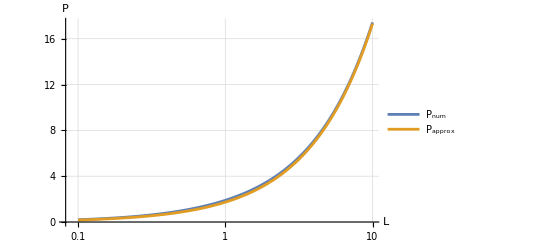

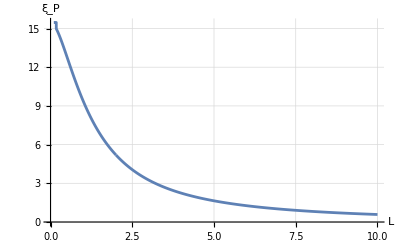

```mathematica
ListLogLinearPlot[{PNumlist,PApproxlist},AxesLabel->{"L","P"},PlotLegends->{"P_num","P_approx"},PlotRange->All,GridLines->Automatic,Joined->True]
ListLinePlot[ErrorPlist,AxesLabel->{"L","ξ_P"},PlotRange->All,GridLines->Automatic]
```

As for the results, it can be seen that P_approx is linear with respect to L and P_num behaves similarly and further approaches  P_approx as L increases until, for L/R >> 1≃5, P_num≃P_approx. This coincides with the concepts of the pdf files.

Regarding the accuracy of the approximation,  P_approx is a satisfactory and appropriate approximation of P_num for L/R >> 1 (a condition that satisfies the phenomenon known as coronal loops), beginning at k_y≃7, where the error between solutions is already < 1 %. However, if precise computations are needed, for L<7, the approximation starts to lack accuracy, especially in the L≤2 regime where the error between solutions varies from  5 % to 15.47 %. In essence, P_approx  is an acceptable approximation in this case (depending on the accuracy needed).